# Pipeline Algebra

## Embeddings + Classification

Translate the quantum circuit operations into purely matrix/vector-based operations (i.e., classical linear algebra). 💃
Represent Qubits and Registers as Vector Spaces
- Each qubit is a 2D complex vector space with computational basis ∣0⟩ = (1
0) and ∣1⟩ = (0
1).
- An 𝑛-qubit register corresponds to a tensor product space of dimension 2^𝑛.
- A full quantum state is a normalized vector in this space.
- Initialize the nodes in an equal superposition, not with different .

# Network Parameters (real)

```mathematica
Print["Importing dataset (edges, degrees, features)..."]
SetDirectory["C:\\Users\\mpatr\\Documents\\Thesis\\ThesisWork"];
edgesRaw = Import["dataset/OmniPath_gene_edges_filtered_with_index.csv"];
degreesRaw = Import["dataset/OmniPath_gene_degrees_filtered_with_index.csv"];
featuresRaw = Import["dataset/MutSig_gene_pvalues_filtered_with_index.csv"];
Print["Finished."]
```

Importing dataset (edges, degrees, features)...

Finished.

Extracting the degrees...

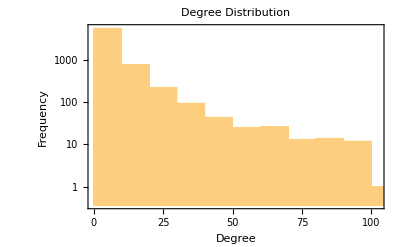

Extracting the features...

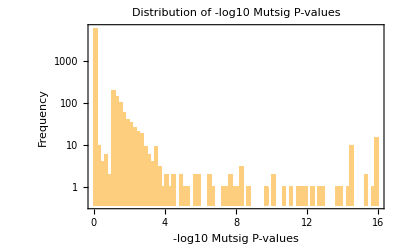

Creating the adjacency list...

Finished.

```mathematica
Print["Extracting the degrees..."]
nodeDegrees = ToExpression[degreesRaw[[2 ;; 6851, 3]]]; (* 2nd row, 3rd column *)
Histogram[nodeDegrees, 50,
  PlotTheme -> "Detailed",
  AxesLabel -> {"Degree", "Frequency"},
  PlotLabel -> "Degree Distribution",
  ScalingFunctions -> "Log"
]

Print["Extracting the features..."]
(* --- Features vector aligned to node indices --- *)
features = ToExpression[featuresRaw[[2 ;; 6851, 4]]]; (* 2nd row, 4th column *)
Histogram[features, 100,
  PlotTheme -> "Detailed",
  AxesLabel -> {"-log10 Mutsig P-values", "Frequency"},
  PlotLabel -> "Distribution of -log10 Mutsig P-values",
  ScalingFunctions -> "Log"
]

Print["Creating the adjacency list..."]
(* --- Adjacency list: each edge is added in both directions --- *)
nrNodes = Length[nodeDegrees]; n = Ceiling[Log2[nrNodes]]; bigN = 2^n;
adjacencyList = Table[{}, {nrNodes}];
Scan[
  (adjacencyList[[#[[1]]]] = Append[adjacencyList[[#[[1]]]], #[[2]]];
   adjacencyList[[#[[2]]]] = Append[adjacencyList[[#[[2]]]], #[[1]]]) &,
  Map[ToExpression, edgesRaw[[2 ;; 27026, {1, 3}]], {2}]
]; 
Print["Finished."]
```

```mathematica
Print["Creating the 'number of second-hop neighbors' table..."]
(* --- Sum of neighbors' degrees for each node --- *)
nodeDegreesC1 = Table[
   Total[nodeDegrees[[adjacencyList[[i]]]]],
   {i, nrNodes}
];

nodeCheck = 13;
neighborsCheck = adjacencyList[[nodeCheck]];
Print["Node: ", nodeCheck];
Print["Degree: ", nodeDegrees[[nodeCheck]]];
Print["Neighbors: ", neighborsCheck];
Print["Neighbors' Degrees: ", nodeDegrees[[neighborsCheck]]];
Print["C1 Degree (sum of neighbors' degrees): ", nodeDegreesC1[[nodeCheck]]];
```

Creating the 'number of second-hop neighbors' table...

Node: 13

Degree: 2

Neighbors: {3890,5786}

Neighbors' Degrees: {85,75}

C1 Degree (sum of neighbors' degrees): 160

Compute scaled features for binary encoding...

Error after quantization: 0.00777401

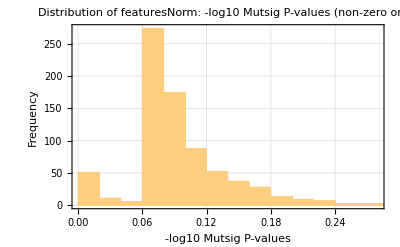

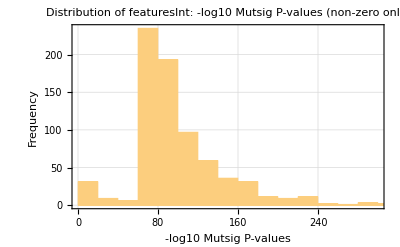

```mathematica
Print["Compute scaled features for binary encoding..."]
p = 10; (* Precision level *)
P = 2^p; (* Scaling factor *)

featuresNorm = (features - Min[features])/(Max[features] - Min[features]);
featuresInt = Round[featuresNorm * P];
featuresCheck = featuresInt / P * (Max[features] - Min[features]) + Min[features];
Print["Error after quantization: ", Max[Abs[features - featuresCheck]]];

Histogram[Select[featuresNorm, # > 0 &], 50, "Count",
  PlotTheme -> "Detailed",
  AxesLabel -> {"-log10 Mutsig P-values", "Frequency"},
  PlotLabel -> "Distribution of featuresNorm: -log10 Mutsig P-values (non-zero only)"
]

Histogram[Select[featuresInt, # > 0 &], 50, "Count",
  PlotTheme -> "Detailed",
  AxesLabel -> {"-log10 Mutsig P-values", "Frequency"},
  PlotLabel -> "Distribution of featuresInt: -log10 Mutsig P-values (non-zero only)"
]
```

```mathematica
(* --- Compute m_c1 and s_c1 --- *)
Print["Number of nodes: ", nrNodes, ", n=", n, ", bigN=", bigN];
maxD = Max[nodeDegrees]; m = Ceiling[Log2[maxD]]; s = 2^m;
Print["Immediate neighbors: max=", maxD, ", m=", m, ", s=", s];
maxC1 = Max[nodeDegreesC1]; mC1 = Ceiling[Log2[maxC1]]; sC1 = 2^mC1;
Print["Second-hop neighbors: max=", maxC1, ", m_c1=", mC1, ", s_c1=", sC1];
Print["Features scaling: maxFeat=", Max[features], ", p=", p, ", P=", P];

(*--------------------------------------- Dimensions for each register ---------------------------------------*)
swapDim = 2^5 * 2^3 * 2^m * 2^m;
fullDim = swapDim * 2^p * 2^mC1 * 2^n * 2^n * 2^n; (* dim-features * dim_Z * dim_K * dim_u1 * dim_U2 * dim_V *)

(* number of qubits: QuantumCircuit(qr_a, qr_z, qr_k, qr_u2, qr_u1, qr_l2, qr_l1, qr_c, qr_i, qr_v) *)
Print["Full dimension: ", fullDim];
Print["Swap dimension: ", swapDim];
Print["Full dim (qubits): ", Log2[fullDim]]
Print["Swap dim (qubits): ", Log2[swapDim]]
```

Number of nodes: 6850, n=13, bigN=8192

Immediate neighbors: max=601, m=10, s=1024

Second-hop neighbors: max=14061, m_c1=14, s_c1=16384

Features scaling: maxFeat=15.9546, p=10, P=1024

Full dimension: 2475880078570760549798248448

Swap dimension: 268435456

Full dim (qubits): 91

Swap dim (qubits): 28

# Unitary Gates

## Simple Gates

```mathematica
H = (1/Sqrt[2]) * {
  {1, 1},
  {1, -1}
};

H2 = (1/2) * {
  {1, 1, 1, 1},
  {1, -1, 1, -1},
  {1, 1, -1, -1},
  {1, -1, -1, 1}
};

H3 = (1/Sqrt[8]) * {
  {1, 1, 1, 1, 1, 1, 1, 1},
  {1, -1, 1, -1, 1, -1, 1, -1},
  {1, 1, -1, -1, 1, 1, -1, -1},
  {1, -1, -1, 1, 1, -1, -1, 1},
  {1, 1, 1, 1, -1, -1, -1, -1},
  {1, -1, 1, -1, -1, 1, -1, 1},
  {1, 1, -1, -1, -1, -1, 1, 1},
  {1, -1, -1, 1, -1, 1, 1, -1}
};

H4 = (1/4) * {
  {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1},
  {1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1},
  {1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1},
  {1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1},
  {1, 1, 1, 1, -1, -1, -1, -1, 1, 1, 1, 1, -1, -1, -1, -1},
  {1, -1, 1, -1, -1, 1, -1, 1, 1, -1, 1, -1, -1, 1, -1, 1},
  {1, 1, -1, -1, -1, -1, 1, 1, 1, 1, -1, -1, -1, -1, 1, 1},
  {1, -1, -1, 1, -1, 1, 1, -1, 1, -1, -1, 1, -1, 1, 1, -1},
  {1, 1, 1, 1, 1, 1, 1, 1, -1, -1, -1, -1, -1, -1, -1, -1},
  {1, -1, 1, -1, 1, -1, 1, -1, -1, 1, -1, 1, -1, 1, -1, 1},
  {1, 1, -1, -1, 1, 1, -1, -1, -1, -1, 1, 1, -1, -1, 1, 1},
  {1, -1, -1, 1, 1, -1, -1, 1, -1, 1, 1, -1, -1, 1, 1, -1},
  {1, 1, 1, 1, -1, -1, -1, -1, -1, -1, -1, -1, 1, 1, 1, 1},
  {1, -1, 1, -1, -1, 1, -1, 1, -1, 1, -1, 1, 1, -1, 1, -1},
  {1, 1, -1, -1, -1, -1, 1, 1, -1, -1, 1, 1, 1, 1, -1, -1},
  {1, -1, -1, 1, -1, 1, 1, -1, -1, 1, 1, -1, 1, -1, -1, 1}
};

Print["Computing H10..."]
H10 = Table[
   (-1)^(BitAnd @@ (IntegerDigits[i, 2, m] * IntegerDigits[j, 2, m])),
   {i, 0, s - 1}, {j, 0, s - 1}
]/Sqrt[n];
Print["Finished."]
```

Computing H10...

Finished.

```mathematica
(*--------------------------------------- Hadamard Matrices ---------------------------------------*)

Hl = Switch[m,
  1, H,
  2, H2,
  3, H3,
  4, H4,
  10, H10,
  _, MessageDialog["Only m = 1 to 4, and 10 is supported"]
];

(*--------------------------------------- Feature Rotation Matrix ---------------------------------------*)

Wtheta[theta_] := {
  {Cos[theta/2], -Sin[theta/2]},
  {Sin[theta/2],  Cos[theta/2]}
};

Wval[val_] := {
  {val, -Sqrt[1 - val^2]},
  {Sqrt[1 - val^2], val}
};

Print["Wtheta[0.5] =", MatrixForm[Wtheta[0.5]]];
Print["Wval[1] =", MatrixForm[Wval[0.8]]];
```

Wtheta[0.5] =(0.968912 | -0.247404
0.247404 | 0.968912)

Wval[1] =(0.8 | -0.6
0.6 | 0.8)

## OX: Equivalent Feature Rotation

Given node v and neighbor index l, it retrieves the 2x2 feature rotation matrix F_X(u=r(v,l)) to act on the 1-qubit ancilla .

```mathematica
Print["Creating FeatureRotation gate..."]
(* Need to triple check. *)
GetFeatureRotation[v_Integer, l_Integer] := Module[
  {u, featVal},

  (* Check if v and l are valid indices *)
  If[
    1 <= v <= nrNodes && 1 <= l <= nodeDegrees[[v]],
    
    u = adjacencyList[[v, l]]; (* In Mathematica, indexing starts at 1 *)
    featVal = featuresNorm[[u]];
    Wval[featVal],
    (* If invalid, take the feature value to be zero. *)
    MatrixForm[Wval[0]];
  ]
];

MatrixForm[GetFeatureRotation[nodeCheck, 1]]
Print["Finished."]

Print["Node: ", nodeCheck];
Print["Neighbor: ", neighborsCheck[[1]]];
Print["Neighbor's FeatureNorm: ", featuresNorm[[neighborsCheck[[1]]]]];
```

Creating FeatureRotation gate...

(0.370714 | -0.928747
0.928747 | 0.370714)

Finished.

Node: 13

Neighbor: 3890

Neighbor's FeatureNorm: 0.370714

## OK^-1: Equivalent Feature Rotation

Given node v and neighborhood-hop index c, it retrieves the 2x2 feature rotation matrix F_(K^{-1})(v) to act on the 1-qubit ancilla .

```mathematica
Print["Creating DegreeRotation gate..."]
GetDegreeRotation[v_Integer, c_Integer] := Module[
  {deg, theta},
  
  deg = Switch[c,
    1, nodeDegrees[[v]],   (* default 0 if key not found *)
    2, nodeDegreesC1[[v]], (* if you have a separate assoc for c=2 *)
    _, Return[IdentityMatrix[2]]
  ];

  If[deg < 1, Return[IdentityMatrix[2]]];
  theta = 2 ArcCos[1.0 / deg];
  Wtheta[theta]
];
MatrixForm[GetDegreeRotation[nodeCheck, 1]]
MatrixForm[GetDegreeRotation[nodeCheck, 2]]
Print["Finished."]
```

Creating DegreeRotation gate...

(0.5 | -0.866025
0.866025 | 0.5)

(0.00625 | -0.99998
0.99998 | 0.00625)

Finished.

# QMME Circuit

## c=1: Feature Embeddings for (v, l, i)

First-hop neighborhood: For each (v, l), get the 4*1024 feature vectors (for each i, l) of dimension  = 16 (corresponding to 4 ancilla rotations).

```mathematica
Print["Creating firstHopStates..."];

firstHopStates = Reap[
  Do[
    featVec = GetFeatureRotation[v, l] . {1, 0};
    Print["v: ", v, ", l: ", l, ", i: ", i]
    (* Precompute all Kronecker combinations once for each featVec *)
    vectListBase = Table[{1, 0}, {4}];
    Do[
      vectList = ReplacePart[vectListBase, Table[k -> featVec, {k, 1, i}]];
      combinedVec = Fold[KroneckerProduct, First[vectList], Rest[vectList]] // Flatten;
      Sow[<|
        "v" -> v,
        "i" -> i,
        "l" -> l,
        "u" -> If[1 <= l <= nodeDegrees[[v]], adjacencyList[[v, l]], nrNodes + 1], (* OL oracle flag * is nrNodes + 1 *)
        "featVec" -> featVec,
        "state" -> combinedVec
      |>],
      {i, 1, 4}
    ],
    {v, 1, nrNodes}, {l, 1, s}
  ]
][[2, 1]];
Print["Finished."]
```

Creating firstHopStates...

v: 1, l: 1, i: i

Set::write: Tag Times in Null vectListBase is Protected.

First::normal: Nonatomic expression expected at position 1 in First[vectListBase].

Rest::normal: Nonatomic expression expected at position 1 in Rest[vectListBase].

First::normal: Nonatomic expression expected at position 1 in First[vectListBase].

Rest::normal: Nonatomic expression expected at position 1 in Rest[vectListBase].

First::normal: Nonatomic expression expected at position 1 in First[vectListBase].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[vectListBase].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

v: 1, l: 2, i: i

Set::write: Tag Times in Null vectListBase is Protected.

v: 1, l: 3, i: i

Set::write: Tag Times in Null vectListBase is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

v: 1, l: 4, i: i

v: 1, l: 5, i: i

v: 1, l: 6, i: i

v: 1, l: 7, i: i

v: 1, l: 8, i: i

v: 1, l: 9, i: i

v: 1, l: 10, i: i

v: 1, l: 11, i: i

v: 1, l: 12, i: i

v: 1, l: 13, i: i

v: 1, l: 14, i: i

v: 1, l: 15, i: i

v: 1, l: 16, i: i

v: 1, l: 17, i: i

v: 1, l: 18, i: i

v: 1, l: 19, i: i

v: 1, l: 20, i: i

v: 1, l: 21, i: i

v: 1, l: 22, i: i

v: 1, l: 23, i: i

v: 1, l: 24, i: i

v: 1, l: 25, i: i

v: 1, l: 26, i: i

v: 1, l: 27, i: i

v: 1, l: 28, i: i

v: 1, l: 29, i: i

v: 1, l: 30, i: i

v: 1, l: 31, i: i

v: 1, l: 32, i: i

v: 1, l: 33, i: i

v: 1, l: 34, i: i

v: 1, l: 35, i: i

v: 1, l: 36, i: i

v: 1, l: 37, i: i

v: 1, l: 38, i: i

v: 1, l: 39, i: i

v: 1, l: 40, i: i

v: 1, l: 41, i: i

v: 1, l: 42, i: i

v: 1, l: 43, i: i

v: 1, l: 44, i: i

v: 1, l: 45, i: i

v: 1, l: 46, i: i

v: 1, l: 47, i: i

v: 1, l: 48, i: i

v: 1, l: 49, i: i

v: 1, l: 50, i: i

v: 1, l: 51, i: i

v: 1, l: 52, i: i

v: 1, l: 53, i: i

v: 1, l: 54, i: i

v: 1, l: 55, i: i

v: 1, l: 56, i: i

v: 1, l: 57, i: i

v: 1, l: 58, i: i

v: 1, l: 59, i: i

v: 1, l: 60, i: i

v: 1, l: 61, i: i

v: 1, l: 62, i: i

v: 1, l: 63, i: i

v: 1, l: 64, i: i

v: 1, l: 65, i: i

v: 1, l: 66, i: i

v: 1, l: 67, i: i

v: 1, l: 68, i: i

v: 1, l: 69, i: i

v: 1, l: 70, i: i

v: 1, l: 71, i: i

v: 1, l: 72, i: i

v: 1, l: 73, i: i

v: 1, l: 74, i: i

v: 1, l: 75, i: i

v: 1, l: 76, i: i

v: 1, l: 77, i: i

v: 1, l: 78, i: i

v: 1, l: 79, i: i

v: 1, l: 80, i: i

v: 1, l: 81, i: i

v: 1, l: 82, i: i

v: 1, l: 83, i: i

v: 1, l: 84, i: i

v: 1, l: 85, i: i

v: 1, l: 86, i: i

v: 1, l: 87, i: i

v: 1, l: 88, i: i

v: 1, l: 89, i: i

v: 1, l: 90, i: i

v: 1, l: 91, i: i

v: 1, l: 92, i: i

v: 1, l: 93, i: i

v: 1, l: 94, i: i

v: 1, l: 95, i: i

v: 1, l: 96, i: i

v: 1, l: 97, i: i

v: 1, l: 98, i: i

v: 1, l: 99, i: i

v: 1, l: 100, i: i

v: 1, l: 101, i: i

v: 1, l: 102, i: i

v: 1, l: 103, i: i

v: 1, l: 104, i: i

v: 1, l: 105, i: i

v: 1, l: 106, i: i

v: 1, l: 107, i: i

v: 1, l: 108, i: i

v: 1, l: 109, i: i

v: 1, l: 110, i: i

v: 1, l: 111, i: i

v: 1, l: 112, i: i

v: 1, l: 113, i: i

v: 1, l: 114, i: i

v: 1, l: 115, i: i

v: 1, l: 116, i: i

v: 1, l: 117, i: i

v: 1, l: 118, i: i

v: 1, l: 119, i: i

v: 1, l: 120, i: i

v: 1, l: 121, i: i

v: 1, l: 122, i: i

v: 1, l: 123, i: i

v: 1, l: 124, i: i

v: 1, l: 125, i: i

v: 1, l: 126, i: i

v: 1, l: 127, i: i

v: 1, l: 128, i: i

v: 1, l: 129, i: i

v: 1, l: 130, i: i

v: 1, l: 131, i: i

v: 1, l: 132, i: i

v: 1, l: 133, i: i

v: 1, l: 134, i: i

v: 1, l: 135, i: i

v: 1, l: 136, i: i

v: 1, l: 137, i: i

v: 1, l: 138, i: i

v: 1, l: 139, i: i

v: 1, l: 140, i: i

v: 1, l: 141, i: i

v: 1, l: 142, i: i

v: 1, l: 143, i: i

v: 1, l: 144, i: i

v: 1, l: 145, i: i

v: 1, l: 146, i: i

v: 1, l: 147, i: i

v: 1, l: 148, i: i

v: 1, l: 149, i: i

v: 1, l: 150, i: i

v: 1, l: 151, i: i

v: 1, l: 152, i: i

v: 1, l: 153, i: i

v: 1, l: 154, i: i

v: 1, l: 155, i: i

v: 1, l: 156, i: i

v: 1, l: 157, i: i

v: 1, l: 158, i: i

v: 1, l: 159, i: i

v: 1, l: 160, i: i

v: 1, l: 161, i: i

v: 1, l: 162, i: i

v: 1, l: 163, i: i

v: 1, l: 164, i: i

v: 1, l: 165, i: i

v: 1, l: 166, i: i

v: 1, l: 167, i: i

v: 1, l: 168, i: i

v: 1, l: 169, i: i

v: 1, l: 170, i: i

v: 1, l: 171, i: i

v: 1, l: 172, i: i

v: 1, l: 173, i: i

v: 1, l: 174, i: i

v: 1, l: 175, i: i

v: 1, l: 176, i: i

v: 1, l: 177, i: i

v: 1, l: 178, i: i

v: 1, l: 179, i: i

v: 1, l: 180, i: i

v: 1, l: 181, i: i

v: 1, l: 182, i: i

v: 1, l: 183, i: i

v: 1, l: 184, i: i

v: 1, l: 185, i: i

v: 1, l: 186, i: i

v: 1, l: 187, i: i

v: 1, l: 188, i: i

v: 1, l: 189, i: i

v: 1, l: 190, i: i

v: 1, l: 191, i: i

v: 1, l: 192, i: i

v: 1, l: 193, i: i

v: 1, l: 194, i: i

v: 1, l: 195, i: i

v: 1, l: 196, i: i

v: 1, l: 197, i: i

v: 1, l: 198, i: i

v: 1, l: 199, i: i

v: 1, l: 200, i: i

v: 1, l: 201, i: i

v: 1, l: 202, i: i

v: 1, l: 203, i: i

v: 1, l: 204, i: i

v: 1, l: 205, i: i

v: 1, l: 206, i: i

v: 1, l: 207, i: i

v: 1, l: 208, i: i

v: 1, l: 209, i: i

v: 1, l: 210, i: i

v: 1, l: 211, i: i

v: 1, l: 212, i: i

v: 1, l: 213, i: i

v: 1, l: 214, i: i

v: 1, l: 215, i: i

v: 1, l: 216, i: i

v: 1, l: 217, i: i

v: 1, l: 218, i: i

v: 1, l: 219, i: i

v: 1, l: 220, i: i

v: 1, l: 221, i: i

v: 1, l: 222, i: i

v: 1, l: 223, i: i

v: 1, l: 224, i: i

v: 1, l: 225, i: i

v: 1, l: 226, i: i

v: 1, l: 227, i: i

v: 1, l: 228, i: i

v: 1, l: 229, i: i

v: 1, l: 230, i: i

v: 1, l: 231, i: i

v: 1, l: 232, i: i

v: 1, l: 233, i: i

v: 1, l: 234, i: i

v: 1, l: 235, i: i

v: 1, l: 236, i: i

v: 1, l: 237, i: i

v: 1, l: 238, i: i

v: 1, l: 239, i: i

v: 1, l: 240, i: i

v: 1, l: 241, i: i

v: 1, l: 242, i: i

v: 1, l: 243, i: i

v: 1, l: 244, i: i

v: 1, l: 245, i: i

v: 1, l: 246, i: i

v: 1, l: 247, i: i

v: 1, l: 248, i: i

v: 1, l: 249, i: i

v: 1, l: 250, i: i

v: 1, l: 251, i: i

v: 1, l: 252, i: i

v: 1, l: 253, i: i

v: 1, l: 254, i: i

v: 1, l: 255, i: i

v: 1, l: 256, i: i

v: 1, l: 257, i: i

v: 1, l: 258, i: i

v: 1, l: 259, i: i

v: 1, l: 260, i: i

v: 1, l: 261, i: i

v: 1, l: 262, i: i

v: 1, l: 263, i: i

v: 1, l: 264, i: i

v: 1, l: 265, i: i

v: 1, l: 266, i: i

v: 1, l: 267, i: i

v: 1, l: 268, i: i

v: 1, l: 269, i: i

v: 1, l: 270, i: i

v: 1, l: 271, i: i

v: 1, l: 272, i: i

v: 1, l: 273, i: i

v: 1, l: 274, i: i

v: 1, l: 275, i: i

v: 1, l: 276, i: i

v: 1, l: 277, i: i

v: 1, l: 278, i: i

v: 1, l: 279, i: i

v: 1, l: 280, i: i

v: 1, l: 281, i: i

v: 1, l: 282, i: i

v: 1, l: 283, i: i

v: 1, l: 284, i: i

v: 1, l: 285, i: i

v: 1, l: 286, i: i

v: 1, l: 287, i: i

v: 1, l: 288, i: i

v: 1, l: 289, i: i

v: 1, l: 290, i: i

v: 1, l: 291, i: i

v: 1, l: 292, i: i

v: 1, l: 293, i: i

v: 1, l: 294, i: i

v: 1, l: 295, i: i

v: 1, l: 296, i: i

v: 1, l: 297, i: i

v: 1, l: 298, i: i

v: 1, l: 299, i: i

v: 1, l: 300, i: i

v: 1, l: 301, i: i

v: 1, l: 302, i: i

v: 1, l: 303, i: i

v: 1, l: 304, i: i

v: 1, l: 305, i: i

v: 1, l: 306, i: i

v: 1, l: 307, i: i

v: 1, l: 308, i: i

v: 1, l: 309, i: i

v: 1, l: 310, i: i

v: 1, l: 311, i: i

v: 1, l: 312, i: i

v: 1, l: 313, i: i

v: 1, l: 314, i: i

v: 1, l: 315, i: i

v: 1, l: 316, i: i

v: 1, l: 317, i: i

v: 1, l: 318, i: i

v: 1, l: 319, i: i

v: 1, l: 320, i: i

v: 1, l: 321, i: i

v: 1, l: 322, i: i

v: 1, l: 323, i: i

v: 1, l: 324, i: i

v: 1, l: 325, i: i

v: 1, l: 326, i: i

v: 1, l: 327, i: i

v: 1, l: 328, i: i

v: 1, l: 329, i: i

v: 1, l: 330, i: i

v: 1, l: 331, i: i

v: 1, l: 332, i: i

v: 1, l: 333, i: i

v: 1, l: 334, i: i

v: 1, l: 335, i: i

v: 1, l: 336, i: i

v: 1, l: 337, i: i

v: 1, l: 338, i: i

v: 1, l: 339, i: i

v: 1, l: 340, i: i

v: 1, l: 341, i: i

v: 1, l: 342, i: i

v: 1, l: 343, i: i

v: 1, l: 344, i: i

v: 1, l: 345, i: i

v: 1, l: 346, i: i

v: 1, l: 347, i: i

v: 1, l: 348, i: i

v: 1, l: 349, i: i

v: 1, l: 350, i: i

v: 1, l: 351, i: i

v: 1, l: 352, i: i

v: 1, l: 353, i: i

v: 1, l: 354, i: i

v: 1, l: 355, i: i

v: 1, l: 356, i: i

v: 1, l: 357, i: i

v: 1, l: 358, i: i

v: 1, l: 359, i: i

v: 1, l: 360, i: i

v: 1, l: 361, i: i

v: 1, l: 362, i: i

v: 1, l: 363, i: i

v: 1, l: 364, i: i

v: 1, l: 365, i: i

v: 1, l: 366, i: i

v: 1, l: 367, i: i

v: 1, l: 368, i: i

v: 1, l: 369, i: i

v: 1, l: 370, i: i

v: 1, l: 371, i: i

v: 1, l: 372, i: i

v: 1, l: 373, i: i

v: 1, l: 374, i: i

v: 1, l: 375, i: i

v: 1, l: 376, i: i

v: 1, l: 377, i: i

v: 1, l: 378, i: i

v: 1, l: 379, i: i

v: 1, l: 380, i: i

v: 1, l: 381, i: i

v: 1, l: 382, i: i

v: 1, l: 383, i: i

v: 1, l: 384, i: i

v: 1, l: 385, i: i

v: 1, l: 386, i: i

v: 1, l: 387, i: i

v: 1, l: 388, i: i

v: 1, l: 389, i: i

v: 1, l: 390, i: i

v: 1, l: 391, i: i

v: 1, l: 392, i: i

v: 1, l: 393, i: i

v: 1, l: 394, i: i

v: 1, l: 395, i: i

v: 1, l: 396, i: i

v: 1, l: 397, i: i

v: 1, l: 398, i: i

v: 1, l: 399, i: i

v: 1, l: 400, i: i

v: 1, l: 401, i: i

v: 1, l: 402, i: i

v: 1, l: 403, i: i

v: 1, l: 404, i: i

v: 1, l: 405, i: i

v: 1, l: 406, i: i

v: 1, l: 407, i: i

v: 1, l: 408, i: i

v: 1, l: 409, i: i

v: 1, l: 410, i: i

v: 1, l: 411, i: i

v: 1, l: 412, i: i

v: 1, l: 413, i: i

v: 1, l: 414, i: i

v: 1, l: 415, i: i

v: 1, l: 416, i: i

v: 1, l: 417, i: i

v: 1, l: 418, i: i

v: 1, l: 419, i: i

v: 1, l: 420, i: i

v: 1, l: 421, i: i

v: 1, l: 422, i: i

v: 1, l: 423, i: i

v: 1, l: 424, i: i

v: 1, l: 425, i: i

v: 1, l: 426, i: i

v: 1, l: 427, i: i

v: 1, l: 428, i: i

v: 1, l: 429, i: i

v: 1, l: 430, i: i

v: 1, l: 431, i: i

v: 1, l: 432, i: i

v: 1, l: 433, i: i

v: 1, l: 434, i: i

v: 1, l: 435, i: i

v: 1, l: 436, i: i

v: 1, l: 437, i: i

v: 1, l: 438, i: i

v: 1, l: 439, i: i

v: 1, l: 440, i: i

v: 1, l: 441, i: i

v: 1, l: 442, i: i

v: 1, l: 443, i: i

v: 1, l: 444, i: i

v: 1, l: 445, i: i

v: 1, l: 446, i: i

v: 1, l: 447, i: i

v: 1, l: 448, i: i

v: 1, l: 449, i: i

v: 1, l: 450, i: i

v: 1, l: 451, i: i

v: 1, l: 452, i: i

v: 1, l: 453, i: i

v: 1, l: 454, i: i

v: 1, l: 455, i: i

v: 1, l: 456, i: i

v: 1, l: 457, i: i

v: 1, l: 458, i: i

v: 1, l: 459, i: i

v: 1, l: 460, i: i

v: 1, l: 461, i: i

v: 1, l: 462, i: i

v: 1, l: 463, i: i

v: 1, l: 464, i: i

v: 1, l: 465, i: i

v: 1, l: 466, i: i

v: 1, l: 467, i: i

v: 1, l: 468, i: i

v: 1, l: 469, i: i

v: 1, l: 470, i: i

v: 1, l: 471, i: i

v: 1, l: 472, i: i

v: 1, l: 473, i: i

v: 1, l: 474, i: i

v: 1, l: 475, i: i

v: 1, l: 476, i: i

v: 1, l: 477, i: i

v: 1, l: 478, i: i

v: 1, l: 479, i: i

v: 1, l: 480, i: i

v: 1, l: 481, i: i

v: 1, l: 482, i: i

v: 1, l: 483, i: i

v: 1, l: 484, i: i

v: 1, l: 485, i: i

v: 1, l: 486, i: i

v: 1, l: 487, i: i

v: 1, l: 488, i: i

v: 1, l: 489, i: i

v: 1, l: 490, i: i

v: 1, l: 491, i: i

v: 1, l: 492, i: i

v: 1, l: 493, i: i

v: 1, l: 494, i: i

v: 1, l: 495, i: i

v: 1, l: 496, i: i

v: 1, l: 497, i: i

v: 1, l: 498, i: i

v: 1, l: 499, i: i

v: 1, l: 500, i: i

v: 1, l: 501, i: i

v: 1, l: 502, i: i

v: 1, l: 503, i: i

v: 1, l: 504, i: i

v: 1, l: 505, i: i

v: 1, l: 506, i: i

v: 1, l: 507, i: i

v: 1, l: 508, i: i

v: 1, l: 509, i: i

v: 1, l: 510, i: i

v: 1, l: 511, i: i

v: 1, l: 512, i: i

v: 1, l: 513, i: i

v: 1, l: 514, i: i

v: 1, l: 515, i: i

v: 1, l: 516, i: i

v: 1, l: 517, i: i

v: 1, l: 518, i: i

v: 1, l: 519, i: i

v: 1, l: 520, i: i

v: 1, l: 521, i: i

v: 1, l: 522, i: i

v: 1, l: 523, i: i

v: 1, l: 524, i: i

v: 1, l: 525, i: i

v: 1, l: 526, i: i

v: 1, l: 527, i: i

v: 1, l: 528, i: i

v: 1, l: 529, i: i

v: 1, l: 530, i: i

v: 1, l: 531, i: i

v: 1, l: 532, i: i

v: 1, l: 533, i: i

v: 1, l: 534, i: i

v: 1, l: 535, i: i

v: 1, l: 536, i: i

v: 1, l: 537, i: i

v: 1, l: 538, i: i

v: 1, l: 539, i: i

v: 1, l: 540, i: i

v: 1, l: 541, i: i

v: 1, l: 542, i: i

v: 1, l: 543, i: i

v: 1, l: 544, i: i

v: 1, l: 545, i: i

v: 1, l: 546, i: i

v: 1, l: 547, i: i

v: 1, l: 548, i: i

v: 1, l: 549, i: i

v: 1, l: 550, i: i

v: 1, l: 551, i: i

v: 1, l: 552, i: i

v: 1, l: 553, i: i

v: 1, l: 554, i: i

v: 1, l: 555, i: i

v: 1, l: 556, i: i

v: 1, l: 557, i: i

v: 1, l: 558, i: i

v: 1, l: 559, i: i

v: 1, l: 560, i: i

v: 1, l: 561, i: i

v: 1, l: 562, i: i

v: 1, l: 563, i: i

v: 1, l: 564, i: i

v: 1, l: 565, i: i

v: 1, l: 566, i: i

v: 1, l: 567, i: i

v: 1, l: 568, i: i

v: 1, l: 569, i: i

v: 1, l: 570, i: i

v: 1, l: 571, i: i

v: 1, l: 572, i: i

v: 1, l: 573, i: i

v: 1, l: 574, i: i

v: 1, l: 575, i: i

v: 1, l: 576, i: i

v: 1, l: 577, i: i

v: 1, l: 578, i: i

v: 1, l: 579, i: i

v: 1, l: 580, i: i

v: 1, l: 581, i: i

v: 1, l: 582, i: i

v: 1, l: 583, i: i

v: 1, l: 584, i: i

v: 1, l: 585, i: i

v: 1, l: 586, i: i

v: 1, l: 587, i: i

v: 1, l: 588, i: i

v: 1, l: 589, i: i

v: 1, l: 590, i: i

v: 1, l: 591, i: i

v: 1, l: 592, i: i

v: 1, l: 593, i: i

v: 1, l: 594, i: i

v: 1, l: 595, i: i

v: 1, l: 596, i: i

v: 1, l: 597, i: i

v: 1, l: 598, i: i

v: 1, l: 599, i: i

v: 1, l: 600, i: i

v: 1, l: 601, i: i

v: 1, l: 602, i: i

v: 1, l: 603, i: i

v: 1, l: 604, i: i

v: 1, l: 605, i: i

v: 1, l: 606, i: i

v: 1, l: 607, i: i

v: 1, l: 608, i: i

v: 1, l: 609, i: i

v: 1, l: 610, i: i

v: 1, l: 611, i: i

v: 1, l: 612, i: i

v: 1, l: 613, i: i

v: 1, l: 614, i: i

v: 1, l: 615, i: i

v: 1, l: 616, i: i

v: 1, l: 617, i: i

v: 1, l: 618, i: i

v: 1, l: 619, i: i

v: 1, l: 620, i: i

v: 1, l: 621, i: i

v: 1, l: 622, i: i

v: 1, l: 623, i: i

v: 1, l: 624, i: i

v: 1, l: 625, i: i

v: 1, l: 626, i: i

v: 1, l: 627, i: i

v: 1, l: 628, i: i

v: 1, l: 629, i: i

v: 1, l: 630, i: i

v: 1, l: 631, i: i

v: 1, l: 632, i: i

v: 1, l: 633, i: i

v: 1, l: 634, i: i

v: 1, l: 635, i: i

v: 1, l: 636, i: i

v: 1, l: 637, i: i

v: 1, l: 638, i: i

v: 1, l: 639, i: i

v: 1, l: 640, i: i

v: 1, l: 641, i: i

v: 1, l: 642, i: i

v: 1, l: 643, i: i

v: 1, l: 644, i: i

v: 1, l: 645, i: i

v: 1, l: 646, i: i

v: 1, l: 647, i: i

v: 1, l: 648, i: i

v: 1, l: 649, i: i

v: 1, l: 650, i: i

v: 1, l: 651, i: i

v: 1, l: 652, i: i

v: 1, l: 653, i: i

v: 1, l: 654, i: i

v: 1, l: 655, i: i

v: 1, l: 656, i: i

v: 1, l: 657, i: i

v: 1, l: 658, i: i

v: 1, l: 659, i: i

v: 1, l: 660, i: i

v: 1, l: 661, i: i

v: 1, l: 662, i: i

v: 1, l: 663, i: i

v: 1, l: 664, i: i

v: 1, l: 665, i: i

v: 1, l: 666, i: i

v: 1, l: 667, i: i

v: 1, l: 668, i: i

v: 1, l: 669, i: i

v: 1, l: 670, i: i

v: 1, l: 671, i: i

v: 1, l: 672, i: i

v: 1, l: 673, i: i

v: 1, l: 674, i: i

v: 1, l: 675, i: i

v: 1, l: 676, i: i

v: 1, l: 677, i: i

v: 1, l: 678, i: i

v: 1, l: 679, i: i

v: 1, l: 680, i: i

v: 1, l: 681, i: i

v: 1, l: 682, i: i

v: 1, l: 683, i: i

v: 1, l: 684, i: i

v: 1, l: 685, i: i

v: 1, l: 686, i: i

v: 1, l: 687, i: i

v: 1, l: 688, i: i

v: 1, l: 689, i: i

v: 1, l: 690, i: i

v: 1, l: 691, i: i

v: 1, l: 692, i: i

v: 1, l: 693, i: i

v: 1, l: 694, i: i

v: 1, l: 695, i: i

v: 1, l: 696, i: i

v: 1, l: 697, i: i

v: 1, l: 698, i: i

v: 1, l: 699, i: i

v: 1, l: 700, i: i

v: 1, l: 701, i: i

v: 1, l: 702, i: i

v: 1, l: 703, i: i

v: 1, l: 704, i: i

v: 1, l: 705, i: i

v: 1, l: 706, i: i

v: 1, l: 707, i: i

v: 1, l: 708, i: i

v: 1, l: 709, i: i

v: 1, l: 710, i: i

v: 1, l: 711, i: i

v: 1, l: 712, i: i

v: 1, l: 713, i: i

v: 1, l: 714, i: i

v: 1, l: 715, i: i

v: 1, l: 716, i: i

v: 1, l: 717, i: i

v: 1, l: 718, i: i

v: 1, l: 719, i: i

v: 1, l: 720, i: i

v: 1, l: 721, i: i

v: 1, l: 722, i: i

v: 1, l: 723, i: i

v: 1, l: 724, i: i

v: 1, l: 725, i: i

v: 1, l: 726, i: i

v: 1, l: 727, i: i

v: 1, l: 728, i: i

v: 1, l: 729, i: i

v: 1, l: 730, i: i

v: 1, l: 731, i: i

v: 1, l: 732, i: i

v: 1, l: 733, i: i

v: 1, l: 734, i: i

v: 1, l: 735, i: i

v: 1, l: 736, i: i

v: 1, l: 737, i: i

v: 1, l: 738, i: i

v: 1, l: 739, i: i

v: 1, l: 740, i: i

v: 1, l: 741, i: i

v: 1, l: 742, i: i

v: 1, l: 743, i: i

v: 1, l: 744, i: i

v: 1, l: 745, i: i

v: 1, l: 746, i: i

v: 1, l: 747, i: i

v: 1, l: 748, i: i

v: 1, l: 749, i: i

v: 1, l: 750, i: i

v: 1, l: 751, i: i

v: 1, l: 752, i: i

v: 1, l: 753, i: i

v: 1, l: 754, i: i

v: 1, l: 755, i: i

v: 1, l: 756, i: i

v: 1, l: 757, i: i

v: 1, l: 758, i: i

v: 1, l: 759, i: i

v: 1, l: 760, i: i

v: 1, l: 761, i: i

v: 1, l: 762, i: i

v: 1, l: 763, i: i

v: 1, l: 764, i: i

v: 1, l: 765, i: i

v: 1, l: 766, i: i

v: 1, l: 767, i: i

v: 1, l: 768, i: i

v: 1, l: 769, i: i

v: 1, l: 770, i: i

v: 1, l: 771, i: i

v: 1, l: 772, i: i

v: 1, l: 773, i: i

v: 1, l: 774, i: i

v: 1, l: 775, i: i

v: 1, l: 776, i: i

v: 1, l: 777, i: i

v: 1, l: 778, i: i

v: 1, l: 779, i: i

v: 1, l: 780, i: i

v: 1, l: 781, i: i

v: 1, l: 782, i: i

v: 1, l: 783, i: i

v: 1, l: 784, i: i

v: 1, l: 785, i: i

v: 1, l: 786, i: i

v: 1, l: 787, i: i

v: 1, l: 788, i: i

v: 1, l: 789, i: i

v: 1, l: 790, i: i

v: 1, l: 791, i: i

v: 1, l: 792, i: i

v: 1, l: 793, i: i

v: 1, l: 794, i: i

v: 1, l: 795, i: i

v: 1, l: 796, i: i

v: 1, l: 797, i: i

v: 1, l: 798, i: i

v: 1, l: 799, i: i

v: 1, l: 800, i: i

v: 1, l: 801, i: i

v: 1, l: 802, i: i

v: 1, l: 803, i: i

v: 1, l: 804, i: i

v: 1, l: 805, i: i

v: 1, l: 806, i: i

v: 1, l: 807, i: i

v: 1, l: 808, i: i

v: 1, l: 809, i: i

v: 1, l: 810, i: i

v: 1, l: 811, i: i

v: 1, l: 812, i: i

v: 1, l: 813, i: i

v: 1, l: 814, i: i

v: 1, l: 815, i: i

v: 1, l: 816, i: i

v: 1, l: 817, i: i

v: 1, l: 818, i: i

v: 1, l: 819, i: i

v: 1, l: 820, i: i

v: 1, l: 821, i: i

v: 1, l: 822, i: i

v: 1, l: 823, i: i

v: 1, l: 824, i: i

v: 1, l: 825, i: i

v: 1, l: 826, i: i

v: 1, l: 827, i: i

v: 1, l: 828, i: i

v: 1, l: 829, i: i

v: 1, l: 830, i: i

v: 1, l: 831, i: i

v: 1, l: 832, i: i

v: 1, l: 833, i: i

v: 1, l: 834, i: i

v: 1, l: 835, i: i

v: 1, l: 836, i: i

v: 1, l: 837, i: i

v: 1, l: 838, i: i

v: 1, l: 839, i: i

v: 1, l: 840, i: i

v: 1, l: 841, i: i

v: 1, l: 842, i: i

v: 1, l: 843, i: i

v: 1, l: 844, i: i

v: 1, l: 845, i: i

v: 1, l: 846, i: i

v: 1, l: 847, i: i

v: 1, l: 848, i: i

v: 1, l: 849, i: i

v: 1, l: 850, i: i

v: 1, l: 851, i: i

v: 1, l: 852, i: i

v: 1, l: 853, i: i

v: 1, l: 854, i: i

v: 1, l: 855, i: i

v: 1, l: 856, i: i

v: 1, l: 857, i: i

v: 1, l: 858, i: i

v: 1, l: 859, i: i

v: 1, l: 860, i: i

v: 1, l: 861, i: i

v: 1, l: 862, i: i

v: 1, l: 863, i: i

v: 1, l: 864, i: i

v: 1, l: 865, i: i

v: 1, l: 866, i: i

v: 1, l: 867, i: i

v: 1, l: 868, i: i

v: 1, l: 869, i: i

v: 1, l: 870, i: i

v: 1, l: 871, i: i

v: 1, l: 872, i: i

v: 1, l: 873, i: i

v: 1, l: 874, i: i

v: 1, l: 875, i: i

v: 1, l: 876, i: i

v: 1, l: 877, i: i

v: 1, l: 878, i: i

v: 1, l: 879, i: i

v: 1, l: 880, i: i

v: 1, l: 881, i: i

v: 1, l: 882, i: i

v: 1, l: 883, i: i

v: 1, l: 884, i: i

v: 1, l: 885, i: i

v: 1, l: 886, i: i

v: 1, l: 887, i: i

v: 1, l: 888, i: i

v: 1, l: 889, i: i

v: 1, l: 890, i: i

v: 1, l: 891, i: i

v: 1, l: 892, i: i

v: 1, l: 893, i: i

v: 1, l: 894, i: i

v: 1, l: 895, i: i

v: 1, l: 896, i: i

v: 1, l: 897, i: i

v: 1, l: 898, i: i

v: 1, l: 899, i: i

v: 1, l: 900, i: i

v: 1, l: 901, i: i

v: 1, l: 902, i: i

v: 1, l: 903, i: i

v: 1, l: 904, i: i

v: 1, l: 905, i: i

v: 1, l: 906, i: i

v: 1, l: 907, i: i

v: 1, l: 908, i: i

v: 1, l: 909, i: i

v: 1, l: 910, i: i

v: 1, l: 911, i: i

v: 1, l: 912, i: i

v: 1, l: 913, i: i

v: 1, l: 914, i: i

v: 1, l: 915, i: i

v: 1, l: 916, i: i

v: 1, l: 917, i: i

v: 1, l: 918, i: i

v: 1, l: 919, i: i

v: 1, l: 920, i: i

v: 1, l: 921, i: i

v: 1, l: 922, i: i

v: 1, l: 923, i: i

v: 1, l: 924, i: i

v: 1, l: 925, i: i

v: 1, l: 926, i: i

v: 1, l: 927, i: i

v: 1, l: 928, i: i

v: 1, l: 929, i: i

v: 1, l: 930, i: i

v: 1, l: 931, i: i

v: 1, l: 932, i: i

v: 1, l: 933, i: i

v: 1, l: 934, i: i

v: 1, l: 935, i: i

v: 1, l: 936, i: i

v: 1, l: 937, i: i

v: 1, l: 938, i: i

v: 1, l: 939, i: i

v: 1, l: 940, i: i

v: 1, l: 941, i: i

v: 1, l: 942, i: i

v: 1, l: 943, i: i

v: 1, l: 944, i: i

v: 1, l: 945, i: i

v: 1, l: 946, i: i

v: 1, l: 947, i: i

v: 1, l: 948, i: i

v: 1, l: 949, i: i

v: 1, l: 950, i: i

v: 1, l: 951, i: i

v: 1, l: 952, i: i

v: 1, l: 953, i: i

v: 1, l: 954, i: i

v: 1, l: 955, i: i

v: 1, l: 956, i: i

v: 1, l: 957, i: i

v: 1, l: 958, i: i

v: 1, l: 959, i: i

v: 1, l: 960, i: i

v: 1, l: 961, i: i

v: 1, l: 962, i: i

v: 1, l: 963, i: i

v: 1, l: 964, i: i

v: 1, l: 965, i: i

v: 1, l: 966, i: i

v: 1, l: 967, i: i

v: 1, l: 968, i: i

v: 1, l: 969, i: i

v: 1, l: 970, i: i

v: 1, l: 971, i: i

v: 1, l: 972, i: i

v: 1, l: 973, i: i

v: 1, l: 974, i: i

v: 1, l: 975, i: i

v: 1, l: 976, i: i

v: 1, l: 977, i: i

v: 1, l: 978, i: i

v: 1, l: 979, i: i

v: 1, l: 980, i: i

v: 1, l: 981, i: i

v: 1, l: 982, i: i

v: 1, l: 983, i: i

v: 1, l: 984, i: i

v: 1, l: 985, i: i

v: 1, l: 986, i: i

v: 1, l: 987, i: i

v: 1, l: 988, i: i

v: 1, l: 989, i: i

v: 1, l: 990, i: i

v: 1, l: 991, i: i

v: 1, l: 992, i: i

v: 1, l: 993, i: i

v: 1, l: 994, i: i

v: 1, l: 995, i: i

v: 1, l: 996, i: i

v: 1, l: 997, i: i

v: 1, l: 998, i: i

v: 1, l: 999, i: i

v: 1, l: 1000, i: i

v: 1, l: 1001, i: i

v: 1, l: 1002, i: i

v: 1, l: 1003, i: i

v: 1, l: 1004, i: i

v: 1, l: 1005, i: i

v: 1, l: 1006, i: i

v: 1, l: 1007, i: i

v: 1, l: 1008, i: i

v: 1, l: 1009, i: i

v: 1, l: 1010, i: i

v: 1, l: 1011, i: i

v: 1, l: 1012, i: i

v: 1, l: 1013, i: i

v: 1, l: 1014, i: i

v: 1, l: 1015, i: i

v: 1, l: 1016, i: i

v: 1, l: 1017, i: i

v: 1, l: 1018, i: i

v: 1, l: 1019, i: i

v: 1, l: 1020, i: i

v: 1, l: 1021, i: i

v: 1, l: 1022, i: i

v: 1, l: 1023, i: i

v: 1, l: 1024, i: i

v: 2, l: 1, i: i

v: 2, l: 2, i: i

v: 2, l: 3, i: i

v: 2, l: 4, i: i

v: 2, l: 5, i: i

v: 2, l: 6, i: i

v: 2, l: 7, i: i

v: 2, l: 8, i: i

v: 2, l: 9, i: i

v: 2, l: 10, i: i

v: 2, l: 11, i: i

v: 2, l: 12, i: i

v: 2, l: 13, i: i

v: 2, l: 14, i: i

v: 2, l: 15, i: i

v: 2, l: 16, i: i

v: 2, l: 17, i: i

v: 2, l: 18, i: i

v: 2, l: 19, i: i

v: 2, l: 20, i: i

v: 2, l: 21, i: i

v: 2, l: 22, i: i

v: 2, l: 23, i: i

v: 2, l: 24, i: i

v: 2, l: 25, i: i

v: 2, l: 26, i: i

v: 2, l: 27, i: i

v: 2, l: 28, i: i

v: 2, l: 29, i: i

v: 2, l: 30, i: i

v: 2, l: 31, i: i

v: 2, l: 32, i: i

v: 2, l: 33, i: i

v: 2, l: 34, i: i

v: 2, l: 35, i: i

v: 2, l: 36, i: i

v: 2, l: 37, i: i

v: 2, l: 38, i: i

v: 2, l: 39, i: i

v: 2, l: 40, i: i

v: 2, l: 41, i: i

v: 2, l: 42, i: i

v: 2, l: 43, i: i

v: 2, l: 44, i: i

v: 2, l: 45, i: i

v: 2, l: 46, i: i

v: 2, l: 47, i: i

v: 2, l: 48, i: i

v: 2, l: 49, i: i

v: 2, l: 50, i: i

v: 2, l: 51, i: i

v: 2, l: 52, i: i

v: 2, l: 53, i: i

v: 2, l: 54, i: i

v: 2, l: 55, i: i

v: 2, l: 56, i: i

v: 2, l: 57, i: i

v: 2, l: 58, i: i

v: 2, l: 59, i: i

v: 2, l: 60, i: i

v: 2, l: 61, i: i

v: 2, l: 62, i: i

v: 2, l: 63, i: i

v: 2, l: 64, i: i

v: 2, l: 65, i: i

v: 2, l: 66, i: i

v: 2, l: 67, i: i

v: 2, l: 68, i: i

v: 2, l: 69, i: i

v: 2, l: 70, i: i

v: 2, l: 71, i: i

v: 2, l: 72, i: i

v: 2, l: 73, i: i

v: 2, l: 74, i: i

v: 2, l: 75, i: i

v: 2, l: 76, i: i

v: 2, l: 77, i: i

v: 2, l: 78, i: i

v: 2, l: 79, i: i

v: 2, l: 80, i: i

v: 2, l: 81, i: i

v: 2, l: 82, i: i

v: 2, l: 83, i: i

v: 2, l: 84, i: i

v: 2, l: 85, i: i

v: 2, l: 86, i: i

v: 2, l: 87, i: i

v: 2, l: 88, i: i

v: 2, l: 89, i: i

v: 2, l: 90, i: i

v: 2, l: 91, i: i

v: 2, l: 92, i: i

v: 2, l: 93, i: i

v: 2, l: 94, i: i

v: 2, l: 95, i: i

v: 2, l: 96, i: i

v: 2, l: 97, i: i

v: 2, l: 98, i: i

v: 2, l: 99, i: i

v: 2, l: 100, i: i

v: 2, l: 101, i: i

v: 2, l: 102, i: i

v: 2, l: 103, i: i

v: 2, l: 104, i: i

v: 2, l: 105, i: i

v: 2, l: 106, i: i

v: 2, l: 107, i: i

v: 2, l: 108, i: i

v: 2, l: 109, i: i

v: 2, l: 110, i: i

v: 2, l: 111, i: i

v: 2, l: 112, i: i

v: 2, l: 113, i: i

v: 2, l: 114, i: i

v: 2, l: 115, i: i

v: 2, l: 116, i: i

v: 2, l: 117, i: i

v: 2, l: 118, i: i

v: 2, l: 119, i: i

v: 2, l: 120, i: i

v: 2, l: 121, i: i

v: 2, l: 122, i: i

v: 2, l: 123, i: i

v: 2, l: 124, i: i

v: 2, l: 125, i: i

v: 2, l: 126, i: i

v: 2, l: 127, i: i

v: 2, l: 128, i: i

v: 2, l: 129, i: i

v: 2, l: 130, i: i

v: 2, l: 131, i: i

v: 2, l: 132, i: i

v: 2, l: 133, i: i

v: 2, l: 134, i: i

v: 2, l: 135, i: i

v: 2, l: 136, i: i

v: 2, l: 137, i: i

v: 2, l: 138, i: i

v: 2, l: 139, i: i

v: 2, l: 140, i: i

v: 2, l: 141, i: i

v: 2, l: 142, i: i

v: 2, l: 143, i: i

v: 2, l: 144, i: i

v: 2, l: 145, i: i

v: 2, l: 146, i: i

v: 2, l: 147, i: i

v: 2, l: 148, i: i

v: 2, l: 149, i: i

v: 2, l: 150, i: i

v: 2, l: 151, i: i

v: 2, l: 152, i: i

v: 2, l: 153, i: i

v: 2, l: 154, i: i

v: 2, l: 155, i: i

v: 2, l: 156, i: i

v: 2, l: 157, i: i

v: 2, l: 158, i: i

v: 2, l: 159, i: i

v: 2, l: 160, i: i

v: 2, l: 161, i: i

v: 2, l: 162, i: i

v: 2, l: 163, i: i

v: 2, l: 164, i: i

v: 2, l: 165, i: i

v: 2, l: 166, i: i

v: 2, l: 167, i: i

v: 2, l: 168, i: i

v: 2, l: 169, i: i

v: 2, l: 170, i: i

v: 2, l: 171, i: i

v: 2, l: 172, i: i

v: 2, l: 173, i: i

v: 2, l: 174, i: i

v: 2, l: 175, i: i

v: 2, l: 176, i: i

v: 2, l: 177, i: i

v: 2, l: 178, i: i

v: 2, l: 179, i: i

v: 2, l: 180, i: i

v: 2, l: 181, i: i

v: 2, l: 182, i: i

v: 2, l: 183, i: i

v: 2, l: 184, i: i

v: 2, l: 185, i: i

v: 2, l: 186, i: i

v: 2, l: 187, i: i

v: 2, l: 188, i: i

v: 2, l: 189, i: i

v: 2, l: 190, i: i

v: 2, l: 191, i: i

v: 2, l: 192, i: i

v: 2, l: 193, i: i

v: 2, l: 194, i: i

v: 2, l: 195, i: i

v: 2, l: 196, i: i

v: 2, l: 197, i: i

v: 2, l: 198, i: i

v: 2, l: 199, i: i

v: 2, l: 200, i: i

v: 2, l: 201, i: i

v: 2, l: 202, i: i

v: 2, l: 203, i: i

v: 2, l: 204, i: i

v: 2, l: 205, i: i

v: 2, l: 206, i: i

v: 2, l: 207, i: i

v: 2, l: 208, i: i

v: 2, l: 209, i: i

v: 2, l: 210, i: i

v: 2, l: 211, i: i

v: 2, l: 212, i: i

v: 2, l: 213, i: i

v: 2, l: 214, i: i

v: 2, l: 215, i: i

v: 2, l: 216, i: i

v: 2, l: 217, i: i

v: 2, l: 218, i: i

v: 2, l: 219, i: i

v: 2, l: 220, i: i

v: 2, l: 221, i: i

v: 2, l: 222, i: i

v: 2, l: 223, i: i

v: 2, l: 224, i: i

v: 2, l: 225, i: i

v: 2, l: 226, i: i

v: 2, l: 227, i: i

v: 2, l: 228, i: i

v: 2, l: 229, i: i

v: 2, l: 230, i: i

v: 2, l: 231, i: i

v: 2, l: 232, i: i

v: 2, l: 233, i: i

v: 2, l: 234, i: i

v: 2, l: 235, i: i

v: 2, l: 236, i: i

v: 2, l: 237, i: i

v: 2, l: 238, i: i

v: 2, l: 239, i: i

v: 2, l: 240, i: i

v: 2, l: 241, i: i

v: 2, l: 242, i: i

v: 2, l: 243, i: i

v: 2, l: 244, i: i

v: 2, l: 245, i: i

v: 2, l: 246, i: i

v: 2, l: 247, i: i

v: 2, l: 248, i: i

v: 2, l: 249, i: i

v: 2, l: 250, i: i

v: 2, l: 251, i: i

v: 2, l: 252, i: i

v: 2, l: 253, i: i

v: 2, l: 254, i: i

v: 2, l: 255, i: i

v: 2, l: 256, i: i

v: 2, l: 257, i: i

v: 2, l: 258, i: i

v: 2, l: 259, i: i

v: 2, l: 260, i: i

v: 2, l: 261, i: i

v: 2, l: 262, i: i

v: 2, l: 263, i: i

v: 2, l: 264, i: i

v: 2, l: 265, i: i

v: 2, l: 266, i: i

v: 2, l: 267, i: i

v: 2, l: 268, i: i

v: 2, l: 269, i: i

v: 2, l: 270, i: i

v: 2, l: 271, i: i

v: 2, l: 272, i: i

v: 2, l: 273, i: i

v: 2, l: 274, i: i

v: 2, l: 275, i: i

v: 2, l: 276, i: i

v: 2, l: 277, i: i

v: 2, l: 278, i: i

v: 2, l: 279, i: i

v: 2, l: 280, i: i

v: 2, l: 281, i: i

v: 2, l: 282, i: i

v: 2, l: 283, i: i

v: 2, l: 284, i: i

v: 2, l: 285, i: i

v: 2, l: 286, i: i

v: 2, l: 287, i: i

v: 2, l: 288, i: i

v: 2, l: 289, i: i

v: 2, l: 290, i: i

v: 2, l: 291, i: i

v: 2, l: 292, i: i

v: 2, l: 293, i: i

v: 2, l: 294, i: i

v: 2, l: 295, i: i

v: 2, l: 296, i: i

v: 2, l: 297, i: i

v: 2, l: 298, i: i

v: 2, l: 299, i: i

v: 2, l: 300, i: i

v: 2, l: 301, i: i

v: 2, l: 302, i: i

v: 2, l: 303, i: i

v: 2, l: 304, i: i

v: 2, l: 305, i: i

v: 2, l: 306, i: i

v: 2, l: 307, i: i

v: 2, l: 308, i: i

v: 2, l: 309, i: i

v: 2, l: 310, i: i

v: 2, l: 311, i: i

v: 2, l: 312, i: i

v: 2, l: 313, i: i

v: 2, l: 314, i: i

v: 2, l: 315, i: i

v: 2, l: 316, i: i

v: 2, l: 317, i: i

v: 2, l: 318, i: i

v: 2, l: 319, i: i

v: 2, l: 320, i: i

v: 2, l: 321, i: i

v: 2, l: 322, i: i

v: 2, l: 323, i: i

v: 2, l: 324, i: i

v: 2, l: 325, i: i

v: 2, l: 326, i: i

v: 2, l: 327, i: i

v: 2, l: 328, i: i

v: 2, l: 329, i: i

v: 2, l: 330, i: i

v: 2, l: 331, i: i

v: 2, l: 332, i: i

v: 2, l: 333, i: i

v: 2, l: 334, i: i

v: 2, l: 335, i: i

v: 2, l: 336, i: i

v: 2, l: 337, i: i

v: 2, l: 338, i: i

v: 2, l: 339, i: i

v: 2, l: 340, i: i

v: 2, l: 341, i: i

v: 2, l: 342, i: i

v: 2, l: 343, i: i

v: 2, l: 344, i: i

v: 2, l: 345, i: i

v: 2, l: 346, i: i

v: 2, l: 347, i: i

v: 2, l: 348, i: i

v: 2, l: 349, i: i

v: 2, l: 350, i: i

v: 2, l: 351, i: i

v: 2, l: 352, i: i

v: 2, l: 353, i: i

v: 2, l: 354, i: i

v: 2, l: 355, i: i

v: 2, l: 356, i: i

v: 2, l: 357, i: i

v: 2, l: 358, i: i

v: 2, l: 359, i: i

v: 2, l: 360, i: i

v: 2, l: 361, i: i

v: 2, l: 362, i: i

v: 2, l: 363, i: i

v: 2, l: 364, i: i

v: 2, l: 365, i: i

v: 2, l: 366, i: i

v: 2, l: 367, i: i

v: 2, l: 368, i: i

v: 2, l: 369, i: i

v: 2, l: 370, i: i

v: 2, l: 371, i: i

v: 2, l: 372, i: i

v: 2, l: 373, i: i

v: 2, l: 374, i: i

v: 2, l: 375, i: i

v: 2, l: 376, i: i

v: 2, l: 377, i: i

v: 2, l: 378, i: i

v: 2, l: 379, i: i

v: 2, l: 380, i: i

v: 2, l: 381, i: i

v: 2, l: 382, i: i

v: 2, l: 383, i: i

v: 2, l: 384, i: i

v: 2, l: 385, i: i

v: 2, l: 386, i: i

v: 2, l: 387, i: i

v: 2, l: 388, i: i

v: 2, l: 389, i: i

v: 2, l: 390, i: i

v: 2, l: 391, i: i

v: 2, l: 392, i: i

v: 2, l: 393, i: i

v: 2, l: 394, i: i

v: 2, l: 395, i: i

v: 2, l: 396, i: i

v: 2, l: 397, i: i

v: 2, l: 398, i: i

v: 2, l: 399, i: i

v: 2, l: 400, i: i

v: 2, l: 401, i: i

v: 2, l: 402, i: i

v: 2, l: 403, i: i

v: 2, l: 404, i: i

v: 2, l: 405, i: i

v: 2, l: 406, i: i

v: 2, l: 407, i: i

v: 2, l: 408, i: i

v: 2, l: 409, i: i

v: 2, l: 410, i: i

v: 2, l: 411, i: i

v: 2, l: 412, i: i

v: 2, l: 413, i: i

v: 2, l: 414, i: i

v: 2, l: 415, i: i

v: 2, l: 416, i: i

v: 2, l: 417, i: i

v: 2, l: 418, i: i

v: 2, l: 419, i: i

v: 2, l: 420, i: i

v: 2, l: 421, i: i

v: 2, l: 422, i: i

v: 2, l: 423, i: i

v: 2, l: 424, i: i

v: 2, l: 425, i: i

v: 2, l: 426, i: i

v: 2, l: 427, i: i

v: 2, l: 428, i: i

v: 2, l: 429, i: i

v: 2, l: 430, i: i

v: 2, l: 431, i: i

v: 2, l: 432, i: i

v: 2, l: 433, i: i

v: 2, l: 434, i: i

v: 2, l: 435, i: i

v: 2, l: 436, i: i

v: 2, l: 437, i: i

v: 2, l: 438, i: i

v: 2, l: 439, i: i

v: 2, l: 440, i: i

v: 2, l: 441, i: i

v: 2, l: 442, i: i

v: 2, l: 443, i: i

v: 2, l: 444, i: i

v: 2, l: 445, i: i

v: 2, l: 446, i: i

v: 2, l: 447, i: i

v: 2, l: 448, i: i

v: 2, l: 449, i: i

v: 2, l: 450, i: i

v: 2, l: 451, i: i

v: 2, l: 452, i: i

v: 2, l: 453, i: i

v: 2, l: 454, i: i

v: 2, l: 455, i: i

v: 2, l: 456, i: i

v: 2, l: 457, i: i

v: 2, l: 458, i: i

v: 2, l: 459, i: i

v: 2, l: 460, i: i

v: 2, l: 461, i: i

v: 2, l: 462, i: i

v: 2, l: 463, i: i

v: 2, l: 464, i: i

v: 2, l: 465, i: i

v: 2, l: 466, i: i

v: 2, l: 467, i: i

v: 2, l: 468, i: i

v: 2, l: 469, i: i

v: 2, l: 470, i: i

v: 2, l: 471, i: i

v: 2, l: 472, i: i

v: 2, l: 473, i: i

v: 2, l: 474, i: i

v: 2, l: 475, i: i

v: 2, l: 476, i: i

v: 2, l: 477, i: i

v: 2, l: 478, i: i

v: 2, l: 479, i: i

v: 2, l: 480, i: i

v: 2, l: 481, i: i

v: 2, l: 482, i: i

v: 2, l: 483, i: i

v: 2, l: 484, i: i

v: 2, l: 485, i: i

v: 2, l: 486, i: i

v: 2, l: 487, i: i

v: 2, l: 488, i: i

v: 2, l: 489, i: i

v: 2, l: 490, i: i

v: 2, l: 491, i: i

v: 2, l: 492, i: i

v: 2, l: 493, i: i

v: 2, l: 494, i: i

v: 2, l: 495, i: i

v: 2, l: 496, i: i

v: 2, l: 497, i: i

v: 2, l: 498, i: i

v: 2, l: 499, i: i

v: 2, l: 500, i: i

v: 2, l: 501, i: i

v: 2, l: 502, i: i

v: 2, l: 503, i: i

v: 2, l: 504, i: i

v: 2, l: 505, i: i

v: 2, l: 506, i: i

v: 2, l: 507, i: i

v: 2, l: 508, i: i

v: 2, l: 509, i: i

v: 2, l: 510, i: i

v: 2, l: 511, i: i

v: 2, l: 512, i: i

v: 2, l: 513, i: i

v: 2, l: 514, i: i

v: 2, l: 515, i: i

v: 2, l: 516, i: i

v: 2, l: 517, i: i

v: 2, l: 518, i: i

v: 2, l: 519, i: i

v: 2, l: 520, i: i

v: 2, l: 521, i: i

v: 2, l: 522, i: i

v: 2, l: 523, i: i

v: 2, l: 524, i: i

v: 2, l: 525, i: i

v: 2, l: 526, i: i

v: 2, l: 527, i: i

v: 2, l: 528, i: i

v: 2, l: 529, i: i

v: 2, l: 530, i: i

v: 2, l: 531, i: i

v: 2, l: 532, i: i

v: 2, l: 533, i: i

v: 2, l: 534, i: i

v: 2, l: 535, i: i

v: 2, l: 536, i: i

v: 2, l: 537, i: i

v: 2, l: 538, i: i

v: 2, l: 539, i: i

v: 2, l: 540, i: i

v: 2, l: 541, i: i

v: 2, l: 542, i: i

v: 2, l: 543, i: i

v: 2, l: 544, i: i

v: 2, l: 545, i: i

v: 2, l: 546, i: i

v: 2, l: 547, i: i

v: 2, l: 548, i: i

v: 2, l: 549, i: i

v: 2, l: 550, i: i

v: 2, l: 551, i: i

v: 2, l: 552, i: i

v: 2, l: 553, i: i

v: 2, l: 554, i: i

v: 2, l: 555, i: i

v: 2, l: 556, i: i

v: 2, l: 557, i: i

v: 2, l: 558, i: i

v: 2, l: 559, i: i

v: 2, l: 560, i: i

v: 2, l: 561, i: i

v: 2, l: 562, i: i

v: 2, l: 563, i: i

v: 2, l: 564, i: i

v: 2, l: 565, i: i

v: 2, l: 566, i: i

v: 2, l: 567, i: i

v: 2, l: 568, i: i

v: 2, l: 569, i: i

v: 2, l: 570, i: i

v: 2, l: 571, i: i

v: 2, l: 572, i: i

v: 2, l: 573, i: i

v: 2, l: 574, i: i

v: 2, l: 575, i: i

v: 2, l: 576, i: i

v: 2, l: 577, i: i

v: 2, l: 578, i: i

v: 2, l: 579, i: i

v: 2, l: 580, i: i

v: 2, l: 581, i: i

v: 2, l: 582, i: i

v: 2, l: 583, i: i

v: 2, l: 584, i: i

v: 2, l: 585, i: i

v: 2, l: 586, i: i

v: 2, l: 587, i: i

v: 2, l: 588, i: i

v: 2, l: 589, i: i

v: 2, l: 590, i: i

v: 2, l: 591, i: i

v: 2, l: 592, i: i

v: 2, l: 593, i: i

v: 2, l: 594, i: i

v: 2, l: 595, i: i

v: 2, l: 596, i: i

v: 2, l: 597, i: i

v: 2, l: 598, i: i

v: 2, l: 599, i: i

v: 2, l: 600, i: i

v: 2, l: 601, i: i

v: 2, l: 602, i: i

v: 2, l: 603, i: i

v: 2, l: 604, i: i

v: 2, l: 605, i: i

v: 2, l: 606, i: i

v: 2, l: 607, i: i

v: 2, l: 608, i: i

v: 2, l: 609, i: i

v: 2, l: 610, i: i

v: 2, l: 611, i: i

v: 2, l: 612, i: i

v: 2, l: 613, i: i

v: 2, l: 614, i: i

v: 2, l: 615, i: i

v: 2, l: 616, i: i

v: 2, l: 617, i: i

v: 2, l: 618, i: i

v: 2, l: 619, i: i

v: 2, l: 620, i: i

v: 2, l: 621, i: i

v: 2, l: 622, i: i

v: 2, l: 623, i: i

v: 2, l: 624, i: i

v: 2, l: 625, i: i

v: 2, l: 626, i: i

v: 2, l: 627, i: i

v: 2, l: 628, i: i

v: 2, l: 629, i: i

v: 2, l: 630, i: i

v: 2, l: 631, i: i

v: 2, l: 632, i: i

v: 2, l: 633, i: i

v: 2, l: 634, i: i

v: 2, l: 635, i: i

v: 2, l: 636, i: i

v: 2, l: 637, i: i

v: 2, l: 638, i: i

v: 2, l: 639, i: i

v: 2, l: 640, i: i

v: 2, l: 641, i: i

v: 2, l: 642, i: i

v: 2, l: 643, i: i

v: 2, l: 644, i: i

v: 2, l: 645, i: i

v: 2, l: 646, i: i

v: 2, l: 647, i: i

v: 2, l: 648, i: i

v: 2, l: 649, i: i

v: 2, l: 650, i: i

v: 2, l: 651, i: i

v: 2, l: 652, i: i

v: 2, l: 653, i: i

v: 2, l: 654, i: i

v: 2, l: 655, i: i

v: 2, l: 656, i: i

v: 2, l: 657, i: i

v: 2, l: 658, i: i

v: 2, l: 659, i: i

v: 2, l: 660, i: i

v: 2, l: 661, i: i

v: 2, l: 662, i: i

v: 2, l: 663, i: i

v: 2, l: 664, i: i

v: 2, l: 665, i: i

v: 2, l: 666, i: i

v: 2, l: 667, i: i

v: 2, l: 668, i: i

v: 2, l: 669, i: i

v: 2, l: 670, i: i

v: 2, l: 671, i: i

v: 2, l: 672, i: i

v: 2, l: 673, i: i

v: 2, l: 674, i: i

v: 2, l: 675, i: i

v: 2, l: 676, i: i

v: 2, l: 677, i: i

v: 2, l: 678, i: i

v: 2, l: 679, i: i

v: 2, l: 680, i: i

v: 2, l: 681, i: i

v: 2, l: 682, i: i

v: 2, l: 683, i: i

v: 2, l: 684, i: i

v: 2, l: 685, i: i

v: 2, l: 686, i: i

v: 2, l: 687, i: i

v: 2, l: 688, i: i

v: 2, l: 689, i: i

v: 2, l: 690, i: i

v: 2, l: 691, i: i

v: 2, l: 692, i: i

v: 2, l: 693, i: i

v: 2, l: 694, i: i

v: 2, l: 695, i: i

v: 2, l: 696, i: i

v: 2, l: 697, i: i

v: 2, l: 698, i: i

v: 2, l: 699, i: i

v: 2, l: 700, i: i

v: 2, l: 701, i: i

v: 2, l: 702, i: i

v: 2, l: 703, i: i

v: 2, l: 704, i: i

v: 2, l: 705, i: i

v: 2, l: 706, i: i

v: 2, l: 707, i: i

v: 2, l: 708, i: i

v: 2, l: 709, i: i

v: 2, l: 710, i: i

v: 2, l: 711, i: i

v: 2, l: 712, i: i

v: 2, l: 713, i: i

v: 2, l: 714, i: i

v: 2, l: 715, i: i

v: 2, l: 716, i: i

v: 2, l: 717, i: i

v: 2, l: 718, i: i

v: 2, l: 719, i: i

v: 2, l: 720, i: i

v: 2, l: 721, i: i

v: 2, l: 722, i: i

v: 2, l: 723, i: i

v: 2, l: 724, i: i

v: 2, l: 725, i: i

v: 2, l: 726, i: i

v: 2, l: 727, i: i

v: 2, l: 728, i: i

v: 2, l: 729, i: i

v: 2, l: 730, i: i

v: 2, l: 731, i: i

v: 2, l: 732, i: i

v: 2, l: 733, i: i

v: 2, l: 734, i: i

v: 2, l: 735, i: i

v: 2, l: 736, i: i

v: 2, l: 737, i: i

v: 2, l: 738, i: i

v: 2, l: 739, i: i

v: 2, l: 740, i: i

v: 2, l: 741, i: i

v: 2, l: 742, i: i

v: 2, l: 743, i: i

v: 2, l: 744, i: i

v: 2, l: 745, i: i

v: 2, l: 746, i: i

v: 2, l: 747, i: i

v: 2, l: 748, i: i

v: 2, l: 749, i: i

v: 2, l: 750, i: i

v: 2, l: 751, i: i

v: 2, l: 752, i: i

v: 2, l: 753, i: i

v: 2, l: 754, i: i

v: 2, l: 755, i: i

v: 2, l: 756, i: i

v: 2, l: 757, i: i

v: 2, l: 758, i: i

v: 2, l: 759, i: i

v: 2, l: 760, i: i

v: 2, l: 761, i: i

v: 2, l: 762, i: i

v: 2, l: 763, i: i

v: 2, l: 764, i: i

v: 2, l: 765, i: i

v: 2, l: 766, i: i

v: 2, l: 767, i: i

v: 2, l: 768, i: i

v: 2, l: 769, i: i

v: 2, l: 770, i: i

v: 2, l: 771, i: i

v: 2, l: 772, i: i

v: 2, l: 773, i: i

v: 2, l: 774, i: i

v: 2, l: 775, i: i

v: 2, l: 776, i: i

v: 2, l: 777, i: i

v: 2, l: 778, i: i

v: 2, l: 779, i: i

v: 2, l: 780, i: i

v: 2, l: 781, i: i

v: 2, l: 782, i: i

v: 2, l: 783, i: i

v: 2, l: 784, i: i

v: 2, l: 785, i: i

v: 2, l: 786, i: i

v: 2, l: 787, i: i

v: 2, l: 788, i: i

v: 2, l: 789, i: i

v: 2, l: 790, i: i

v: 2, l: 791, i: i

v: 2, l: 792, i: i

v: 2, l: 793, i: i

v: 2, l: 794, i: i

v: 2, l: 795, i: i

v: 2, l: 796, i: i

v: 2, l: 797, i: i

v: 2, l: 798, i: i

v: 2, l: 799, i: i

v: 2, l: 800, i: i

v: 2, l: 801, i: i

v: 2, l: 802, i: i

v: 2, l: 803, i: i

v: 2, l: 804, i: i

v: 2, l: 805, i: i

v: 2, l: 806, i: i

v: 2, l: 807, i: i

v: 2, l: 808, i: i

v: 2, l: 809, i: i

v: 2, l: 810, i: i

v: 2, l: 811, i: i

v: 2, l: 812, i: i

v: 2, l: 813, i: i

v: 2, l: 814, i: i

v: 2, l: 815, i: i

v: 2, l: 816, i: i

v: 2, l: 817, i: i

v: 2, l: 818, i: i

v: 2, l: 819, i: i

v: 2, l: 820, i: i

v: 2, l: 821, i: i

v: 2, l: 822, i: i

v: 2, l: 823, i: i

v: 2, l: 824, i: i

v: 2, l: 825, i: i

v: 2, l: 826, i: i

v: 2, l: 827, i: i

v: 2, l: 828, i: i

v: 2, l: 829, i: i

v: 2, l: 830, i: i

v: 2, l: 831, i: i

v: 2, l: 832, i: i

v: 2, l: 833, i: i

v: 2, l: 834, i: i

v: 2, l: 835, i: i

v: 2, l: 836, i: i

v: 2, l: 837, i: i

v: 2, l: 838, i: i

v: 2, l: 839, i: i

v: 2, l: 840, i: i

v: 2, l: 841, i: i

v: 2, l: 842, i: i

v: 2, l: 843, i: i

v: 2, l: 844, i: i

v: 2, l: 845, i: i

v: 2, l: 846, i: i

v: 2, l: 847, i: i

v: 2, l: 848, i: i

v: 2, l: 849, i: i

v: 2, l: 850, i: i

v: 2, l: 851, i: i

v: 2, l: 852, i: i

v: 2, l: 853, i: i

v: 2, l: 854, i: i

v: 2, l: 855, i: i

v: 2, l: 856, i: i

v: 2, l: 857, i: i

v: 2, l: 858, i: i

v: 2, l: 859, i: i

v: 2, l: 860, i: i

v: 2, l: 861, i: i

v: 2, l: 862, i: i

v: 2, l: 863, i: i

v: 2, l: 864, i: i

v: 2, l: 865, i: i

v: 2, l: 866, i: i

v: 2, l: 867, i: i

v: 2, l: 868, i: i

v: 2, l: 869, i: i

v: 2, l: 870, i: i

v: 2, l: 871, i: i

v: 2, l: 872, i: i

v: 2, l: 873, i: i

v: 2, l: 874, i: i

v: 2, l: 875, i: i

v: 2, l: 876, i: i

v: 2, l: 877, i: i

v: 2, l: 878, i: i

v: 2, l: 879, i: i

v: 2, l: 880, i: i

v: 2, l: 881, i: i

v: 2, l: 882, i: i

v: 2, l: 883, i: i

v: 2, l: 884, i: i

v: 2, l: 885, i: i

v: 2, l: 886, i: i

v: 2, l: 887, i: i

v: 2, l: 888, i: i

v: 2, l: 889, i: i

v: 2, l: 890, i: i

v: 2, l: 891, i: i

v: 2, l: 892, i: i

v: 2, l: 893, i: i

v: 2, l: 894, i: i

v: 2, l: 895, i: i

v: 2, l: 896, i: i

v: 2, l: 897, i: i

v: 2, l: 898, i: i

v: 2, l: 899, i: i

v: 2, l: 900, i: i

v: 2, l: 901, i: i

v: 2, l: 902, i: i

v: 2, l: 903, i: i

v: 2, l: 904, i: i

v: 2, l: 905, i: i

v: 2, l: 906, i: i

v: 2, l: 907, i: i

v: 2, l: 908, i: i

v: 2, l: 909, i: i

v: 2, l: 910, i: i

v: 2, l: 911, i: i

v: 2, l: 912, i: i

v: 2, l: 913, i: i

v: 2, l: 914, i: i

v: 2, l: 915, i: i

v: 2, l: 916, i: i

v: 2, l: 917, i: i

v: 2, l: 918, i: i

v: 2, l: 919, i: i

v: 2, l: 920, i: i

v: 2, l: 921, i: i

v: 2, l: 922, i: i

v: 2, l: 923, i: i

v: 2, l: 924, i: i

v: 2, l: 925, i: i

v: 2, l: 926, i: i

v: 2, l: 927, i: i

v: 2, l: 928, i: i

v: 2, l: 929, i: i

v: 2, l: 930, i: i

v: 2, l: 931, i: i

v: 2, l: 932, i: i

v: 2, l: 933, i: i

v: 2, l: 934, i: i

v: 2, l: 935, i: i

v: 2, l: 936, i: i

v: 2, l: 937, i: i

v: 2, l: 938, i: i

v: 2, l: 939, i: i

v: 2, l: 940, i: i

v: 2, l: 941, i: i

v: 2, l: 942, i: i

v: 2, l: 943, i: i

v: 2, l: 944, i: i

v: 2, l: 945, i: i

v: 2, l: 946, i: i

v: 2, l: 947, i: i

v: 2, l: 948, i: i

v: 2, l: 949, i: i

v: 2, l: 950, i: i

v: 2, l: 951, i: i

v: 2, l: 952, i: i

v: 2, l: 953, i: i

v: 2, l: 954, i: i

v: 2, l: 955, i: i

v: 2, l: 956, i: i

v: 2, l: 957, i: i

v: 2, l: 958, i: i

v: 2, l: 959, i: i

v: 2, l: 960, i: i

v: 2, l: 961, i: i

v: 2, l: 962, i: i

v: 2, l: 963, i: i

v: 2, l: 964, i: i

v: 2, l: 965, i: i

v: 2, l: 966, i: i

v: 2, l: 967, i: i

v: 2, l: 968, i: i

v: 2, l: 969, i: i

v: 2, l: 970, i: i

v: 2, l: 971, i: i

v: 2, l: 972, i: i

v: 2, l: 973, i: i

v: 2, l: 974, i: i

v: 2, l: 975, i: i

v: 2, l: 976, i: i

v: 2, l: 977, i: i

v: 2, l: 978, i: i

v: 2, l: 979, i: i

v: 2, l: 980, i: i

v: 2, l: 981, i: i

v: 2, l: 982, i: i

v: 2, l: 983, i: i

v: 2, l: 984, i: i

v: 2, l: 985, i: i

v: 2, l: 986, i: i

v: 2, l: 987, i: i

v: 2, l: 988, i: i

v: 2, l: 989, i: i

v: 2, l: 990, i: i

v: 2, l: 991, i: i

v: 2, l: 992, i: i

v: 2, l: 993, i: i

v: 2, l: 994, i: i

v: 2, l: 995, i: i

v: 2, l: 996, i: i

v: 2, l: 997, i: i

v: 2, l: 998, i: i

v: 2, l: 999, i: i

v: 2, l: 1000, i: i

v: 2, l: 1001, i: i

v: 2, l: 1002, i: i

v: 2, l: 1003, i: i

v: 2, l: 1004, i: i

v: 2, l: 1005, i: i

v: 2, l: 1006, i: i

v: 2, l: 1007, i: i

v: 2, l: 1008, i: i

v: 2, l: 1009, i: i

v: 2, l: 1010, i: i

v: 2, l: 1011, i: i

v: 2, l: 1012, i: i

v: 2, l: 1013, i: i

v: 2, l: 1014, i: i

v: 2, l: 1015, i: i

v: 2, l: 1016, i: i

v: 2, l: 1017, i: i

v: 2, l: 1018, i: i

v: 2, l: 1019, i: i

v: 2, l: 1020, i: i

v: 2, l: 1021, i: i

v: 2, l: 1022, i: i

v: 2, l: 1023, i: i

v: 2, l: 1024, i: i

v: 3, l: 1, i: i

v: 3, l: 2, i: i

v: 3, l: 3, i: i

v: 3, l: 4, i: i

v: 3, l: 5, i: i

v: 3, l: 6, i: i

v: 3, l: 7, i: i

v: 3, l: 8, i: i

v: 3, l: 9, i: i

v: 3, l: 10, i: i

v: 3, l: 11, i: i

v: 3, l: 12, i: i

v: 3, l: 13, i: i

v: 3, l: 14, i: i

v: 3, l: 15, i: i

v: 3, l: 16, i: i

v: 3, l: 17, i: i

v: 3, l: 18, i: i

v: 3, l: 19, i: i

v: 3, l: 20, i: i

v: 3, l: 21, i: i

v: 3, l: 22, i: i

v: 3, l: 23, i: i

v: 3, l: 24, i: i

v: 3, l: 25, i: i

v: 3, l: 26, i: i

v: 3, l: 27, i: i

v: 3, l: 28, i: i

v: 3, l: 29, i: i

v: 3, l: 30, i: i

v: 3, l: 31, i: i

v: 3, l: 32, i: i

v: 3, l: 33, i: i

v: 3, l: 34, i: i

v: 3, l: 35, i: i

v: 3, l: 36, i: i

v: 3, l: 37, i: i

v: 3, l: 38, i: i

v: 3, l: 39, i: i

v: 3, l: 40, i: i

v: 3, l: 41, i: i

v: 3, l: 42, i: i

v: 3, l: 43, i: i

v: 3, l: 44, i: i

v: 3, l: 45, i: i

v: 3, l: 46, i: i

v: 3, l: 47, i: i

v: 3, l: 48, i: i

v: 3, l: 49, i: i

v: 3, l: 50, i: i

v: 3, l: 51, i: i

v: 3, l: 52, i: i

v: 3, l: 53, i: i

v: 3, l: 54, i: i

v: 3, l: 55, i: i

v: 3, l: 56, i: i

v: 3, l: 57, i: i

v: 3, l: 58, i: i

v: 3, l: 59, i: i

v: 3, l: 60, i: i

v: 3, l: 61, i: i

v: 3, l: 62, i: i

v: 3, l: 63, i: i

v: 3, l: 64, i: i

v: 3, l: 65, i: i

v: 3, l: 66, i: i

v: 3, l: 67, i: i

v: 3, l: 68, i: i

v: 3, l: 69, i: i

v: 3, l: 70, i: i

v: 3, l: 71, i: i

v: 3, l: 72, i: i

v: 3, l: 73, i: i

v: 3, l: 74, i: i

v: 3, l: 75, i: i

v: 3, l: 76, i: i

v: 3, l: 77, i: i

v: 3, l: 78, i: i

v: 3, l: 79, i: i

v: 3, l: 80, i: i

v: 3, l: 81, i: i

v: 3, l: 82, i: i

v: 3, l: 83, i: i

v: 3, l: 84, i: i

v: 3, l: 85, i: i

v: 3, l: 86, i: i

v: 3, l: 87, i: i

v: 3, l: 88, i: i

v: 3, l: 89, i: i

v: 3, l: 90, i: i

v: 3, l: 91, i: i

v: 3, l: 92, i: i

v: 3, l: 93, i: i

v: 3, l: 94, i: i

v: 3, l: 95, i: i

v: 3, l: 96, i: i

v: 3, l: 97, i: i

v: 3, l: 98, i: i

v: 3, l: 99, i: i

v: 3, l: 100, i: i

v: 3, l: 101, i: i

v: 3, l: 102, i: i

v: 3, l: 103, i: i

v: 3, l: 104, i: i

v: 3, l: 105, i: i

v: 3, l: 106, i: i

v: 3, l: 107, i: i

v: 3, l: 108, i: i

v: 3, l: 109, i: i

v: 3, l: 110, i: i

v: 3, l: 111, i: i

v: 3, l: 112, i: i

v: 3, l: 113, i: i

v: 3, l: 114, i: i

v: 3, l: 115, i: i

v: 3, l: 116, i: i

v: 3, l: 117, i: i

v: 3, l: 118, i: i

v: 3, l: 119, i: i

v: 3, l: 120, i: i

v: 3, l: 121, i: i

v: 3, l: 122, i: i

v: 3, l: 123, i: i

v: 3, l: 124, i: i

v: 3, l: 125, i: i

v: 3, l: 126, i: i

v: 3, l: 127, i: i

v: 3, l: 128, i: i

v: 3, l: 129, i: i

v: 3, l: 130, i: i

v: 3, l: 131, i: i

v: 3, l: 132, i: i

v: 3, l: 133, i: i

v: 3, l: 134, i: i

v: 3, l: 135, i: i

v: 3, l: 136, i: i

v: 3, l: 137, i: i

v: 3, l: 138, i: i

v: 3, l: 139, i: i

v: 3, l: 140, i: i

v: 3, l: 141, i: i

v: 3, l: 142, i: i

v: 3, l: 143, i: i

v: 3, l: 144, i: i

v: 3, l: 145, i: i

v: 3, l: 146, i: i

v: 3, l: 147, i: i

v: 3, l: 148, i: i

v: 3, l: 149, i: i

v: 3, l: 150, i: i

v: 3, l: 151, i: i

v: 3, l: 152, i: i

v: 3, l: 153, i: i

v: 3, l: 154, i: i

v: 3, l: 155, i: i

v: 3, l: 156, i: i

v: 3, l: 157, i: i

v: 3, l: 158, i: i

v: 3, l: 159, i: i

v: 3, l: 160, i: i

v: 3, l: 161, i: i

v: 3, l: 162, i: i

v: 3, l: 163, i: i

v: 3, l: 164, i: i

v: 3, l: 165, i: i

v: 3, l: 166, i: i

v: 3, l: 167, i: i

v: 3, l: 168, i: i

v: 3, l: 169, i: i

v: 3, l: 170, i: i

v: 3, l: 171, i: i

v: 3, l: 172, i: i

v: 3, l: 173, i: i

v: 3, l: 174, i: i

v: 3, l: 175, i: i

v: 3, l: 176, i: i

v: 3, l: 177, i: i

v: 3, l: 178, i: i

v: 3, l: 179, i: i

v: 3, l: 180, i: i

v: 3, l: 181, i: i

v: 3, l: 182, i: i

v: 3, l: 183, i: i

v: 3, l: 184, i: i

v: 3, l: 185, i: i

v: 3, l: 186, i: i

v: 3, l: 187, i: i

v: 3, l: 188, i: i

v: 3, l: 189, i: i

v: 3, l: 190, i: i

v: 3, l: 191, i: i

v: 3, l: 192, i: i

v: 3, l: 193, i: i

v: 3, l: 194, i: i

v: 3, l: 195, i: i

v: 3, l: 196, i: i

v: 3, l: 197, i: i

v: 3, l: 198, i: i

v: 3, l: 199, i: i

v: 3, l: 200, i: i

v: 3, l: 201, i: i

v: 3, l: 202, i: i

v: 3, l: 203, i: i

v: 3, l: 204, i: i

v: 3, l: 205, i: i

v: 3, l: 206, i: i

v: 3, l: 207, i: i

v: 3, l: 208, i: i

v: 3, l: 209, i: i

v: 3, l: 210, i: i

v: 3, l: 211, i: i

v: 3, l: 212, i: i

v: 3, l: 213, i: i

v: 3, l: 214, i: i

v: 3, l: 215, i: i

v: 3, l: 216, i: i

v: 3, l: 217, i: i

v: 3, l: 218, i: i

v: 3, l: 219, i: i

v: 3, l: 220, i: i

v: 3, l: 221, i: i

v: 3, l: 222, i: i

v: 3, l: 223, i: i

v: 3, l: 224, i: i

v: 3, l: 225, i: i

v: 3, l: 226, i: i

v: 3, l: 227, i: i

v: 3, l: 228, i: i

v: 3, l: 229, i: i

v: 3, l: 230, i: i

v: 3, l: 231, i: i

v: 3, l: 232, i: i

v: 3, l: 233, i: i

v: 3, l: 234, i: i

v: 3, l: 235, i: i

v: 3, l: 236, i: i

v: 3, l: 237, i: i

v: 3, l: 238, i: i

v: 3, l: 239, i: i

v: 3, l: 240, i: i

v: 3, l: 241, i: i

v: 3, l: 242, i: i

v: 3, l: 243, i: i

v: 3, l: 244, i: i

v: 3, l: 245, i: i

v: 3, l: 246, i: i

v: 3, l: 247, i: i

v: 3, l: 248, i: i

v: 3, l: 249, i: i

v: 3, l: 250, i: i

v: 3, l: 251, i: i

v: 3, l: 252, i: i

v: 3, l: 253, i: i

v: 3, l: 254, i: i

v: 3, l: 255, i: i

v: 3, l: 256, i: i

v: 3, l: 257, i: i

v: 3, l: 258, i: i

v: 3, l: 259, i: i

v: 3, l: 260, i: i

v: 3, l: 261, i: i

v: 3, l: 262, i: i

v: 3, l: 263, i: i

v: 3, l: 264, i: i

v: 3, l: 265, i: i

v: 3, l: 266, i: i

v: 3, l: 267, i: i

v: 3, l: 268, i: i

v: 3, l: 269, i: i

v: 3, l: 270, i: i

v: 3, l: 271, i: i

v: 3, l: 272, i: i

v: 3, l: 273, i: i

v: 3, l: 274, i: i

v: 3, l: 275, i: i

v: 3, l: 276, i: i

v: 3, l: 277, i: i

v: 3, l: 278, i: i

v: 3, l: 279, i: i

v: 3, l: 280, i: i

v: 3, l: 281, i: i

v: 3, l: 282, i: i

v: 3, l: 283, i: i

v: 3, l: 284, i: i

v: 3, l: 285, i: i

v: 3, l: 286, i: i

v: 3, l: 287, i: i

v: 3, l: 288, i: i

v: 3, l: 289, i: i

v: 3, l: 290, i: i

v: 3, l: 291, i: i

v: 3, l: 292, i: i

v: 3, l: 293, i: i

v: 3, l: 294, i: i

v: 3, l: 295, i: i

v: 3, l: 296, i: i

v: 3, l: 297, i: i

v: 3, l: 298, i: i

v: 3, l: 299, i: i

v: 3, l: 300, i: i

v: 3, l: 301, i: i

v: 3, l: 302, i: i

v: 3, l: 303, i: i

v: 3, l: 304, i: i

v: 3, l: 305, i: i

v: 3, l: 306, i: i

v: 3, l: 307, i: i

v: 3, l: 308, i: i

v: 3, l: 309, i: i

v: 3, l: 310, i: i

v: 3, l: 311, i: i

v: 3, l: 312, i: i

v: 3, l: 313, i: i

v: 3, l: 314, i: i

v: 3, l: 315, i: i

v: 3, l: 316, i: i

v: 3, l: 317, i: i

v: 3, l: 318, i: i

v: 3, l: 319, i: i

v: 3, l: 320, i: i

v: 3, l: 321, i: i

v: 3, l: 322, i: i

v: 3, l: 323, i: i

v: 3, l: 324, i: i

v: 3, l: 325, i: i

v: 3, l: 326, i: i

v: 3, l: 327, i: i

v: 3, l: 328, i: i

v: 3, l: 329, i: i

v: 3, l: 330, i: i

v: 3, l: 331, i: i

v: 3, l: 332, i: i

v: 3, l: 333, i: i

v: 3, l: 334, i: i

v: 3, l: 335, i: i

v: 3, l: 336, i: i

v: 3, l: 337, i: i

v: 3, l: 338, i: i

v: 3, l: 339, i: i

v: 3, l: 340, i: i

v: 3, l: 341, i: i

v: 3, l: 342, i: i

v: 3, l: 343, i: i

v: 3, l: 344, i: i

v: 3, l: 345, i: i

v: 3, l: 346, i: i

v: 3, l: 347, i: i

v: 3, l: 348, i: i

v: 3, l: 349, i: i

v: 3, l: 350, i: i

v: 3, l: 351, i: i

v: 3, l: 352, i: i

v: 3, l: 353, i: i

v: 3, l: 354, i: i

v: 3, l: 355, i: i

v: 3, l: 356, i: i

v: 3, l: 357, i: i

v: 3, l: 358, i: i

v: 3, l: 359, i: i

v: 3, l: 360, i: i

v: 3, l: 361, i: i

v: 3, l: 362, i: i

v: 3, l: 363, i: i

v: 3, l: 364, i: i

v: 3, l: 365, i: i

v: 3, l: 366, i: i

v: 3, l: 367, i: i

v: 3, l: 368, i: i

v: 3, l: 369, i: i

v: 3, l: 370, i: i

v: 3, l: 371, i: i

v: 3, l: 372, i: i

v: 3, l: 373, i: i

v: 3, l: 374, i: i

v: 3, l: 375, i: i

v: 3, l: 376, i: i

v: 3, l: 377, i: i

v: 3, l: 378, i: i

v: 3, l: 379, i: i

v: 3, l: 380, i: i

v: 3, l: 381, i: i

v: 3, l: 382, i: i

v: 3, l: 383, i: i

v: 3, l: 384, i: i

v: 3, l: 385, i: i

v: 3, l: 386, i: i

v: 3, l: 387, i: i

v: 3, l: 388, i: i

v: 3, l: 389, i: i

v: 3, l: 390, i: i

v: 3, l: 391, i: i

v: 3, l: 392, i: i

v: 3, l: 393, i: i

v: 3, l: 394, i: i

v: 3, l: 395, i: i

v: 3, l: 396, i: i

v: 3, l: 397, i: i

v: 3, l: 398, i: i

v: 3, l: 399, i: i

v: 3, l: 400, i: i

v: 3, l: 401, i: i

v: 3, l: 402, i: i

v: 3, l: 403, i: i

v: 3, l: 404, i: i

v: 3, l: 405, i: i

v: 3, l: 406, i: i

v: 3, l: 407, i: i

v: 3, l: 408, i: i

v: 3, l: 409, i: i

v: 3, l: 410, i: i

v: 3, l: 411, i: i

v: 3, l: 412, i: i

v: 3, l: 413, i: i

v: 3, l: 414, i: i

v: 3, l: 415, i: i

v: 3, l: 416, i: i

v: 3, l: 417, i: i

v: 3, l: 418, i: i

v: 3, l: 419, i: i

v: 3, l: 420, i: i

v: 3, l: 421, i: i

v: 3, l: 422, i: i

v: 3, l: 423, i: i

v: 3, l: 424, i: i

v: 3, l: 425, i: i

v: 3, l: 426, i: i

v: 3, l: 427, i: i

v: 3, l: 428, i: i

v: 3, l: 429, i: i

v: 3, l: 430, i: i

v: 3, l: 431, i: i

v: 3, l: 432, i: i

v: 3, l: 433, i: i

v: 3, l: 434, i: i

v: 3, l: 435, i: i

v: 3, l: 436, i: i

v: 3, l: 437, i: i

v: 3, l: 438, i: i

v: 3, l: 439, i: i

v: 3, l: 440, i: i

v: 3, l: 441, i: i

v: 3, l: 442, i: i

v: 3, l: 443, i: i

v: 3, l: 444, i: i

v: 3, l: 445, i: i

v: 3, l: 446, i: i

v: 3, l: 447, i: i

v: 3, l: 448, i: i

v: 3, l: 449, i: i

v: 3, l: 450, i: i

v: 3, l: 451, i: i

v: 3, l: 452, i: i

v: 3, l: 453, i: i

v: 3, l: 454, i: i

v: 3, l: 455, i: i

v: 3, l: 456, i: i

v: 3, l: 457, i: i

v: 3, l: 458, i: i

v: 3, l: 459, i: i

v: 3, l: 460, i: i

v: 3, l: 461, i: i

v: 3, l: 462, i: i

v: 3, l: 463, i: i

v: 3, l: 464, i: i

v: 3, l: 465, i: i

v: 3, l: 466, i: i

v: 3, l: 467, i: i

v: 3, l: 468, i: i

v: 3, l: 469, i: i

v: 3, l: 470, i: i

v: 3, l: 471, i: i

v: 3, l: 472, i: i

v: 3, l: 473, i: i

v: 3, l: 474, i: i

v: 3, l: 475, i: i

v: 3, l: 476, i: i

v: 3, l: 477, i: i

v: 3, l: 478, i: i

v: 3, l: 479, i: i

v: 3, l: 480, i: i

v: 3, l: 481, i: i

v: 3, l: 482, i: i

v: 3, l: 483, i: i

v: 3, l: 484, i: i

v: 3, l: 485, i: i

v: 3, l: 486, i: i

v: 3, l: 487, i: i

v: 3, l: 488, i: i

v: 3, l: 489, i: i

v: 3, l: 490, i: i

v: 3, l: 491, i: i

v: 3, l: 492, i: i

v: 3, l: 493, i: i

v: 3, l: 494, i: i

v: 3, l: 495, i: i

v: 3, l: 496, i: i

v: 3, l: 497, i: i

v: 3, l: 498, i: i

v: 3, l: 499, i: i

v: 3, l: 500, i: i

v: 3, l: 501, i: i

v: 3, l: 502, i: i

v: 3, l: 503, i: i

v: 3, l: 504, i: i

v: 3, l: 505, i: i

v: 3, l: 506, i: i

v: 3, l: 507, i: i

v: 3, l: 508, i: i

v: 3, l: 509, i: i

v: 3, l: 510, i: i

v: 3, l: 511, i: i

v: 3, l: 512, i: i

v: 3, l: 513, i: i

v: 3, l: 514, i: i

v: 3, l: 515, i: i

v: 3, l: 516, i: i

v: 3, l: 517, i: i

v: 3, l: 518, i: i

v: 3, l: 519, i: i

v: 3, l: 520, i: i

v: 3, l: 521, i: i

v: 3, l: 522, i: i

v: 3, l: 523, i: i

v: 3, l: 524, i: i

v: 3, l: 525, i: i

v: 3, l: 526, i: i

v: 3, l: 527, i: i

v: 3, l: 528, i: i

v: 3, l: 529, i: i

v: 3, l: 530, i: i

v: 3, l: 531, i: i

v: 3, l: 532, i: i

v: 3, l: 533, i: i

v: 3, l: 534, i: i

v: 3, l: 535, i: i

v: 3, l: 536, i: i

v: 3, l: 537, i: i

v: 3, l: 538, i: i

v: 3, l: 539, i: i

v: 3, l: 540, i: i

v: 3, l: 541, i: i

v: 3, l: 542, i: i

v: 3, l: 543, i: i

v: 3, l: 544, i: i

v: 3, l: 545, i: i

v: 3, l: 546, i: i

v: 3, l: 547, i: i

v: 3, l: 548, i: i

v: 3, l: 549, i: i

v: 3, l: 550, i: i

v: 3, l: 551, i: i

v: 3, l: 552, i: i

v: 3, l: 553, i: i

v: 3, l: 554, i: i

v: 3, l: 555, i: i

v: 3, l: 556, i: i

v: 3, l: 557, i: i

v: 3, l: 558, i: i

v: 3, l: 559, i: i

v: 3, l: 560, i: i

v: 3, l: 561, i: i

v: 3, l: 562, i: i

v: 3, l: 563, i: i

v: 3, l: 564, i: i

v: 3, l: 565, i: i

v: 3, l: 566, i: i

v: 3, l: 567, i: i

v: 3, l: 568, i: i

v: 3, l: 569, i: i

v: 3, l: 570, i: i

v: 3, l: 571, i: i

v: 3, l: 572, i: i

v: 3, l: 573, i: i

v: 3, l: 574, i: i

v: 3, l: 575, i: i

v: 3, l: 576, i: i

v: 3, l: 577, i: i

v: 3, l: 578, i: i

v: 3, l: 579, i: i

v: 3, l: 580, i: i

v: 3, l: 581, i: i

v: 3, l: 582, i: i

v: 3, l: 583, i: i

v: 3, l: 584, i: i

v: 3, l: 585, i: i

v: 3, l: 586, i: i

v: 3, l: 587, i: i

v: 3, l: 588, i: i

v: 3, l: 589, i: i

v: 3, l: 590, i: i

v: 3, l: 591, i: i

v: 3, l: 592, i: i

v: 3, l: 593, i: i

v: 3, l: 594, i: i

v: 3, l: 595, i: i

v: 3, l: 596, i: i

v: 3, l: 597, i: i

v: 3, l: 598, i: i

v: 3, l: 599, i: i

v: 3, l: 600, i: i

v: 3, l: 601, i: i

v: 3, l: 602, i: i

v: 3, l: 603, i: i

v: 3, l: 604, i: i

v: 3, l: 605, i: i

v: 3, l: 606, i: i

v: 3, l: 607, i: i

v: 3, l: 608, i: i

v: 3, l: 609, i: i

v: 3, l: 610, i: i

v: 3, l: 611, i: i

v: 3, l: 612, i: i

v: 3, l: 613, i: i

v: 3, l: 614, i: i

v: 3, l: 615, i: i

v: 3, l: 616, i: i

v: 3, l: 617, i: i

v: 3, l: 618, i: i

v: 3, l: 619, i: i

v: 3, l: 620, i: i

v: 3, l: 621, i: i

v: 3, l: 622, i: i

v: 3, l: 623, i: i

v: 3, l: 624, i: i

v: 3, l: 625, i: i

v: 3, l: 626, i: i

v: 3, l: 627, i: i

v: 3, l: 628, i: i

v: 3, l: 629, i: i

v: 3, l: 630, i: i

v: 3, l: 631, i: i

v: 3, l: 632, i: i

v: 3, l: 633, i: i

v: 3, l: 634, i: i

v: 3, l: 635, i: i

v: 3, l: 636, i: i

v: 3, l: 637, i: i

v: 3, l: 638, i: i

v: 3, l: 639, i: i

v: 3, l: 640, i: i

v: 3, l: 641, i: i

v: 3, l: 642, i: i

v: 3, l: 643, i: i

v: 3, l: 644, i: i

v: 3, l: 645, i: i

v: 3, l: 646, i: i

v: 3, l: 647, i: i

v: 3, l: 648, i: i

v: 3, l: 649, i: i

v: 3, l: 650, i: i

v: 3, l: 651, i: i

v: 3, l: 652, i: i

v: 3, l: 653, i: i

v: 3, l: 654, i: i

v: 3, l: 655, i: i

v: 3, l: 656, i: i

v: 3, l: 657, i: i

v: 3, l: 658, i: i

v: 3, l: 659, i: i

v: 3, l: 660, i: i

v: 3, l: 661, i: i

v: 3, l: 662, i: i

v: 3, l: 663, i: i

v: 3, l: 664, i: i

v: 3, l: 665, i: i

v: 3, l: 666, i: i

v: 3, l: 667, i: i

v: 3, l: 668, i: i

v: 3, l: 669, i: i

v: 3, l: 670, i: i

v: 3, l: 671, i: i

v: 3, l: 672, i: i

v: 3, l: 673, i: i

v: 3, l: 674, i: i

v: 3, l: 675, i: i

v: 3, l: 676, i: i

v: 3, l: 677, i: i

v: 3, l: 678, i: i

v: 3, l: 679, i: i

v: 3, l: 680, i: i

v: 3, l: 681, i: i

v: 3, l: 682, i: i

v: 3, l: 683, i: i

v: 3, l: 684, i: i

v: 3, l: 685, i: i

v: 3, l: 686, i: i

v: 3, l: 687, i: i

v: 3, l: 688, i: i

v: 3, l: 689, i: i

v: 3, l: 690, i: i

v: 3, l: 691, i: i

v: 3, l: 692, i: i

v: 3, l: 693, i: i

v: 3, l: 694, i: i

v: 3, l: 695, i: i

v: 3, l: 696, i: i

v: 3, l: 697, i: i

v: 3, l: 698, i: i

v: 3, l: 699, i: i

v: 3, l: 700, i: i

v: 3, l: 701, i: i

v: 3, l: 702, i: i

v: 3, l: 703, i: i

v: 3, l: 704, i: i

v: 3, l: 705, i: i

v: 3, l: 706, i: i

v: 3, l: 707, i: i

v: 3, l: 708, i: i

v: 3, l: 709, i: i

v: 3, l: 710, i: i

v: 3, l: 711, i: i

v: 3, l: 712, i: i

v: 3, l: 713, i: i

v: 3, l: 714, i: i

v: 3, l: 715, i: i

v: 3, l: 716, i: i

v: 3, l: 717, i: i

v: 3, l: 718, i: i

v: 3, l: 719, i: i

v: 3, l: 720, i: i

v: 3, l: 721, i: i

v: 3, l: 722, i: i

v: 3, l: 723, i: i

v: 3, l: 724, i: i

v: 3, l: 725, i: i

v: 3, l: 726, i: i

v: 3, l: 727, i: i

v: 3, l: 728, i: i

v: 3, l: 729, i: i

v: 3, l: 730, i: i

v: 3, l: 731, i: i

v: 3, l: 732, i: i

v: 3, l: 733, i: i

v: 3, l: 734, i: i

v: 3, l: 735, i: i

v: 3, l: 736, i: i

v: 3, l: 737, i: i

v: 3, l: 738, i: i

v: 3, l: 739, i: i

v: 3, l: 740, i: i

v: 3, l: 741, i: i

v: 3, l: 742, i: i

v: 3, l: 743, i: i

v: 3, l: 744, i: i

v: 3, l: 745, i: i

v: 3, l: 746, i: i

v: 3, l: 747, i: i

v: 3, l: 748, i: i

v: 3, l: 749, i: i

v: 3, l: 750, i: i

v: 3, l: 751, i: i

v: 3, l: 752, i: i

v: 3, l: 753, i: i

v: 3, l: 754, i: i

v: 3, l: 755, i: i

v: 3, l: 756, i: i

v: 3, l: 757, i: i

v: 3, l: 758, i: i

v: 3, l: 759, i: i

v: 3, l: 760, i: i

v: 3, l: 761, i: i

v: 3, l: 762, i: i

v: 3, l: 763, i: i

v: 3, l: 764, i: i

v: 3, l: 765, i: i

v: 3, l: 766, i: i

v: 3, l: 767, i: i

v: 3, l: 768, i: i

v: 3, l: 769, i: i

v: 3, l: 770, i: i

v: 3, l: 771, i: i

v: 3, l: 772, i: i

v: 3, l: 773, i: i

v: 3, l: 774, i: i

v: 3, l: 775, i: i

v: 3, l: 776, i: i

v: 3, l: 777, i: i

v: 3, l: 778, i: i

v: 3, l: 779, i: i

v: 3, l: 780, i: i

v: 3, l: 781, i: i

v: 3, l: 782, i: i

v: 3, l: 783, i: i

v: 3, l: 784, i: i

v: 3, l: 785, i: i

v: 3, l: 786, i: i

v: 3, l: 787, i: i

v: 3, l: 788, i: i

v: 3, l: 789, i: i

v: 3, l: 790, i: i

v: 3, l: 791, i: i

v: 3, l: 792, i: i

v: 3, l: 793, i: i

v: 3, l: 794, i: i

v: 3, l: 795, i: i

v: 3, l: 796, i: i

v: 3, l: 797, i: i

v: 3, l: 798, i: i

v: 3, l: 799, i: i

v: 3, l: 800, i: i

v: 3, l: 801, i: i

v: 3, l: 802, i: i

v: 3, l: 803, i: i

v: 3, l: 804, i: i

v: 3, l: 805, i: i

v: 3, l: 806, i: i

v: 3, l: 807, i: i

v: 3, l: 808, i: i

v: 3, l: 809, i: i

v: 3, l: 810, i: i

v: 3, l: 811, i: i

v: 3, l: 812, i: i

v: 3, l: 813, i: i

v: 3, l: 814, i: i

v: 3, l: 815, i: i

v: 3, l: 816, i: i

v: 3, l: 817, i: i

v: 3, l: 818, i: i

v: 3, l: 819, i: i

v: 3, l: 820, i: i

v: 3, l: 821, i: i

v: 3, l: 822, i: i

v: 3, l: 823, i: i

v: 3, l: 824, i: i

v: 3, l: 825, i: i

v: 3, l: 826, i: i

v: 3, l: 827, i: i

v: 3, l: 828, i: i

v: 3, l: 829, i: i

v: 3, l: 830, i: i

v: 3, l: 831, i: i

v: 3, l: 832, i: i

v: 3, l: 833, i: i

v: 3, l: 834, i: i

v: 3, l: 835, i: i

v: 3, l: 836, i: i

v: 3, l: 837, i: i

v: 3, l: 838, i: i

v: 3, l: 839, i: i

v: 3, l: 840, i: i

v: 3, l: 841, i: i

v: 3, l: 842, i: i

v: 3, l: 843, i: i

v: 3, l: 844, i: i

v: 3, l: 845, i: i

v: 3, l: 846, i: i

v: 3, l: 847, i: i

v: 3, l: 848, i: i

v: 3, l: 849, i: i

v: 3, l: 850, i: i

v: 3, l: 851, i: i

v: 3, l: 852, i: i

v: 3, l: 853, i: i

v: 3, l: 854, i: i

v: 3, l: 855, i: i

v: 3, l: 856, i: i

v: 3, l: 857, i: i

v: 3, l: 858, i: i

v: 3, l: 859, i: i

v: 3, l: 860, i: i

v: 3, l: 861, i: i

v: 3, l: 862, i: i

v: 3, l: 863, i: i

v: 3, l: 864, i: i

v: 3, l: 865, i: i

v: 3, l: 866, i: i

v: 3, l: 867, i: i

v: 3, l: 868, i: i

v: 3, l: 869, i: i

v: 3, l: 870, i: i

v: 3, l: 871, i: i

v: 3, l: 872, i: i

v: 3, l: 873, i: i

v: 3, l: 874, i: i

v: 3, l: 875, i: i

v: 3, l: 876, i: i

v: 3, l: 877, i: i

v: 3, l: 878, i: i

v: 3, l: 879, i: i

v: 3, l: 880, i: i

v: 3, l: 881, i: i

v: 3, l: 882, i: i

v: 3, l: 883, i: i

v: 3, l: 884, i: i

v: 3, l: 885, i: i

v: 3, l: 886, i: i

v: 3, l: 887, i: i

v: 3, l: 888, i: i

v: 3, l: 889, i: i

v: 3, l: 890, i: i

v: 3, l: 891, i: i

v: 3, l: 892, i: i

v: 3, l: 893, i: i

v: 3, l: 894, i: i

v: 3, l: 895, i: i

v: 3, l: 896, i: i

v: 3, l: 897, i: i

v: 3, l: 898, i: i

v: 3, l: 899, i: i

v: 3, l: 900, i: i

v: 3, l: 901, i: i

v: 3, l: 902, i: i

v: 3, l: 903, i: i

v: 3, l: 904, i: i

v: 3, l: 905, i: i

v: 3, l: 906, i: i

v: 3, l: 907, i: i

v: 3, l: 908, i: i

v: 3, l: 909, i: i

v: 3, l: 910, i: i

v: 3, l: 911, i: i

v: 3, l: 912, i: i

v: 3, l: 913, i: i

v: 3, l: 914, i: i

v: 3, l: 915, i: i

v: 3, l: 916, i: i

v: 3, l: 917, i: i

v: 3, l: 918, i: i

v: 3, l: 919, i: i

v: 3, l: 920, i: i

v: 3, l: 921, i: i

v: 3, l: 922, i: i

v: 3, l: 923, i: i

v: 3, l: 924, i: i

v: 3, l: 925, i: i

v: 3, l: 926, i: i

v: 3, l: 927, i: i

v: 3, l: 928, i: i

v: 3, l: 929, i: i

v: 3, l: 930, i: i

v: 3, l: 931, i: i

v: 3, l: 932, i: i

v: 3, l: 933, i: i

v: 3, l: 934, i: i

v: 3, l: 935, i: i

v: 3, l: 936, i: i

v: 3, l: 937, i: i

v: 3, l: 938, i: i

v: 3, l: 939, i: i

v: 3, l: 940, i: i

v: 3, l: 941, i: i

v: 3, l: 942, i: i

v: 3, l: 943, i: i

v: 3, l: 944, i: i

v: 3, l: 945, i: i

v: 3, l: 946, i: i

v: 3, l: 947, i: i

v: 3, l: 948, i: i

v: 3, l: 949, i: i

v: 3, l: 950, i: i

v: 3, l: 951, i: i

v: 3, l: 952, i: i

v: 3, l: 953, i: i

v: 3, l: 954, i: i

v: 3, l: 955, i: i

v: 3, l: 956, i: i

v: 3, l: 957, i: i

v: 3, l: 958, i: i

v: 3, l: 959, i: i

v: 3, l: 960, i: i

v: 3, l: 961, i: i

v: 3, l: 962, i: i

v: 3, l: 963, i: i

v: 3, l: 964, i: i

v: 3, l: 965, i: i

v: 3, l: 966, i: i

v: 3, l: 967, i: i

v: 3, l: 968, i: i

v: 3, l: 969, i: i

v: 3, l: 970, i: i

v: 3, l: 971, i: i

v: 3, l: 972, i: i

v: 3, l: 973, i: i

v: 3, l: 974, i: i

v: 3, l: 975, i: i

v: 3, l: 976, i: i

v: 3, l: 977, i: i

v: 3, l: 978, i: i

v: 3, l: 979, i: i

v: 3, l: 980, i: i

v: 3, l: 981, i: i

v: 3, l: 982, i: i

v: 3, l: 983, i: i

v: 3, l: 984, i: i

v: 3, l: 985, i: i

v: 3, l: 986, i: i

v: 3, l: 987, i: i

v: 3, l: 988, i: i

v: 3, l: 989, i: i

v: 3, l: 990, i: i

v: 3, l: 991, i: i

v: 3, l: 992, i: i

v: 3, l: 993, i: i

v: 3, l: 994, i: i

v: 3, l: 995, i: i

v: 3, l: 996, i: i

v: 3, l: 997, i: i

v: 3, l: 998, i: i

v: 3, l: 999, i: i

v: 3, l: 1000, i: i

v: 3, l: 1001, i: i

v: 3, l: 1002, i: i

v: 3, l: 1003, i: i

v: 3, l: 1004, i: i

v: 3, l: 1005, i: i

v: 3, l: 1006, i: i

v: 3, l: 1007, i: i

v: 3, l: 1008, i: i

v: 3, l: 1009, i: i

v: 3, l: 1010, i: i

v: 3, l: 1011, i: i

v: 3, l: 1012, i: i

v: 3, l: 1013, i: i

v: 3, l: 1014, i: i

v: 3, l: 1015, i: i

v: 3, l: 1016, i: i

v: 3, l: 1017, i: i

v: 3, l: 1018, i: i

v: 3, l: 1019, i: i

v: 3, l: 1020, i: i

v: 3, l: 1021, i: i

v: 3, l: 1022, i: i

v: 3, l: 1023, i: i

v: 3, l: 1024, i: i

v: 4, l: 1, i: i

v: 4, l: 2, i: i

v: 4, l: 3, i: i

v: 4, l: 4, i: i

v: 4, l: 5, i: i

v: 4, l: 6, i: i

v: 4, l: 7, i: i

v: 4, l: 8, i: i

v: 4, l: 9, i: i

v: 4, l: 10, i: i

v: 4, l: 11, i: i

v: 4, l: 12, i: i

v: 4, l: 13, i: i

v: 4, l: 14, i: i

v: 4, l: 15, i: i

v: 4, l: 16, i: i

v: 4, l: 17, i: i

v: 4, l: 18, i: i

v: 4, l: 19, i: i

v: 4, l: 20, i: i

v: 4, l: 21, i: i

v: 4, l: 22, i: i

v: 4, l: 23, i: i

v: 4, l: 24, i: i

v: 4, l: 25, i: i

v: 4, l: 26, i: i

v: 4, l: 27, i: i

v: 4, l: 28, i: i

v: 4, l: 29, i: i

v: 4, l: 30, i: i

v: 4, l: 31, i: i

v: 4, l: 32, i: i

v: 4, l: 33, i: i

v: 4, l: 34, i: i

v: 4, l: 35, i: i

v: 4, l: 36, i: i

v: 4, l: 37, i: i

v: 4, l: 38, i: i

v: 4, l: 39, i: i

v: 4, l: 40, i: i

v: 4, l: 41, i: i

v: 4, l: 42, i: i

v: 4, l: 43, i: i

v: 4, l: 44, i: i

v: 4, l: 45, i: i

v: 4, l: 46, i: i

v: 4, l: 47, i: i

v: 4, l: 48, i: i

v: 4, l: 49, i: i

v: 4, l: 50, i: i

v: 4, l: 51, i: i

v: 4, l: 52, i: i

v: 4, l: 53, i: i

v: 4, l: 54, i: i

v: 4, l: 55, i: i

v: 4, l: 56, i: i

v: 4, l: 57, i: i

v: 4, l: 58, i: i

v: 4, l: 59, i: i

v: 4, l: 60, i: i

v: 4, l: 61, i: i

v: 4, l: 62, i: i

v: 4, l: 63, i: i

v: 4, l: 64, i: i

v: 4, l: 65, i: i

v: 4, l: 66, i: i

v: 4, l: 67, i: i

v: 4, l: 68, i: i

v: 4, l: 69, i: i

v: 4, l: 70, i: i

v: 4, l: 71, i: i

v: 4, l: 72, i: i

v: 4, l: 73, i: i

v: 4, l: 74, i: i

v: 4, l: 75, i: i

v: 4, l: 76, i: i

v: 4, l: 77, i: i

v: 4, l: 78, i: i

v: 4, l: 79, i: i

v: 4, l: 80, i: i

v: 4, l: 81, i: i

v: 4, l: 82, i: i

v: 4, l: 83, i: i

v: 4, l: 84, i: i

v: 4, l: 85, i: i

v: 4, l: 86, i: i

v: 4, l: 87, i: i

v: 4, l: 88, i: i

v: 4, l: 89, i: i

v: 4, l: 90, i: i

v: 4, l: 91, i: i

v: 4, l: 92, i: i

v: 4, l: 93, i: i

v: 4, l: 94, i: i

v: 4, l: 95, i: i

v: 4, l: 96, i: i

v: 4, l: 97, i: i

v: 4, l: 98, i: i

v: 4, l: 99, i: i

v: 4, l: 100, i: i

v: 4, l: 101, i: i

v: 4, l: 102, i: i

v: 4, l: 103, i: i

v: 4, l: 104, i: i

v: 4, l: 105, i: i

v: 4, l: 106, i: i

v: 4, l: 107, i: i

v: 4, l: 108, i: i

v: 4, l: 109, i: i

v: 4, l: 110, i: i

v: 4, l: 111, i: i

v: 4, l: 112, i: i

v: 4, l: 113, i: i

v: 4, l: 114, i: i

v: 4, l: 115, i: i

v: 4, l: 116, i: i

v: 4, l: 117, i: i

v: 4, l: 118, i: i

v: 4, l: 119, i: i

v: 4, l: 120, i: i

v: 4, l: 121, i: i

v: 4, l: 122, i: i

v: 4, l: 123, i: i

v: 4, l: 124, i: i

v: 4, l: 125, i: i

v: 4, l: 126, i: i

v: 4, l: 127, i: i

v: 4, l: 128, i: i

v: 4, l: 129, i: i

v: 4, l: 130, i: i

v: 4, l: 131, i: i

v: 4, l: 132, i: i

v: 4, l: 133, i: i

v: 4, l: 134, i: i

v: 4, l: 135, i: i

v: 4, l: 136, i: i

v: 4, l: 137, i: i

v: 4, l: 138, i: i

v: 4, l: 139, i: i

v: 4, l: 140, i: i

v: 4, l: 141, i: i

v: 4, l: 142, i: i

v: 4, l: 143, i: i

v: 4, l: 144, i: i

v: 4, l: 145, i: i

v: 4, l: 146, i: i

v: 4, l: 147, i: i

v: 4, l: 148, i: i

v: 4, l: 149, i: i

v: 4, l: 150, i: i

v: 4, l: 151, i: i

v: 4, l: 152, i: i

v: 4, l: 153, i: i

v: 4, l: 154, i: i

v: 4, l: 155, i: i

v: 4, l: 156, i: i

v: 4, l: 157, i: i

v: 4, l: 158, i: i

v: 4, l: 159, i: i

v: 4, l: 160, i: i

v: 4, l: 161, i: i

v: 4, l: 162, i: i

v: 4, l: 163, i: i

v: 4, l: 164, i: i

v: 4, l: 165, i: i

v: 4, l: 166, i: i

v: 4, l: 167, i: i

v: 4, l: 168, i: i

v: 4, l: 169, i: i

v: 4, l: 170, i: i

v: 4, l: 171, i: i

v: 4, l: 172, i: i

v: 4, l: 173, i: i

v: 4, l: 174, i: i

v: 4, l: 175, i: i

v: 4, l: 176, i: i

v: 4, l: 177, i: i

v: 4, l: 178, i: i

v: 4, l: 179, i: i

v: 4, l: 180, i: i

v: 4, l: 181, i: i

v: 4, l: 182, i: i

v: 4, l: 183, i: i

v: 4, l: 184, i: i

v: 4, l: 185, i: i

v: 4, l: 186, i: i

v: 4, l: 187, i: i

v: 4, l: 188, i: i

v: 4, l: 189, i: i

v: 4, l: 190, i: i

v: 4, l: 191, i: i

v: 4, l: 192, i: i

v: 4, l: 193, i: i

v: 4, l: 194, i: i

v: 4, l: 195, i: i

v: 4, l: 196, i: i

v: 4, l: 197, i: i

v: 4, l: 198, i: i

v: 4, l: 199, i: i

v: 4, l: 200, i: i

v: 4, l: 201, i: i

v: 4, l: 202, i: i

v: 4, l: 203, i: i

v: 4, l: 204, i: i

v: 4, l: 205, i: i

v: 4, l: 206, i: i

v: 4, l: 207, i: i

v: 4, l: 208, i: i

v: 4, l: 209, i: i

v: 4, l: 210, i: i

v: 4, l: 211, i: i

v: 4, l: 212, i: i

v: 4, l: 213, i: i

v: 4, l: 214, i: i

v: 4, l: 215, i: i

v: 4, l: 216, i: i

v: 4, l: 217, i: i

v: 4, l: 218, i: i

v: 4, l: 219, i: i

v: 4, l: 220, i: i

v: 4, l: 221, i: i

v: 4, l: 222, i: i

v: 4, l: 223, i: i

v: 4, l: 224, i: i

v: 4, l: 225, i: i

v: 4, l: 226, i: i

v: 4, l: 227, i: i

v: 4, l: 228, i: i

v: 4, l: 229, i: i

v: 4, l: 230, i: i

v: 4, l: 231, i: i

v: 4, l: 232, i: i

v: 4, l: 233, i: i

v: 4, l: 234, i: i

v: 4, l: 235, i: i

v: 4, l: 236, i: i

v: 4, l: 237, i: i

v: 4, l: 238, i: i

v: 4, l: 239, i: i

v: 4, l: 240, i: i

v: 4, l: 241, i: i

v: 4, l: 242, i: i

v: 4, l: 243, i: i

v: 4, l: 244, i: i

v: 4, l: 245, i: i

v: 4, l: 246, i: i

v: 4, l: 247, i: i

v: 4, l: 248, i: i

v: 4, l: 249, i: i

v: 4, l: 250, i: i

v: 4, l: 251, i: i

v: 4, l: 252, i: i

v: 4, l: 253, i: i

v: 4, l: 254, i: i

v: 4, l: 255, i: i

v: 4, l: 256, i: i

v: 4, l: 257, i: i

v: 4, l: 258, i: i

v: 4, l: 259, i: i

v: 4, l: 260, i: i

v: 4, l: 261, i: i

v: 4, l: 262, i: i

v: 4, l: 263, i: i

v: 4, l: 264, i: i

v: 4, l: 265, i: i

v: 4, l: 266, i: i

v: 4, l: 267, i: i

v: 4, l: 268, i: i

v: 4, l: 269, i: i

v: 4, l: 270, i: i

v: 4, l: 271, i: i

v: 4, l: 272, i: i

v: 4, l: 273, i: i

v: 4, l: 274, i: i

v: 4, l: 275, i: i

v: 4, l: 276, i: i

v: 4, l: 277, i: i

v: 4, l: 278, i: i

v: 4, l: 279, i: i

v: 4, l: 280, i: i

v: 4, l: 281, i: i

v: 4, l: 282, i: i

v: 4, l: 283, i: i

v: 4, l: 284, i: i

v: 4, l: 285, i: i

v: 4, l: 286, i: i

v: 4, l: 287, i: i

v: 4, l: 288, i: i

v: 4, l: 289, i: i

v: 4, l: 290, i: i

v: 4, l: 291, i: i

v: 4, l: 292, i: i

v: 4, l: 293, i: i

v: 4, l: 294, i: i

v: 4, l: 295, i: i

v: 4, l: 296, i: i

v: 4, l: 297, i: i

v: 4, l: 298, i: i

v: 4, l: 299, i: i

v: 4, l: 300, i: i

v: 4, l: 301, i: i

v: 4, l: 302, i: i

v: 4, l: 303, i: i

v: 4, l: 304, i: i

v: 4, l: 305, i: i

v: 4, l: 306, i: i

v: 4, l: 307, i: i

v: 4, l: 308, i: i

v: 4, l: 309, i: i

v: 4, l: 310, i: i

v: 4, l: 311, i: i

v: 4, l: 312, i: i

v: 4, l: 313, i: i

v: 4, l: 314, i: i

v: 4, l: 315, i: i

v: 4, l: 316, i: i

v: 4, l: 317, i: i

v: 4, l: 318, i: i

v: 4, l: 319, i: i

v: 4, l: 320, i: i

v: 4, l: 321, i: i

v: 4, l: 322, i: i

v: 4, l: 323, i: i

v: 4, l: 324, i: i

v: 4, l: 325, i: i

v: 4, l: 326, i: i

v: 4, l: 327, i: i

v: 4, l: 328, i: i

v: 4, l: 329, i: i

v: 4, l: 330, i: i

v: 4, l: 331, i: i

v: 4, l: 332, i: i

v: 4, l: 333, i: i

v: 4, l: 334, i: i

v: 4, l: 335, i: i

v: 4, l: 336, i: i

v: 4, l: 337, i: i

v: 4, l: 338, i: i

v: 4, l: 339, i: i

v: 4, l: 340, i: i

v: 4, l: 341, i: i

v: 4, l: 342, i: i

v: 4, l: 343, i: i

v: 4, l: 344, i: i

v: 4, l: 345, i: i

v: 4, l: 346, i: i

v: 4, l: 347, i: i

v: 4, l: 348, i: i

v: 4, l: 349, i: i

v: 4, l: 350, i: i

v: 4, l: 351, i: i

v: 4, l: 352, i: i

v: 4, l: 353, i: i

v: 4, l: 354, i: i

v: 4, l: 355, i: i

v: 4, l: 356, i: i

v: 4, l: 357, i: i

v: 4, l: 358, i: i

v: 4, l: 359, i: i

v: 4, l: 360, i: i

v: 4, l: 361, i: i

v: 4, l: 362, i: i

v: 4, l: 363, i: i

v: 4, l: 364, i: i

v: 4, l: 365, i: i

v: 4, l: 366, i: i

v: 4, l: 367, i: i

v: 4, l: 368, i: i

v: 4, l: 369, i: i

v: 4, l: 370, i: i

v: 4, l: 371, i: i

v: 4, l: 372, i: i

v: 4, l: 373, i: i

v: 4, l: 374, i: i

v: 4, l: 375, i: i

v: 4, l: 376, i: i

v: 4, l: 377, i: i

v: 4, l: 378, i: i

v: 4, l: 379, i: i

v: 4, l: 380, i: i

v: 4, l: 381, i: i

v: 4, l: 382, i: i

v: 4, l: 383, i: i

v: 4, l: 384, i: i

v: 4, l: 385, i: i

v: 4, l: 386, i: i

v: 4, l: 387, i: i

v: 4, l: 388, i: i

v: 4, l: 389, i: i

v: 4, l: 390, i: i

v: 4, l: 391, i: i

v: 4, l: 392, i: i

v: 4, l: 393, i: i

v: 4, l: 394, i: i

v: 4, l: 395, i: i

v: 4, l: 396, i: i

v: 4, l: 397, i: i

v: 4, l: 398, i: i

v: 4, l: 399, i: i

v: 4, l: 400, i: i

v: 4, l: 401, i: i

v: 4, l: 402, i: i

v: 4, l: 403, i: i

v: 4, l: 404, i: i

v: 4, l: 405, i: i

v: 4, l: 406, i: i

v: 4, l: 407, i: i

v: 4, l: 408, i: i

v: 4, l: 409, i: i

v: 4, l: 410, i: i

v: 4, l: 411, i: i

v: 4, l: 412, i: i

v: 4, l: 413, i: i

v: 4, l: 414, i: i

v: 4, l: 415, i: i

v: 4, l: 416, i: i

v: 4, l: 417, i: i

v: 4, l: 418, i: i

v: 4, l: 419, i: i

v: 4, l: 420, i: i

v: 4, l: 421, i: i

v: 4, l: 422, i: i

v: 4, l: 423, i: i

v: 4, l: 424, i: i

v: 4, l: 425, i: i

v: 4, l: 426, i: i

v: 4, l: 427, i: i

v: 4, l: 428, i: i

v: 4, l: 429, i: i

v: 4, l: 430, i: i

v: 4, l: 431, i: i

v: 4, l: 432, i: i

v: 4, l: 433, i: i

v: 4, l: 434, i: i

v: 4, l: 435, i: i

v: 4, l: 436, i: i

v: 4, l: 437, i: i

v: 4, l: 438, i: i

v: 4, l: 439, i: i

v: 4, l: 440, i: i

v: 4, l: 441, i: i

v: 4, l: 442, i: i

v: 4, l: 443, i: i

v: 4, l: 444, i: i

v: 4, l: 445, i: i

v: 4, l: 446, i: i

v: 4, l: 447, i: i

v: 4, l: 448, i: i

v: 4, l: 449, i: i

v: 4, l: 450, i: i

v: 4, l: 451, i: i

v: 4, l: 452, i: i

v: 4, l: 453, i: i

v: 4, l: 454, i: i

v: 4, l: 455, i: i

v: 4, l: 456, i: i

v: 4, l: 457, i: i

v: 4, l: 458, i: i

v: 4, l: 459, i: i

v: 4, l: 460, i: i

v: 4, l: 461, i: i

v: 4, l: 462, i: i

v: 4, l: 463, i: i

v: 4, l: 464, i: i

v: 4, l: 465, i: i

v: 4, l: 466, i: i

v: 4, l: 467, i: i

v: 4, l: 468, i: i

v: 4, l: 469, i: i

v: 4, l: 470, i: i

v: 4, l: 471, i: i

v: 4, l: 472, i: i

v: 4, l: 473, i: i

v: 4, l: 474, i: i

v: 4, l: 475, i: i

v: 4, l: 476, i: i

v: 4, l: 477, i: i

v: 4, l: 478, i: i

v: 4, l: 479, i: i

v: 4, l: 480, i: i

v: 4, l: 481, i: i

v: 4, l: 482, i: i

v: 4, l: 483, i: i

v: 4, l: 484, i: i

v: 4, l: 485, i: i

v: 4, l: 486, i: i

v: 4, l: 487, i: i

v: 4, l: 488, i: i

v: 4, l: 489, i: i

v: 4, l: 490, i: i

v: 4, l: 491, i: i

v: 4, l: 492, i: i

v: 4, l: 493, i: i

v: 4, l: 494, i: i

v: 4, l: 495, i: i

v: 4, l: 496, i: i

v: 4, l: 497, i: i

v: 4, l: 498, i: i

v: 4, l: 499, i: i

v: 4, l: 500, i: i

v: 4, l: 501, i: i

v: 4, l: 502, i: i

v: 4, l: 503, i: i

v: 4, l: 504, i: i

v: 4, l: 505, i: i

v: 4, l: 506, i: i

v: 4, l: 507, i: i

v: 4, l: 508, i: i

v: 4, l: 509, i: i

v: 4, l: 510, i: i

v: 4, l: 511, i: i

v: 4, l: 512, i: i

v: 4, l: 513, i: i

v: 4, l: 514, i: i

v: 4, l: 515, i: i

v: 4, l: 516, i: i

v: 4, l: 517, i: i

v: 4, l: 518, i: i

v: 4, l: 519, i: i

v: 4, l: 520, i: i

v: 4, l: 521, i: i

v: 4, l: 522, i: i

v: 4, l: 523, i: i

v: 4, l: 524, i: i

v: 4, l: 525, i: i

v: 4, l: 526, i: i

v: 4, l: 527, i: i

v: 4, l: 528, i: i

v: 4, l: 529, i: i

v: 4, l: 530, i: i

v: 4, l: 531, i: i

v: 4, l: 532, i: i

v: 4, l: 533, i: i

v: 4, l: 534, i: i

v: 4, l: 535, i: i

v: 4, l: 536, i: i

v: 4, l: 537, i: i

v: 4, l: 538, i: i

v: 4, l: 539, i: i

v: 4, l: 540, i: i

v: 4, l: 541, i: i

v: 4, l: 542, i: i

v: 4, l: 543, i: i

v: 4, l: 544, i: i

v: 4, l: 545, i: i

v: 4, l: 546, i: i

v: 4, l: 547, i: i

v: 4, l: 548, i: i

v: 4, l: 549, i: i

v: 4, l: 550, i: i

v: 4, l: 551, i: i

v: 4, l: 552, i: i

v: 4, l: 553, i: i

v: 4, l: 554, i: i

v: 4, l: 555, i: i

v: 4, l: 556, i: i

v: 4, l: 557, i: i

v: 4, l: 558, i: i

v: 4, l: 559, i: i

v: 4, l: 560, i: i

v: 4, l: 561, i: i

v: 4, l: 562, i: i

v: 4, l: 563, i: i

v: 4, l: 564, i: i

v: 4, l: 565, i: i

v: 4, l: 566, i: i

v: 4, l: 567, i: i

v: 4, l: 568, i: i

v: 4, l: 569, i: i

v: 4, l: 570, i: i

v: 4, l: 571, i: i

v: 4, l: 572, i: i

v: 4, l: 573, i: i

v: 4, l: 574, i: i

v: 4, l: 575, i: i

v: 4, l: 576, i: i

v: 4, l: 577, i: i

v: 4, l: 578, i: i

v: 4, l: 579, i: i

v: 4, l: 580, i: i

v: 4, l: 581, i: i

v: 4, l: 582, i: i

v: 4, l: 583, i: i

v: 4, l: 584, i: i

v: 4, l: 585, i: i

v: 4, l: 586, i: i

v: 4, l: 587, i: i

v: 4, l: 588, i: i

v: 4, l: 589, i: i

v: 4, l: 590, i: i

v: 4, l: 591, i: i

v: 4, l: 592, i: i

v: 4, l: 593, i: i

v: 4, l: 594, i: i

v: 4, l: 595, i: i

v: 4, l: 596, i: i

v: 4, l: 597, i: i

v: 4, l: 598, i: i

v: 4, l: 599, i: i

v: 4, l: 600, i: i

v: 4, l: 601, i: i

v: 4, l: 602, i: i

v: 4, l: 603, i: i

v: 4, l: 604, i: i

v: 4, l: 605, i: i

v: 4, l: 606, i: i

v: 4, l: 607, i: i

v: 4, l: 608, i: i

v: 4, l: 609, i: i

v: 4, l: 610, i: i

v: 4, l: 611, i: i

v: 4, l: 612, i: i

v: 4, l: 613, i: i

v: 4, l: 614, i: i

v: 4, l: 615, i: i

v: 4, l: 616, i: i

v: 4, l: 617, i: i

v: 4, l: 618, i: i

v: 4, l: 619, i: i

v: 4, l: 620, i: i

v: 4, l: 621, i: i

v: 4, l: 622, i: i

v: 4, l: 623, i: i

v: 4, l: 624, i: i

v: 4, l: 625, i: i

v: 4, l: 626, i: i

v: 4, l: 627, i: i

v: 4, l: 628, i: i

v: 4, l: 629, i: i

v: 4, l: 630, i: i

v: 4, l: 631, i: i

v: 4, l: 632, i: i

v: 4, l: 633, i: i

v: 4, l: 634, i: i

v: 4, l: 635, i: i

v: 4, l: 636, i: i

v: 4, l: 637, i: i

v: 4, l: 638, i: i

v: 4, l: 639, i: i

v: 4, l: 640, i: i

v: 4, l: 641, i: i

v: 4, l: 642, i: i

v: 4, l: 643, i: i

v: 4, l: 644, i: i

v: 4, l: 645, i: i

v: 4, l: 646, i: i

v: 4, l: 647, i: i

v: 4, l: 648, i: i

v: 4, l: 649, i: i

v: 4, l: 650, i: i

v: 4, l: 651, i: i

v: 4, l: 652, i: i

v: 4, l: 653, i: i

v: 4, l: 654, i: i

v: 4, l: 655, i: i

v: 4, l: 656, i: i

v: 4, l: 657, i: i

v: 4, l: 658, i: i

v: 4, l: 659, i: i

v: 4, l: 660, i: i

v: 4, l: 661, i: i

v: 4, l: 662, i: i

v: 4, l: 663, i: i

v: 4, l: 664, i: i

v: 4, l: 665, i: i

v: 4, l: 666, i: i

v: 4, l: 667, i: i

v: 4, l: 668, i: i

v: 4, l: 669, i: i

v: 4, l: 670, i: i

v: 4, l: 671, i: i

v: 4, l: 672, i: i

v: 4, l: 673, i: i

v: 4, l: 674, i: i

v: 4, l: 675, i: i

v: 4, l: 676, i: i

v: 4, l: 677, i: i

v: 4, l: 678, i: i

v: 4, l: 679, i: i

v: 4, l: 680, i: i

v: 4, l: 681, i: i

v: 4, l: 682, i: i

v: 4, l: 683, i: i

v: 4, l: 684, i: i

v: 4, l: 685, i: i

v: 4, l: 686, i: i

v: 4, l: 687, i: i

v: 4, l: 688, i: i

v: 4, l: 689, i: i

v: 4, l: 690, i: i

v: 4, l: 691, i: i

v: 4, l: 692, i: i

v: 4, l: 693, i: i

v: 4, l: 694, i: i

v: 4, l: 695, i: i

v: 4, l: 696, i: i

v: 4, l: 697, i: i

v: 4, l: 698, i: i

v: 4, l: 699, i: i

v: 4, l: 700, i: i

v: 4, l: 701, i: i

v: 4, l: 702, i: i

v: 4, l: 703, i: i

v: 4, l: 704, i: i

v: 4, l: 705, i: i

v: 4, l: 706, i: i

v: 4, l: 707, i: i

v: 4, l: 708, i: i

v: 4, l: 709, i: i

v: 4, l: 710, i: i

v: 4, l: 711, i: i

v: 4, l: 712, i: i

v: 4, l: 713, i: i

v: 4, l: 714, i: i

v: 4, l: 715, i: i

v: 4, l: 716, i: i

v: 4, l: 717, i: i

v: 4, l: 718, i: i

v: 4, l: 719, i: i

v: 4, l: 720, i: i

v: 4, l: 721, i: i

v: 4, l: 722, i: i

v: 4, l: 723, i: i

v: 4, l: 724, i: i

v: 4, l: 725, i: i

v: 4, l: 726, i: i

v: 4, l: 727, i: i

v: 4, l: 728, i: i

v: 4, l: 729, i: i

v: 4, l: 730, i: i

v: 4, l: 731, i: i

v: 4, l: 732, i: i

v: 4, l: 733, i: i

v: 4, l: 734, i: i

v: 4, l: 735, i: i

v: 4, l: 736, i: i

v: 4, l: 737, i: i

v: 4, l: 738, i: i

v: 4, l: 739, i: i

v: 4, l: 740, i: i

v: 4, l: 741, i: i

v: 4, l: 742, i: i

v: 4, l: 743, i: i

v: 4, l: 744, i: i

v: 4, l: 745, i: i

v: 4, l: 746, i: i

v: 4, l: 747, i: i

v: 4, l: 748, i: i

v: 4, l: 749, i: i

v: 4, l: 750, i: i

v: 4, l: 751, i: i

v: 4, l: 752, i: i

v: 4, l: 753, i: i

v: 4, l: 754, i: i

v: 4, l: 755, i: i

v: 4, l: 756, i: i

v: 4, l: 757, i: i

v: 4, l: 758, i: i

v: 4, l: 759, i: i

v: 4, l: 760, i: i

v: 4, l: 761, i: i

v: 4, l: 762, i: i

v: 4, l: 763, i: i

v: 4, l: 764, i: i

v: 4, l: 765, i: i

v: 4, l: 766, i: i

v: 4, l: 767, i: i

v: 4, l: 768, i: i

v: 4, l: 769, i: i

v: 4, l: 770, i: i

v: 4, l: 771, i: i

v: 4, l: 772, i: i

v: 4, l: 773, i: i

v: 4, l: 774, i: i

v: 4, l: 775, i: i

v: 4, l: 776, i: i

v: 4, l: 777, i: i

v: 4, l: 778, i: i

v: 4, l: 779, i: i

v: 4, l: 780, i: i

v: 4, l: 781, i: i

v: 4, l: 782, i: i

v: 4, l: 783, i: i

v: 4, l: 784, i: i

v: 4, l: 785, i: i

v: 4, l: 786, i: i

v: 4, l: 787, i: i

v: 4, l: 788, i: i

v: 4, l: 789, i: i

v: 4, l: 790, i: i

v: 4, l: 791, i: i

v: 4, l: 792, i: i

v: 4, l: 793, i: i

v: 4, l: 794, i: i

v: 4, l: 795, i: i

v: 4, l: 796, i: i

v: 4, l: 797, i: i

v: 4, l: 798, i: i

v: 4, l: 799, i: i

v: 4, l: 800, i: i

v: 4, l: 801, i: i

v: 4, l: 802, i: i

v: 4, l: 803, i: i

v: 4, l: 804, i: i

v: 4, l: 805, i: i

v: 4, l: 806, i: i

v: 4, l: 807, i: i

v: 4, l: 808, i: i

v: 4, l: 809, i: i

v: 4, l: 810, i: i

v: 4, l: 811, i: i

v: 4, l: 812, i: i

v: 4, l: 813, i: i

v: 4, l: 814, i: i

v: 4, l: 815, i: i

v: 4, l: 816, i: i

v: 4, l: 817, i: i

v: 4, l: 818, i: i

v: 4, l: 819, i: i

v: 4, l: 820, i: i

v: 4, l: 821, i: i

v: 4, l: 822, i: i

v: 4, l: 823, i: i

v: 4, l: 824, i: i

v: 4, l: 825, i: i

v: 4, l: 826, i: i

v: 4, l: 827, i: i

v: 4, l: 828, i: i

v: 4, l: 829, i: i

v: 4, l: 830, i: i

v: 4, l: 831, i: i

v: 4, l: 832, i: i

v: 4, l: 833, i: i

v: 4, l: 834, i: i

v: 4, l: 835, i: i

v: 4, l: 836, i: i

v: 4, l: 837, i: i

v: 4, l: 838, i: i

v: 4, l: 839, i: i

v: 4, l: 840, i: i

v: 4, l: 841, i: i

v: 4, l: 842, i: i

v: 4, l: 843, i: i

v: 4, l: 844, i: i

v: 4, l: 845, i: i

v: 4, l: 846, i: i

v: 4, l: 847, i: i

v: 4, l: 848, i: i

v: 4, l: 849, i: i

v: 4, l: 850, i: i

v: 4, l: 851, i: i

v: 4, l: 852, i: i

v: 4, l: 853, i: i

v: 4, l: 854, i: i

v: 4, l: 855, i: i

v: 4, l: 856, i: i

v: 4, l: 857, i: i

v: 4, l: 858, i: i

v: 4, l: 859, i: i

v: 4, l: 860, i: i

v: 4, l: 861, i: i

v: 4, l: 862, i: i

v: 4, l: 863, i: i

v: 4, l: 864, i: i

v: 4, l: 865, i: i

v: 4, l: 866, i: i

v: 4, l: 867, i: i

v: 4, l: 868, i: i

v: 4, l: 869, i: i

v: 4, l: 870, i: i

v: 4, l: 871, i: i

v: 4, l: 872, i: i

v: 4, l: 873, i: i

v: 4, l: 874, i: i

v: 4, l: 875, i: i

v: 4, l: 876, i: i

v: 4, l: 877, i: i

v: 4, l: 878, i: i

v: 4, l: 879, i: i

v: 4, l: 880, i: i

v: 4, l: 881, i: i

v: 4, l: 882, i: i

v: 4, l: 883, i: i

v: 4, l: 884, i: i

v: 4, l: 885, i: i

v: 4, l: 886, i: i

v: 4, l: 887, i: i

v: 4, l: 888, i: i

v: 4, l: 889, i: i

v: 4, l: 890, i: i

v: 4, l: 891, i: i

v: 4, l: 892, i: i

v: 4, l: 893, i: i

v: 4, l: 894, i: i

v: 4, l: 895, i: i

v: 4, l: 896, i: i

v: 4, l: 897, i: i

v: 4, l: 898, i: i

v: 4, l: 899, i: i

v: 4, l: 900, i: i

v: 4, l: 901, i: i

v: 4, l: 902, i: i

v: 4, l: 903, i: i

v: 4, l: 904, i: i

v: 4, l: 905, i: i

v: 4, l: 906, i: i

v: 4, l: 907, i: i

v: 4, l: 908, i: i

v: 4, l: 909, i: i

v: 4, l: 910, i: i

v: 4, l: 911, i: i

v: 4, l: 912, i: i

v: 4, l: 913, i: i

v: 4, l: 914, i: i

v: 4, l: 915, i: i

v: 4, l: 916, i: i

v: 4, l: 917, i: i

v: 4, l: 918, i: i

v: 4, l: 919, i: i

v: 4, l: 920, i: i

v: 4, l: 921, i: i

v: 4, l: 922, i: i

v: 4, l: 923, i: i

v: 4, l: 924, i: i

v: 4, l: 925, i: i

v: 4, l: 926, i: i

v: 4, l: 927, i: i

v: 4, l: 928, i: i

v: 4, l: 929, i: i

v: 4, l: 930, i: i

v: 4, l: 931, i: i

v: 4, l: 932, i: i

v: 4, l: 933, i: i

v: 4, l: 934, i: i

v: 4, l: 935, i: i

v: 4, l: 936, i: i

v: 4, l: 937, i: i

v: 4, l: 938, i: i

v: 4, l: 939, i: i

v: 4, l: 940, i: i

v: 4, l: 941, i: i

v: 4, l: 942, i: i

v: 4, l: 943, i: i

v: 4, l: 944, i: i

v: 4, l: 945, i: i

v: 4, l: 946, i: i

v: 4, l: 947, i: i

v: 4, l: 948, i: i

v: 4, l: 949, i: i

v: 4, l: 950, i: i

v: 4, l: 951, i: i

v: 4, l: 952, i: i

v: 4, l: 953, i: i

v: 4, l: 954, i: i

v: 4, l: 955, i: i

v: 4, l: 956, i: i

v: 4, l: 957, i: i

v: 4, l: 958, i: i

v: 4, l: 959, i: i

v: 4, l: 960, i: i

v: 4, l: 961, i: i

v: 4, l: 962, i: i

v: 4, l: 963, i: i

v: 4, l: 964, i: i

v: 4, l: 965, i: i

v: 4, l: 966, i: i

v: 4, l: 967, i: i

v: 4, l: 968, i: i

v: 4, l: 969, i: i

v: 4, l: 970, i: i

v: 4, l: 971, i: i

v: 4, l: 972, i: i

v: 4, l: 973, i: i

v: 4, l: 974, i: i

v: 4, l: 975, i: i

v: 4, l: 976, i: i

v: 4, l: 977, i: i

v: 4, l: 978, i: i

v: 4, l: 979, i: i

v: 4, l: 980, i: i

v: 4, l: 981, i: i

v: 4, l: 982, i: i

v: 4, l: 983, i: i

v: 4, l: 984, i: i

v: 4, l: 985, i: i

v: 4, l: 986, i: i

v: 4, l: 987, i: i

v: 4, l: 988, i: i

v: 4, l: 989, i: i

v: 4, l: 990, i: i

v: 4, l: 991, i: i

v: 4, l: 992, i: i

v: 4, l: 993, i: i

v: 4, l: 994, i: i

v: 4, l: 995, i: i

v: 4, l: 996, i: i

v: 4, l: 997, i: i

v: 4, l: 998, i: i

v: 4, l: 999, i: i

v: 4, l: 1000, i: i

v: 4, l: 1001, i: i

v: 4, l: 1002, i: i

v: 4, l: 1003, i: i

v: 4, l: 1004, i: i

v: 4, l: 1005, i: i

v: 4, l: 1006, i: i

v: 4, l: 1007, i: i

v: 4, l: 1008, i: i

v: 4, l: 1009, i: i

v: 4, l: 1010, i: i

v: 4, l: 1011, i: i

v: 4, l: 1012, i: i

v: 4, l: 1013, i: i

v: 4, l: 1014, i: i

v: 4, l: 1015, i: i

v: 4, l: 1016, i: i

v: 4, l: 1017, i: i

v: 4, l: 1018, i: i

v: 4, l: 1019, i: i

v: 4, l: 1020, i: i

v: 4, l: 1021, i: i

v: 4, l: 1022, i: i

v: 4, l: 1023, i: i

v: 4, l: 1024, i: i

v: 5, l: 1, i: i

v: 5, l: 2, i: i

v: 5, l: 3, i: i

v: 5, l: 4, i: i

v: 5, l: 5, i: i

v: 5, l: 6, i: i

v: 5, l: 7, i: i

v: 5, l: 8, i: i

v: 5, l: 9, i: i

v: 5, l: 10, i: i

v: 5, l: 11, i: i

v: 5, l: 12, i: i

v: 5, l: 13, i: i

v: 5, l: 14, i: i

v: 5, l: 15, i: i

v: 5, l: 16, i: i

v: 5, l: 17, i: i

v: 5, l: 18, i: i

v: 5, l: 19, i: i

v: 5, l: 20, i: i

v: 5, l: 21, i: i

v: 5, l: 22, i: i

v: 5, l: 23, i: i

v: 5, l: 24, i: i

v: 5, l: 25, i: i

v: 5, l: 26, i: i

v: 5, l: 27, i: i

v: 5, l: 28, i: i

v: 5, l: 29, i: i

v: 5, l: 30, i: i

v: 5, l: 31, i: i

v: 5, l: 32, i: i

v: 5, l: 33, i: i

v: 5, l: 34, i: i

v: 5, l: 35, i: i

v: 5, l: 36, i: i

v: 5, l: 37, i: i

v: 5, l: 38, i: i

v: 5, l: 39, i: i

v: 5, l: 40, i: i

v: 5, l: 41, i: i

v: 5, l: 42, i: i

v: 5, l: 43, i: i

v: 5, l: 44, i: i

v: 5, l: 45, i: i

v: 5, l: 46, i: i

v: 5, l: 47, i: i

v: 5, l: 48, i: i

v: 5, l: 49, i: i

v: 5, l: 50, i: i

v: 5, l: 51, i: i

v: 5, l: 52, i: i

v: 5, l: 53, i: i

v: 5, l: 54, i: i

v: 5, l: 55, i: i

v: 5, l: 56, i: i

v: 5, l: 57, i: i

v: 5, l: 58, i: i

v: 5, l: 59, i: i

v: 5, l: 60, i: i

v: 5, l: 61, i: i

v: 5, l: 62, i: i

v: 5, l: 63, i: i

v: 5, l: 64, i: i

v: 5, l: 65, i: i

v: 5, l: 66, i: i

v: 5, l: 67, i: i

v: 5, l: 68, i: i

v: 5, l: 69, i: i

v: 5, l: 70, i: i

v: 5, l: 71, i: i

v: 5, l: 72, i: i

v: 5, l: 73, i: i

v: 5, l: 74, i: i

v: 5, l: 75, i: i

v: 5, l: 76, i: i

v: 5, l: 77, i: i

v: 5, l: 78, i: i

v: 5, l: 79, i: i

v: 5, l: 80, i: i

v: 5, l: 81, i: i

v: 5, l: 82, i: i

v: 5, l: 83, i: i

v: 5, l: 84, i: i

v: 5, l: 85, i: i

v: 5, l: 86, i: i

v: 5, l: 87, i: i

v: 5, l: 88, i: i

v: 5, l: 89, i: i

v: 5, l: 90, i: i

v: 5, l: 91, i: i

v: 5, l: 92, i: i

v: 5, l: 93, i: i

v: 5, l: 94, i: i

v: 5, l: 95, i: i

v: 5, l: 96, i: i

v: 5, l: 97, i: i

v: 5, l: 98, i: i

v: 5, l: 99, i: i

v: 5, l: 100, i: i

v: 5, l: 101, i: i

v: 5, l: 102, i: i

v: 5, l: 103, i: i

v: 5, l: 104, i: i

v: 5, l: 105, i: i

v: 5, l: 106, i: i

v: 5, l: 107, i: i

v: 5, l: 108, i: i

v: 5, l: 109, i: i

v: 5, l: 110, i: i

v: 5, l: 111, i: i

v: 5, l: 112, i: i

v: 5, l: 113, i: i

v: 5, l: 114, i: i

v: 5, l: 115, i: i

v: 5, l: 116, i: i

v: 5, l: 117, i: i

v: 5, l: 118, i: i

v: 5, l: 119, i: i

v: 5, l: 120, i: i

v: 5, l: 121, i: i

v: 5, l: 122, i: i

v: 5, l: 123, i: i

v: 5, l: 124, i: i

v: 5, l: 125, i: i

v: 5, l: 126, i: i

v: 5, l: 127, i: i

v: 5, l: 128, i: i

v: 5, l: 129, i: i

v: 5, l: 130, i: i

v: 5, l: 131, i: i

v: 5, l: 132, i: i

v: 5, l: 133, i: i

v: 5, l: 134, i: i

v: 5, l: 135, i: i

v: 5, l: 136, i: i

v: 5, l: 137, i: i

v: 5, l: 138, i: i

v: 5, l: 139, i: i

v: 5, l: 140, i: i

v: 5, l: 141, i: i

v: 5, l: 142, i: i

v: 5, l: 143, i: i

v: 5, l: 144, i: i

v: 5, l: 145, i: i

v: 5, l: 146, i: i

v: 5, l: 147, i: i

v: 5, l: 148, i: i

v: 5, l: 149, i: i

v: 5, l: 150, i: i

v: 5, l: 151, i: i

v: 5, l: 152, i: i

v: 5, l: 153, i: i

v: 5, l: 154, i: i

v: 5, l: 155, i: i

v: 5, l: 156, i: i

v: 5, l: 157, i: i

v: 5, l: 158, i: i

v: 5, l: 159, i: i

v: 5, l: 160, i: i

v: 5, l: 161, i: i

v: 5, l: 162, i: i

v: 5, l: 163, i: i

v: 5, l: 164, i: i

v: 5, l: 165, i: i

v: 5, l: 166, i: i

v: 5, l: 167, i: i

v: 5, l: 168, i: i

v: 5, l: 169, i: i

v: 5, l: 170, i: i

v: 5, l: 171, i: i

v: 5, l: 172, i: i

v: 5, l: 173, i: i

v: 5, l: 174, i: i

v: 5, l: 175, i: i

v: 5, l: 176, i: i

v: 5, l: 177, i: i

v: 5, l: 178, i: i

v: 5, l: 179, i: i

v: 5, l: 180, i: i

v: 5, l: 181, i: i

v: 5, l: 182, i: i

v: 5, l: 183, i: i

v: 5, l: 184, i: i

v: 5, l: 185, i: i

v: 5, l: 186, i: i

v: 5, l: 187, i: i

v: 5, l: 188, i: i

v: 5, l: 189, i: i

v: 5, l: 190, i: i

v: 5, l: 191, i: i

v: 5, l: 192, i: i

v: 5, l: 193, i: i

v: 5, l: 194, i: i

v: 5, l: 195, i: i

v: 5, l: 196, i: i

v: 5, l: 197, i: i

v: 5, l: 198, i: i

v: 5, l: 199, i: i

v: 5, l: 200, i: i

v: 5, l: 201, i: i

v: 5, l: 202, i: i

v: 5, l: 203, i: i

v: 5, l: 204, i: i

v: 5, l: 205, i: i

v: 5, l: 206, i: i

v: 5, l: 207, i: i

v: 5, l: 208, i: i

v: 5, l: 209, i: i

v: 5, l: 210, i: i

v: 5, l: 211, i: i

v: 5, l: 212, i: i

v: 5, l: 213, i: i

v: 5, l: 214, i: i

v: 5, l: 215, i: i

v: 5, l: 216, i: i

v: 5, l: 217, i: i

v: 5, l: 218, i: i

v: 5, l: 219, i: i

v: 5, l: 220, i: i

v: 5, l: 221, i: i

v: 5, l: 222, i: i

v: 5, l: 223, i: i

v: 5, l: 224, i: i

v: 5, l: 225, i: i

v: 5, l: 226, i: i

v: 5, l: 227, i: i

v: 5, l: 228, i: i

v: 5, l: 229, i: i

v: 5, l: 230, i: i

v: 5, l: 231, i: i

v: 5, l: 232, i: i

v: 5, l: 233, i: i

v: 5, l: 234, i: i

v: 5, l: 235, i: i

v: 5, l: 236, i: i

v: 5, l: 237, i: i

v: 5, l: 238, i: i

v: 5, l: 239, i: i

v: 5, l: 240, i: i

v: 5, l: 241, i: i

v: 5, l: 242, i: i

v: 5, l: 243, i: i

v: 5, l: 244, i: i

v: 5, l: 245, i: i

v: 5, l: 246, i: i

v: 5, l: 247, i: i

v: 5, l: 248, i: i

v: 5, l: 249, i: i

v: 5, l: 250, i: i

v: 5, l: 251, i: i

v: 5, l: 252, i: i

v: 5, l: 253, i: i

v: 5, l: 254, i: i

v: 5, l: 255, i: i

v: 5, l: 256, i: i

v: 5, l: 257, i: i

v: 5, l: 258, i: i

v: 5, l: 259, i: i

v: 5, l: 260, i: i

v: 5, l: 261, i: i

v: 5, l: 262, i: i

v: 5, l: 263, i: i

v: 5, l: 264, i: i

v: 5, l: 265, i: i

v: 5, l: 266, i: i

v: 5, l: 267, i: i

v: 5, l: 268, i: i

v: 5, l: 269, i: i

v: 5, l: 270, i: i

v: 5, l: 271, i: i

v: 5, l: 272, i: i

v: 5, l: 273, i: i

v: 5, l: 274, i: i

v: 5, l: 275, i: i

v: 5, l: 276, i: i

v: 5, l: 277, i: i

v: 5, l: 278, i: i

v: 5, l: 279, i: i

v: 5, l: 280, i: i

v: 5, l: 281, i: i

v: 5, l: 282, i: i

v: 5, l: 283, i: i

v: 5, l: 284, i: i

v: 5, l: 285, i: i

v: 5, l: 286, i: i

v: 5, l: 287, i: i

v: 5, l: 288, i: i

v: 5, l: 289, i: i

v: 5, l: 290, i: i

v: 5, l: 291, i: i

v: 5, l: 292, i: i

v: 5, l: 293, i: i

v: 5, l: 294, i: i

v: 5, l: 295, i: i

v: 5, l: 296, i: i

v: 5, l: 297, i: i

v: 5, l: 298, i: i

v: 5, l: 299, i: i

v: 5, l: 300, i: i

v: 5, l: 301, i: i

v: 5, l: 302, i: i

v: 5, l: 303, i: i

v: 5, l: 304, i: i

v: 5, l: 305, i: i

v: 5, l: 306, i: i

v: 5, l: 307, i: i

v: 5, l: 308, i: i

v: 5, l: 309, i: i

v: 5, l: 310, i: i

v: 5, l: 311, i: i

v: 5, l: 312, i: i

v: 5, l: 313, i: i

v: 5, l: 314, i: i

v: 5, l: 315, i: i

v: 5, l: 316, i: i

v: 5, l: 317, i: i

v: 5, l: 318, i: i

v: 5, l: 319, i: i

v: 5, l: 320, i: i

v: 5, l: 321, i: i

v: 5, l: 322, i: i

v: 5, l: 323, i: i

v: 5, l: 324, i: i

v: 5, l: 325, i: i

v: 5, l: 326, i: i

v: 5, l: 327, i: i

v: 5, l: 328, i: i

v: 5, l: 329, i: i

v: 5, l: 330, i: i

v: 5, l: 331, i: i

v: 5, l: 332, i: i

v: 5, l: 333, i: i

v: 5, l: 334, i: i

v: 5, l: 335, i: i

v: 5, l: 336, i: i

v: 5, l: 337, i: i

v: 5, l: 338, i: i

v: 5, l: 339, i: i

v: 5, l: 340, i: i

v: 5, l: 341, i: i

v: 5, l: 342, i: i

v: 5, l: 343, i: i

v: 5, l: 344, i: i

v: 5, l: 345, i: i

v: 5, l: 346, i: i

v: 5, l: 347, i: i

v: 5, l: 348, i: i

v: 5, l: 349, i: i

v: 5, l: 350, i: i

v: 5, l: 351, i: i

v: 5, l: 352, i: i

v: 5, l: 353, i: i

v: 5, l: 354, i: i

v: 5, l: 355, i: i

v: 5, l: 356, i: i

v: 5, l: 357, i: i

v: 5, l: 358, i: i

v: 5, l: 359, i: i

v: 5, l: 360, i: i

v: 5, l: 361, i: i

v: 5, l: 362, i: i

v: 5, l: 363, i: i

v: 5, l: 364, i: i

v: 5, l: 365, i: i

v: 5, l: 366, i: i

v: 5, l: 367, i: i

v: 5, l: 368, i: i

v: 5, l: 369, i: i

v: 5, l: 370, i: i

v: 5, l: 371, i: i

v: 5, l: 372, i: i

v: 5, l: 373, i: i

v: 5, l: 374, i: i

v: 5, l: 375, i: i

v: 5, l: 376, i: i

v: 5, l: 377, i: i

v: 5, l: 378, i: i

v: 5, l: 379, i: i

v: 5, l: 380, i: i

v: 5, l: 381, i: i

v: 5, l: 382, i: i

v: 5, l: 383, i: i

v: 5, l: 384, i: i

v: 5, l: 385, i: i

v: 5, l: 386, i: i

v: 5, l: 387, i: i

v: 5, l: 388, i: i

v: 5, l: 389, i: i

v: 5, l: 390, i: i

v: 5, l: 391, i: i

v: 5, l: 392, i: i

v: 5, l: 393, i: i

v: 5, l: 394, i: i

v: 5, l: 395, i: i

v: 5, l: 396, i: i

v: 5, l: 397, i: i

v: 5, l: 398, i: i

v: 5, l: 399, i: i

v: 5, l: 400, i: i

v: 5, l: 401, i: i

v: 5, l: 402, i: i

v: 5, l: 403, i: i

v: 5, l: 404, i: i

v: 5, l: 405, i: i

v: 5, l: 406, i: i

v: 5, l: 407, i: i

v: 5, l: 408, i: i

v: 5, l: 409, i: i

v: 5, l: 410, i: i

v: 5, l: 411, i: i

v: 5, l: 412, i: i

v: 5, l: 413, i: i

v: 5, l: 414, i: i

v: 5, l: 415, i: i

v: 5, l: 416, i: i

v: 5, l: 417, i: i

v: 5, l: 418, i: i

v: 5, l: 419, i: i

v: 5, l: 420, i: i

v: 5, l: 421, i: i

v: 5, l: 422, i: i

v: 5, l: 423, i: i

v: 5, l: 424, i: i

v: 5, l: 425, i: i

v: 5, l: 426, i: i

v: 5, l: 427, i: i

v: 5, l: 428, i: i

v: 5, l: 429, i: i

v: 5, l: 430, i: i

v: 5, l: 431, i: i

v: 5, l: 432, i: i

v: 5, l: 433, i: i

v: 5, l: 434, i: i

v: 5, l: 435, i: i

v: 5, l: 436, i: i

v: 5, l: 437, i: i

v: 5, l: 438, i: i

v: 5, l: 439, i: i

v: 5, l: 440, i: i

v: 5, l: 441, i: i

v: 5, l: 442, i: i

v: 5, l: 443, i: i

v: 5, l: 444, i: i

v: 5, l: 445, i: i

v: 5, l: 446, i: i

v: 5, l: 447, i: i

v: 5, l: 448, i: i

v: 5, l: 449, i: i

v: 5, l: 450, i: i

v: 5, l: 451, i: i

v: 5, l: 452, i: i

v: 5, l: 453, i: i

v: 5, l: 454, i: i

v: 5, l: 455, i: i

v: 5, l: 456, i: i

v: 5, l: 457, i: i

v: 5, l: 458, i: i

v: 5, l: 459, i: i

v: 5, l: 460, i: i

v: 5, l: 461, i: i

v: 5, l: 462, i: i

v: 5, l: 463, i: i

v: 5, l: 464, i: i

v: 5, l: 465, i: i

v: 5, l: 466, i: i

v: 5, l: 467, i: i

v: 5, l: 468, i: i

v: 5, l: 469, i: i

v: 5, l: 470, i: i

v: 5, l: 471, i: i

v: 5, l: 472, i: i

v: 5, l: 473, i: i

v: 5, l: 474, i: i

v: 5, l: 475, i: i

v: 5, l: 476, i: i

v: 5, l: 477, i: i

v: 5, l: 478, i: i

v: 5, l: 479, i: i

v: 5, l: 480, i: i

v: 5, l: 481, i: i

v: 5, l: 482, i: i

v: 5, l: 483, i: i

v: 5, l: 484, i: i

v: 5, l: 485, i: i

v: 5, l: 486, i: i

v: 5, l: 487, i: i

v: 5, l: 488, i: i

v: 5, l: 489, i: i

v: 5, l: 490, i: i

v: 5, l: 491, i: i

v: 5, l: 492, i: i

v: 5, l: 493, i: i

v: 5, l: 494, i: i

v: 5, l: 495, i: i

v: 5, l: 496, i: i

v: 5, l: 497, i: i

v: 5, l: 498, i: i

v: 5, l: 499, i: i

v: 5, l: 500, i: i

v: 5, l: 501, i: i

v: 5, l: 502, i: i

v: 5, l: 503, i: i

v: 5, l: 504, i: i

v: 5, l: 505, i: i

v: 5, l: 506, i: i

v: 5, l: 507, i: i

v: 5, l: 508, i: i

v: 5, l: 509, i: i

v: 5, l: 510, i: i

v: 5, l: 511, i: i

v: 5, l: 512, i: i

v: 5, l: 513, i: i

v: 5, l: 514, i: i

v: 5, l: 515, i: i

v: 5, l: 516, i: i

v: 5, l: 517, i: i

v: 5, l: 518, i: i

v: 5, l: 519, i: i

v: 5, l: 520, i: i

v: 5, l: 521, i: i

v: 5, l: 522, i: i

v: 5, l: 523, i: i

v: 5, l: 524, i: i

v: 5, l: 525, i: i

v: 5, l: 526, i: i

v: 5, l: 527, i: i

v: 5, l: 528, i: i

v: 5, l: 529, i: i

v: 5, l: 530, i: i

v: 5, l: 531, i: i

v: 5, l: 532, i: i

v: 5, l: 533, i: i

v: 5, l: 534, i: i

v: 5, l: 535, i: i

v: 5, l: 536, i: i

v: 5, l: 537, i: i

v: 5, l: 538, i: i

v: 5, l: 539, i: i

v: 5, l: 540, i: i

v: 5, l: 541, i: i

v: 5, l: 542, i: i

v: 5, l: 543, i: i

v: 5, l: 544, i: i

v: 5, l: 545, i: i

v: 5, l: 546, i: i

v: 5, l: 547, i: i

v: 5, l: 548, i: i

v: 5, l: 549, i: i

v: 5, l: 550, i: i

v: 5, l: 551, i: i

v: 5, l: 552, i: i

v: 5, l: 553, i: i

v: 5, l: 554, i: i

v: 5, l: 555, i: i

v: 5, l: 556, i: i

v: 5, l: 557, i: i

v: 5, l: 558, i: i

v: 5, l: 559, i: i

v: 5, l: 560, i: i

v: 5, l: 561, i: i

v: 5, l: 562, i: i

v: 5, l: 563, i: i

v: 5, l: 564, i: i

v: 5, l: 565, i: i

v: 5, l: 566, i: i

v: 5, l: 567, i: i

v: 5, l: 568, i: i

v: 5, l: 569, i: i

v: 5, l: 570, i: i

v: 5, l: 571, i: i

v: 5, l: 572, i: i

v: 5, l: 573, i: i

v: 5, l: 574, i: i

v: 5, l: 575, i: i

v: 5, l: 576, i: i

v: 5, l: 577, i: i

v: 5, l: 578, i: i

v: 5, l: 579, i: i

v: 5, l: 580, i: i

v: 5, l: 581, i: i

v: 5, l: 582, i: i

v: 5, l: 583, i: i

v: 5, l: 584, i: i

v: 5, l: 585, i: i

v: 5, l: 586, i: i

v: 5, l: 587, i: i

v: 5, l: 588, i: i

v: 5, l: 589, i: i

v: 5, l: 590, i: i

v: 5, l: 591, i: i

v: 5, l: 592, i: i

v: 5, l: 593, i: i

v: 5, l: 594, i: i

v: 5, l: 595, i: i

v: 5, l: 596, i: i

v: 5, l: 597, i: i

v: 5, l: 598, i: i

v: 5, l: 599, i: i

v: 5, l: 600, i: i

v: 5, l: 601, i: i

v: 5, l: 602, i: i

v: 5, l: 603, i: i

v: 5, l: 604, i: i

v: 5, l: 605, i: i

v: 5, l: 606, i: i

v: 5, l: 607, i: i

v: 5, l: 608, i: i

v: 5, l: 609, i: i

v: 5, l: 610, i: i

v: 5, l: 611, i: i

v: 5, l: 612, i: i

v: 5, l: 613, i: i

v: 5, l: 614, i: i

v: 5, l: 615, i: i

v: 5, l: 616, i: i

v: 5, l: 617, i: i

v: 5, l: 618, i: i

v: 5, l: 619, i: i

v: 5, l: 620, i: i

v: 5, l: 621, i: i

v: 5, l: 622, i: i

v: 5, l: 623, i: i

v: 5, l: 624, i: i

v: 5, l: 625, i: i

v: 5, l: 626, i: i

v: 5, l: 627, i: i

v: 5, l: 628, i: i

v: 5, l: 629, i: i

v: 5, l: 630, i: i

v: 5, l: 631, i: i

v: 5, l: 632, i: i

v: 5, l: 633, i: i

v: 5, l: 634, i: i

v: 5, l: 635, i: i

v: 5, l: 636, i: i

v: 5, l: 637, i: i

v: 5, l: 638, i: i

v: 5, l: 639, i: i

v: 5, l: 640, i: i

v: 5, l: 641, i: i

v: 5, l: 642, i: i

v: 5, l: 643, i: i

v: 5, l: 644, i: i

v: 5, l: 645, i: i

v: 5, l: 646, i: i

v: 5, l: 647, i: i

v: 5, l: 648, i: i

v: 5, l: 649, i: i

v: 5, l: 650, i: i

v: 5, l: 651, i: i

v: 5, l: 652, i: i

v: 5, l: 653, i: i

v: 5, l: 654, i: i

v: 5, l: 655, i: i

v: 5, l: 656, i: i

v: 5, l: 657, i: i

v: 5, l: 658, i: i

v: 5, l: 659, i: i

v: 5, l: 660, i: i

v: 5, l: 661, i: i

v: 5, l: 662, i: i

v: 5, l: 663, i: i

v: 5, l: 664, i: i

v: 5, l: 665, i: i

v: 5, l: 666, i: i

v: 5, l: 667, i: i

v: 5, l: 668, i: i

v: 5, l: 669, i: i

v: 5, l: 670, i: i

v: 5, l: 671, i: i

v: 5, l: 672, i: i

v: 5, l: 673, i: i

v: 5, l: 674, i: i

v: 5, l: 675, i: i

v: 5, l: 676, i: i

v: 5, l: 677, i: i

v: 5, l: 678, i: i

v: 5, l: 679, i: i

v: 5, l: 680, i: i

v: 5, l: 681, i: i

v: 5, l: 682, i: i

v: 5, l: 683, i: i

v: 5, l: 684, i: i

v: 5, l: 685, i: i

v: 5, l: 686, i: i

v: 5, l: 687, i: i

v: 5, l: 688, i: i

v: 5, l: 689, i: i

v: 5, l: 690, i: i

v: 5, l: 691, i: i

v: 5, l: 692, i: i

v: 5, l: 693, i: i

v: 5, l: 694, i: i

v: 5, l: 695, i: i

v: 5, l: 696, i: i

v: 5, l: 697, i: i

v: 5, l: 698, i: i

v: 5, l: 699, i: i

v: 5, l: 700, i: i

v: 5, l: 701, i: i

v: 5, l: 702, i: i

v: 5, l: 703, i: i

v: 5, l: 704, i: i

v: 5, l: 705, i: i

v: 5, l: 706, i: i

v: 5, l: 707, i: i

v: 5, l: 708, i: i

v: 5, l: 709, i: i

v: 5, l: 710, i: i

v: 5, l: 711, i: i

v: 5, l: 712, i: i

v: 5, l: 713, i: i

v: 5, l: 714, i: i

v: 5, l: 715, i: i

v: 5, l: 716, i: i

v: 5, l: 717, i: i

v: 5, l: 718, i: i

v: 5, l: 719, i: i

v: 5, l: 720, i: i

v: 5, l: 721, i: i

v: 5, l: 722, i: i

v: 5, l: 723, i: i

v: 5, l: 724, i: i

v: 5, l: 725, i: i

v: 5, l: 726, i: i

v: 5, l: 727, i: i

v: 5, l: 728, i: i

v: 5, l: 729, i: i

v: 5, l: 730, i: i

v: 5, l: 731, i: i

v: 5, l: 732, i: i

v: 5, l: 733, i: i

v: 5, l: 734, i: i

v: 5, l: 735, i: i

v: 5, l: 736, i: i

v: 5, l: 737, i: i

v: 5, l: 738, i: i

v: 5, l: 739, i: i

v: 5, l: 740, i: i

v: 5, l: 741, i: i

v: 5, l: 742, i: i

v: 5, l: 743, i: i

v: 5, l: 744, i: i

v: 5, l: 745, i: i

v: 5, l: 746, i: i

v: 5, l: 747, i: i

v: 5, l: 748, i: i

v: 5, l: 749, i: i

v: 5, l: 750, i: i

v: 5, l: 751, i: i

v: 5, l: 752, i: i

v: 5, l: 753, i: i

v: 5, l: 754, i: i

v: 5, l: 755, i: i

v: 5, l: 756, i: i

v: 5, l: 757, i: i

v: 5, l: 758, i: i

v: 5, l: 759, i: i

v: 5, l: 760, i: i

v: 5, l: 761, i: i

v: 5, l: 762, i: i

v: 5, l: 763, i: i

v: 5, l: 764, i: i

v: 5, l: 765, i: i

v: 5, l: 766, i: i

v: 5, l: 767, i: i

v: 5, l: 768, i: i

v: 5, l: 769, i: i

v: 5, l: 770, i: i

v: 5, l: 771, i: i

v: 5, l: 772, i: i

v: 5, l: 773, i: i

v: 5, l: 774, i: i

v: 5, l: 775, i: i

v: 5, l: 776, i: i

v: 5, l: 777, i: i

v: 5, l: 778, i: i

v: 5, l: 779, i: i

v: 5, l: 780, i: i

v: 5, l: 781, i: i

v: 5, l: 782, i: i

v: 5, l: 783, i: i

v: 5, l: 784, i: i

v: 5, l: 785, i: i

v: 5, l: 786, i: i

v: 5, l: 787, i: i

v: 5, l: 788, i: i

v: 5, l: 789, i: i

v: 5, l: 790, i: i

v: 5, l: 791, i: i

v: 5, l: 792, i: i

v: 5, l: 793, i: i

v: 5, l: 794, i: i

v: 5, l: 795, i: i

v: 5, l: 796, i: i

v: 5, l: 797, i: i

v: 5, l: 798, i: i

v: 5, l: 799, i: i

v: 5, l: 800, i: i

v: 5, l: 801, i: i

v: 5, l: 802, i: i

v: 5, l: 803, i: i

v: 5, l: 804, i: i

v: 5, l: 805, i: i

v: 5, l: 806, i: i

v: 5, l: 807, i: i

v: 5, l: 808, i: i

v: 5, l: 809, i: i

v: 5, l: 810, i: i

v: 5, l: 811, i: i

v: 5, l: 812, i: i

v: 5, l: 813, i: i

v: 5, l: 814, i: i

v: 5, l: 815, i: i

v: 5, l: 816, i: i

v: 5, l: 817, i: i

v: 5, l: 818, i: i

v: 5, l: 819, i: i

v: 5, l: 820, i: i

v: 5, l: 821, i: i

v: 5, l: 822, i: i

v: 5, l: 823, i: i

v: 5, l: 824, i: i

v: 5, l: 825, i: i

v: 5, l: 826, i: i

v: 5, l: 827, i: i

v: 5, l: 828, i: i

v: 5, l: 829, i: i

v: 5, l: 830, i: i

v: 5, l: 831, i: i

v: 5, l: 832, i: i

v: 5, l: 833, i: i

v: 5, l: 834, i: i

v: 5, l: 835, i: i

v: 5, l: 836, i: i

v: 5, l: 837, i: i

v: 5, l: 838, i: i

v: 5, l: 839, i: i

v: 5, l: 840, i: i

v: 5, l: 841, i: i

v: 5, l: 842, i: i

v: 5, l: 843, i: i

v: 5, l: 844, i: i

v: 5, l: 845, i: i

v: 5, l: 846, i: i

v: 5, l: 847, i: i

v: 5, l: 848, i: i

v: 5, l: 849, i: i

v: 5, l: 850, i: i

v: 5, l: 851, i: i

v: 5, l: 852, i: i

v: 5, l: 853, i: i

v: 5, l: 854, i: i

v: 5, l: 855, i: i

v: 5, l: 856, i: i

v: 5, l: 857, i: i

v: 5, l: 858, i: i

v: 5, l: 859, i: i

v: 5, l: 860, i: i

v: 5, l: 861, i: i

v: 5, l: 862, i: i

v: 5, l: 863, i: i

v: 5, l: 864, i: i

v: 5, l: 865, i: i

v: 5, l: 866, i: i

v: 5, l: 867, i: i

v: 5, l: 868, i: i

v: 5, l: 869, i: i

v: 5, l: 870, i: i

v: 5, l: 871, i: i

v: 5, l: 872, i: i

v: 5, l: 873, i: i

v: 5, l: 874, i: i

v: 5, l: 875, i: i

v: 5, l: 876, i: i

v: 5, l: 877, i: i

v: 5, l: 878, i: i

v: 5, l: 879, i: i

v: 5, l: 880, i: i

v: 5, l: 881, i: i

v: 5, l: 882, i: i

v: 5, l: 883, i: i

v: 5, l: 884, i: i

v: 5, l: 885, i: i

v: 5, l: 886, i: i

v: 5, l: 887, i: i

v: 5, l: 888, i: i

v: 5, l: 889, i: i

v: 5, l: 890, i: i

v: 5, l: 891, i: i

v: 5, l: 892, i: i

v: 5, l: 893, i: i

v: 5, l: 894, i: i

v: 5, l: 895, i: i

v: 5, l: 896, i: i

v: 5, l: 897, i: i

v: 5, l: 898, i: i

v: 5, l: 899, i: i

v: 5, l: 900, i: i

v: 5, l: 901, i: i

v: 5, l: 902, i: i

v: 5, l: 903, i: i

v: 5, l: 904, i: i

v: 5, l: 905, i: i

v: 5, l: 906, i: i

v: 5, l: 907, i: i

v: 5, l: 908, i: i

v: 5, l: 909, i: i

v: 5, l: 910, i: i

v: 5, l: 911, i: i

v: 5, l: 912, i: i

v: 5, l: 913, i: i

v: 5, l: 914, i: i

v: 5, l: 915, i: i

v: 5, l: 916, i: i

v: 5, l: 917, i: i

v: 5, l: 918, i: i

v: 5, l: 919, i: i

v: 5, l: 920, i: i

v: 5, l: 921, i: i

v: 5, l: 922, i: i

v: 5, l: 923, i: i

v: 5, l: 924, i: i

v: 5, l: 925, i: i

v: 5, l: 926, i: i

v: 5, l: 927, i: i

v: 5, l: 928, i: i

v: 5, l: 929, i: i

v: 5, l: 930, i: i

v: 5, l: 931, i: i

v: 5, l: 932, i: i

v: 5, l: 933, i: i

v: 5, l: 934, i: i

v: 5, l: 935, i: i

v: 5, l: 936, i: i

v: 5, l: 937, i: i

v: 5, l: 938, i: i

v: 5, l: 939, i: i

v: 5, l: 940, i: i

v: 5, l: 941, i: i

v: 5, l: 942, i: i

v: 5, l: 943, i: i

v: 5, l: 944, i: i

v: 5, l: 945, i: i

v: 5, l: 946, i: i

v: 5, l: 947, i: i

v: 5, l: 948, i: i

v: 5, l: 949, i: i

v: 5, l: 950, i: i

v: 5, l: 951, i: i

v: 5, l: 952, i: i

v: 5, l: 953, i: i

v: 5, l: 954, i: i

v: 5, l: 955, i: i

v: 5, l: 956, i: i

v: 5, l: 957, i: i

v: 5, l: 958, i: i

v: 5, l: 959, i: i

v: 5, l: 960, i: i

v: 5, l: 961, i: i

v: 5, l: 962, i: i

v: 5, l: 963, i: i

v: 5, l: 964, i: i

v: 5, l: 965, i: i

v: 5, l: 966, i: i

v: 5, l: 967, i: i

v: 5, l: 968, i: i

v: 5, l: 969, i: i

v: 5, l: 970, i: i

v: 5, l: 971, i: i

v: 5, l: 972, i: i

v: 5, l: 973, i: i

v: 5, l: 974, i: i

v: 5, l: 975, i: i

v: 5, l: 976, i: i

v: 5, l: 977, i: i

v: 5, l: 978, i: i

v: 5, l: 979, i: i

v: 5, l: 980, i: i

v: 5, l: 981, i: i

v: 5, l: 982, i: i

v: 5, l: 983, i: i

v: 5, l: 984, i: i

v: 5, l: 985, i: i

v: 5, l: 986, i: i

v: 5, l: 987, i: i

v: 5, l: 988, i: i

v: 5, l: 989, i: i

v: 5, l: 990, i: i

v: 5, l: 991, i: i

v: 5, l: 992, i: i

v: 5, l: 993, i: i

v: 5, l: 994, i: i

v: 5, l: 995, i: i

v: 5, l: 996, i: i

v: 5, l: 997, i: i

v: 5, l: 998, i: i

v: 5, l: 999, i: i

v: 5, l: 1000, i: i

v: 5, l: 1001, i: i

v: 5, l: 1002, i: i

v: 5, l: 1003, i: i

v: 5, l: 1004, i: i

v: 5, l: 1005, i: i

v: 5, l: 1006, i: i

v: 5, l: 1007, i: i

v: 5, l: 1008, i: i

v: 5, l: 1009, i: i

v: 5, l: 1010, i: i

v: 5, l: 1011, i: i

v: 5, l: 1012, i: i

v: 5, l: 1013, i: i

v: 5, l: 1014, i: i

v: 5, l: 1015, i: i

v: 5, l: 1016, i: i

v: 5, l: 1017, i: i

v: 5, l: 1018, i: i

v: 5, l: 1019, i: i

v: 5, l: 1020, i: i

v: 5, l: 1021, i: i

v: 5, l: 1022, i: i

v: 5, l: 1023, i: i

v: 5, l: 1024, i: i

v: 6, l: 1, i: i

v: 6, l: 2, i: i

v: 6, l: 3, i: i

v: 6, l: 4, i: i

v: 6, l: 5, i: i

v: 6, l: 6, i: i

v: 6, l: 7, i: i

v: 6, l: 8, i: i

v: 6, l: 9, i: i

v: 6, l: 10, i: i

v: 6, l: 11, i: i

v: 6, l: 12, i: i

v: 6, l: 13, i: i

v: 6, l: 14, i: i

v: 6, l: 15, i: i

v: 6, l: 16, i: i

v: 6, l: 17, i: i

v: 6, l: 18, i: i

v: 6, l: 19, i: i

v: 6, l: 20, i: i

v: 6, l: 21, i: i

v: 6, l: 22, i: i

v: 6, l: 23, i: i

v: 6, l: 24, i: i

v: 6, l: 25, i: i

v: 6, l: 26, i: i

v: 6, l: 27, i: i

v: 6, l: 28, i: i

v: 6, l: 29, i: i

v: 6, l: 30, i: i

v: 6, l: 31, i: i

v: 6, l: 32, i: i

v: 6, l: 33, i: i

v: 6, l: 34, i: i

v: 6, l: 35, i: i

v: 6, l: 36, i: i

v: 6, l: 37, i: i

v: 6, l: 38, i: i

v: 6, l: 39, i: i

v: 6, l: 40, i: i

v: 6, l: 41, i: i

v: 6, l: 42, i: i

v: 6, l: 43, i: i

v: 6, l: 44, i: i

v: 6, l: 45, i: i

v: 6, l: 46, i: i

v: 6, l: 47, i: i

v: 6, l: 48, i: i

v: 6, l: 49, i: i

v: 6, l: 50, i: i

v: 6, l: 51, i: i

v: 6, l: 52, i: i

v: 6, l: 53, i: i

v: 6, l: 54, i: i

v: 6, l: 55, i: i

v: 6, l: 56, i: i

v: 6, l: 57, i: i

v: 6, l: 58, i: i

v: 6, l: 59, i: i

v: 6, l: 60, i: i

v: 6, l: 61, i: i

v: 6, l: 62, i: i

v: 6, l: 63, i: i

v: 6, l: 64, i: i

v: 6, l: 65, i: i

v: 6, l: 66, i: i

v: 6, l: 67, i: i

v: 6, l: 68, i: i

v: 6, l: 69, i: i

v: 6, l: 70, i: i

v: 6, l: 71, i: i

v: 6, l: 72, i: i

v: 6, l: 73, i: i

v: 6, l: 74, i: i

v: 6, l: 75, i: i

v: 6, l: 76, i: i

v: 6, l: 77, i: i

v: 6, l: 78, i: i

v: 6, l: 79, i: i

v: 6, l: 80, i: i

v: 6, l: 81, i: i

v: 6, l: 82, i: i

v: 6, l: 83, i: i

v: 6, l: 84, i: i

v: 6, l: 85, i: i

v: 6, l: 86, i: i

v: 6, l: 87, i: i

v: 6, l: 88, i: i

v: 6, l: 89, i: i

v: 6, l: 90, i: i

v: 6, l: 91, i: i

v: 6, l: 92, i: i

v: 6, l: 93, i: i

v: 6, l: 94, i: i

v: 6, l: 95, i: i

v: 6, l: 96, i: i

v: 6, l: 97, i: i

v: 6, l: 98, i: i

v: 6, l: 99, i: i

v: 6, l: 100, i: i

v: 6, l: 101, i: i

v: 6, l: 102, i: i

v: 6, l: 103, i: i

v: 6, l: 104, i: i

v: 6, l: 105, i: i

v: 6, l: 106, i: i

v: 6, l: 107, i: i

v: 6, l: 108, i: i

v: 6, l: 109, i: i

v: 6, l: 110, i: i

v: 6, l: 111, i: i

v: 6, l: 112, i: i

v: 6, l: 113, i: i

v: 6, l: 114, i: i

v: 6, l: 115, i: i

v: 6, l: 116, i: i

v: 6, l: 117, i: i

v: 6, l: 118, i: i

v: 6, l: 119, i: i

v: 6, l: 120, i: i

v: 6, l: 121, i: i

v: 6, l: 122, i: i

v: 6, l: 123, i: i

v: 6, l: 124, i: i

v: 6, l: 125, i: i

v: 6, l: 126, i: i

v: 6, l: 127, i: i

v: 6, l: 128, i: i

v: 6, l: 129, i: i

v: 6, l: 130, i: i

v: 6, l: 131, i: i

v: 6, l: 132, i: i

v: 6, l: 133, i: i

v: 6, l: 134, i: i

v: 6, l: 135, i: i

v: 6, l: 136, i: i

v: 6, l: 137, i: i

v: 6, l: 138, i: i

v: 6, l: 139, i: i

v: 6, l: 140, i: i

v: 6, l: 141, i: i

v: 6, l: 142, i: i

v: 6, l: 143, i: i

v: 6, l: 144, i: i

v: 6, l: 145, i: i

v: 6, l: 146, i: i

v: 6, l: 147, i: i

v: 6, l: 148, i: i

v: 6, l: 149, i: i

v: 6, l: 150, i: i

v: 6, l: 151, i: i

v: 6, l: 152, i: i

v: 6, l: 153, i: i

v: 6, l: 154, i: i

v: 6, l: 155, i: i

v: 6, l: 156, i: i

v: 6, l: 157, i: i

v: 6, l: 158, i: i

v: 6, l: 159, i: i

v: 6, l: 160, i: i

v: 6, l: 161, i: i

v: 6, l: 162, i: i

v: 6, l: 163, i: i

v: 6, l: 164, i: i

v: 6, l: 165, i: i

v: 6, l: 166, i: i

v: 6, l: 167, i: i

v: 6, l: 168, i: i

v: 6, l: 169, i: i

v: 6, l: 170, i: i

v: 6, l: 171, i: i

v: 6, l: 172, i: i

v: 6, l: 173, i: i

v: 6, l: 174, i: i

v: 6, l: 175, i: i

v: 6, l: 176, i: i

v: 6, l: 177, i: i

v: 6, l: 178, i: i

v: 6, l: 179, i: i

v: 6, l: 180, i: i

v: 6, l: 181, i: i

v: 6, l: 182, i: i

v: 6, l: 183, i: i

v: 6, l: 184, i: i

v: 6, l: 185, i: i

v: 6, l: 186, i: i

v: 6, l: 187, i: i

v: 6, l: 188, i: i

v: 6, l: 189, i: i

v: 6, l: 190, i: i

v: 6, l: 191, i: i

v: 6, l: 192, i: i

v: 6, l: 193, i: i

v: 6, l: 194, i: i

v: 6, l: 195, i: i

v: 6, l: 196, i: i

v: 6, l: 197, i: i

v: 6, l: 198, i: i

v: 6, l: 199, i: i

v: 6, l: 200, i: i

v: 6, l: 201, i: i

v: 6, l: 202, i: i

v: 6, l: 203, i: i

v: 6, l: 204, i: i

v: 6, l: 205, i: i

v: 6, l: 206, i: i

v: 6, l: 207, i: i

v: 6, l: 208, i: i

v: 6, l: 209, i: i

v: 6, l: 210, i: i

v: 6, l: 211, i: i

v: 6, l: 212, i: i

v: 6, l: 213, i: i

v: 6, l: 214, i: i

v: 6, l: 215, i: i

v: 6, l: 216, i: i

v: 6, l: 217, i: i

v: 6, l: 218, i: i

v: 6, l: 219, i: i

v: 6, l: 220, i: i

v: 6, l: 221, i: i

v: 6, l: 222, i: i

v: 6, l: 223, i: i

v: 6, l: 224, i: i

v: 6, l: 225, i: i

v: 6, l: 226, i: i

v: 6, l: 227, i: i

v: 6, l: 228, i: i

v: 6, l: 229, i: i

v: 6, l: 230, i: i

v: 6, l: 231, i: i

v: 6, l: 232, i: i

v: 6, l: 233, i: i

v: 6, l: 234, i: i

v: 6, l: 235, i: i

v: 6, l: 236, i: i

v: 6, l: 237, i: i

v: 6, l: 238, i: i

v: 6, l: 239, i: i

v: 6, l: 240, i: i

v: 6, l: 241, i: i

v: 6, l: 242, i: i

v: 6, l: 243, i: i

v: 6, l: 244, i: i

v: 6, l: 245, i: i

v: 6, l: 246, i: i

v: 6, l: 247, i: i

v: 6, l: 248, i: i

v: 6, l: 249, i: i

v: 6, l: 250, i: i

v: 6, l: 251, i: i

v: 6, l: 252, i: i

v: 6, l: 253, i: i

v: 6, l: 254, i: i

v: 6, l: 255, i: i

v: 6, l: 256, i: i

v: 6, l: 257, i: i

v: 6, l: 258, i: i

v: 6, l: 259, i: i

v: 6, l: 260, i: i

v: 6, l: 261, i: i

v: 6, l: 262, i: i

v: 6, l: 263, i: i

v: 6, l: 264, i: i

v: 6, l: 265, i: i

v: 6, l: 266, i: i

v: 6, l: 267, i: i

v: 6, l: 268, i: i

v: 6, l: 269, i: i

v: 6, l: 270, i: i

v: 6, l: 271, i: i

v: 6, l: 272, i: i

v: 6, l: 273, i: i

v: 6, l: 274, i: i

v: 6, l: 275, i: i

v: 6, l: 276, i: i

v: 6, l: 277, i: i

v: 6, l: 278, i: i

v: 6, l: 279, i: i

v: 6, l: 280, i: i

v: 6, l: 281, i: i

v: 6, l: 282, i: i

v: 6, l: 283, i: i

v: 6, l: 284, i: i

v: 6, l: 285, i: i

v: 6, l: 286, i: i

v: 6, l: 287, i: i

v: 6, l: 288, i: i

v: 6, l: 289, i: i

v: 6, l: 290, i: i

v: 6, l: 291, i: i

v: 6, l: 292, i: i

v: 6, l: 293, i: i

v: 6, l: 294, i: i

v: 6, l: 295, i: i

v: 6, l: 296, i: i

v: 6, l: 297, i: i

v: 6, l: 298, i: i

v: 6, l: 299, i: i

v: 6, l: 300, i: i

v: 6, l: 301, i: i

v: 6, l: 302, i: i

v: 6, l: 303, i: i

v: 6, l: 304, i: i

v: 6, l: 305, i: i

v: 6, l: 306, i: i

v: 6, l: 307, i: i

v: 6, l: 308, i: i

v: 6, l: 309, i: i

v: 6, l: 310, i: i

v: 6, l: 311, i: i

v: 6, l: 312, i: i

v: 6, l: 313, i: i

v: 6, l: 314, i: i

v: 6, l: 315, i: i

v: 6, l: 316, i: i

v: 6, l: 317, i: i

v: 6, l: 318, i: i

v: 6, l: 319, i: i

v: 6, l: 320, i: i

v: 6, l: 321, i: i

v: 6, l: 322, i: i

v: 6, l: 323, i: i

v: 6, l: 324, i: i

v: 6, l: 325, i: i

v: 6, l: 326, i: i

v: 6, l: 327, i: i

v: 6, l: 328, i: i

v: 6, l: 329, i: i

v: 6, l: 330, i: i

v: 6, l: 331, i: i

v: 6, l: 332, i: i

v: 6, l: 333, i: i

v: 6, l: 334, i: i

v: 6, l: 335, i: i

v: 6, l: 336, i: i

v: 6, l: 337, i: i

v: 6, l: 338, i: i

v: 6, l: 339, i: i

v: 6, l: 340, i: i

v: 6, l: 341, i: i

v: 6, l: 342, i: i

v: 6, l: 343, i: i

v: 6, l: 344, i: i

v: 6, l: 345, i: i

v: 6, l: 346, i: i

v: 6, l: 347, i: i

v: 6, l: 348, i: i

v: 6, l: 349, i: i

v: 6, l: 350, i: i

v: 6, l: 351, i: i

v: 6, l: 352, i: i

v: 6, l: 353, i: i

v: 6, l: 354, i: i

v: 6, l: 355, i: i

v: 6, l: 356, i: i

v: 6, l: 357, i: i

v: 6, l: 358, i: i

v: 6, l: 359, i: i

v: 6, l: 360, i: i

v: 6, l: 361, i: i

v: 6, l: 362, i: i

v: 6, l: 363, i: i

v: 6, l: 364, i: i

v: 6, l: 365, i: i

v: 6, l: 366, i: i

v: 6, l: 367, i: i

v: 6, l: 368, i: i

v: 6, l: 369, i: i

v: 6, l: 370, i: i

v: 6, l: 371, i: i

v: 6, l: 372, i: i

v: 6, l: 373, i: i

v: 6, l: 374, i: i

v: 6, l: 375, i: i

v: 6, l: 376, i: i

v: 6, l: 377, i: i

v: 6, l: 378, i: i

v: 6, l: 379, i: i

v: 6, l: 380, i: i

v: 6, l: 381, i: i

v: 6, l: 382, i: i

v: 6, l: 383, i: i

v: 6, l: 384, i: i

v: 6, l: 385, i: i

v: 6, l: 386, i: i

v: 6, l: 387, i: i

v: 6, l: 388, i: i

v: 6, l: 389, i: i

v: 6, l: 390, i: i

v: 6, l: 391, i: i

v: 6, l: 392, i: i

v: 6, l: 393, i: i

v: 6, l: 394, i: i

v: 6, l: 395, i: i

v: 6, l: 396, i: i

v: 6, l: 397, i: i

v: 6, l: 398, i: i

v: 6, l: 399, i: i

v: 6, l: 400, i: i

v: 6, l: 401, i: i

v: 6, l: 402, i: i

v: 6, l: 403, i: i

v: 6, l: 404, i: i

v: 6, l: 405, i: i

v: 6, l: 406, i: i

v: 6, l: 407, i: i

v: 6, l: 408, i: i

v: 6, l: 409, i: i

v: 6, l: 410, i: i

v: 6, l: 411, i: i

v: 6, l: 412, i: i

v: 6, l: 413, i: i

v: 6, l: 414, i: i

v: 6, l: 415, i: i

v: 6, l: 416, i: i

v: 6, l: 417, i: i

v: 6, l: 418, i: i

v: 6, l: 419, i: i

v: 6, l: 420, i: i

v: 6, l: 421, i: i

v: 6, l: 422, i: i

v: 6, l: 423, i: i

v: 6, l: 424, i: i

v: 6, l: 425, i: i

v: 6, l: 426, i: i

v: 6, l: 427, i: i

v: 6, l: 428, i: i

v: 6, l: 429, i: i

v: 6, l: 430, i: i

v: 6, l: 431, i: i

v: 6, l: 432, i: i

v: 6, l: 433, i: i

v: 6, l: 434, i: i

v: 6, l: 435, i: i

v: 6, l: 436, i: i

v: 6, l: 437, i: i

v: 6, l: 438, i: i

v: 6, l: 439, i: i

v: 6, l: 440, i: i

v: 6, l: 441, i: i

v: 6, l: 442, i: i

v: 6, l: 443, i: i

v: 6, l: 444, i: i

v: 6, l: 445, i: i

v: 6, l: 446, i: i

v: 6, l: 447, i: i

v: 6, l: 448, i: i

v: 6, l: 449, i: i

v: 6, l: 450, i: i

v: 6, l: 451, i: i

v: 6, l: 452, i: i

v: 6, l: 453, i: i

v: 6, l: 454, i: i

v: 6, l: 455, i: i

v: 6, l: 456, i: i

v: 6, l: 457, i: i

v: 6, l: 458, i: i

v: 6, l: 459, i: i

v: 6, l: 460, i: i

v: 6, l: 461, i: i

v: 6, l: 462, i: i

v: 6, l: 463, i: i

v: 6, l: 464, i: i

v: 6, l: 465, i: i

v: 6, l: 466, i: i

v: 6, l: 467, i: i

v: 6, l: 468, i: i

v: 6, l: 469, i: i

v: 6, l: 470, i: i

v: 6, l: 471, i: i

v: 6, l: 472, i: i

v: 6, l: 473, i: i

v: 6, l: 474, i: i

v: 6, l: 475, i: i

v: 6, l: 476, i: i

v: 6, l: 477, i: i

v: 6, l: 478, i: i

v: 6, l: 479, i: i

v: 6, l: 480, i: i

v: 6, l: 481, i: i

v: 6, l: 482, i: i

v: 6, l: 483, i: i

v: 6, l: 484, i: i

v: 6, l: 485, i: i

v: 6, l: 486, i: i

v: 6, l: 487, i: i

v: 6, l: 488, i: i

v: 6, l: 489, i: i

v: 6, l: 490, i: i

v: 6, l: 491, i: i

v: 6, l: 492, i: i

v: 6, l: 493, i: i

v: 6, l: 494, i: i

v: 6, l: 495, i: i

v: 6, l: 496, i: i

v: 6, l: 497, i: i

v: 6, l: 498, i: i

v: 6, l: 499, i: i

v: 6, l: 500, i: i

v: 6, l: 501, i: i

v: 6, l: 502, i: i

v: 6, l: 503, i: i

v: 6, l: 504, i: i

v: 6, l: 505, i: i

v: 6, l: 506, i: i

v: 6, l: 507, i: i

v: 6, l: 508, i: i

v: 6, l: 509, i: i

v: 6, l: 510, i: i

v: 6, l: 511, i: i

v: 6, l: 512, i: i

v: 6, l: 513, i: i

v: 6, l: 514, i: i

v: 6, l: 515, i: i

v: 6, l: 516, i: i

v: 6, l: 517, i: i

v: 6, l: 518, i: i

v: 6, l: 519, i: i

v: 6, l: 520, i: i

v: 6, l: 521, i: i

v: 6, l: 522, i: i

v: 6, l: 523, i: i

v: 6, l: 524, i: i

v: 6, l: 525, i: i

v: 6, l: 526, i: i

v: 6, l: 527, i: i

v: 6, l: 528, i: i

v: 6, l: 529, i: i

v: 6, l: 530, i: i

v: 6, l: 531, i: i

v: 6, l: 532, i: i

v: 6, l: 533, i: i

v: 6, l: 534, i: i

v: 6, l: 535, i: i

v: 6, l: 536, i: i

v: 6, l: 537, i: i

v: 6, l: 538, i: i

v: 6, l: 539, i: i

v: 6, l: 540, i: i

v: 6, l: 541, i: i

v: 6, l: 542, i: i

v: 6, l: 543, i: i

v: 6, l: 544, i: i

v: 6, l: 545, i: i

v: 6, l: 546, i: i

v: 6, l: 547, i: i

v: 6, l: 548, i: i

v: 6, l: 549, i: i

v: 6, l: 550, i: i

v: 6, l: 551, i: i

v: 6, l: 552, i: i

v: 6, l: 553, i: i

v: 6, l: 554, i: i

v: 6, l: 555, i: i

v: 6, l: 556, i: i

v: 6, l: 557, i: i

v: 6, l: 558, i: i

v: 6, l: 559, i: i

v: 6, l: 560, i: i

v: 6, l: 561, i: i

v: 6, l: 562, i: i

v: 6, l: 563, i: i

v: 6, l: 564, i: i

v: 6, l: 565, i: i

v: 6, l: 566, i: i

v: 6, l: 567, i: i

v: 6, l: 568, i: i

v: 6, l: 569, i: i

v: 6, l: 570, i: i

v: 6, l: 571, i: i

v: 6, l: 572, i: i

v: 6, l: 573, i: i

v: 6, l: 574, i: i

v: 6, l: 575, i: i

v: 6, l: 576, i: i

v: 6, l: 577, i: i

v: 6, l: 578, i: i

v: 6, l: 579, i: i

v: 6, l: 580, i: i

v: 6, l: 581, i: i

v: 6, l: 582, i: i

v: 6, l: 583, i: i

v: 6, l: 584, i: i

v: 6, l: 585, i: i

v: 6, l: 586, i: i

v: 6, l: 587, i: i

v: 6, l: 588, i: i

v: 6, l: 589, i: i

v: 6, l: 590, i: i

v: 6, l: 591, i: i

v: 6, l: 592, i: i

v: 6, l: 593, i: i

v: 6, l: 594, i: i

v: 6, l: 595, i: i

v: 6, l: 596, i: i

v: 6, l: 597, i: i

v: 6, l: 598, i: i

v: 6, l: 599, i: i

v: 6, l: 600, i: i

v: 6, l: 601, i: i

v: 6, l: 602, i: i

v: 6, l: 603, i: i

v: 6, l: 604, i: i

v: 6, l: 605, i: i

v: 6, l: 606, i: i

v: 6, l: 607, i: i

v: 6, l: 608, i: i

v: 6, l: 609, i: i

v: 6, l: 610, i: i

v: 6, l: 611, i: i

v: 6, l: 612, i: i

v: 6, l: 613, i: i

v: 6, l: 614, i: i

v: 6, l: 615, i: i

v: 6, l: 616, i: i

v: 6, l: 617, i: i

v: 6, l: 618, i: i

v: 6, l: 619, i: i

v: 6, l: 620, i: i

v: 6, l: 621, i: i

v: 6, l: 622, i: i

v: 6, l: 623, i: i

v: 6, l: 624, i: i

v: 6, l: 625, i: i

v: 6, l: 626, i: i

v: 6, l: 627, i: i

v: 6, l: 628, i: i

v: 6, l: 629, i: i

v: 6, l: 630, i: i

v: 6, l: 631, i: i

v: 6, l: 632, i: i

v: 6, l: 633, i: i

v: 6, l: 634, i: i

v: 6, l: 635, i: i

v: 6, l: 636, i: i

v: 6, l: 637, i: i

v: 6, l: 638, i: i

v: 6, l: 639, i: i

v: 6, l: 640, i: i

v: 6, l: 641, i: i

v: 6, l: 642, i: i

v: 6, l: 643, i: i

v: 6, l: 644, i: i

v: 6, l: 645, i: i

v: 6, l: 646, i: i

v: 6, l: 647, i: i

v: 6, l: 648, i: i

v: 6, l: 649, i: i

v: 6, l: 650, i: i

v: 6, l: 651, i: i

v: 6, l: 652, i: i

v: 6, l: 653, i: i

v: 6, l: 654, i: i

v: 6, l: 655, i: i

v: 6, l: 656, i: i

v: 6, l: 657, i: i

v: 6, l: 658, i: i

v: 6, l: 659, i: i

v: 6, l: 660, i: i

v: 6, l: 661, i: i

v: 6, l: 662, i: i

v: 6, l: 663, i: i

v: 6, l: 664, i: i

v: 6, l: 665, i: i

v: 6, l: 666, i: i

v: 6, l: 667, i: i

v: 6, l: 668, i: i

v: 6, l: 669, i: i

v: 6, l: 670, i: i

v: 6, l: 671, i: i

v: 6, l: 672, i: i

v: 6, l: 673, i: i

v: 6, l: 674, i: i

v: 6, l: 675, i: i

v: 6, l: 676, i: i

v: 6, l: 677, i: i

v: 6, l: 678, i: i

v: 6, l: 679, i: i

v: 6, l: 680, i: i

v: 6, l: 681, i: i

v: 6, l: 682, i: i

v: 6, l: 683, i: i

v: 6, l: 684, i: i

v: 6, l: 685, i: i

v: 6, l: 686, i: i

v: 6, l: 687, i: i

v: 6, l: 688, i: i

v: 6, l: 689, i: i

v: 6, l: 690, i: i

v: 6, l: 691, i: i

v: 6, l: 692, i: i

v: 6, l: 693, i: i

v: 6, l: 694, i: i

v: 6, l: 695, i: i

v: 6, l: 696, i: i

v: 6, l: 697, i: i

v: 6, l: 698, i: i

v: 6, l: 699, i: i

v: 6, l: 700, i: i

v: 6, l: 701, i: i

v: 6, l: 702, i: i

v: 6, l: 703, i: i

v: 6, l: 704, i: i

v: 6, l: 705, i: i

v: 6, l: 706, i: i

v: 6, l: 707, i: i

v: 6, l: 708, i: i

v: 6, l: 709, i: i

v: 6, l: 710, i: i

v: 6, l: 711, i: i

v: 6, l: 712, i: i

v: 6, l: 713, i: i

v: 6, l: 714, i: i

v: 6, l: 715, i: i

v: 6, l: 716, i: i

v: 6, l: 717, i: i

v: 6, l: 718, i: i

v: 6, l: 719, i: i

v: 6, l: 720, i: i

v: 6, l: 721, i: i

v: 6, l: 722, i: i

v: 6, l: 723, i: i

v: 6, l: 724, i: i

v: 6, l: 725, i: i

v: 6, l: 726, i: i

v: 6, l: 727, i: i

v: 6, l: 728, i: i

v: 6, l: 729, i: i

v: 6, l: 730, i: i

v: 6, l: 731, i: i

v: 6, l: 732, i: i

v: 6, l: 733, i: i

v: 6, l: 734, i: i

v: 6, l: 735, i: i

v: 6, l: 736, i: i

v: 6, l: 737, i: i

v: 6, l: 738, i: i

v: 6, l: 739, i: i

v: 6, l: 740, i: i

v: 6, l: 741, i: i

v: 6, l: 742, i: i

v: 6, l: 743, i: i

v: 6, l: 744, i: i

v: 6, l: 745, i: i

v: 6, l: 746, i: i

v: 6, l: 747, i: i

v: 6, l: 748, i: i

v: 6, l: 749, i: i

v: 6, l: 750, i: i

v: 6, l: 751, i: i

v: 6, l: 752, i: i

v: 6, l: 753, i: i

v: 6, l: 754, i: i

v: 6, l: 755, i: i

v: 6, l: 756, i: i

v: 6, l: 757, i: i

v: 6, l: 758, i: i

v: 6, l: 759, i: i

v: 6, l: 760, i: i

v: 6, l: 761, i: i

v: 6, l: 762, i: i

v: 6, l: 763, i: i

v: 6, l: 764, i: i

v: 6, l: 765, i: i

v: 6, l: 766, i: i

v: 6, l: 767, i: i

v: 6, l: 768, i: i

v: 6, l: 769, i: i

v: 6, l: 770, i: i

v: 6, l: 771, i: i

v: 6, l: 772, i: i

v: 6, l: 773, i: i

v: 6, l: 774, i: i

v: 6, l: 775, i: i

v: 6, l: 776, i: i

v: 6, l: 777, i: i

v: 6, l: 778, i: i

v: 6, l: 779, i: i

v: 6, l: 780, i: i

v: 6, l: 781, i: i

v: 6, l: 782, i: i

v: 6, l: 783, i: i

v: 6, l: 784, i: i

v: 6, l: 785, i: i

v: 6, l: 786, i: i

v: 6, l: 787, i: i

v: 6, l: 788, i: i

v: 6, l: 789, i: i

v: 6, l: 790, i: i

v: 6, l: 791, i: i

v: 6, l: 792, i: i

v: 6, l: 793, i: i

v: 6, l: 794, i: i

v: 6, l: 795, i: i

v: 6, l: 796, i: i

v: 6, l: 797, i: i

v: 6, l: 798, i: i

v: 6, l: 799, i: i

v: 6, l: 800, i: i

v: 6, l: 801, i: i

v: 6, l: 802, i: i

v: 6, l: 803, i: i

v: 6, l: 804, i: i

v: 6, l: 805, i: i

v: 6, l: 806, i: i

v: 6, l: 807, i: i

v: 6, l: 808, i: i

v: 6, l: 809, i: i

v: 6, l: 810, i: i

v: 6, l: 811, i: i

v: 6, l: 812, i: i

v: 6, l: 813, i: i

v: 6, l: 814, i: i

v: 6, l: 815, i: i

v: 6, l: 816, i: i

v: 6, l: 817, i: i

v: 6, l: 818, i: i

v: 6, l: 819, i: i

v: 6, l: 820, i: i

v: 6, l: 821, i: i

v: 6, l: 822, i: i

v: 6, l: 823, i: i

v: 6, l: 824, i: i

v: 6, l: 825, i: i

v: 6, l: 826, i: i

v: 6, l: 827, i: i

v: 6, l: 828, i: i

v: 6, l: 829, i: i

v: 6, l: 830, i: i

v: 6, l: 831, i: i

v: 6, l: 832, i: i

v: 6, l: 833, i: i

v: 6, l: 834, i: i

v: 6, l: 835, i: i

v: 6, l: 836, i: i

v: 6, l: 837, i: i

v: 6, l: 838, i: i

v: 6, l: 839, i: i

v: 6, l: 840, i: i

v: 6, l: 841, i: i

v: 6, l: 842, i: i

v: 6, l: 843, i: i

v: 6, l: 844, i: i

v: 6, l: 845, i: i

v: 6, l: 846, i: i

v: 6, l: 847, i: i

v: 6, l: 848, i: i

v: 6, l: 849, i: i

v: 6, l: 850, i: i

v: 6, l: 851, i: i

v: 6, l: 852, i: i

v: 6, l: 853, i: i

v: 6, l: 854, i: i

v: 6, l: 855, i: i

v: 6, l: 856, i: i

v: 6, l: 857, i: i

v: 6, l: 858, i: i

v: 6, l: 859, i: i

v: 6, l: 860, i: i

v: 6, l: 861, i: i

v: 6, l: 862, i: i

v: 6, l: 863, i: i

v: 6, l: 864, i: i

v: 6, l: 865, i: i

v: 6, l: 866, i: i

v: 6, l: 867, i: i

v: 6, l: 868, i: i

v: 6, l: 869, i: i

v: 6, l: 870, i: i

v: 6, l: 871, i: i

v: 6, l: 872, i: i

v: 6, l: 873, i: i

v: 6, l: 874, i: i

v: 6, l: 875, i: i

v: 6, l: 876, i: i

v: 6, l: 877, i: i

v: 6, l: 878, i: i

v: 6, l: 879, i: i

v: 6, l: 880, i: i

v: 6, l: 881, i: i

v: 6, l: 882, i: i

v: 6, l: 883, i: i

v: 6, l: 884, i: i

v: 6, l: 885, i: i

v: 6, l: 886, i: i

v: 6, l: 887, i: i

v: 6, l: 888, i: i

v: 6, l: 889, i: i

v: 6, l: 890, i: i

v: 6, l: 891, i: i

v: 6, l: 892, i: i

v: 6, l: 893, i: i

v: 6, l: 894, i: i

v: 6, l: 895, i: i

v: 6, l: 896, i: i

v: 6, l: 897, i: i

v: 6, l: 898, i: i

v: 6, l: 899, i: i

v: 6, l: 900, i: i

v: 6, l: 901, i: i

v: 6, l: 902, i: i

v: 6, l: 903, i: i

v: 6, l: 904, i: i

v: 6, l: 905, i: i

v: 6, l: 906, i: i

v: 6, l: 907, i: i

v: 6, l: 908, i: i

v: 6, l: 909, i: i

v: 6, l: 910, i: i

v: 6, l: 911, i: i

v: 6, l: 912, i: i

v: 6, l: 913, i: i

v: 6, l: 914, i: i

v: 6, l: 915, i: i

v: 6, l: 916, i: i

v: 6, l: 917, i: i

v: 6, l: 918, i: i

v: 6, l: 919, i: i

v: 6, l: 920, i: i

v: 6, l: 921, i: i

v: 6, l: 922, i: i

v: 6, l: 923, i: i

v: 6, l: 924, i: i

v: 6, l: 925, i: i

v: 6, l: 926, i: i

v: 6, l: 927, i: i

v: 6, l: 928, i: i

v: 6, l: 929, i: i

v: 6, l: 930, i: i

v: 6, l: 931, i: i

v: 6, l: 932, i: i

v: 6, l: 933, i: i

v: 6, l: 934, i: i

v: 6, l: 935, i: i

v: 6, l: 936, i: i

v: 6, l: 937, i: i

v: 6, l: 938, i: i

v: 6, l: 939, i: i

v: 6, l: 940, i: i

v: 6, l: 941, i: i

v: 6, l: 942, i: i

v: 6, l: 943, i: i

v: 6, l: 944, i: i

v: 6, l: 945, i: i

v: 6, l: 946, i: i

v: 6, l: 947, i: i

v: 6, l: 948, i: i

v: 6, l: 949, i: i

v: 6, l: 950, i: i

v: 6, l: 951, i: i

v: 6, l: 952, i: i

v: 6, l: 953, i: i

v: 6, l: 954, i: i

v: 6, l: 955, i: i

v: 6, l: 956, i: i

v: 6, l: 957, i: i

v: 6, l: 958, i: i

v: 6, l: 959, i: i

v: 6, l: 960, i: i

v: 6, l: 961, i: i

v: 6, l: 962, i: i

v: 6, l: 963, i: i

v: 6, l: 964, i: i

v: 6, l: 965, i: i

v: 6, l: 966, i: i

v: 6, l: 967, i: i

v: 6, l: 968, i: i

v: 6, l: 969, i: i

v: 6, l: 970, i: i

v: 6, l: 971, i: i

v: 6, l: 972, i: i

v: 6, l: 973, i: i

v: 6, l: 974, i: i

v: 6, l: 975, i: i

v: 6, l: 976, i: i

v: 6, l: 977, i: i

v: 6, l: 978, i: i

v: 6, l: 979, i: i

v: 6, l: 980, i: i

v: 6, l: 981, i: i

v: 6, l: 982, i: i

v: 6, l: 983, i: i

v: 6, l: 984, i: i

v: 6, l: 985, i: i

v: 6, l: 986, i: i

v: 6, l: 987, i: i

v: 6, l: 988, i: i

v: 6, l: 989, i: i

v: 6, l: 990, i: i

v: 6, l: 991, i: i

v: 6, l: 992, i: i

v: 6, l: 993, i: i

v: 6, l: 994, i: i

v: 6, l: 995, i: i

v: 6, l: 996, i: i

v: 6, l: 997, i: i

v: 6, l: 998, i: i

v: 6, l: 999, i: i

v: 6, l: 1000, i: i

v: 6, l: 1001, i: i

v: 6, l: 1002, i: i

v: 6, l: 1003, i: i

v: 6, l: 1004, i: i

v: 6, l: 1005, i: i

v: 6, l: 1006, i: i

v: 6, l: 1007, i: i

v: 6, l: 1008, i: i

v: 6, l: 1009, i: i

v: 6, l: 1010, i: i

v: 6, l: 1011, i: i

v: 6, l: 1012, i: i

v: 6, l: 1013, i: i

v: 6, l: 1014, i: i

v: 6, l: 1015, i: i

v: 6, l: 1016, i: i

v: 6, l: 1017, i: i

v: 6, l: 1018, i: i

v: 6, l: 1019, i: i

v: 6, l: 1020, i: i

v: 6, l: 1021, i: i

v: 6, l: 1022, i: i

v: 6, l: 1023, i: i

v: 6, l: 1024, i: i

v: 7, l: 1, i: i

v: 7, l: 2, i: i

v: 7, l: 3, i: i

v: 7, l: 4, i: i

v: 7, l: 5, i: i

v: 7, l: 6, i: i

v: 7, l: 7, i: i

v: 7, l: 8, i: i

v: 7, l: 9, i: i

v: 7, l: 10, i: i

v: 7, l: 11, i: i

v: 7, l: 12, i: i

v: 7, l: 13, i: i

v: 7, l: 14, i: i

v: 7, l: 15, i: i

v: 7, l: 16, i: i

v: 7, l: 17, i: i

v: 7, l: 18, i: i

v: 7, l: 19, i: i

v: 7, l: 20, i: i

v: 7, l: 21, i: i

v: 7, l: 22, i: i

v: 7, l: 23, i: i

v: 7, l: 24, i: i

v: 7, l: 25, i: i

v: 7, l: 26, i: i

v: 7, l: 27, i: i

v: 7, l: 28, i: i

v: 7, l: 29, i: i

v: 7, l: 30, i: i

v: 7, l: 31, i: i

v: 7, l: 32, i: i

v: 7, l: 33, i: i

v: 7, l: 34, i: i

v: 7, l: 35, i: i

v: 7, l: 36, i: i

v: 7, l: 37, i: i

v: 7, l: 38, i: i

v: 7, l: 39, i: i

v: 7, l: 40, i: i

v: 7, l: 41, i: i

v: 7, l: 42, i: i

v: 7, l: 43, i: i

v: 7, l: 44, i: i

v: 7, l: 45, i: i

v: 7, l: 46, i: i

v: 7, l: 47, i: i

v: 7, l: 48, i: i

v: 7, l: 49, i: i

v: 7, l: 50, i: i

v: 7, l: 51, i: i

v: 7, l: 52, i: i

v: 7, l: 53, i: i

v: 7, l: 54, i: i

v: 7, l: 55, i: i

v: 7, l: 56, i: i

v: 7, l: 57, i: i

v: 7, l: 58, i: i

v: 7, l: 59, i: i

v: 7, l: 60, i: i

v: 7, l: 61, i: i

v: 7, l: 62, i: i

v: 7, l: 63, i: i

v: 7, l: 64, i: i

v: 7, l: 65, i: i

v: 7, l: 66, i: i

v: 7, l: 67, i: i

v: 7, l: 68, i: i

v: 7, l: 69, i: i

v: 7, l: 70, i: i

v: 7, l: 71, i: i

v: 7, l: 72, i: i

v: 7, l: 73, i: i

v: 7, l: 74, i: i

v: 7, l: 75, i: i

v: 7, l: 76, i: i

v: 7, l: 77, i: i

v: 7, l: 78, i: i

v: 7, l: 79, i: i

v: 7, l: 80, i: i

v: 7, l: 81, i: i

v: 7, l: 82, i: i

v: 7, l: 83, i: i

v: 7, l: 84, i: i

v: 7, l: 85, i: i

v: 7, l: 86, i: i

v: 7, l: 87, i: i

v: 7, l: 88, i: i

v: 7, l: 89, i: i

v: 7, l: 90, i: i

v: 7, l: 91, i: i

v: 7, l: 92, i: i

v: 7, l: 93, i: i

v: 7, l: 94, i: i

v: 7, l: 95, i: i

v: 7, l: 96, i: i

v: 7, l: 97, i: i

v: 7, l: 98, i: i

v: 7, l: 99, i: i

v: 7, l: 100, i: i

v: 7, l: 101, i: i

v: 7, l: 102, i: i

v: 7, l: 103, i: i

v: 7, l: 104, i: i

v: 7, l: 105, i: i

v: 7, l: 106, i: i

v: 7, l: 107, i: i

v: 7, l: 108, i: i

v: 7, l: 109, i: i

v: 7, l: 110, i: i

v: 7, l: 111, i: i

v: 7, l: 112, i: i

v: 7, l: 113, i: i

v: 7, l: 114, i: i

v: 7, l: 115, i: i

v: 7, l: 116, i: i

v: 7, l: 117, i: i

v: 7, l: 118, i: i

v: 7, l: 119, i: i

v: 7, l: 120, i: i

v: 7, l: 121, i: i

v: 7, l: 122, i: i

v: 7, l: 123, i: i

v: 7, l: 124, i: i

v: 7, l: 125, i: i

v: 7, l: 126, i: i

v: 7, l: 127, i: i

v: 7, l: 128, i: i

v: 7, l: 129, i: i

v: 7, l: 130, i: i

v: 7, l: 131, i: i

v: 7, l: 132, i: i

v: 7, l: 133, i: i

v: 7, l: 134, i: i

v: 7, l: 135, i: i

v: 7, l: 136, i: i

v: 7, l: 137, i: i

v: 7, l: 138, i: i

v: 7, l: 139, i: i

v: 7, l: 140, i: i

v: 7, l: 141, i: i

v: 7, l: 142, i: i

v: 7, l: 143, i: i

v: 7, l: 144, i: i

v: 7, l: 145, i: i

v: 7, l: 146, i: i

v: 7, l: 147, i: i

v: 7, l: 148, i: i

v: 7, l: 149, i: i

v: 7, l: 150, i: i

v: 7, l: 151, i: i

v: 7, l: 152, i: i

v: 7, l: 153, i: i

v: 7, l: 154, i: i

v: 7, l: 155, i: i

v: 7, l: 156, i: i

v: 7, l: 157, i: i

v: 7, l: 158, i: i

v: 7, l: 159, i: i

v: 7, l: 160, i: i

v: 7, l: 161, i: i

v: 7, l: 162, i: i

v: 7, l: 163, i: i

v: 7, l: 164, i: i

v: 7, l: 165, i: i

v: 7, l: 166, i: i

v: 7, l: 167, i: i

v: 7, l: 168, i: i

v: 7, l: 169, i: i

v: 7, l: 170, i: i

v: 7, l: 171, i: i

v: 7, l: 172, i: i

v: 7, l: 173, i: i

v: 7, l: 174, i: i

v: 7, l: 175, i: i

v: 7, l: 176, i: i

v: 7, l: 177, i: i

v: 7, l: 178, i: i

v: 7, l: 179, i: i

v: 7, l: 180, i: i

v: 7, l: 181, i: i

v: 7, l: 182, i: i

v: 7, l: 183, i: i

v: 7, l: 184, i: i

v: 7, l: 185, i: i

v: 7, l: 186, i: i

v: 7, l: 187, i: i

v: 7, l: 188, i: i

v: 7, l: 189, i: i

v: 7, l: 190, i: i

v: 7, l: 191, i: i

v: 7, l: 192, i: i

v: 7, l: 193, i: i

v: 7, l: 194, i: i

v: 7, l: 195, i: i

v: 7, l: 196, i: i

v: 7, l: 197, i: i

v: 7, l: 198, i: i

v: 7, l: 199, i: i

v: 7, l: 200, i: i

v: 7, l: 201, i: i

v: 7, l: 202, i: i

v: 7, l: 203, i: i

v: 7, l: 204, i: i

v: 7, l: 205, i: i

v: 7, l: 206, i: i

v: 7, l: 207, i: i

v: 7, l: 208, i: i

v: 7, l: 209, i: i

v: 7, l: 210, i: i

v: 7, l: 211, i: i

v: 7, l: 212, i: i

v: 7, l: 213, i: i

v: 7, l: 214, i: i

v: 7, l: 215, i: i

v: 7, l: 216, i: i

v: 7, l: 217, i: i

v: 7, l: 218, i: i

v: 7, l: 219, i: i

v: 7, l: 220, i: i

v: 7, l: 221, i: i

v: 7, l: 222, i: i

v: 7, l: 223, i: i

v: 7, l: 224, i: i

v: 7, l: 225, i: i

v: 7, l: 226, i: i

v: 7, l: 227, i: i

v: 7, l: 228, i: i

v: 7, l: 229, i: i

v: 7, l: 230, i: i

v: 7, l: 231, i: i

v: 7, l: 232, i: i

v: 7, l: 233, i: i

v: 7, l: 234, i: i

v: 7, l: 235, i: i

v: 7, l: 236, i: i

v: 7, l: 237, i: i

v: 7, l: 238, i: i

v: 7, l: 239, i: i

v: 7, l: 240, i: i

v: 7, l: 241, i: i

v: 7, l: 242, i: i

v: 7, l: 243, i: i

v: 7, l: 244, i: i

v: 7, l: 245, i: i

v: 7, l: 246, i: i

v: 7, l: 247, i: i

v: 7, l: 248, i: i

v: 7, l: 249, i: i

v: 7, l: 250, i: i

v: 7, l: 251, i: i

v: 7, l: 252, i: i

v: 7, l: 253, i: i

v: 7, l: 254, i: i

v: 7, l: 255, i: i

v: 7, l: 256, i: i

v: 7, l: 257, i: i

v: 7, l: 258, i: i

v: 7, l: 259, i: i

v: 7, l: 260, i: i

v: 7, l: 261, i: i

v: 7, l: 262, i: i

v: 7, l: 263, i: i

v: 7, l: 264, i: i

v: 7, l: 265, i: i

v: 7, l: 266, i: i

v: 7, l: 267, i: i

v: 7, l: 268, i: i

v: 7, l: 269, i: i

v: 7, l: 270, i: i

v: 7, l: 271, i: i

v: 7, l: 272, i: i

v: 7, l: 273, i: i

v: 7, l: 274, i: i

v: 7, l: 275, i: i

v: 7, l: 276, i: i

v: 7, l: 277, i: i

v: 7, l: 278, i: i

v: 7, l: 279, i: i

v: 7, l: 280, i: i

v: 7, l: 281, i: i

v: 7, l: 282, i: i

v: 7, l: 283, i: i

v: 7, l: 284, i: i

v: 7, l: 285, i: i

v: 7, l: 286, i: i

v: 7, l: 287, i: i

v: 7, l: 288, i: i

v: 7, l: 289, i: i

v: 7, l: 290, i: i

v: 7, l: 291, i: i

v: 7, l: 292, i: i

v: 7, l: 293, i: i

v: 7, l: 294, i: i

v: 7, l: 295, i: i

v: 7, l: 296, i: i

v: 7, l: 297, i: i

v: 7, l: 298, i: i

v: 7, l: 299, i: i

v: 7, l: 300, i: i

v: 7, l: 301, i: i

v: 7, l: 302, i: i

v: 7, l: 303, i: i

v: 7, l: 304, i: i

v: 7, l: 305, i: i

v: 7, l: 306, i: i

v: 7, l: 307, i: i

v: 7, l: 308, i: i

v: 7, l: 309, i: i

v: 7, l: 310, i: i

v: 7, l: 311, i: i

v: 7, l: 312, i: i

v: 7, l: 313, i: i

v: 7, l: 314, i: i

v: 7, l: 315, i: i

v: 7, l: 316, i: i

v: 7, l: 317, i: i

v: 7, l: 318, i: i

v: 7, l: 319, i: i

v: 7, l: 320, i: i

v: 7, l: 321, i: i

v: 7, l: 322, i: i

v: 7, l: 323, i: i

v: 7, l: 324, i: i

v: 7, l: 325, i: i

v: 7, l: 326, i: i

v: 7, l: 327, i: i

v: 7, l: 328, i: i

v: 7, l: 329, i: i

v: 7, l: 330, i: i

v: 7, l: 331, i: i

v: 7, l: 332, i: i

v: 7, l: 333, i: i

v: 7, l: 334, i: i

v: 7, l: 335, i: i

v: 7, l: 336, i: i

v: 7, l: 337, i: i

v: 7, l: 338, i: i

v: 7, l: 339, i: i

v: 7, l: 340, i: i

v: 7, l: 341, i: i

v: 7, l: 342, i: i

v: 7, l: 343, i: i

v: 7, l: 344, i: i

v: 7, l: 345, i: i

v: 7, l: 346, i: i

v: 7, l: 347, i: i

v: 7, l: 348, i: i

v: 7, l: 349, i: i

v: 7, l: 350, i: i

v: 7, l: 351, i: i

v: 7, l: 352, i: i

v: 7, l: 353, i: i

v: 7, l: 354, i: i

v: 7, l: 355, i: i

v: 7, l: 356, i: i

v: 7, l: 357, i: i

v: 7, l: 358, i: i

v: 7, l: 359, i: i

v: 7, l: 360, i: i

v: 7, l: 361, i: i

v: 7, l: 362, i: i

v: 7, l: 363, i: i

v: 7, l: 364, i: i

v: 7, l: 365, i: i

v: 7, l: 366, i: i

v: 7, l: 367, i: i

v: 7, l: 368, i: i

v: 7, l: 369, i: i

v: 7, l: 370, i: i

v: 7, l: 371, i: i

v: 7, l: 372, i: i

v: 7, l: 373, i: i

v: 7, l: 374, i: i

v: 7, l: 375, i: i

v: 7, l: 376, i: i

v: 7, l: 377, i: i

v: 7, l: 378, i: i

v: 7, l: 379, i: i

v: 7, l: 380, i: i

v: 7, l: 381, i: i

v: 7, l: 382, i: i

v: 7, l: 383, i: i

v: 7, l: 384, i: i

v: 7, l: 385, i: i

v: 7, l: 386, i: i

v: 7, l: 387, i: i

v: 7, l: 388, i: i

v: 7, l: 389, i: i

v: 7, l: 390, i: i

v: 7, l: 391, i: i

v: 7, l: 392, i: i

v: 7, l: 393, i: i

v: 7, l: 394, i: i

v: 7, l: 395, i: i

v: 7, l: 396, i: i

v: 7, l: 397, i: i

v: 7, l: 398, i: i

v: 7, l: 399, i: i

v: 7, l: 400, i: i

v: 7, l: 401, i: i

v: 7, l: 402, i: i

v: 7, l: 403, i: i

v: 7, l: 404, i: i

v: 7, l: 405, i: i

v: 7, l: 406, i: i

v: 7, l: 407, i: i

v: 7, l: 408, i: i

v: 7, l: 409, i: i

v: 7, l: 410, i: i

v: 7, l: 411, i: i

v: 7, l: 412, i: i

v: 7, l: 413, i: i

v: 7, l: 414, i: i

v: 7, l: 415, i: i

v: 7, l: 416, i: i

v: 7, l: 417, i: i

v: 7, l: 418, i: i

v: 7, l: 419, i: i

v: 7, l: 420, i: i

v: 7, l: 421, i: i

v: 7, l: 422, i: i

v: 7, l: 423, i: i

v: 7, l: 424, i: i

v: 7, l: 425, i: i

v: 7, l: 426, i: i

v: 7, l: 427, i: i

v: 7, l: 428, i: i

v: 7, l: 429, i: i

v: 7, l: 430, i: i

v: 7, l: 431, i: i

v: 7, l: 432, i: i

v: 7, l: 433, i: i

v: 7, l: 434, i: i

v: 7, l: 435, i: i

v: 7, l: 436, i: i

v: 7, l: 437, i: i

v: 7, l: 438, i: i

v: 7, l: 439, i: i

v: 7, l: 440, i: i

v: 7, l: 441, i: i

v: 7, l: 442, i: i

v: 7, l: 443, i: i

v: 7, l: 444, i: i

v: 7, l: 445, i: i

v: 7, l: 446, i: i

v: 7, l: 447, i: i

v: 7, l: 448, i: i

v: 7, l: 449, i: i

v: 7, l: 450, i: i

v: 7, l: 451, i: i

v: 7, l: 452, i: i

v: 7, l: 453, i: i

v: 7, l: 454, i: i

v: 7, l: 455, i: i

v: 7, l: 456, i: i

v: 7, l: 457, i: i

v: 7, l: 458, i: i

v: 7, l: 459, i: i

v: 7, l: 460, i: i

v: 7, l: 461, i: i

v: 7, l: 462, i: i

v: 7, l: 463, i: i

v: 7, l: 464, i: i

v: 7, l: 465, i: i

v: 7, l: 466, i: i

v: 7, l: 467, i: i

v: 7, l: 468, i: i

v: 7, l: 469, i: i

v: 7, l: 470, i: i

v: 7, l: 471, i: i

v: 7, l: 472, i: i

v: 7, l: 473, i: i

v: 7, l: 474, i: i

v: 7, l: 475, i: i

v: 7, l: 476, i: i

v: 7, l: 477, i: i

v: 7, l: 478, i: i

v: 7, l: 479, i: i

v: 7, l: 480, i: i

v: 7, l: 481, i: i

v: 7, l: 482, i: i

v: 7, l: 483, i: i

v: 7, l: 484, i: i

v: 7, l: 485, i: i

v: 7, l: 486, i: i

v: 7, l: 487, i: i

v: 7, l: 488, i: i

v: 7, l: 489, i: i

v: 7, l: 490, i: i

v: 7, l: 491, i: i

v: 7, l: 492, i: i

v: 7, l: 493, i: i

v: 7, l: 494, i: i

v: 7, l: 495, i: i

v: 7, l: 496, i: i

v: 7, l: 497, i: i

v: 7, l: 498, i: i

v: 7, l: 499, i: i

v: 7, l: 500, i: i

v: 7, l: 501, i: i

v: 7, l: 502, i: i

v: 7, l: 503, i: i

v: 7, l: 504, i: i

v: 7, l: 505, i: i

v: 7, l: 506, i: i

v: 7, l: 507, i: i

v: 7, l: 508, i: i

v: 7, l: 509, i: i

v: 7, l: 510, i: i

v: 7, l: 511, i: i

v: 7, l: 512, i: i

v: 7, l: 513, i: i

v: 7, l: 514, i: i

v: 7, l: 515, i: i

v: 7, l: 516, i: i

v: 7, l: 517, i: i

v: 7, l: 518, i: i

v: 7, l: 519, i: i

v: 7, l: 520, i: i

v: 7, l: 521, i: i

v: 7, l: 522, i: i

v: 7, l: 523, i: i

v: 7, l: 524, i: i

v: 7, l: 525, i: i

v: 7, l: 526, i: i

v: 7, l: 527, i: i

v: 7, l: 528, i: i

v: 7, l: 529, i: i

v: 7, l: 530, i: i

v: 7, l: 531, i: i

v: 7, l: 532, i: i

v: 7, l: 533, i: i

v: 7, l: 534, i: i

v: 7, l: 535, i: i

v: 7, l: 536, i: i

v: 7, l: 537, i: i

v: 7, l: 538, i: i

v: 7, l: 539, i: i

v: 7, l: 540, i: i

v: 7, l: 541, i: i

v: 7, l: 542, i: i

v: 7, l: 543, i: i

v: 7, l: 544, i: i

v: 7, l: 545, i: i

v: 7, l: 546, i: i

v: 7, l: 547, i: i

v: 7, l: 548, i: i

v: 7, l: 549, i: i

v: 7, l: 550, i: i

v: 7, l: 551, i: i

v: 7, l: 552, i: i

v: 7, l: 553, i: i

v: 7, l: 554, i: i

v: 7, l: 555, i: i

v: 7, l: 556, i: i

v: 7, l: 557, i: i

v: 7, l: 558, i: i

v: 7, l: 559, i: i

v: 7, l: 560, i: i

v: 7, l: 561, i: i

v: 7, l: 562, i: i

v: 7, l: 563, i: i

v: 7, l: 564, i: i

v: 7, l: 565, i: i

v: 7, l: 566, i: i

v: 7, l: 567, i: i

v: 7, l: 568, i: i

v: 7, l: 569, i: i

v: 7, l: 570, i: i

v: 7, l: 571, i: i

v: 7, l: 572, i: i

v: 7, l: 573, i: i

v: 7, l: 574, i: i

v: 7, l: 575, i: i

v: 7, l: 576, i: i

v: 7, l: 577, i: i

v: 7, l: 578, i: i

v: 7, l: 579, i: i

v: 7, l: 580, i: i

v: 7, l: 581, i: i

v: 7, l: 582, i: i

v: 7, l: 583, i: i

v: 7, l: 584, i: i

v: 7, l: 585, i: i

v: 7, l: 586, i: i

v: 7, l: 587, i: i

v: 7, l: 588, i: i

v: 7, l: 589, i: i

v: 7, l: 590, i: i

v: 7, l: 591, i: i

v: 7, l: 592, i: i

v: 7, l: 593, i: i

v: 7, l: 594, i: i

v: 7, l: 595, i: i

v: 7, l: 596, i: i

v: 7, l: 597, i: i

v: 7, l: 598, i: i

v: 7, l: 599, i: i

v: 7, l: 600, i: i

v: 7, l: 601, i: i

v: 7, l: 602, i: i

v: 7, l: 603, i: i

v: 7, l: 604, i: i

v: 7, l: 605, i: i

v: 7, l: 606, i: i

v: 7, l: 607, i: i

v: 7, l: 608, i: i

v: 7, l: 609, i: i

v: 7, l: 610, i: i

v: 7, l: 611, i: i

v: 7, l: 612, i: i

v: 7, l: 613, i: i

v: 7, l: 614, i: i

v: 7, l: 615, i: i

v: 7, l: 616, i: i

v: 7, l: 617, i: i

v: 7, l: 618, i: i

v: 7, l: 619, i: i

v: 7, l: 620, i: i

v: 7, l: 621, i: i

v: 7, l: 622, i: i

v: 7, l: 623, i: i

v: 7, l: 624, i: i

v: 7, l: 625, i: i

v: 7, l: 626, i: i

v: 7, l: 627, i: i

v: 7, l: 628, i: i

v: 7, l: 629, i: i

v: 7, l: 630, i: i

v: 7, l: 631, i: i

v: 7, l: 632, i: i

v: 7, l: 633, i: i

v: 7, l: 634, i: i

v: 7, l: 635, i: i

v: 7, l: 636, i: i

v: 7, l: 637, i: i

v: 7, l: 638, i: i

v: 7, l: 639, i: i

v: 7, l: 640, i: i

v: 7, l: 641, i: i

v: 7, l: 642, i: i

v: 7, l: 643, i: i

v: 7, l: 644, i: i

v: 7, l: 645, i: i

v: 7, l: 646, i: i

v: 7, l: 647, i: i

v: 7, l: 648, i: i

v: 7, l: 649, i: i

v: 7, l: 650, i: i

v: 7, l: 651, i: i

v: 7, l: 652, i: i

v: 7, l: 653, i: i

v: 7, l: 654, i: i

v: 7, l: 655, i: i

v: 7, l: 656, i: i

v: 7, l: 657, i: i

v: 7, l: 658, i: i

v: 7, l: 659, i: i

v: 7, l: 660, i: i

v: 7, l: 661, i: i

v: 7, l: 662, i: i

v: 7, l: 663, i: i

v: 7, l: 664, i: i

v: 7, l: 665, i: i

v: 7, l: 666, i: i

v: 7, l: 667, i: i

v: 7, l: 668, i: i

v: 7, l: 669, i: i

v: 7, l: 670, i: i

v: 7, l: 671, i: i

v: 7, l: 672, i: i

v: 7, l: 673, i: i

v: 7, l: 674, i: i

v: 7, l: 675, i: i

v: 7, l: 676, i: i

v: 7, l: 677, i: i

v: 7, l: 678, i: i

v: 7, l: 679, i: i

v: 7, l: 680, i: i

v: 7, l: 681, i: i

v: 7, l: 682, i: i

v: 7, l: 683, i: i

v: 7, l: 684, i: i

v: 7, l: 685, i: i

v: 7, l: 686, i: i

v: 7, l: 687, i: i

v: 7, l: 688, i: i

v: 7, l: 689, i: i

v: 7, l: 690, i: i

v: 7, l: 691, i: i

v: 7, l: 692, i: i

v: 7, l: 693, i: i

v: 7, l: 694, i: i

v: 7, l: 695, i: i

v: 7, l: 696, i: i

v: 7, l: 697, i: i

v: 7, l: 698, i: i

v: 7, l: 699, i: i

v: 7, l: 700, i: i

v: 7, l: 701, i: i

v: 7, l: 702, i: i

v: 7, l: 703, i: i

v: 7, l: 704, i: i

v: 7, l: 705, i: i

v: 7, l: 706, i: i

v: 7, l: 707, i: i

v: 7, l: 708, i: i

v: 7, l: 709, i: i

v: 7, l: 710, i: i

v: 7, l: 711, i: i

v: 7, l: 712, i: i

v: 7, l: 713, i: i

v: 7, l: 714, i: i

v: 7, l: 715, i: i

v: 7, l: 716, i: i

v: 7, l: 717, i: i

v: 7, l: 718, i: i

v: 7, l: 719, i: i

v: 7, l: 720, i: i

v: 7, l: 721, i: i

v: 7, l: 722, i: i

v: 7, l: 723, i: i

v: 7, l: 724, i: i

v: 7, l: 725, i: i

v: 7, l: 726, i: i

v: 7, l: 727, i: i

v: 7, l: 728, i: i

v: 7, l: 729, i: i

v: 7, l: 730, i: i

v: 7, l: 731, i: i

v: 7, l: 732, i: i

v: 7, l: 733, i: i

v: 7, l: 734, i: i

v: 7, l: 735, i: i

v: 7, l: 736, i: i

v: 7, l: 737, i: i

v: 7, l: 738, i: i

v: 7, l: 739, i: i

v: 7, l: 740, i: i

v: 7, l: 741, i: i

v: 7, l: 742, i: i

v: 7, l: 743, i: i

v: 7, l: 744, i: i

v: 7, l: 745, i: i

v: 7, l: 746, i: i

v: 7, l: 747, i: i

v: 7, l: 748, i: i

v: 7, l: 749, i: i

v: 7, l: 750, i: i

v: 7, l: 751, i: i

v: 7, l: 752, i: i

v: 7, l: 753, i: i

v: 7, l: 754, i: i

v: 7, l: 755, i: i

v: 7, l: 756, i: i

v: 7, l: 757, i: i

v: 7, l: 758, i: i

v: 7, l: 759, i: i

v: 7, l: 760, i: i

v: 7, l: 761, i: i

v: 7, l: 762, i: i

v: 7, l: 763, i: i

v: 7, l: 764, i: i

v: 7, l: 765, i: i

v: 7, l: 766, i: i

v: 7, l: 767, i: i

v: 7, l: 768, i: i

v: 7, l: 769, i: i

v: 7, l: 770, i: i

v: 7, l: 771, i: i

v: 7, l: 772, i: i

v: 7, l: 773, i: i

v: 7, l: 774, i: i

v: 7, l: 775, i: i

v: 7, l: 776, i: i

v: 7, l: 777, i: i

v: 7, l: 778, i: i

v: 7, l: 779, i: i

v: 7, l: 780, i: i

v: 7, l: 781, i: i

v: 7, l: 782, i: i

v: 7, l: 783, i: i

v: 7, l: 784, i: i

v: 7, l: 785, i: i

v: 7, l: 786, i: i

v: 7, l: 787, i: i

v: 7, l: 788, i: i

v: 7, l: 789, i: i

v: 7, l: 790, i: i

v: 7, l: 791, i: i

v: 7, l: 792, i: i

v: 7, l: 793, i: i

v: 7, l: 794, i: i

v: 7, l: 795, i: i

v: 7, l: 796, i: i

v: 7, l: 797, i: i

v: 7, l: 798, i: i

v: 7, l: 799, i: i

v: 7, l: 800, i: i

v: 7, l: 801, i: i

v: 7, l: 802, i: i

v: 7, l: 803, i: i

v: 7, l: 804, i: i

v: 7, l: 805, i: i

v: 7, l: 806, i: i

v: 7, l: 807, i: i

v: 7, l: 808, i: i

v: 7, l: 809, i: i

v: 7, l: 810, i: i

v: 7, l: 811, i: i

v: 7, l: 812, i: i

v: 7, l: 813, i: i

v: 7, l: 814, i: i

v: 7, l: 815, i: i

v: 7, l: 816, i: i

v: 7, l: 817, i: i

v: 7, l: 818, i: i

v: 7, l: 819, i: i

v: 7, l: 820, i: i

v: 7, l: 821, i: i

v: 7, l: 822, i: i

v: 7, l: 823, i: i

v: 7, l: 824, i: i

v: 7, l: 825, i: i

v: 7, l: 826, i: i

v: 7, l: 827, i: i

v: 7, l: 828, i: i

v: 7, l: 829, i: i

v: 7, l: 830, i: i

v: 7, l: 831, i: i

v: 7, l: 832, i: i

v: 7, l: 833, i: i

v: 7, l: 834, i: i

v: 7, l: 835, i: i

v: 7, l: 836, i: i

v: 7, l: 837, i: i

v: 7, l: 838, i: i

v: 7, l: 839, i: i

v: 7, l: 840, i: i

v: 7, l: 841, i: i

v: 7, l: 842, i: i

v: 7, l: 843, i: i

v: 7, l: 844, i: i

v: 7, l: 845, i: i

v: 7, l: 846, i: i

v: 7, l: 847, i: i

v: 7, l: 848, i: i

v: 7, l: 849, i: i

v: 7, l: 850, i: i

v: 7, l: 851, i: i

v: 7, l: 852, i: i

v: 7, l: 853, i: i

v: 7, l: 854, i: i

v: 7, l: 855, i: i

v: 7, l: 856, i: i

v: 7, l: 857, i: i

v: 7, l: 858, i: i

v: 7, l: 859, i: i

v: 7, l: 860, i: i

v: 7, l: 861, i: i

v: 7, l: 862, i: i

v: 7, l: 863, i: i

v: 7, l: 864, i: i

v: 7, l: 865, i: i

v: 7, l: 866, i: i

v: 7, l: 867, i: i

v: 7, l: 868, i: i

v: 7, l: 869, i: i

v: 7, l: 870, i: i

v: 7, l: 871, i: i

v: 7, l: 872, i: i

v: 7, l: 873, i: i

v: 7, l: 874, i: i

v: 7, l: 875, i: i

v: 7, l: 876, i: i

v: 7, l: 877, i: i

v: 7, l: 878, i: i

v: 7, l: 879, i: i

v: 7, l: 880, i: i

v: 7, l: 881, i: i

v: 7, l: 882, i: i

v: 7, l: 883, i: i

v: 7, l: 884, i: i

v: 7, l: 885, i: i

v: 7, l: 886, i: i

v: 7, l: 887, i: i

v: 7, l: 888, i: i

v: 7, l: 889, i: i

v: 7, l: 890, i: i

v: 7, l: 891, i: i

v: 7, l: 892, i: i

v: 7, l: 893, i: i

v: 7, l: 894, i: i

v: 7, l: 895, i: i

v: 7, l: 896, i: i

v: 7, l: 897, i: i

v: 7, l: 898, i: i

v: 7, l: 899, i: i

v: 7, l: 900, i: i

v: 7, l: 901, i: i

v: 7, l: 902, i: i

v: 7, l: 903, i: i

v: 7, l: 904, i: i

v: 7, l: 905, i: i

v: 7, l: 906, i: i

v: 7, l: 907, i: i

v: 7, l: 908, i: i

v: 7, l: 909, i: i

v: 7, l: 910, i: i

v: 7, l: 911, i: i

v: 7, l: 912, i: i

v: 7, l: 913, i: i

v: 7, l: 914, i: i

v: 7, l: 915, i: i

v: 7, l: 916, i: i

v: 7, l: 917, i: i

v: 7, l: 918, i: i

v: 7, l: 919, i: i

v: 7, l: 920, i: i

v: 7, l: 921, i: i

v: 7, l: 922, i: i

v: 7, l: 923, i: i

v: 7, l: 924, i: i

v: 7, l: 925, i: i

v: 7, l: 926, i: i

v: 7, l: 927, i: i

v: 7, l: 928, i: i

v: 7, l: 929, i: i

v: 7, l: 930, i: i

v: 7, l: 931, i: i

v: 7, l: 932, i: i

v: 7, l: 933, i: i

v: 7, l: 934, i: i

v: 7, l: 935, i: i

v: 7, l: 936, i: i

v: 7, l: 937, i: i

v: 7, l: 938, i: i

v: 7, l: 939, i: i

v: 7, l: 940, i: i

v: 7, l: 941, i: i

v: 7, l: 942, i: i

v: 7, l: 943, i: i

v: 7, l: 944, i: i

v: 7, l: 945, i: i

v: 7, l: 946, i: i

v: 7, l: 947, i: i

v: 7, l: 948, i: i

v: 7, l: 949, i: i

v: 7, l: 950, i: i

v: 7, l: 951, i: i

v: 7, l: 952, i: i

v: 7, l: 953, i: i

v: 7, l: 954, i: i

v: 7, l: 955, i: i

v: 7, l: 956, i: i

v: 7, l: 957, i: i

v: 7, l: 958, i: i

v: 7, l: 959, i: i

v: 7, l: 960, i: i

v: 7, l: 961, i: i

v: 7, l: 962, i: i

v: 7, l: 963, i: i

v: 7, l: 964, i: i

v: 7, l: 965, i: i

v: 7, l: 966, i: i

v: 7, l: 967, i: i

v: 7, l: 968, i: i

v: 7, l: 969, i: i

v: 7, l: 970, i: i

v: 7, l: 971, i: i

v: 7, l: 972, i: i

v: 7, l: 973, i: i

v: 7, l: 974, i: i

v: 7, l: 975, i: i

v: 7, l: 976, i: i

v: 7, l: 977, i: i

v: 7, l: 978, i: i

v: 7, l: 979, i: i

v: 7, l: 980, i: i

v: 7, l: 981, i: i

v: 7, l: 982, i: i

v: 7, l: 983, i: i

v: 7, l: 984, i: i

v: 7, l: 985, i: i

v: 7, l: 986, i: i

v: 7, l: 987, i: i

v: 7, l: 988, i: i

v: 7, l: 989, i: i

v: 7, l: 990, i: i

v: 7, l: 991, i: i

v: 7, l: 992, i: i

v: 7, l: 993, i: i

v: 7, l: 994, i: i

v: 7, l: 995, i: i

v: 7, l: 996, i: i

v: 7, l: 997, i: i

v: 7, l: 998, i: i

v: 7, l: 999, i: i

v: 7, l: 1000, i: i

v: 7, l: 1001, i: i

v: 7, l: 1002, i: i

v: 7, l: 1003, i: i

v: 7, l: 1004, i: i

v: 7, l: 1005, i: i

v: 7, l: 1006, i: i

v: 7, l: 1007, i: i

v: 7, l: 1008, i: i

v: 7, l: 1009, i: i

v: 7, l: 1010, i: i

v: 7, l: 1011, i: i

v: 7, l: 1012, i: i

v: 7, l: 1013, i: i

v: 7, l: 1014, i: i

v: 7, l: 1015, i: i

v: 7, l: 1016, i: i

v: 7, l: 1017, i: i

v: 7, l: 1018, i: i

v: 7, l: 1019, i: i

v: 7, l: 1020, i: i

v: 7, l: 1021, i: i

v: 7, l: 1022, i: i

v: 7, l: 1023, i: i

v: 7, l: 1024, i: i

v: 8, l: 1, i: i

v: 8, l: 2, i: i

v: 8, l: 3, i: i

v: 8, l: 4, i: i

v: 8, l: 5, i: i

v: 8, l: 6, i: i

v: 8, l: 7, i: i

v: 8, l: 8, i: i

v: 8, l: 9, i: i

v: 8, l: 10, i: i

v: 8, l: 11, i: i

v: 8, l: 12, i: i

v: 8, l: 13, i: i

v: 8, l: 14, i: i

v: 8, l: 15, i: i

v: 8, l: 16, i: i

v: 8, l: 17, i: i

v: 8, l: 18, i: i

v: 8, l: 19, i: i

v: 8, l: 20, i: i

v: 8, l: 21, i: i

v: 8, l: 22, i: i

v: 8, l: 23, i: i

v: 8, l: 24, i: i

v: 8, l: 25, i: i

v: 8, l: 26, i: i

v: 8, l: 27, i: i

v: 8, l: 28, i: i

v: 8, l: 29, i: i

v: 8, l: 30, i: i

v: 8, l: 31, i: i

v: 8, l: 32, i: i

v: 8, l: 33, i: i

v: 8, l: 34, i: i

v: 8, l: 35, i: i

v: 8, l: 36, i: i

v: 8, l: 37, i: i

v: 8, l: 38, i: i

v: 8, l: 39, i: i

v: 8, l: 40, i: i

v: 8, l: 41, i: i

v: 8, l: 42, i: i

v: 8, l: 43, i: i

v: 8, l: 44, i: i

v: 8, l: 45, i: i

v: 8, l: 46, i: i

v: 8, l: 47, i: i

v: 8, l: 48, i: i

v: 8, l: 49, i: i

v: 8, l: 50, i: i

v: 8, l: 51, i: i

v: 8, l: 52, i: i

v: 8, l: 53, i: i

v: 8, l: 54, i: i

v: 8, l: 55, i: i

v: 8, l: 56, i: i

v: 8, l: 57, i: i

v: 8, l: 58, i: i

v: 8, l: 59, i: i

v: 8, l: 60, i: i

v: 8, l: 61, i: i

v: 8, l: 62, i: i

v: 8, l: 63, i: i

v: 8, l: 64, i: i

v: 8, l: 65, i: i

v: 8, l: 66, i: i

v: 8, l: 67, i: i

v: 8, l: 68, i: i

v: 8, l: 69, i: i

v: 8, l: 70, i: i

v: 8, l: 71, i: i

v: 8, l: 72, i: i

v: 8, l: 73, i: i

v: 8, l: 74, i: i

v: 8, l: 75, i: i

v: 8, l: 76, i: i

v: 8, l: 77, i: i

v: 8, l: 78, i: i

v: 8, l: 79, i: i

v: 8, l: 80, i: i

v: 8, l: 81, i: i

v: 8, l: 82, i: i

v: 8, l: 83, i: i

v: 8, l: 84, i: i

v: 8, l: 85, i: i

v: 8, l: 86, i: i

v: 8, l: 87, i: i

v: 8, l: 88, i: i

v: 8, l: 89, i: i

v: 8, l: 90, i: i

v: 8, l: 91, i: i

v: 8, l: 92, i: i

v: 8, l: 93, i: i

v: 8, l: 94, i: i

v: 8, l: 95, i: i

v: 8, l: 96, i: i

v: 8, l: 97, i: i

v: 8, l: 98, i: i

v: 8, l: 99, i: i

v: 8, l: 100, i: i

v: 8, l: 101, i: i

v: 8, l: 102, i: i

v: 8, l: 103, i: i

v: 8, l: 104, i: i

v: 8, l: 105, i: i

v: 8, l: 106, i: i

v: 8, l: 107, i: i

v: 8, l: 108, i: i

v: 8, l: 109, i: i

v: 8, l: 110, i: i

v: 8, l: 111, i: i

v: 8, l: 112, i: i

v: 8, l: 113, i: i

v: 8, l: 114, i: i

v: 8, l: 115, i: i

v: 8, l: 116, i: i

v: 8, l: 117, i: i

v: 8, l: 118, i: i

v: 8, l: 119, i: i

v: 8, l: 120, i: i

v: 8, l: 121, i: i

v: 8, l: 122, i: i

v: 8, l: 123, i: i

v: 8, l: 124, i: i

v: 8, l: 125, i: i

v: 8, l: 126, i: i

v: 8, l: 127, i: i

v: 8, l: 128, i: i

v: 8, l: 129, i: i

v: 8, l: 130, i: i

v: 8, l: 131, i: i

v: 8, l: 132, i: i

v: 8, l: 133, i: i

v: 8, l: 134, i: i

v: 8, l: 135, i: i

v: 8, l: 136, i: i

v: 8, l: 137, i: i

v: 8, l: 138, i: i

v: 8, l: 139, i: i

v: 8, l: 140, i: i

v: 8, l: 141, i: i

v: 8, l: 142, i: i

v: 8, l: 143, i: i

v: 8, l: 144, i: i

v: 8, l: 145, i: i

v: 8, l: 146, i: i

v: 8, l: 147, i: i

v: 8, l: 148, i: i

v: 8, l: 149, i: i

v: 8, l: 150, i: i

v: 8, l: 151, i: i

v: 8, l: 152, i: i

v: 8, l: 153, i: i

v: 8, l: 154, i: i

v: 8, l: 155, i: i

v: 8, l: 156, i: i

v: 8, l: 157, i: i

v: 8, l: 158, i: i

v: 8, l: 159, i: i

v: 8, l: 160, i: i

v: 8, l: 161, i: i

v: 8, l: 162, i: i

v: 8, l: 163, i: i

v: 8, l: 164, i: i

v: 8, l: 165, i: i

v: 8, l: 166, i: i

v: 8, l: 167, i: i

v: 8, l: 168, i: i

v: 8, l: 169, i: i

v: 8, l: 170, i: i

v: 8, l: 171, i: i

v: 8, l: 172, i: i

v: 8, l: 173, i: i

v: 8, l: 174, i: i

v: 8, l: 175, i: i

v: 8, l: 176, i: i

v: 8, l: 177, i: i

v: 8, l: 178, i: i

v: 8, l: 179, i: i

v: 8, l: 180, i: i

v: 8, l: 181, i: i

v: 8, l: 182, i: i

v: 8, l: 183, i: i

v: 8, l: 184, i: i

v: 8, l: 185, i: i

v: 8, l: 186, i: i

v: 8, l: 187, i: i

v: 8, l: 188, i: i

v: 8, l: 189, i: i

v: 8, l: 190, i: i

v: 8, l: 191, i: i

v: 8, l: 192, i: i

v: 8, l: 193, i: i

v: 8, l: 194, i: i

v: 8, l: 195, i: i

v: 8, l: 196, i: i

v: 8, l: 197, i: i

v: 8, l: 198, i: i

v: 8, l: 199, i: i

v: 8, l: 200, i: i

v: 8, l: 201, i: i

v: 8, l: 202, i: i

v: 8, l: 203, i: i

v: 8, l: 204, i: i

v: 8, l: 205, i: i

v: 8, l: 206, i: i

v: 8, l: 207, i: i

v: 8, l: 208, i: i

v: 8, l: 209, i: i

v: 8, l: 210, i: i

v: 8, l: 211, i: i

v: 8, l: 212, i: i

v: 8, l: 213, i: i

v: 8, l: 214, i: i

v: 8, l: 215, i: i

v: 8, l: 216, i: i

v: 8, l: 217, i: i

v: 8, l: 218, i: i

v: 8, l: 219, i: i

v: 8, l: 220, i: i

v: 8, l: 221, i: i

v: 8, l: 222, i: i

v: 8, l: 223, i: i

v: 8, l: 224, i: i

v: 8, l: 225, i: i

v: 8, l: 226, i: i

v: 8, l: 227, i: i

v: 8, l: 228, i: i

v: 8, l: 229, i: i

v: 8, l: 230, i: i

v: 8, l: 231, i: i

v: 8, l: 232, i: i

v: 8, l: 233, i: i

v: 8, l: 234, i: i

v: 8, l: 235, i: i

v: 8, l: 236, i: i

v: 8, l: 237, i: i

v: 8, l: 238, i: i

v: 8, l: 239, i: i

v: 8, l: 240, i: i

v: 8, l: 241, i: i

v: 8, l: 242, i: i

v: 8, l: 243, i: i

v: 8, l: 244, i: i

v: 8, l: 245, i: i

v: 8, l: 246, i: i

v: 8, l: 247, i: i

v: 8, l: 248, i: i

v: 8, l: 249, i: i

v: 8, l: 250, i: i

v: 8, l: 251, i: i

v: 8, l: 252, i: i

v: 8, l: 253, i: i

v: 8, l: 254, i: i

v: 8, l: 255, i: i

v: 8, l: 256, i: i

v: 8, l: 257, i: i

v: 8, l: 258, i: i

v: 8, l: 259, i: i

v: 8, l: 260, i: i

v: 8, l: 261, i: i

v: 8, l: 262, i: i

v: 8, l: 263, i: i

v: 8, l: 264, i: i

v: 8, l: 265, i: i

v: 8, l: 266, i: i

v: 8, l: 267, i: i

v: 8, l: 268, i: i

v: 8, l: 269, i: i

v: 8, l: 270, i: i

v: 8, l: 271, i: i

v: 8, l: 272, i: i

v: 8, l: 273, i: i

v: 8, l: 274, i: i

v: 8, l: 275, i: i

v: 8, l: 276, i: i

v: 8, l: 277, i: i

v: 8, l: 278, i: i

v: 8, l: 279, i: i

v: 8, l: 280, i: i

v: 8, l: 281, i: i

v: 8, l: 282, i: i

v: 8, l: 283, i: i

v: 8, l: 284, i: i

v: 8, l: 285, i: i

v: 8, l: 286, i: i

v: 8, l: 287, i: i

v: 8, l: 288, i: i

v: 8, l: 289, i: i

v: 8, l: 290, i: i

v: 8, l: 291, i: i

v: 8, l: 292, i: i

v: 8, l: 293, i: i

v: 8, l: 294, i: i

v: 8, l: 295, i: i

v: 8, l: 296, i: i

v: 8, l: 297, i: i

v: 8, l: 298, i: i

v: 8, l: 299, i: i

v: 8, l: 300, i: i

v: 8, l: 301, i: i

v: 8, l: 302, i: i

v: 8, l: 303, i: i

v: 8, l: 304, i: i

v: 8, l: 305, i: i

v: 8, l: 306, i: i

v: 8, l: 307, i: i

v: 8, l: 308, i: i

v: 8, l: 309, i: i

v: 8, l: 310, i: i

v: 8, l: 311, i: i

v: 8, l: 312, i: i

v: 8, l: 313, i: i

v: 8, l: 314, i: i

v: 8, l: 315, i: i

v: 8, l: 316, i: i

v: 8, l: 317, i: i

v: 8, l: 318, i: i

v: 8, l: 319, i: i

v: 8, l: 320, i: i

v: 8, l: 321, i: i

v: 8, l: 322, i: i

v: 8, l: 323, i: i

v: 8, l: 324, i: i

v: 8, l: 325, i: i

v: 8, l: 326, i: i

v: 8, l: 327, i: i

v: 8, l: 328, i: i

v: 8, l: 329, i: i

v: 8, l: 330, i: i

v: 8, l: 331, i: i

v: 8, l: 332, i: i

v: 8, l: 333, i: i

v: 8, l: 334, i: i

v: 8, l: 335, i: i

v: 8, l: 336, i: i

v: 8, l: 337, i: i

v: 8, l: 338, i: i

v: 8, l: 339, i: i

v: 8, l: 340, i: i

v: 8, l: 341, i: i

v: 8, l: 342, i: i

v: 8, l: 343, i: i

v: 8, l: 344, i: i

v: 8, l: 345, i: i

v: 8, l: 346, i: i

v: 8, l: 347, i: i

v: 8, l: 348, i: i

v: 8, l: 349, i: i

v: 8, l: 350, i: i

v: 8, l: 351, i: i

v: 8, l: 352, i: i

v: 8, l: 353, i: i

v: 8, l: 354, i: i

v: 8, l: 355, i: i

v: 8, l: 356, i: i

v: 8, l: 357, i: i

v: 8, l: 358, i: i

v: 8, l: 359, i: i

v: 8, l: 360, i: i

v: 8, l: 361, i: i

v: 8, l: 362, i: i

v: 8, l: 363, i: i

v: 8, l: 364, i: i

v: 8, l: 365, i: i

v: 8, l: 366, i: i

v: 8, l: 367, i: i

v: 8, l: 368, i: i

v: 8, l: 369, i: i

v: 8, l: 370, i: i

v: 8, l: 371, i: i

v: 8, l: 372, i: i

v: 8, l: 373, i: i

v: 8, l: 374, i: i

v: 8, l: 375, i: i

v: 8, l: 376, i: i

v: 8, l: 377, i: i

v: 8, l: 378, i: i

v: 8, l: 379, i: i

v: 8, l: 380, i: i

v: 8, l: 381, i: i

v: 8, l: 382, i: i

v: 8, l: 383, i: i

v: 8, l: 384, i: i

v: 8, l: 385, i: i

v: 8, l: 386, i: i

v: 8, l: 387, i: i

v: 8, l: 388, i: i

v: 8, l: 389, i: i

v: 8, l: 390, i: i

v: 8, l: 391, i: i

v: 8, l: 392, i: i

v: 8, l: 393, i: i

v: 8, l: 394, i: i

v: 8, l: 395, i: i

v: 8, l: 396, i: i

v: 8, l: 397, i: i

v: 8, l: 398, i: i

v: 8, l: 399, i: i

v: 8, l: 400, i: i

v: 8, l: 401, i: i

v: 8, l: 402, i: i

v: 8, l: 403, i: i

v: 8, l: 404, i: i

v: 8, l: 405, i: i

v: 8, l: 406, i: i

v: 8, l: 407, i: i

v: 8, l: 408, i: i

v: 8, l: 409, i: i

v: 8, l: 410, i: i

v: 8, l: 411, i: i

v: 8, l: 412, i: i

v: 8, l: 413, i: i

v: 8, l: 414, i: i

v: 8, l: 415, i: i

v: 8, l: 416, i: i

v: 8, l: 417, i: i

v: 8, l: 418, i: i

v: 8, l: 419, i: i

v: 8, l: 420, i: i

v: 8, l: 421, i: i

v: 8, l: 422, i: i

v: 8, l: 423, i: i

v: 8, l: 424, i: i

v: 8, l: 425, i: i

v: 8, l: 426, i: i

v: 8, l: 427, i: i

v: 8, l: 428, i: i

v: 8, l: 429, i: i

v: 8, l: 430, i: i

v: 8, l: 431, i: i

v: 8, l: 432, i: i

v: 8, l: 433, i: i

v: 8, l: 434, i: i

v: 8, l: 435, i: i

v: 8, l: 436, i: i

v: 8, l: 437, i: i

v: 8, l: 438, i: i

v: 8, l: 439, i: i

v: 8, l: 440, i: i

v: 8, l: 441, i: i

v: 8, l: 442, i: i

v: 8, l: 443, i: i

v: 8, l: 444, i: i

v: 8, l: 445, i: i

v: 8, l: 446, i: i

v: 8, l: 447, i: i

v: 8, l: 448, i: i

v: 8, l: 449, i: i

v: 8, l: 450, i: i

v: 8, l: 451, i: i

v: 8, l: 452, i: i

v: 8, l: 453, i: i

v: 8, l: 454, i: i

v: 8, l: 455, i: i

v: 8, l: 456, i: i

v: 8, l: 457, i: i

v: 8, l: 458, i: i

v: 8, l: 459, i: i

v: 8, l: 460, i: i

v: 8, l: 461, i: i

v: 8, l: 462, i: i

v: 8, l: 463, i: i

v: 8, l: 464, i: i

v: 8, l: 465, i: i

v: 8, l: 466, i: i

v: 8, l: 467, i: i

v: 8, l: 468, i: i

v: 8, l: 469, i: i

v: 8, l: 470, i: i

v: 8, l: 471, i: i

v: 8, l: 472, i: i

v: 8, l: 473, i: i

v: 8, l: 474, i: i

v: 8, l: 475, i: i

v: 8, l: 476, i: i

v: 8, l: 477, i: i

v: 8, l: 478, i: i

v: 8, l: 479, i: i

v: 8, l: 480, i: i

v: 8, l: 481, i: i

v: 8, l: 482, i: i

v: 8, l: 483, i: i

v: 8, l: 484, i: i

v: 8, l: 485, i: i

v: 8, l: 486, i: i

v: 8, l: 487, i: i

v: 8, l: 488, i: i

v: 8, l: 489, i: i

v: 8, l: 490, i: i

v: 8, l: 491, i: i

v: 8, l: 492, i: i

v: 8, l: 493, i: i

v: 8, l: 494, i: i

v: 8, l: 495, i: i

v: 8, l: 496, i: i

v: 8, l: 497, i: i

v: 8, l: 498, i: i

v: 8, l: 499, i: i

v: 8, l: 500, i: i

v: 8, l: 501, i: i

v: 8, l: 502, i: i

v: 8, l: 503, i: i

v: 8, l: 504, i: i

v: 8, l: 505, i: i

v: 8, l: 506, i: i

v: 8, l: 507, i: i

v: 8, l: 508, i: i

v: 8, l: 509, i: i

v: 8, l: 510, i: i

v: 8, l: 511, i: i

v: 8, l: 512, i: i

v: 8, l: 513, i: i

v: 8, l: 514, i: i

v: 8, l: 515, i: i

v: 8, l: 516, i: i

v: 8, l: 517, i: i

v: 8, l: 518, i: i

v: 8, l: 519, i: i

v: 8, l: 520, i: i

v: 8, l: 521, i: i

v: 8, l: 522, i: i

v: 8, l: 523, i: i

v: 8, l: 524, i: i

v: 8, l: 525, i: i

v: 8, l: 526, i: i

v: 8, l: 527, i: i

v: 8, l: 528, i: i

v: 8, l: 529, i: i

v: 8, l: 530, i: i

v: 8, l: 531, i: i

v: 8, l: 532, i: i

v: 8, l: 533, i: i

v: 8, l: 534, i: i

v: 8, l: 535, i: i

v: 8, l: 536, i: i

v: 8, l: 537, i: i

v: 8, l: 538, i: i

v: 8, l: 539, i: i

v: 8, l: 540, i: i

v: 8, l: 541, i: i

v: 8, l: 542, i: i

v: 8, l: 543, i: i

v: 8, l: 544, i: i

v: 8, l: 545, i: i

v: 8, l: 546, i: i

v: 8, l: 547, i: i

v: 8, l: 548, i: i

v: 8, l: 549, i: i

v: 8, l: 550, i: i

v: 8, l: 551, i: i

v: 8, l: 552, i: i

v: 8, l: 553, i: i

v: 8, l: 554, i: i

v: 8, l: 555, i: i

v: 8, l: 556, i: i

v: 8, l: 557, i: i

v: 8, l: 558, i: i

v: 8, l: 559, i: i

v: 8, l: 560, i: i

v: 8, l: 561, i: i

v: 8, l: 562, i: i

v: 8, l: 563, i: i

v: 8, l: 564, i: i

v: 8, l: 565, i: i

v: 8, l: 566, i: i

v: 8, l: 567, i: i

v: 8, l: 568, i: i

v: 8, l: 569, i: i

v: 8, l: 570, i: i

v: 8, l: 571, i: i

v: 8, l: 572, i: i

v: 8, l: 573, i: i

v: 8, l: 574, i: i

v: 8, l: 575, i: i

v: 8, l: 576, i: i

v: 8, l: 577, i: i

v: 8, l: 578, i: i

v: 8, l: 579, i: i

v: 8, l: 580, i: i

v: 8, l: 581, i: i

v: 8, l: 582, i: i

v: 8, l: 583, i: i

v: 8, l: 584, i: i

v: 8, l: 585, i: i

v: 8, l: 586, i: i

v: 8, l: 587, i: i

v: 8, l: 588, i: i

v: 8, l: 589, i: i

v: 8, l: 590, i: i

v: 8, l: 591, i: i

v: 8, l: 592, i: i

v: 8, l: 593, i: i

v: 8, l: 594, i: i

v: 8, l: 595, i: i

v: 8, l: 596, i: i

v: 8, l: 597, i: i

v: 8, l: 598, i: i

v: 8, l: 599, i: i

v: 8, l: 600, i: i

v: 8, l: 601, i: i

v: 8, l: 602, i: i

v: 8, l: 603, i: i

v: 8, l: 604, i: i

v: 8, l: 605, i: i

v: 8, l: 606, i: i

v: 8, l: 607, i: i

v: 8, l: 608, i: i

v: 8, l: 609, i: i

v: 8, l: 610, i: i

v: 8, l: 611, i: i

v: 8, l: 612, i: i

v: 8, l: 613, i: i

v: 8, l: 614, i: i

v: 8, l: 615, i: i

v: 8, l: 616, i: i

v: 8, l: 617, i: i

v: 8, l: 618, i: i

v: 8, l: 619, i: i

v: 8, l: 620, i: i

v: 8, l: 621, i: i

v: 8, l: 622, i: i

v: 8, l: 623, i: i

v: 8, l: 624, i: i

v: 8, l: 625, i: i

v: 8, l: 626, i: i

v: 8, l: 627, i: i

v: 8, l: 628, i: i

v: 8, l: 629, i: i

v: 8, l: 630, i: i

v: 8, l: 631, i: i

v: 8, l: 632, i: i

v: 8, l: 633, i: i

v: 8, l: 634, i: i

v: 8, l: 635, i: i

v: 8, l: 636, i: i

v: 8, l: 637, i: i

v: 8, l: 638, i: i

v: 8, l: 639, i: i

v: 8, l: 640, i: i

v: 8, l: 641, i: i

v: 8, l: 642, i: i

v: 8, l: 643, i: i

v: 8, l: 644, i: i

v: 8, l: 645, i: i

v: 8, l: 646, i: i

v: 8, l: 647, i: i

v: 8, l: 648, i: i

v: 8, l: 649, i: i

v: 8, l: 650, i: i

v: 8, l: 651, i: i

v: 8, l: 652, i: i

v: 8, l: 653, i: i

v: 8, l: 654, i: i

v: 8, l: 655, i: i

v: 8, l: 656, i: i

v: 8, l: 657, i: i

v: 8, l: 658, i: i

v: 8, l: 659, i: i

v: 8, l: 660, i: i

v: 8, l: 661, i: i

v: 8, l: 662, i: i

v: 8, l: 663, i: i

v: 8, l: 664, i: i

v: 8, l: 665, i: i

v: 8, l: 666, i: i

v: 8, l: 667, i: i

v: 8, l: 668, i: i

v: 8, l: 669, i: i

v: 8, l: 670, i: i

v: 8, l: 671, i: i

v: 8, l: 672, i: i

v: 8, l: 673, i: i

v: 8, l: 674, i: i

v: 8, l: 675, i: i

v: 8, l: 676, i: i

v: 8, l: 677, i: i

v: 8, l: 678, i: i

v: 8, l: 679, i: i

v: 8, l: 680, i: i

v: 8, l: 681, i: i

v: 8, l: 682, i: i

v: 8, l: 683, i: i

v: 8, l: 684, i: i

v: 8, l: 685, i: i

v: 8, l: 686, i: i

v: 8, l: 687, i: i

v: 8, l: 688, i: i

v: 8, l: 689, i: i

v: 8, l: 690, i: i

v: 8, l: 691, i: i

v: 8, l: 692, i: i

v: 8, l: 693, i: i

v: 8, l: 694, i: i

v: 8, l: 695, i: i

v: 8, l: 696, i: i

v: 8, l: 697, i: i

v: 8, l: 698, i: i

v: 8, l: 699, i: i

v: 8, l: 700, i: i

v: 8, l: 701, i: i

v: 8, l: 702, i: i

v: 8, l: 703, i: i

v: 8, l: 704, i: i

v: 8, l: 705, i: i

v: 8, l: 706, i: i

v: 8, l: 707, i: i

v: 8, l: 708, i: i

v: 8, l: 709, i: i

v: 8, l: 710, i: i

v: 8, l: 711, i: i

v: 8, l: 712, i: i

v: 8, l: 713, i: i

v: 8, l: 714, i: i

v: 8, l: 715, i: i

v: 8, l: 716, i: i

v: 8, l: 717, i: i

v: 8, l: 718, i: i

v: 8, l: 719, i: i

v: 8, l: 720, i: i

v: 8, l: 721, i: i

v: 8, l: 722, i: i

v: 8, l: 723, i: i

v: 8, l: 724, i: i

v: 8, l: 725, i: i

v: 8, l: 726, i: i

v: 8, l: 727, i: i

v: 8, l: 728, i: i

v: 8, l: 729, i: i

v: 8, l: 730, i: i

v: 8, l: 731, i: i

v: 8, l: 732, i: i

v: 8, l: 733, i: i

v: 8, l: 734, i: i

v: 8, l: 735, i: i

v: 8, l: 736, i: i

v: 8, l: 737, i: i

v: 8, l: 738, i: i

v: 8, l: 739, i: i

v: 8, l: 740, i: i

v: 8, l: 741, i: i

v: 8, l: 742, i: i

v: 8, l: 743, i: i

v: 8, l: 744, i: i

v: 8, l: 745, i: i

v: 8, l: 746, i: i

v: 8, l: 747, i: i

v: 8, l: 748, i: i

v: 8, l: 749, i: i

v: 8, l: 750, i: i

v: 8, l: 751, i: i

v: 8, l: 752, i: i

v: 8, l: 753, i: i

v: 8, l: 754, i: i

v: 8, l: 755, i: i

v: 8, l: 756, i: i

v: 8, l: 757, i: i

v: 8, l: 758, i: i

v: 8, l: 759, i: i

v: 8, l: 760, i: i

v: 8, l: 761, i: i

v: 8, l: 762, i: i

v: 8, l: 763, i: i

v: 8, l: 764, i: i

v: 8, l: 765, i: i

v: 8, l: 766, i: i

v: 8, l: 767, i: i

v: 8, l: 768, i: i

v: 8, l: 769, i: i

v: 8, l: 770, i: i

v: 8, l: 771, i: i

v: 8, l: 772, i: i

v: 8, l: 773, i: i

v: 8, l: 774, i: i

v: 8, l: 775, i: i

v: 8, l: 776, i: i

v: 8, l: 777, i: i

v: 8, l: 778, i: i

v: 8, l: 779, i: i

v: 8, l: 780, i: i

v: 8, l: 781, i: i

v: 8, l: 782, i: i

v: 8, l: 783, i: i

v: 8, l: 784, i: i

v: 8, l: 785, i: i

v: 8, l: 786, i: i

v: 8, l: 787, i: i

v: 8, l: 788, i: i

v: 8, l: 789, i: i

v: 8, l: 790, i: i

v: 8, l: 791, i: i

v: 8, l: 792, i: i

v: 8, l: 793, i: i

v: 8, l: 794, i: i

v: 8, l: 795, i: i

v: 8, l: 796, i: i

v: 8, l: 797, i: i

v: 8, l: 798, i: i

v: 8, l: 799, i: i

v: 8, l: 800, i: i

v: 8, l: 801, i: i

v: 8, l: 802, i: i

v: 8, l: 803, i: i

v: 8, l: 804, i: i

v: 8, l: 805, i: i

v: 8, l: 806, i: i

v: 8, l: 807, i: i

v: 8, l: 808, i: i

v: 8, l: 809, i: i

v: 8, l: 810, i: i

v: 8, l: 811, i: i

v: 8, l: 812, i: i

v: 8, l: 813, i: i

v: 8, l: 814, i: i

v: 8, l: 815, i: i

v: 8, l: 816, i: i

v: 8, l: 817, i: i

v: 8, l: 818, i: i

v: 8, l: 819, i: i

v: 8, l: 820, i: i

v: 8, l: 821, i: i

v: 8, l: 822, i: i

v: 8, l: 823, i: i

v: 8, l: 824, i: i

v: 8, l: 825, i: i

v: 8, l: 826, i: i

v: 8, l: 827, i: i

v: 8, l: 828, i: i

v: 8, l: 829, i: i

v: 8, l: 830, i: i

v: 8, l: 831, i: i

v: 8, l: 832, i: i

v: 8, l: 833, i: i

v: 8, l: 834, i: i

v: 8, l: 835, i: i

v: 8, l: 836, i: i

v: 8, l: 837, i: i

v: 8, l: 838, i: i

v: 8, l: 839, i: i

v: 8, l: 840, i: i

v: 8, l: 841, i: i

v: 8, l: 842, i: i

v: 8, l: 843, i: i

v: 8, l: 844, i: i

v: 8, l: 845, i: i

v: 8, l: 846, i: i

v: 8, l: 847, i: i

v: 8, l: 848, i: i

v: 8, l: 849, i: i

v: 8, l: 850, i: i

v: 8, l: 851, i: i

v: 8, l: 852, i: i

v: 8, l: 853, i: i

v: 8, l: 854, i: i

v: 8, l: 855, i: i

v: 8, l: 856, i: i

v: 8, l: 857, i: i

v: 8, l: 858, i: i

v: 8, l: 859, i: i

v: 8, l: 860, i: i

v: 8, l: 861, i: i

v: 8, l: 862, i: i

v: 8, l: 863, i: i

v: 8, l: 864, i: i

v: 8, l: 865, i: i

v: 8, l: 866, i: i

v: 8, l: 867, i: i

v: 8, l: 868, i: i

v: 8, l: 869, i: i

v: 8, l: 870, i: i

v: 8, l: 871, i: i

v: 8, l: 872, i: i

v: 8, l: 873, i: i

v: 8, l: 874, i: i

v: 8, l: 875, i: i

v: 8, l: 876, i: i

v: 8, l: 877, i: i

v: 8, l: 878, i: i

v: 8, l: 879, i: i

v: 8, l: 880, i: i

v: 8, l: 881, i: i

v: 8, l: 882, i: i

v: 8, l: 883, i: i

v: 8, l: 884, i: i

v: 8, l: 885, i: i

v: 8, l: 886, i: i

v: 8, l: 887, i: i

v: 8, l: 888, i: i

v: 8, l: 889, i: i

v: 8, l: 890, i: i

v: 8, l: 891, i: i

v: 8, l: 892, i: i

v: 8, l: 893, i: i

v: 8, l: 894, i: i

v: 8, l: 895, i: i

v: 8, l: 896, i: i

v: 8, l: 897, i: i

v: 8, l: 898, i: i

v: 8, l: 899, i: i

v: 8, l: 900, i: i

v: 8, l: 901, i: i

v: 8, l: 902, i: i

v: 8, l: 903, i: i

v: 8, l: 904, i: i

v: 8, l: 905, i: i

v: 8, l: 906, i: i

v: 8, l: 907, i: i

v: 8, l: 908, i: i

v: 8, l: 909, i: i

v: 8, l: 910, i: i

v: 8, l: 911, i: i

v: 8, l: 912, i: i

v: 8, l: 913, i: i

v: 8, l: 914, i: i

v: 8, l: 915, i: i

v: 8, l: 916, i: i

v: 8, l: 917, i: i

v: 8, l: 918, i: i

v: 8, l: 919, i: i

v: 8, l: 920, i: i

v: 8, l: 921, i: i

v: 8, l: 922, i: i

v: 8, l: 923, i: i

v: 8, l: 924, i: i

v: 8, l: 925, i: i

v: 8, l: 926, i: i

v: 8, l: 927, i: i

v: 8, l: 928, i: i

v: 8, l: 929, i: i

v: 8, l: 930, i: i

v: 8, l: 931, i: i

v: 8, l: 932, i: i

v: 8, l: 933, i: i

v: 8, l: 934, i: i

v: 8, l: 935, i: i

v: 8, l: 936, i: i

v: 8, l: 937, i: i

v: 8, l: 938, i: i

v: 8, l: 939, i: i

v: 8, l: 940, i: i

v: 8, l: 941, i: i

v: 8, l: 942, i: i

v: 8, l: 943, i: i

v: 8, l: 944, i: i

v: 8, l: 945, i: i

v: 8, l: 946, i: i

v: 8, l: 947, i: i

v: 8, l: 948, i: i

v: 8, l: 949, i: i

v: 8, l: 950, i: i

v: 8, l: 951, i: i

v: 8, l: 952, i: i

v: 8, l: 953, i: i

v: 8, l: 954, i: i

v: 8, l: 955, i: i

v: 8, l: 956, i: i

v: 8, l: 957, i: i

v: 8, l: 958, i: i

v: 8, l: 959, i: i

v: 8, l: 960, i: i

v: 8, l: 961, i: i

v: 8, l: 962, i: i

v: 8, l: 963, i: i

v: 8, l: 964, i: i

v: 8, l: 965, i: i

v: 8, l: 966, i: i

v: 8, l: 967, i: i

v: 8, l: 968, i: i

v: 8, l: 969, i: i

v: 8, l: 970, i: i

v: 8, l: 971, i: i

v: 8, l: 972, i: i

v: 8, l: 973, i: i

v: 8, l: 974, i: i

v: 8, l: 975, i: i

v: 8, l: 976, i: i

v: 8, l: 977, i: i

v: 8, l: 978, i: i

v: 8, l: 979, i: i

v: 8, l: 980, i: i

v: 8, l: 981, i: i

v: 8, l: 982, i: i

v: 8, l: 983, i: i

v: 8, l: 984, i: i

v: 8, l: 985, i: i

v: 8, l: 986, i: i

v: 8, l: 987, i: i

v: 8, l: 988, i: i

v: 8, l: 989, i: i

v: 8, l: 990, i: i

v: 8, l: 991, i: i

v: 8, l: 992, i: i

v: 8, l: 993, i: i

v: 8, l: 994, i: i

v: 8, l: 995, i: i

v: 8, l: 996, i: i

v: 8, l: 997, i: i

v: 8, l: 998, i: i

v: 8, l: 999, i: i

v: 8, l: 1000, i: i

v: 8, l: 1001, i: i

v: 8, l: 1002, i: i

v: 8, l: 1003, i: i

v: 8, l: 1004, i: i

v: 8, l: 1005, i: i

v: 8, l: 1006, i: i

v: 8, l: 1007, i: i

v: 8, l: 1008, i: i

v: 8, l: 1009, i: i

v: 8, l: 1010, i: i

v: 8, l: 1011, i: i

v: 8, l: 1012, i: i

v: 8, l: 1013, i: i

v: 8, l: 1014, i: i

v: 8, l: 1015, i: i

v: 8, l: 1016, i: i

v: 8, l: 1017, i: i

v: 8, l: 1018, i: i

v: 8, l: 1019, i: i

v: 8, l: 1020, i: i

v: 8, l: 1021, i: i

v: 8, l: 1022, i: i

v: 8, l: 1023, i: i

v: 8, l: 1024, i: i

v: 9, l: 1, i: i

v: 9, l: 2, i: i

v: 9, l: 3, i: i

v: 9, l: 4, i: i

v: 9, l: 5, i: i

v: 9, l: 6, i: i

v: 9, l: 7, i: i

v: 9, l: 8, i: i

v: 9, l: 9, i: i

v: 9, l: 10, i: i

v: 9, l: 11, i: i

v: 9, l: 12, i: i

v: 9, l: 13, i: i

v: 9, l: 14, i: i

v: 9, l: 15, i: i

v: 9, l: 16, i: i

v: 9, l: 17, i: i

v: 9, l: 18, i: i

v: 9, l: 19, i: i

v: 9, l: 20, i: i

v: 9, l: 21, i: i

v: 9, l: 22, i: i

v: 9, l: 23, i: i

v: 9, l: 24, i: i

v: 9, l: 25, i: i

v: 9, l: 26, i: i

v: 9, l: 27, i: i

v: 9, l: 28, i: i

v: 9, l: 29, i: i

v: 9, l: 30, i: i

v: 9, l: 31, i: i

v: 9, l: 32, i: i

v: 9, l: 33, i: i

v: 9, l: 34, i: i

v: 9, l: 35, i: i

v: 9, l: 36, i: i

v: 9, l: 37, i: i

v: 9, l: 38, i: i

v: 9, l: 39, i: i

v: 9, l: 40, i: i

v: 9, l: 41, i: i

v: 9, l: 42, i: i

v: 9, l: 43, i: i

v: 9, l: 44, i: i

v: 9, l: 45, i: i

v: 9, l: 46, i: i

v: 9, l: 47, i: i

v: 9, l: 48, i: i

v: 9, l: 49, i: i

v: 9, l: 50, i: i

v: 9, l: 51, i: i

v: 9, l: 52, i: i

v: 9, l: 53, i: i

v: 9, l: 54, i: i

v: 9, l: 55, i: i

v: 9, l: 56, i: i

v: 9, l: 57, i: i

v: 9, l: 58, i: i

v: 9, l: 59, i: i

v: 9, l: 60, i: i

v: 9, l: 61, i: i

v: 9, l: 62, i: i

v: 9, l: 63, i: i

v: 9, l: 64, i: i

v: 9, l: 65, i: i

v: 9, l: 66, i: i

v: 9, l: 67, i: i

v: 9, l: 68, i: i

v: 9, l: 69, i: i

v: 9, l: 70, i: i

v: 9, l: 71, i: i

v: 9, l: 72, i: i

v: 9, l: 73, i: i

v: 9, l: 74, i: i

v: 9, l: 75, i: i

v: 9, l: 76, i: i

v: 9, l: 77, i: i

v: 9, l: 78, i: i

v: 9, l: 79, i: i

v: 9, l: 80, i: i

v: 9, l: 81, i: i

v: 9, l: 82, i: i

v: 9, l: 83, i: i

v: 9, l: 84, i: i

v: 9, l: 85, i: i

v: 9, l: 86, i: i

v: 9, l: 87, i: i

v: 9, l: 88, i: i

v: 9, l: 89, i: i

v: 9, l: 90, i: i

v: 9, l: 91, i: i

v: 9, l: 92, i: i

v: 9, l: 93, i: i

v: 9, l: 94, i: i

v: 9, l: 95, i: i

v: 9, l: 96, i: i

v: 9, l: 97, i: i

v: 9, l: 98, i: i

v: 9, l: 99, i: i

v: 9, l: 100, i: i

v: 9, l: 101, i: i

v: 9, l: 102, i: i

v: 9, l: 103, i: i

v: 9, l: 104, i: i

v: 9, l: 105, i: i

v: 9, l: 106, i: i

v: 9, l: 107, i: i

v: 9, l: 108, i: i

v: 9, l: 109, i: i

v: 9, l: 110, i: i

v: 9, l: 111, i: i

v: 9, l: 112, i: i

v: 9, l: 113, i: i

v: 9, l: 114, i: i

v: 9, l: 115, i: i

v: 9, l: 116, i: i

v: 9, l: 117, i: i

v: 9, l: 118, i: i

v: 9, l: 119, i: i

v: 9, l: 120, i: i

v: 9, l: 121, i: i

v: 9, l: 122, i: i

v: 9, l: 123, i: i

v: 9, l: 124, i: i

v: 9, l: 125, i: i

v: 9, l: 126, i: i

v: 9, l: 127, i: i

v: 9, l: 128, i: i

v: 9, l: 129, i: i

v: 9, l: 130, i: i

v: 9, l: 131, i: i

v: 9, l: 132, i: i

v: 9, l: 133, i: i

v: 9, l: 134, i: i

v: 9, l: 135, i: i

v: 9, l: 136, i: i

v: 9, l: 137, i: i

v: 9, l: 138, i: i

v: 9, l: 139, i: i

v: 9, l: 140, i: i

v: 9, l: 141, i: i

v: 9, l: 142, i: i

v: 9, l: 143, i: i

v: 9, l: 144, i: i

v: 9, l: 145, i: i

v: 9, l: 146, i: i

v: 9, l: 147, i: i

v: 9, l: 148, i: i

v: 9, l: 149, i: i

v: 9, l: 150, i: i

v: 9, l: 151, i: i

v: 9, l: 152, i: i

v: 9, l: 153, i: i

v: 9, l: 154, i: i

v: 9, l: 155, i: i

v: 9, l: 156, i: i

v: 9, l: 157, i: i

v: 9, l: 158, i: i

v: 9, l: 159, i: i

v: 9, l: 160, i: i

v: 9, l: 161, i: i

v: 9, l: 162, i: i

v: 9, l: 163, i: i

v: 9, l: 164, i: i

v: 9, l: 165, i: i

v: 9, l: 166, i: i

v: 9, l: 167, i: i

v: 9, l: 168, i: i

v: 9, l: 169, i: i

v: 9, l: 170, i: i

v: 9, l: 171, i: i

v: 9, l: 172, i: i

v: 9, l: 173, i: i

v: 9, l: 174, i: i

v: 9, l: 175, i: i

v: 9, l: 176, i: i

v: 9, l: 177, i: i

v: 9, l: 178, i: i

v: 9, l: 179, i: i

v: 9, l: 180, i: i

v: 9, l: 181, i: i

v: 9, l: 182, i: i

v: 9, l: 183, i: i

v: 9, l: 184, i: i

v: 9, l: 185, i: i

v: 9, l: 186, i: i

v: 9, l: 187, i: i

v: 9, l: 188, i: i

v: 9, l: 189, i: i

v: 9, l: 190, i: i

v: 9, l: 191, i: i

v: 9, l: 192, i: i

v: 9, l: 193, i: i

v: 9, l: 194, i: i

v: 9, l: 195, i: i

v: 9, l: 196, i: i

v: 9, l: 197, i: i

v: 9, l: 198, i: i

v: 9, l: 199, i: i

v: 9, l: 200, i: i

v: 9, l: 201, i: i

v: 9, l: 202, i: i

v: 9, l: 203, i: i

v: 9, l: 204, i: i

v: 9, l: 205, i: i

v: 9, l: 206, i: i

v: 9, l: 207, i: i

v: 9, l: 208, i: i

v: 9, l: 209, i: i

v: 9, l: 210, i: i

v: 9, l: 211, i: i

v: 9, l: 212, i: i

v: 9, l: 213, i: i

v: 9, l: 214, i: i

v: 9, l: 215, i: i

v: 9, l: 216, i: i

v: 9, l: 217, i: i

v: 9, l: 218, i: i

v: 9, l: 219, i: i

v: 9, l: 220, i: i

v: 9, l: 221, i: i

v: 9, l: 222, i: i

v: 9, l: 223, i: i

v: 9, l: 224, i: i

v: 9, l: 225, i: i

v: 9, l: 226, i: i

v: 9, l: 227, i: i

v: 9, l: 228, i: i

v: 9, l: 229, i: i

v: 9, l: 230, i: i

v: 9, l: 231, i: i

v: 9, l: 232, i: i

v: 9, l: 233, i: i

v: 9, l: 234, i: i

v: 9, l: 235, i: i

v: 9, l: 236, i: i

v: 9, l: 237, i: i

v: 9, l: 238, i: i

v: 9, l: 239, i: i

v: 9, l: 240, i: i

v: 9, l: 241, i: i

v: 9, l: 242, i: i

v: 9, l: 243, i: i

v: 9, l: 244, i: i

v: 9, l: 245, i: i

v: 9, l: 246, i: i

v: 9, l: 247, i: i

v: 9, l: 248, i: i

v: 9, l: 249, i: i

v: 9, l: 250, i: i

v: 9, l: 251, i: i

v: 9, l: 252, i: i

v: 9, l: 253, i: i

v: 9, l: 254, i: i

v: 9, l: 255, i: i

v: 9, l: 256, i: i

v: 9, l: 257, i: i

v: 9, l: 258, i: i

v: 9, l: 259, i: i

v: 9, l: 260, i: i

v: 9, l: 261, i: i

v: 9, l: 262, i: i

v: 9, l: 263, i: i

v: 9, l: 264, i: i

v: 9, l: 265, i: i

v: 9, l: 266, i: i

v: 9, l: 267, i: i

v: 9, l: 268, i: i

v: 9, l: 269, i: i

v: 9, l: 270, i: i

v: 9, l: 271, i: i

v: 9, l: 272, i: i

v: 9, l: 273, i: i

v: 9, l: 274, i: i

v: 9, l: 275, i: i

v: 9, l: 276, i: i

v: 9, l: 277, i: i

v: 9, l: 278, i: i

v: 9, l: 279, i: i

v: 9, l: 280, i: i

v: 9, l: 281, i: i

v: 9, l: 282, i: i

v: 9, l: 283, i: i

v: 9, l: 284, i: i

v: 9, l: 285, i: i

v: 9, l: 286, i: i

v: 9, l: 287, i: i

v: 9, l: 288, i: i

v: 9, l: 289, i: i

v: 9, l: 290, i: i

v: 9, l: 291, i: i

v: 9, l: 292, i: i

v: 9, l: 293, i: i

v: 9, l: 294, i: i

v: 9, l: 295, i: i

v: 9, l: 296, i: i

v: 9, l: 297, i: i

v: 9, l: 298, i: i

v: 9, l: 299, i: i

v: 9, l: 300, i: i

v: 9, l: 301, i: i

v: 9, l: 302, i: i

v: 9, l: 303, i: i

v: 9, l: 304, i: i

v: 9, l: 305, i: i

v: 9, l: 306, i: i

v: 9, l: 307, i: i

v: 9, l: 308, i: i

v: 9, l: 309, i: i

v: 9, l: 310, i: i

v: 9, l: 311, i: i

v: 9, l: 312, i: i

v: 9, l: 313, i: i

v: 9, l: 314, i: i

v: 9, l: 315, i: i

v: 9, l: 316, i: i

v: 9, l: 317, i: i

v: 9, l: 318, i: i

v: 9, l: 319, i: i

v: 9, l: 320, i: i

v: 9, l: 321, i: i

v: 9, l: 322, i: i

v: 9, l: 323, i: i

v: 9, l: 324, i: i

v: 9, l: 325, i: i

v: 9, l: 326, i: i

v: 9, l: 327, i: i

v: 9, l: 328, i: i

v: 9, l: 329, i: i

v: 9, l: 330, i: i

v: 9, l: 331, i: i

v: 9, l: 332, i: i

v: 9, l: 333, i: i

v: 9, l: 334, i: i

v: 9, l: 335, i: i

v: 9, l: 336, i: i

v: 9, l: 337, i: i

v: 9, l: 338, i: i

v: 9, l: 339, i: i

v: 9, l: 340, i: i

v: 9, l: 341, i: i

v: 9, l: 342, i: i

v: 9, l: 343, i: i

v: 9, l: 344, i: i

v: 9, l: 345, i: i

v: 9, l: 346, i: i

v: 9, l: 347, i: i

v: 9, l: 348, i: i

v: 9, l: 349, i: i

v: 9, l: 350, i: i

v: 9, l: 351, i: i

v: 9, l: 352, i: i

v: 9, l: 353, i: i

v: 9, l: 354, i: i

v: 9, l: 355, i: i

v: 9, l: 356, i: i

v: 9, l: 357, i: i

v: 9, l: 358, i: i

v: 9, l: 359, i: i

v: 9, l: 360, i: i

v: 9, l: 361, i: i

v: 9, l: 362, i: i

v: 9, l: 363, i: i

v: 9, l: 364, i: i

v: 9, l: 365, i: i

v: 9, l: 366, i: i

v: 9, l: 367, i: i

v: 9, l: 368, i: i

v: 9, l: 369, i: i

v: 9, l: 370, i: i

v: 9, l: 371, i: i

v: 9, l: 372, i: i

v: 9, l: 373, i: i

v: 9, l: 374, i: i

v: 9, l: 375, i: i

v: 9, l: 376, i: i

v: 9, l: 377, i: i

v: 9, l: 378, i: i

v: 9, l: 379, i: i

v: 9, l: 380, i: i

v: 9, l: 381, i: i

v: 9, l: 382, i: i

v: 9, l: 383, i: i

v: 9, l: 384, i: i

v: 9, l: 385, i: i

v: 9, l: 386, i: i

v: 9, l: 387, i: i

v: 9, l: 388, i: i

v: 9, l: 389, i: i

v: 9, l: 390, i: i

v: 9, l: 391, i: i

v: 9, l: 392, i: i

v: 9, l: 393, i: i

v: 9, l: 394, i: i

v: 9, l: 395, i: i

v: 9, l: 396, i: i

v: 9, l: 397, i: i

v: 9, l: 398, i: i

v: 9, l: 399, i: i

v: 9, l: 400, i: i

v: 9, l: 401, i: i

v: 9, l: 402, i: i

v: 9, l: 403, i: i

v: 9, l: 404, i: i

v: 9, l: 405, i: i

v: 9, l: 406, i: i

v: 9, l: 407, i: i

v: 9, l: 408, i: i

v: 9, l: 409, i: i

v: 9, l: 410, i: i

v: 9, l: 411, i: i

v: 9, l: 412, i: i

v: 9, l: 413, i: i

v: 9, l: 414, i: i

v: 9, l: 415, i: i

v: 9, l: 416, i: i

v: 9, l: 417, i: i

v: 9, l: 418, i: i

v: 9, l: 419, i: i

v: 9, l: 420, i: i

v: 9, l: 421, i: i

v: 9, l: 422, i: i

v: 9, l: 423, i: i

v: 9, l: 424, i: i

v: 9, l: 425, i: i

v: 9, l: 426, i: i

v: 9, l: 427, i: i

v: 9, l: 428, i: i

v: 9, l: 429, i: i

v: 9, l: 430, i: i

v: 9, l: 431, i: i

v: 9, l: 432, i: i

v: 9, l: 433, i: i

v: 9, l: 434, i: i

v: 9, l: 435, i: i

v: 9, l: 436, i: i

v: 9, l: 437, i: i

v: 9, l: 438, i: i

v: 9, l: 439, i: i

v: 9, l: 440, i: i

v: 9, l: 441, i: i

v: 9, l: 442, i: i

v: 9, l: 443, i: i

v: 9, l: 444, i: i

v: 9, l: 445, i: i

v: 9, l: 446, i: i

v: 9, l: 447, i: i

v: 9, l: 448, i: i

v: 9, l: 449, i: i

v: 9, l: 450, i: i

v: 9, l: 451, i: i

v: 9, l: 452, i: i

v: 9, l: 453, i: i

v: 9, l: 454, i: i

v: 9, l: 455, i: i

v: 9, l: 456, i: i

v: 9, l: 457, i: i

v: 9, l: 458, i: i

v: 9, l: 459, i: i

v: 9, l: 460, i: i

v: 9, l: 461, i: i

v: 9, l: 462, i: i

v: 9, l: 463, i: i

v: 9, l: 464, i: i

v: 9, l: 465, i: i

v: 9, l: 466, i: i

v: 9, l: 467, i: i

v: 9, l: 468, i: i

v: 9, l: 469, i: i

v: 9, l: 470, i: i

v: 9, l: 471, i: i

v: 9, l: 472, i: i

v: 9, l: 473, i: i

v: 9, l: 474, i: i

v: 9, l: 475, i: i

v: 9, l: 476, i: i

v: 9, l: 477, i: i

v: 9, l: 478, i: i

v: 9, l: 479, i: i

v: 9, l: 480, i: i

v: 9, l: 481, i: i

v: 9, l: 482, i: i

v: 9, l: 483, i: i

v: 9, l: 484, i: i

v: 9, l: 485, i: i

v: 9, l: 486, i: i

v: 9, l: 487, i: i

v: 9, l: 488, i: i

v: 9, l: 489, i: i

v: 9, l: 490, i: i

v: 9, l: 491, i: i

v: 9, l: 492, i: i

v: 9, l: 493, i: i

v: 9, l: 494, i: i

v: 9, l: 495, i: i

v: 9, l: 496, i: i

v: 9, l: 497, i: i

v: 9, l: 498, i: i

v: 9, l: 499, i: i

v: 9, l: 500, i: i

v: 9, l: 501, i: i

v: 9, l: 502, i: i

v: 9, l: 503, i: i

v: 9, l: 504, i: i

v: 9, l: 505, i: i

v: 9, l: 506, i: i

v: 9, l: 507, i: i

v: 9, l: 508, i: i

v: 9, l: 509, i: i

v: 9, l: 510, i: i

v: 9, l: 511, i: i

v: 9, l: 512, i: i

v: 9, l: 513, i: i

v: 9, l: 514, i: i

v: 9, l: 515, i: i

v: 9, l: 516, i: i

v: 9, l: 517, i: i

v: 9, l: 518, i: i

v: 9, l: 519, i: i

v: 9, l: 520, i: i

v: 9, l: 521, i: i

v: 9, l: 522, i: i

v: 9, l: 523, i: i

v: 9, l: 524, i: i

v: 9, l: 525, i: i

v: 9, l: 526, i: i

v: 9, l: 527, i: i

v: 9, l: 528, i: i

v: 9, l: 529, i: i

v: 9, l: 530, i: i

v: 9, l: 531, i: i

v: 9, l: 532, i: i

v: 9, l: 533, i: i

v: 9, l: 534, i: i

v: 9, l: 535, i: i

v: 9, l: 536, i: i

v: 9, l: 537, i: i

v: 9, l: 538, i: i

v: 9, l: 539, i: i

v: 9, l: 540, i: i

v: 9, l: 541, i: i

v: 9, l: 542, i: i

v: 9, l: 543, i: i

v: 9, l: 544, i: i

v: 9, l: 545, i: i

v: 9, l: 546, i: i

v: 9, l: 547, i: i

v: 9, l: 548, i: i

v: 9, l: 549, i: i

v: 9, l: 550, i: i

v: 9, l: 551, i: i

v: 9, l: 552, i: i

v: 9, l: 553, i: i

v: 9, l: 554, i: i

v: 9, l: 555, i: i

v: 9, l: 556, i: i

v: 9, l: 557, i: i

v: 9, l: 558, i: i

v: 9, l: 559, i: i

v: 9, l: 560, i: i

v: 9, l: 561, i: i

v: 9, l: 562, i: i

v: 9, l: 563, i: i

v: 9, l: 564, i: i

v: 9, l: 565, i: i

v: 9, l: 566, i: i

v: 9, l: 567, i: i

v: 9, l: 568, i: i

v: 9, l: 569, i: i

v: 9, l: 570, i: i

v: 9, l: 571, i: i

v: 9, l: 572, i: i

v: 9, l: 573, i: i

v: 9, l: 574, i: i

v: 9, l: 575, i: i

v: 9, l: 576, i: i

v: 9, l: 577, i: i

v: 9, l: 578, i: i

v: 9, l: 579, i: i

v: 9, l: 580, i: i

v: 9, l: 581, i: i

v: 9, l: 582, i: i

v: 9, l: 583, i: i

v: 9, l: 584, i: i

v: 9, l: 585, i: i

v: 9, l: 586, i: i

v: 9, l: 587, i: i

v: 9, l: 588, i: i

v: 9, l: 589, i: i

v: 9, l: 590, i: i

v: 9, l: 591, i: i

v: 9, l: 592, i: i

v: 9, l: 593, i: i

v: 9, l: 594, i: i

v: 9, l: 595, i: i

v: 9, l: 596, i: i

v: 9, l: 597, i: i

v: 9, l: 598, i: i

v: 9, l: 599, i: i

v: 9, l: 600, i: i

v: 9, l: 601, i: i

v: 9, l: 602, i: i

v: 9, l: 603, i: i

v: 9, l: 604, i: i

v: 9, l: 605, i: i

v: 9, l: 606, i: i

v: 9, l: 607, i: i

v: 9, l: 608, i: i

v: 9, l: 609, i: i

v: 9, l: 610, i: i

v: 9, l: 611, i: i

v: 9, l: 612, i: i

v: 9, l: 613, i: i

v: 9, l: 614, i: i

v: 9, l: 615, i: i

v: 9, l: 616, i: i

v: 9, l: 617, i: i

v: 9, l: 618, i: i

v: 9, l: 619, i: i

v: 9, l: 620, i: i

v: 9, l: 621, i: i

v: 9, l: 622, i: i

v: 9, l: 623, i: i

v: 9, l: 624, i: i

v: 9, l: 625, i: i

v: 9, l: 626, i: i

v: 9, l: 627, i: i

v: 9, l: 628, i: i

v: 9, l: 629, i: i

v: 9, l: 630, i: i

v: 9, l: 631, i: i

v: 9, l: 632, i: i

v: 9, l: 633, i: i

v: 9, l: 634, i: i

v: 9, l: 635, i: i

v: 9, l: 636, i: i

v: 9, l: 637, i: i

v: 9, l: 638, i: i

v: 9, l: 639, i: i

v: 9, l: 640, i: i

v: 9, l: 641, i: i

v: 9, l: 642, i: i

v: 9, l: 643, i: i

v: 9, l: 644, i: i

v: 9, l: 645, i: i

v: 9, l: 646, i: i

v: 9, l: 647, i: i

v: 9, l: 648, i: i

v: 9, l: 649, i: i

v: 9, l: 650, i: i

v: 9, l: 651, i: i

v: 9, l: 652, i: i

v: 9, l: 653, i: i

v: 9, l: 654, i: i

v: 9, l: 655, i: i

v: 9, l: 656, i: i

v: 9, l: 657, i: i

v: 9, l: 658, i: i

v: 9, l: 659, i: i

v: 9, l: 660, i: i

v: 9, l: 661, i: i

v: 9, l: 662, i: i

v: 9, l: 663, i: i

v: 9, l: 664, i: i

v: 9, l: 665, i: i

v: 9, l: 666, i: i

v: 9, l: 667, i: i

v: 9, l: 668, i: i

v: 9, l: 669, i: i

v: 9, l: 670, i: i

v: 9, l: 671, i: i

v: 9, l: 672, i: i

v: 9, l: 673, i: i

v: 9, l: 674, i: i

v: 9, l: 675, i: i

v: 9, l: 676, i: i

v: 9, l: 677, i: i

v: 9, l: 678, i: i

v: 9, l: 679, i: i

v: 9, l: 680, i: i

v: 9, l: 681, i: i

v: 9, l: 682, i: i

v: 9, l: 683, i: i

v: 9, l: 684, i: i

v: 9, l: 685, i: i

v: 9, l: 686, i: i

v: 9, l: 687, i: i

v: 9, l: 688, i: i

v: 9, l: 689, i: i

v: 9, l: 690, i: i

v: 9, l: 691, i: i

v: 9, l: 692, i: i

v: 9, l: 693, i: i

v: 9, l: 694, i: i

v: 9, l: 695, i: i

v: 9, l: 696, i: i

v: 9, l: 697, i: i

v: 9, l: 698, i: i

v: 9, l: 699, i: i

v: 9, l: 700, i: i

v: 9, l: 701, i: i

v: 9, l: 702, i: i

v: 9, l: 703, i: i

v: 9, l: 704, i: i

v: 9, l: 705, i: i

v: 9, l: 706, i: i

v: 9, l: 707, i: i

v: 9, l: 708, i: i

v: 9, l: 709, i: i

v: 9, l: 710, i: i

v: 9, l: 711, i: i

v: 9, l: 712, i: i

v: 9, l: 713, i: i

v: 9, l: 714, i: i

v: 9, l: 715, i: i

v: 9, l: 716, i: i

v: 9, l: 717, i: i

v: 9, l: 718, i: i

v: 9, l: 719, i: i

v: 9, l: 720, i: i

v: 9, l: 721, i: i

v: 9, l: 722, i: i

v: 9, l: 723, i: i

v: 9, l: 724, i: i

v: 9, l: 725, i: i

v: 9, l: 726, i: i

v: 9, l: 727, i: i

v: 9, l: 728, i: i

v: 9, l: 729, i: i

v: 9, l: 730, i: i

v: 9, l: 731, i: i

v: 9, l: 732, i: i

v: 9, l: 733, i: i

v: 9, l: 734, i: i

v: 9, l: 735, i: i

v: 9, l: 736, i: i

v: 9, l: 737, i: i

v: 9, l: 738, i: i

v: 9, l: 739, i: i

v: 9, l: 740, i: i

v: 9, l: 741, i: i

v: 9, l: 742, i: i

v: 9, l: 743, i: i

v: 9, l: 744, i: i

v: 9, l: 745, i: i

v: 9, l: 746, i: i

v: 9, l: 747, i: i

v: 9, l: 748, i: i

v: 9, l: 749, i: i

v: 9, l: 750, i: i

v: 9, l: 751, i: i

v: 9, l: 752, i: i

v: 9, l: 753, i: i

v: 9, l: 754, i: i

v: 9, l: 755, i: i

v: 9, l: 756, i: i

v: 9, l: 757, i: i

v: 9, l: 758, i: i

v: 9, l: 759, i: i

v: 9, l: 760, i: i

v: 9, l: 761, i: i

v: 9, l: 762, i: i

v: 9, l: 763, i: i

v: 9, l: 764, i: i

v: 9, l: 765, i: i

v: 9, l: 766, i: i

v: 9, l: 767, i: i

v: 9, l: 768, i: i

v: 9, l: 769, i: i

v: 9, l: 770, i: i

v: 9, l: 771, i: i

v: 9, l: 772, i: i

v: 9, l: 773, i: i

v: 9, l: 774, i: i

v: 9, l: 775, i: i

v: 9, l: 776, i: i

v: 9, l: 777, i: i

v: 9, l: 778, i: i

v: 9, l: 779, i: i

v: 9, l: 780, i: i

v: 9, l: 781, i: i

v: 9, l: 782, i: i

v: 9, l: 783, i: i

v: 9, l: 784, i: i

v: 9, l: 785, i: i

v: 9, l: 786, i: i

v: 9, l: 787, i: i

v: 9, l: 788, i: i

v: 9, l: 789, i: i

v: 9, l: 790, i: i

v: 9, l: 791, i: i

v: 9, l: 792, i: i

v: 9, l: 793, i: i

v: 9, l: 794, i: i

v: 9, l: 795, i: i

v: 9, l: 796, i: i

v: 9, l: 797, i: i

v: 9, l: 798, i: i

v: 9, l: 799, i: i

v: 9, l: 800, i: i

v: 9, l: 801, i: i

v: 9, l: 802, i: i

v: 9, l: 803, i: i

v: 9, l: 804, i: i

v: 9, l: 805, i: i

v: 9, l: 806, i: i

v: 9, l: 807, i: i

v: 9, l: 808, i: i

v: 9, l: 809, i: i

v: 9, l: 810, i: i

v: 9, l: 811, i: i

v: 9, l: 812, i: i

v: 9, l: 813, i: i

v: 9, l: 814, i: i

v: 9, l: 815, i: i

v: 9, l: 816, i: i

v: 9, l: 817, i: i

v: 9, l: 818, i: i

v: 9, l: 819, i: i

v: 9, l: 820, i: i

v: 9, l: 821, i: i

v: 9, l: 822, i: i

v: 9, l: 823, i: i

v: 9, l: 824, i: i

v: 9, l: 825, i: i

v: 9, l: 826, i: i

v: 9, l: 827, i: i

v: 9, l: 828, i: i

v: 9, l: 829, i: i

v: 9, l: 830, i: i

v: 9, l: 831, i: i

v: 9, l: 832, i: i

v: 9, l: 833, i: i

v: 9, l: 834, i: i

v: 9, l: 835, i: i

v: 9, l: 836, i: i

v: 9, l: 837, i: i

v: 9, l: 838, i: i

v: 9, l: 839, i: i

v: 9, l: 840, i: i

v: 9, l: 841, i: i

v: 9, l: 842, i: i

v: 9, l: 843, i: i

v: 9, l: 844, i: i

v: 9, l: 845, i: i

v: 9, l: 846, i: i

v: 9, l: 847, i: i

v: 9, l: 848, i: i

v: 9, l: 849, i: i

v: 9, l: 850, i: i

v: 9, l: 851, i: i

v: 9, l: 852, i: i

v: 9, l: 853, i: i

v: 9, l: 854, i: i

v: 9, l: 855, i: i

v: 9, l: 856, i: i

v: 9, l: 857, i: i

v: 9, l: 858, i: i

v: 9, l: 859, i: i

v: 9, l: 860, i: i

v: 9, l: 861, i: i

v: 9, l: 862, i: i

v: 9, l: 863, i: i

v: 9, l: 864, i: i

v: 9, l: 865, i: i

v: 9, l: 866, i: i

v: 9, l: 867, i: i

v: 9, l: 868, i: i

v: 9, l: 869, i: i

v: 9, l: 870, i: i

v: 9, l: 871, i: i

v: 9, l: 872, i: i

v: 9, l: 873, i: i

v: 9, l: 874, i: i

v: 9, l: 875, i: i

v: 9, l: 876, i: i

v: 9, l: 877, i: i

v: 9, l: 878, i: i

v: 9, l: 879, i: i

v: 9, l: 880, i: i

v: 9, l: 881, i: i

v: 9, l: 882, i: i

v: 9, l: 883, i: i

v: 9, l: 884, i: i

v: 9, l: 885, i: i

v: 9, l: 886, i: i

v: 9, l: 887, i: i

v: 9, l: 888, i: i

v: 9, l: 889, i: i

v: 9, l: 890, i: i

v: 9, l: 891, i: i

v: 9, l: 892, i: i

v: 9, l: 893, i: i

v: 9, l: 894, i: i

v: 9, l: 895, i: i

v: 9, l: 896, i: i

v: 9, l: 897, i: i

v: 9, l: 898, i: i

v: 9, l: 899, i: i

v: 9, l: 900, i: i

v: 9, l: 901, i: i

v: 9, l: 902, i: i

v: 9, l: 903, i: i

v: 9, l: 904, i: i

v: 9, l: 905, i: i

v: 9, l: 906, i: i

v: 9, l: 907, i: i

v: 9, l: 908, i: i

v: 9, l: 909, i: i

v: 9, l: 910, i: i

v: 9, l: 911, i: i

v: 9, l: 912, i: i

v: 9, l: 913, i: i

v: 9, l: 914, i: i

v: 9, l: 915, i: i

v: 9, l: 916, i: i

v: 9, l: 917, i: i

v: 9, l: 918, i: i

v: 9, l: 919, i: i

v: 9, l: 920, i: i

v: 9, l: 921, i: i

v: 9, l: 922, i: i

v: 9, l: 923, i: i

v: 9, l: 924, i: i

v: 9, l: 925, i: i

v: 9, l: 926, i: i

v: 9, l: 927, i: i

v: 9, l: 928, i: i

v: 9, l: 929, i: i

v: 9, l: 930, i: i

v: 9, l: 931, i: i

v: 9, l: 932, i: i

v: 9, l: 933, i: i

v: 9, l: 934, i: i

v: 9, l: 935, i: i

v: 9, l: 936, i: i

v: 9, l: 937, i: i

v: 9, l: 938, i: i

v: 9, l: 939, i: i

v: 9, l: 940, i: i

v: 9, l: 941, i: i

v: 9, l: 942, i: i

v: 9, l: 943, i: i

v: 9, l: 944, i: i

v: 9, l: 945, i: i

v: 9, l: 946, i: i

v: 9, l: 947, i: i

v: 9, l: 948, i: i

v: 9, l: 949, i: i

v: 9, l: 950, i: i

v: 9, l: 951, i: i

v: 9, l: 952, i: i

v: 9, l: 953, i: i

v: 9, l: 954, i: i

v: 9, l: 955, i: i

v: 9, l: 956, i: i

v: 9, l: 957, i: i

v: 9, l: 958, i: i

v: 9, l: 959, i: i

v: 9, l: 960, i: i

v: 9, l: 961, i: i

v: 9, l: 962, i: i

v: 9, l: 963, i: i

v: 9, l: 964, i: i

v: 9, l: 965, i: i

v: 9, l: 966, i: i

v: 9, l: 967, i: i

v: 9, l: 968, i: i

v: 9, l: 969, i: i

v: 9, l: 970, i: i

v: 9, l: 971, i: i

v: 9, l: 972, i: i

v: 9, l: 973, i: i

v: 9, l: 974, i: i

v: 9, l: 975, i: i

v: 9, l: 976, i: i

v: 9, l: 977, i: i

v: 9, l: 978, i: i

v: 9, l: 979, i: i

v: 9, l: 980, i: i

v: 9, l: 981, i: i

v: 9, l: 982, i: i

v: 9, l: 983, i: i

v: 9, l: 984, i: i

v: 9, l: 985, i: i

v: 9, l: 986, i: i

v: 9, l: 987, i: i

v: 9, l: 988, i: i

v: 9, l: 989, i: i

v: 9, l: 990, i: i

v: 9, l: 991, i: i

v: 9, l: 992, i: i

v: 9, l: 993, i: i

v: 9, l: 994, i: i

v: 9, l: 995, i: i

v: 9, l: 996, i: i

v: 9, l: 997, i: i

v: 9, l: 998, i: i

v: 9, l: 999, i: i

v: 9, l: 1000, i: i

v: 9, l: 1001, i: i

v: 9, l: 1002, i: i

v: 9, l: 1003, i: i

v: 9, l: 1004, i: i

v: 9, l: 1005, i: i

v: 9, l: 1006, i: i

v: 9, l: 1007, i: i

v: 9, l: 1008, i: i

v: 9, l: 1009, i: i

v: 9, l: 1010, i: i

v: 9, l: 1011, i: i

v: 9, l: 1012, i: i

v: 9, l: 1013, i: i

v: 9, l: 1014, i: i

v: 9, l: 1015, i: i

v: 9, l: 1016, i: i

v: 9, l: 1017, i: i

v: 9, l: 1018, i: i

v: 9, l: 1019, i: i

v: 9, l: 1020, i: i

v: 9, l: 1021, i: i

v: 9, l: 1022, i: i

v: 9, l: 1023, i: i

v: 9, l: 1024, i: i

v: 10, l: 1, i: i

v: 10, l: 2, i: i

v: 10, l: 3, i: i

v: 10, l: 4, i: i

v: 10, l: 5, i: i

v: 10, l: 6, i: i

v: 10, l: 7, i: i

v: 10, l: 8, i: i

v: 10, l: 9, i: i

v: 10, l: 10, i: i

v: 10, l: 11, i: i

v: 10, l: 12, i: i

v: 10, l: 13, i: i

v: 10, l: 14, i: i

v: 10, l: 15, i: i

v: 10, l: 16, i: i

v: 10, l: 17, i: i

v: 10, l: 18, i: i

v: 10, l: 19, i: i

v: 10, l: 20, i: i

v: 10, l: 21, i: i

v: 10, l: 22, i: i

v: 10, l: 23, i: i

v: 10, l: 24, i: i

v: 10, l: 25, i: i

v: 10, l: 26, i: i

v: 10, l: 27, i: i

v: 10, l: 28, i: i

v: 10, l: 29, i: i

v: 10, l: 30, i: i

v: 10, l: 31, i: i

v: 10, l: 32, i: i

v: 10, l: 33, i: i

v: 10, l: 34, i: i

v: 10, l: 35, i: i

v: 10, l: 36, i: i

v: 10, l: 37, i: i

v: 10, l: 38, i: i

v: 10, l: 39, i: i

v: 10, l: 40, i: i

v: 10, l: 41, i: i

v: 10, l: 42, i: i

v: 10, l: 43, i: i

v: 10, l: 44, i: i

v: 10, l: 45, i: i

v: 10, l: 46, i: i

v: 10, l: 47, i: i

v: 10, l: 48, i: i

v: 10, l: 49, i: i

v: 10, l: 50, i: i

v: 10, l: 51, i: i

v: 10, l: 52, i: i

v: 10, l: 53, i: i

v: 10, l: 54, i: i

v: 10, l: 55, i: i

v: 10, l: 56, i: i

v: 10, l: 57, i: i

v: 10, l: 58, i: i

v: 10, l: 59, i: i

v: 10, l: 60, i: i

v: 10, l: 61, i: i

v: 10, l: 62, i: i

v: 10, l: 63, i: i

v: 10, l: 64, i: i

v: 10, l: 65, i: i

v: 10, l: 66, i: i

v: 10, l: 67, i: i

v: 10, l: 68, i: i

v: 10, l: 69, i: i

v: 10, l: 70, i: i

v: 10, l: 71, i: i

v: 10, l: 72, i: i

v: 10, l: 73, i: i

v: 10, l: 74, i: i

v: 10, l: 75, i: i

v: 10, l: 76, i: i

v: 10, l: 77, i: i

v: 10, l: 78, i: i

v: 10, l: 79, i: i

v: 10, l: 80, i: i

v: 10, l: 81, i: i

v: 10, l: 82, i: i

v: 10, l: 83, i: i

v: 10, l: 84, i: i

v: 10, l: 85, i: i

v: 10, l: 86, i: i

v: 10, l: 87, i: i

v: 10, l: 88, i: i

v: 10, l: 89, i: i

v: 10, l: 90, i: i

v: 10, l: 91, i: i

v: 10, l: 92, i: i

v: 10, l: 93, i: i

v: 10, l: 94, i: i

v: 10, l: 95, i: i

v: 10, l: 96, i: i

v: 10, l: 97, i: i

v: 10, l: 98, i: i

v: 10, l: 99, i: i

v: 10, l: 100, i: i

v: 10, l: 101, i: i

v: 10, l: 102, i: i

v: 10, l: 103, i: i

v: 10, l: 104, i: i

v: 10, l: 105, i: i

v: 10, l: 106, i: i

v: 10, l: 107, i: i

v: 10, l: 108, i: i

v: 10, l: 109, i: i

v: 10, l: 110, i: i

v: 10, l: 111, i: i

v: 10, l: 112, i: i

v: 10, l: 113, i: i

v: 10, l: 114, i: i

v: 10, l: 115, i: i

v: 10, l: 116, i: i

v: 10, l: 117, i: i

v: 10, l: 118, i: i

v: 10, l: 119, i: i

v: 10, l: 120, i: i

v: 10, l: 121, i: i

v: 10, l: 122, i: i

v: 10, l: 123, i: i

v: 10, l: 124, i: i

v: 10, l: 125, i: i

v: 10, l: 126, i: i

v: 10, l: 127, i: i

v: 10, l: 128, i: i

v: 10, l: 129, i: i

v: 10, l: 130, i: i

v: 10, l: 131, i: i

v: 10, l: 132, i: i

v: 10, l: 133, i: i

v: 10, l: 134, i: i

v: 10, l: 135, i: i

v: 10, l: 136, i: i

v: 10, l: 137, i: i

v: 10, l: 138, i: i

v: 10, l: 139, i: i

v: 10, l: 140, i: i

v: 10, l: 141, i: i

v: 10, l: 142, i: i

v: 10, l: 143, i: i

v: 10, l: 144, i: i

v: 10, l: 145, i: i

v: 10, l: 146, i: i

v: 10, l: 147, i: i

v: 10, l: 148, i: i

v: 10, l: 149, i: i

v: 10, l: 150, i: i

v: 10, l: 151, i: i

v: 10, l: 152, i: i

v: 10, l: 153, i: i

v: 10, l: 154, i: i

v: 10, l: 155, i: i

v: 10, l: 156, i: i

v: 10, l: 157, i: i

v: 10, l: 158, i: i

v: 10, l: 159, i: i

v: 10, l: 160, i: i

v: 10, l: 161, i: i

v: 10, l: 162, i: i

v: 10, l: 163, i: i

v: 10, l: 164, i: i

v: 10, l: 165, i: i

v: 10, l: 166, i: i

v: 10, l: 167, i: i

v: 10, l: 168, i: i

v: 10, l: 169, i: i

v: 10, l: 170, i: i

v: 10, l: 171, i: i

v: 10, l: 172, i: i

v: 10, l: 173, i: i

v: 10, l: 174, i: i

v: 10, l: 175, i: i

v: 10, l: 176, i: i

v: 10, l: 177, i: i

v: 10, l: 178, i: i

v: 10, l: 179, i: i

v: 10, l: 180, i: i

v: 10, l: 181, i: i

v: 10, l: 182, i: i

v: 10, l: 183, i: i

v: 10, l: 184, i: i

v: 10, l: 185, i: i

v: 10, l: 186, i: i

v: 10, l: 187, i: i

v: 10, l: 188, i: i

v: 10, l: 189, i: i

v: 10, l: 190, i: i

v: 10, l: 191, i: i

v: 10, l: 192, i: i

v: 10, l: 193, i: i

v: 10, l: 194, i: i

v: 10, l: 195, i: i

v: 10, l: 196, i: i

v: 10, l: 197, i: i

v: 10, l: 198, i: i

v: 10, l: 199, i: i

v: 10, l: 200, i: i

v: 10, l: 201, i: i

v: 10, l: 202, i: i

v: 10, l: 203, i: i

v: 10, l: 204, i: i

v: 10, l: 205, i: i

v: 10, l: 206, i: i

v: 10, l: 207, i: i

v: 10, l: 208, i: i

v: 10, l: 209, i: i

v: 10, l: 210, i: i

v: 10, l: 211, i: i

v: 10, l: 212, i: i

v: 10, l: 213, i: i

v: 10, l: 214, i: i

v: 10, l: 215, i: i

v: 10, l: 216, i: i

v: 10, l: 217, i: i

v: 10, l: 218, i: i

v: 10, l: 219, i: i

v: 10, l: 220, i: i

v: 10, l: 221, i: i

v: 10, l: 222, i: i

v: 10, l: 223, i: i

v: 10, l: 224, i: i

v: 10, l: 225, i: i

v: 10, l: 226, i: i

v: 10, l: 227, i: i

v: 10, l: 228, i: i

v: 10, l: 229, i: i

v: 10, l: 230, i: i

v: 10, l: 231, i: i

v: 10, l: 232, i: i

v: 10, l: 233, i: i

v: 10, l: 234, i: i

v: 10, l: 235, i: i

v: 10, l: 236, i: i

v: 10, l: 237, i: i

v: 10, l: 238, i: i

v: 10, l: 239, i: i

v: 10, l: 240, i: i

v: 10, l: 241, i: i

v: 10, l: 242, i: i

v: 10, l: 243, i: i

v: 10, l: 244, i: i

v: 10, l: 245, i: i

v: 10, l: 246, i: i

v: 10, l: 247, i: i

v: 10, l: 248, i: i

v: 10, l: 249, i: i

v: 10, l: 250, i: i

v: 10, l: 251, i: i

v: 10, l: 252, i: i

v: 10, l: 253, i: i

v: 10, l: 254, i: i

v: 10, l: 255, i: i

v: 10, l: 256, i: i

v: 10, l: 257, i: i

v: 10, l: 258, i: i

v: 10, l: 259, i: i

v: 10, l: 260, i: i

v: 10, l: 261, i: i

v: 10, l: 262, i: i

v: 10, l: 263, i: i

v: 10, l: 264, i: i

v: 10, l: 265, i: i

v: 10, l: 266, i: i

v: 10, l: 267, i: i

v: 10, l: 268, i: i

v: 10, l: 269, i: i

v: 10, l: 270, i: i

v: 10, l: 271, i: i

v: 10, l: 272, i: i

v: 10, l: 273, i: i

v: 10, l: 274, i: i

v: 10, l: 275, i: i

v: 10, l: 276, i: i

v: 10, l: 277, i: i

v: 10, l: 278, i: i

v: 10, l: 279, i: i

v: 10, l: 280, i: i

v: 10, l: 281, i: i

v: 10, l: 282, i: i

v: 10, l: 283, i: i

v: 10, l: 284, i: i

v: 10, l: 285, i: i

v: 10, l: 286, i: i

v: 10, l: 287, i: i

v: 10, l: 288, i: i

v: 10, l: 289, i: i

v: 10, l: 290, i: i

v: 10, l: 291, i: i

v: 10, l: 292, i: i

v: 10, l: 293, i: i

v: 10, l: 294, i: i

v: 10, l: 295, i: i

v: 10, l: 296, i: i

v: 10, l: 297, i: i

v: 10, l: 298, i: i

v: 10, l: 299, i: i

v: 10, l: 300, i: i

v: 10, l: 301, i: i

v: 10, l: 302, i: i

v: 10, l: 303, i: i

v: 10, l: 304, i: i

v: 10, l: 305, i: i

v: 10, l: 306, i: i

v: 10, l: 307, i: i

v: 10, l: 308, i: i

v: 10, l: 309, i: i

v: 10, l: 310, i: i

v: 10, l: 311, i: i

v: 10, l: 312, i: i

v: 10, l: 313, i: i

v: 10, l: 314, i: i

v: 10, l: 315, i: i

v: 10, l: 316, i: i

v: 10, l: 317, i: i

v: 10, l: 318, i: i

v: 10, l: 319, i: i

v: 10, l: 320, i: i

v: 10, l: 321, i: i

v: 10, l: 322, i: i

v: 10, l: 323, i: i

v: 10, l: 324, i: i

v: 10, l: 325, i: i

v: 10, l: 326, i: i

v: 10, l: 327, i: i

v: 10, l: 328, i: i

v: 10, l: 329, i: i

v: 10, l: 330, i: i

v: 10, l: 331, i: i

v: 10, l: 332, i: i

v: 10, l: 333, i: i

v: 10, l: 334, i: i

v: 10, l: 335, i: i

v: 10, l: 336, i: i

v: 10, l: 337, i: i

v: 10, l: 338, i: i

v: 10, l: 339, i: i

v: 10, l: 340, i: i

v: 10, l: 341, i: i

v: 10, l: 342, i: i

v: 10, l: 343, i: i

v: 10, l: 344, i: i

v: 10, l: 345, i: i

v: 10, l: 346, i: i

v: 10, l: 347, i: i

v: 10, l: 348, i: i

v: 10, l: 349, i: i

v: 10, l: 350, i: i

v: 10, l: 351, i: i

v: 10, l: 352, i: i

v: 10, l: 353, i: i

v: 10, l: 354, i: i

v: 10, l: 355, i: i

v: 10, l: 356, i: i

v: 10, l: 357, i: i

v: 10, l: 358, i: i

v: 10, l: 359, i: i

v: 10, l: 360, i: i

v: 10, l: 361, i: i

v: 10, l: 362, i: i

v: 10, l: 363, i: i

v: 10, l: 364, i: i

v: 10, l: 365, i: i

v: 10, l: 366, i: i

v: 10, l: 367, i: i

v: 10, l: 368, i: i

v: 10, l: 369, i: i

v: 10, l: 370, i: i

v: 10, l: 371, i: i

v: 10, l: 372, i: i

v: 10, l: 373, i: i

v: 10, l: 374, i: i

v: 10, l: 375, i: i

v: 10, l: 376, i: i

v: 10, l: 377, i: i

v: 10, l: 378, i: i

v: 10, l: 379, i: i

v: 10, l: 380, i: i

v: 10, l: 381, i: i

v: 10, l: 382, i: i

v: 10, l: 383, i: i

v: 10, l: 384, i: i

v: 10, l: 385, i: i

v: 10, l: 386, i: i

v: 10, l: 387, i: i

v: 10, l: 388, i: i

v: 10, l: 389, i: i

v: 10, l: 390, i: i

v: 10, l: 391, i: i

v: 10, l: 392, i: i

v: 10, l: 393, i: i

v: 10, l: 394, i: i

v: 10, l: 395, i: i

v: 10, l: 396, i: i

v: 10, l: 397, i: i

v: 10, l: 398, i: i

v: 10, l: 399, i: i

v: 10, l: 400, i: i

v: 10, l: 401, i: i

v: 10, l: 402, i: i

v: 10, l: 403, i: i

v: 10, l: 404, i: i

v: 10, l: 405, i: i

v: 10, l: 406, i: i

v: 10, l: 407, i: i

v: 10, l: 408, i: i

v: 10, l: 409, i: i

v: 10, l: 410, i: i

v: 10, l: 411, i: i

v: 10, l: 412, i: i

v: 10, l: 413, i: i

v: 10, l: 414, i: i

v: 10, l: 415, i: i

v: 10, l: 416, i: i

v: 10, l: 417, i: i

v: 10, l: 418, i: i

v: 10, l: 419, i: i

v: 10, l: 420, i: i

v: 10, l: 421, i: i

v: 10, l: 422, i: i

v: 10, l: 423, i: i

v: 10, l: 424, i: i

v: 10, l: 425, i: i

v: 10, l: 426, i: i

v: 10, l: 427, i: i

v: 10, l: 428, i: i

v: 10, l: 429, i: i

v: 10, l: 430, i: i

v: 10, l: 431, i: i

v: 10, l: 432, i: i

v: 10, l: 433, i: i

v: 10, l: 434, i: i

v: 10, l: 435, i: i

v: 10, l: 436, i: i

v: 10, l: 437, i: i

v: 10, l: 438, i: i

v: 10, l: 439, i: i

v: 10, l: 440, i: i

v: 10, l: 441, i: i

v: 10, l: 442, i: i

v: 10, l: 443, i: i

v: 10, l: 444, i: i

v: 10, l: 445, i: i

v: 10, l: 446, i: i

v: 10, l: 447, i: i

v: 10, l: 448, i: i

v: 10, l: 449, i: i

v: 10, l: 450, i: i

v: 10, l: 451, i: i

v: 10, l: 452, i: i

v: 10, l: 453, i: i

v: 10, l: 454, i: i

v: 10, l: 455, i: i

v: 10, l: 456, i: i

v: 10, l: 457, i: i

v: 10, l: 458, i: i

v: 10, l: 459, i: i

v: 10, l: 460, i: i

v: 10, l: 461, i: i

v: 10, l: 462, i: i

v: 10, l: 463, i: i

v: 10, l: 464, i: i

v: 10, l: 465, i: i

v: 10, l: 466, i: i

v: 10, l: 467, i: i

v: 10, l: 468, i: i

v: 10, l: 469, i: i

v: 10, l: 470, i: i

v: 10, l: 471, i: i

v: 10, l: 472, i: i

v: 10, l: 473, i: i

v: 10, l: 474, i: i

v: 10, l: 475, i: i

v: 10, l: 476, i: i

v: 10, l: 477, i: i

v: 10, l: 478, i: i

v: 10, l: 479, i: i

v: 10, l: 480, i: i

v: 10, l: 481, i: i

v: 10, l: 482, i: i

v: 10, l: 483, i: i

v: 10, l: 484, i: i

v: 10, l: 485, i: i

v: 10, l: 486, i: i

v: 10, l: 487, i: i

v: 10, l: 488, i: i

v: 10, l: 489, i: i

v: 10, l: 490, i: i

v: 10, l: 491, i: i

v: 10, l: 492, i: i

v: 10, l: 493, i: i

v: 10, l: 494, i: i

v: 10, l: 495, i: i

v: 10, l: 496, i: i

v: 10, l: 497, i: i

v: 10, l: 498, i: i

v: 10, l: 499, i: i

v: 10, l: 500, i: i

v: 10, l: 501, i: i

v: 10, l: 502, i: i

v: 10, l: 503, i: i

v: 10, l: 504, i: i

v: 10, l: 505, i: i

v: 10, l: 506, i: i

v: 10, l: 507, i: i

v: 10, l: 508, i: i

v: 10, l: 509, i: i

v: 10, l: 510, i: i

v: 10, l: 511, i: i

v: 10, l: 512, i: i

v: 10, l: 513, i: i

v: 10, l: 514, i: i

v: 10, l: 515, i: i

v: 10, l: 516, i: i

v: 10, l: 517, i: i

v: 10, l: 518, i: i

v: 10, l: 519, i: i

v: 10, l: 520, i: i

v: 10, l: 521, i: i

v: 10, l: 522, i: i

v: 10, l: 523, i: i

v: 10, l: 524, i: i

v: 10, l: 525, i: i

v: 10, l: 526, i: i

v: 10, l: 527, i: i

v: 10, l: 528, i: i

v: 10, l: 529, i: i

v: 10, l: 530, i: i

v: 10, l: 531, i: i

v: 10, l: 532, i: i

v: 10, l: 533, i: i

v: 10, l: 534, i: i

v: 10, l: 535, i: i

v: 10, l: 536, i: i

v: 10, l: 537, i: i

v: 10, l: 538, i: i

v: 10, l: 539, i: i

v: 10, l: 540, i: i

v: 10, l: 541, i: i

v: 10, l: 542, i: i

v: 10, l: 543, i: i

v: 10, l: 544, i: i

v: 10, l: 545, i: i

v: 10, l: 546, i: i

v: 10, l: 547, i: i

v: 10, l: 548, i: i

v: 10, l: 549, i: i

v: 10, l: 550, i: i

v: 10, l: 551, i: i

v: 10, l: 552, i: i

v: 10, l: 553, i: i

v: 10, l: 554, i: i

v: 10, l: 555, i: i

v: 10, l: 556, i: i

v: 10, l: 557, i: i

v: 10, l: 558, i: i

v: 10, l: 559, i: i

v: 10, l: 560, i: i

v: 10, l: 561, i: i

v: 10, l: 562, i: i

v: 10, l: 563, i: i

v: 10, l: 564, i: i

v: 10, l: 565, i: i

v: 10, l: 566, i: i

v: 10, l: 567, i: i

v: 10, l: 568, i: i

v: 10, l: 569, i: i

v: 10, l: 570, i: i

v: 10, l: 571, i: i

v: 10, l: 572, i: i

v: 10, l: 573, i: i

v: 10, l: 574, i: i

v: 10, l: 575, i: i

v: 10, l: 576, i: i

v: 10, l: 577, i: i

v: 10, l: 578, i: i

v: 10, l: 579, i: i

v: 10, l: 580, i: i

v: 10, l: 581, i: i

v: 10, l: 582, i: i

v: 10, l: 583, i: i

v: 10, l: 584, i: i

v: 10, l: 585, i: i

v: 10, l: 586, i: i

v: 10, l: 587, i: i

v: 10, l: 588, i: i

v: 10, l: 589, i: i

v: 10, l: 590, i: i

v: 10, l: 591, i: i

v: 10, l: 592, i: i

v: 10, l: 593, i: i

v: 10, l: 594, i: i

v: 10, l: 595, i: i

v: 10, l: 596, i: i

v: 10, l: 597, i: i

v: 10, l: 598, i: i

v: 10, l: 599, i: i

v: 10, l: 600, i: i

v: 10, l: 601, i: i

v: 10, l: 602, i: i

v: 10, l: 603, i: i

v: 10, l: 604, i: i

v: 10, l: 605, i: i

v: 10, l: 606, i: i

v: 10, l: 607, i: i

v: 10, l: 608, i: i

v: 10, l: 609, i: i

v: 10, l: 610, i: i

v: 10, l: 611, i: i

v: 10, l: 612, i: i

v: 10, l: 613, i: i

v: 10, l: 614, i: i

v: 10, l: 615, i: i

v: 10, l: 616, i: i

v: 10, l: 617, i: i

v: 10, l: 618, i: i

v: 10, l: 619, i: i

v: 10, l: 620, i: i

v: 10, l: 621, i: i

v: 10, l: 622, i: i

v: 10, l: 623, i: i

v: 10, l: 624, i: i

v: 10, l: 625, i: i

v: 10, l: 626, i: i

v: 10, l: 627, i: i

v: 10, l: 628, i: i

v: 10, l: 629, i: i

v: 10, l: 630, i: i

v: 10, l: 631, i: i

v: 10, l: 632, i: i

v: 10, l: 633, i: i

v: 10, l: 634, i: i

v: 10, l: 635, i: i

v: 10, l: 636, i: i

v: 10, l: 637, i: i

v: 10, l: 638, i: i

v: 10, l: 639, i: i

v: 10, l: 640, i: i

v: 10, l: 641, i: i

v: 10, l: 642, i: i

v: 10, l: 643, i: i

v: 10, l: 644, i: i

v: 10, l: 645, i: i

v: 10, l: 646, i: i

v: 10, l: 647, i: i

v: 10, l: 648, i: i

v: 10, l: 649, i: i

v: 10, l: 650, i: i

v: 10, l: 651, i: i

v: 10, l: 652, i: i

v: 10, l: 653, i: i

v: 10, l: 654, i: i

v: 10, l: 655, i: i

v: 10, l: 656, i: i

v: 10, l: 657, i: i

v: 10, l: 658, i: i

v: 10, l: 659, i: i

v: 10, l: 660, i: i

v: 10, l: 661, i: i

v: 10, l: 662, i: i

v: 10, l: 663, i: i

v: 10, l: 664, i: i

v: 10, l: 665, i: i

v: 10, l: 666, i: i

v: 10, l: 667, i: i

v: 10, l: 668, i: i

v: 10, l: 669, i: i

v: 10, l: 670, i: i

v: 10, l: 671, i: i

v: 10, l: 672, i: i

v: 10, l: 673, i: i

v: 10, l: 674, i: i

v: 10, l: 675, i: i

v: 10, l: 676, i: i

v: 10, l: 677, i: i

v: 10, l: 678, i: i

v: 10, l: 679, i: i

v: 10, l: 680, i: i

v: 10, l: 681, i: i

v: 10, l: 682, i: i

v: 10, l: 683, i: i

v: 10, l: 684, i: i

v: 10, l: 685, i: i

v: 10, l: 686, i: i

v: 10, l: 687, i: i

v: 10, l: 688, i: i

v: 10, l: 689, i: i

v: 10, l: 690, i: i

v: 10, l: 691, i: i

v: 10, l: 692, i: i

v: 10, l: 693, i: i

v: 10, l: 694, i: i

v: 10, l: 695, i: i

v: 10, l: 696, i: i

v: 10, l: 697, i: i

v: 10, l: 698, i: i

v: 10, l: 699, i: i

v: 10, l: 700, i: i

v: 10, l: 701, i: i

v: 10, l: 702, i: i

v: 10, l: 703, i: i

v: 10, l: 704, i: i

v: 10, l: 705, i: i

v: 10, l: 706, i: i

v: 10, l: 707, i: i

v: 10, l: 708, i: i

v: 10, l: 709, i: i

v: 10, l: 710, i: i

v: 10, l: 711, i: i

v: 10, l: 712, i: i

v: 10, l: 713, i: i

v: 10, l: 714, i: i

v: 10, l: 715, i: i

v: 10, l: 716, i: i

v: 10, l: 717, i: i

v: 10, l: 718, i: i

v: 10, l: 719, i: i

v: 10, l: 720, i: i

v: 10, l: 721, i: i

v: 10, l: 722, i: i

v: 10, l: 723, i: i

v: 10, l: 724, i: i

v: 10, l: 725, i: i

v: 10, l: 726, i: i

v: 10, l: 727, i: i

v: 10, l: 728, i: i

v: 10, l: 729, i: i

v: 10, l: 730, i: i

v: 10, l: 731, i: i

v: 10, l: 732, i: i

v: 10, l: 733, i: i

v: 10, l: 734, i: i

v: 10, l: 735, i: i

v: 10, l: 736, i: i

v: 10, l: 737, i: i

v: 10, l: 738, i: i

v: 10, l: 739, i: i

v: 10, l: 740, i: i

v: 10, l: 741, i: i

v: 10, l: 742, i: i

v: 10, l: 743, i: i

v: 10, l: 744, i: i

v: 10, l: 745, i: i

v: 10, l: 746, i: i

v: 10, l: 747, i: i

v: 10, l: 748, i: i

v: 10, l: 749, i: i

v: 10, l: 750, i: i

v: 10, l: 751, i: i

v: 10, l: 752, i: i

v: 10, l: 753, i: i

v: 10, l: 754, i: i

v: 10, l: 755, i: i

v: 10, l: 756, i: i

v: 10, l: 757, i: i

v: 10, l: 758, i: i

v: 10, l: 759, i: i

v: 10, l: 760, i: i

v: 10, l: 761, i: i

v: 10, l: 762, i: i

v: 10, l: 763, i: i

v: 10, l: 764, i: i

v: 10, l: 765, i: i

v: 10, l: 766, i: i

v: 10, l: 767, i: i

v: 10, l: 768, i: i

v: 10, l: 769, i: i

v: 10, l: 770, i: i

v: 10, l: 771, i: i

v: 10, l: 772, i: i

v: 10, l: 773, i: i

v: 10, l: 774, i: i

v: 10, l: 775, i: i

v: 10, l: 776, i: i

v: 10, l: 777, i: i

v: 10, l: 778, i: i

v: 10, l: 779, i: i

v: 10, l: 780, i: i

v: 10, l: 781, i: i

v: 10, l: 782, i: i

v: 10, l: 783, i: i

v: 10, l: 784, i: i

v: 10, l: 785, i: i

v: 10, l: 786, i: i

v: 10, l: 787, i: i

v: 10, l: 788, i: i

v: 10, l: 789, i: i

v: 10, l: 790, i: i

v: 10, l: 791, i: i

v: 10, l: 792, i: i

v: 10, l: 793, i: i

v: 10, l: 794, i: i

v: 10, l: 795, i: i

v: 10, l: 796, i: i

v: 10, l: 797, i: i

v: 10, l: 798, i: i

v: 10, l: 799, i: i

v: 10, l: 800, i: i

v: 10, l: 801, i: i

v: 10, l: 802, i: i

v: 10, l: 803, i: i

v: 10, l: 804, i: i

v: 10, l: 805, i: i

v: 10, l: 806, i: i

v: 10, l: 807, i: i

v: 10, l: 808, i: i

v: 10, l: 809, i: i

v: 10, l: 810, i: i

v: 10, l: 811, i: i

v: 10, l: 812, i: i

v: 10, l: 813, i: i

v: 10, l: 814, i: i

v: 10, l: 815, i: i

v: 10, l: 816, i: i

v: 10, l: 817, i: i

v: 10, l: 818, i: i

v: 10, l: 819, i: i

v: 10, l: 820, i: i

v: 10, l: 821, i: i

v: 10, l: 822, i: i

v: 10, l: 823, i: i

v: 10, l: 824, i: i

v: 10, l: 825, i: i

v: 10, l: 826, i: i

v: 10, l: 827, i: i

v: 10, l: 828, i: i

v: 10, l: 829, i: i

v: 10, l: 830, i: i

v: 10, l: 831, i: i

v: 10, l: 832, i: i

v: 10, l: 833, i: i

v: 10, l: 834, i: i

v: 10, l: 835, i: i

v: 10, l: 836, i: i

v: 10, l: 837, i: i

v: 10, l: 838, i: i

v: 10, l: 839, i: i

v: 10, l: 840, i: i

v: 10, l: 841, i: i

v: 10, l: 842, i: i

v: 10, l: 843, i: i

v: 10, l: 844, i: i

v: 10, l: 845, i: i

v: 10, l: 846, i: i

v: 10, l: 847, i: i

v: 10, l: 848, i: i

v: 10, l: 849, i: i

v: 10, l: 850, i: i

v: 10, l: 851, i: i

v: 10, l: 852, i: i

v: 10, l: 853, i: i

v: 10, l: 854, i: i

v: 10, l: 855, i: i

v: 10, l: 856, i: i

v: 10, l: 857, i: i

v: 10, l: 858, i: i

v: 10, l: 859, i: i

v: 10, l: 860, i: i

v: 10, l: 861, i: i

v: 10, l: 862, i: i

v: 10, l: 863, i: i

v: 10, l: 864, i: i

v: 10, l: 865, i: i

v: 10, l: 866, i: i

v: 10, l: 867, i: i

v: 10, l: 868, i: i

v: 10, l: 869, i: i

v: 10, l: 870, i: i

v: 10, l: 871, i: i

v: 10, l: 872, i: i

v: 10, l: 873, i: i

v: 10, l: 874, i: i

v: 10, l: 875, i: i

v: 10, l: 876, i: i

v: 10, l: 877, i: i

v: 10, l: 878, i: i

v: 10, l: 879, i: i

v: 10, l: 880, i: i

v: 10, l: 881, i: i

v: 10, l: 882, i: i

v: 10, l: 883, i: i

v: 10, l: 884, i: i

v: 10, l: 885, i: i

v: 10, l: 886, i: i

v: 10, l: 887, i: i

v: 10, l: 888, i: i

v: 10, l: 889, i: i

v: 10, l: 890, i: i

v: 10, l: 891, i: i

v: 10, l: 892, i: i

v: 10, l: 893, i: i

v: 10, l: 894, i: i

v: 10, l: 895, i: i

v: 10, l: 896, i: i

v: 10, l: 897, i: i

v: 10, l: 898, i: i

v: 10, l: 899, i: i

v: 10, l: 900, i: i

v: 10, l: 901, i: i

v: 10, l: 902, i: i

v: 10, l: 903, i: i

v: 10, l: 904, i: i

v: 10, l: 905, i: i

v: 10, l: 906, i: i

v: 10, l: 907, i: i

v: 10, l: 908, i: i

v: 10, l: 909, i: i

v: 10, l: 910, i: i

v: 10, l: 911, i: i

v: 10, l: 912, i: i

v: 10, l: 913, i: i

v: 10, l: 914, i: i

v: 10, l: 915, i: i

v: 10, l: 916, i: i

v: 10, l: 917, i: i

v: 10, l: 918, i: i

v: 10, l: 919, i: i

v: 10, l: 920, i: i

v: 10, l: 921, i: i

v: 10, l: 922, i: i

v: 10, l: 923, i: i

v: 10, l: 924, i: i

v: 10, l: 925, i: i

v: 10, l: 926, i: i

v: 10, l: 927, i: i

v: 10, l: 928, i: i

v: 10, l: 929, i: i

v: 10, l: 930, i: i

v: 10, l: 931, i: i

v: 10, l: 932, i: i

v: 10, l: 933, i: i

v: 10, l: 934, i: i

v: 10, l: 935, i: i

v: 10, l: 936, i: i

v: 10, l: 937, i: i

v: 10, l: 938, i: i

v: 10, l: 939, i: i

v: 10, l: 940, i: i

v: 10, l: 941, i: i

v: 10, l: 942, i: i

v: 10, l: 943, i: i

v: 10, l: 944, i: i

v: 10, l: 945, i: i

v: 10, l: 946, i: i

v: 10, l: 947, i: i

v: 10, l: 948, i: i

v: 10, l: 949, i: i

v: 10, l: 950, i: i

v: 10, l: 951, i: i

v: 10, l: 952, i: i

v: 10, l: 953, i: i

v: 10, l: 954, i: i

v: 10, l: 955, i: i

v: 10, l: 956, i: i

v: 10, l: 957, i: i

v: 10, l: 958, i: i

v: 10, l: 959, i: i

v: 10, l: 960, i: i

v: 10, l: 961, i: i

v: 10, l: 962, i: i

v: 10, l: 963, i: i

v: 10, l: 964, i: i

v: 10, l: 965, i: i

v: 10, l: 966, i: i

v: 10, l: 967, i: i

v: 10, l: 968, i: i

v: 10, l: 969, i: i

v: 10, l: 970, i: i

v: 10, l: 971, i: i

v: 10, l: 972, i: i

v: 10, l: 973, i: i

v: 10, l: 974, i: i

v: 10, l: 975, i: i

v: 10, l: 976, i: i

v: 10, l: 977, i: i

v: 10, l: 978, i: i

v: 10, l: 979, i: i

v: 10, l: 980, i: i

v: 10, l: 981, i: i

v: 10, l: 982, i: i

v: 10, l: 983, i: i

v: 10, l: 984, i: i

v: 10, l: 985, i: i

v: 10, l: 986, i: i

v: 10, l: 987, i: i

v: 10, l: 988, i: i

v: 10, l: 989, i: i

v: 10, l: 990, i: i

v: 10, l: 991, i: i

v: 10, l: 992, i: i

v: 10, l: 993, i: i

v: 10, l: 994, i: i

v: 10, l: 995, i: i

v: 10, l: 996, i: i

v: 10, l: 997, i: i

v: 10, l: 998, i: i

v: 10, l: 999, i: i

v: 10, l: 1000, i: i

v: 10, l: 1001, i: i

v: 10, l: 1002, i: i

v: 10, l: 1003, i: i

v: 10, l: 1004, i: i

v: 10, l: 1005, i: i

v: 10, l: 1006, i: i

v: 10, l: 1007, i: i

v: 10, l: 1008, i: i

v: 10, l: 1009, i: i

v: 10, l: 1010, i: i

v: 10, l: 1011, i: i

v: 10, l: 1012, i: i

v: 10, l: 1013, i: i

v: 10, l: 1014, i: i

v: 10, l: 1015, i: i

v: 10, l: 1016, i: i

v: 10, l: 1017, i: i

v: 10, l: 1018, i: i

v: 10, l: 1019, i: i

v: 10, l: 1020, i: i

v: 10, l: 1021, i: i

v: 10, l: 1022, i: i

v: 10, l: 1023, i: i

v: 10, l: 1024, i: i

v: 11, l: 1, i: i

v: 11, l: 2, i: i

v: 11, l: 3, i: i

v: 11, l: 4, i: i

v: 11, l: 5, i: i

v: 11, l: 6, i: i

v: 11, l: 7, i: i

v: 11, l: 8, i: i

v: 11, l: 9, i: i

v: 11, l: 10, i: i

v: 11, l: 11, i: i

v: 11, l: 12, i: i

v: 11, l: 13, i: i

v: 11, l: 14, i: i

v: 11, l: 15, i: i

v: 11, l: 16, i: i

v: 11, l: 17, i: i

v: 11, l: 18, i: i

v: 11, l: 19, i: i

v: 11, l: 20, i: i

v: 11, l: 21, i: i

v: 11, l: 22, i: i

v: 11, l: 23, i: i

v: 11, l: 24, i: i

v: 11, l: 25, i: i

v: 11, l: 26, i: i

v: 11, l: 27, i: i

v: 11, l: 28, i: i

v: 11, l: 29, i: i

v: 11, l: 30, i: i

v: 11, l: 31, i: i

v: 11, l: 32, i: i

v: 11, l: 33, i: i

v: 11, l: 34, i: i

v: 11, l: 35, i: i

v: 11, l: 36, i: i

v: 11, l: 37, i: i

v: 11, l: 38, i: i

v: 11, l: 39, i: i

v: 11, l: 40, i: i

v: 11, l: 41, i: i

v: 11, l: 42, i: i

v: 11, l: 43, i: i

v: 11, l: 44, i: i

v: 11, l: 45, i: i

v: 11, l: 46, i: i

v: 11, l: 47, i: i

v: 11, l: 48, i: i

v: 11, l: 49, i: i

v: 11, l: 50, i: i

v: 11, l: 51, i: i

v: 11, l: 52, i: i

v: 11, l: 53, i: i

v: 11, l: 54, i: i

v: 11, l: 55, i: i

v: 11, l: 56, i: i

v: 11, l: 57, i: i

v: 11, l: 58, i: i

v: 11, l: 59, i: i

v: 11, l: 60, i: i

v: 11, l: 61, i: i

v: 11, l: 62, i: i

v: 11, l: 63, i: i

v: 11, l: 64, i: i

v: 11, l: 65, i: i

v: 11, l: 66, i: i

v: 11, l: 67, i: i

v: 11, l: 68, i: i

v: 11, l: 69, i: i

v: 11, l: 70, i: i

v: 11, l: 71, i: i

v: 11, l: 72, i: i

v: 11, l: 73, i: i

v: 11, l: 74, i: i

v: 11, l: 75, i: i

v: 11, l: 76, i: i

v: 11, l: 77, i: i

v: 11, l: 78, i: i

v: 11, l: 79, i: i

v: 11, l: 80, i: i

v: 11, l: 81, i: i

v: 11, l: 82, i: i

v: 11, l: 83, i: i

v: 11, l: 84, i: i

v: 11, l: 85, i: i

v: 11, l: 86, i: i

v: 11, l: 87, i: i

v: 11, l: 88, i: i

v: 11, l: 89, i: i

v: 11, l: 90, i: i

v: 11, l: 91, i: i

v: 11, l: 92, i: i

v: 11, l: 93, i: i

v: 11, l: 94, i: i

v: 11, l: 95, i: i

v: 11, l: 96, i: i

v: 11, l: 97, i: i

v: 11, l: 98, i: i

v: 11, l: 99, i: i

v: 11, l: 100, i: i

v: 11, l: 101, i: i

v: 11, l: 102, i: i

v: 11, l: 103, i: i

v: 11, l: 104, i: i

v: 11, l: 105, i: i

v: 11, l: 106, i: i

v: 11, l: 107, i: i

v: 11, l: 108, i: i

v: 11, l: 109, i: i

v: 11, l: 110, i: i

v: 11, l: 111, i: i

v: 11, l: 112, i: i

v: 11, l: 113, i: i

v: 11, l: 114, i: i

v: 11, l: 115, i: i

v: 11, l: 116, i: i

v: 11, l: 117, i: i

v: 11, l: 118, i: i

v: 11, l: 119, i: i

v: 11, l: 120, i: i

v: 11, l: 121, i: i

v: 11, l: 122, i: i

v: 11, l: 123, i: i

v: 11, l: 124, i: i

v: 11, l: 125, i: i

v: 11, l: 126, i: i

v: 11, l: 127, i: i

v: 11, l: 128, i: i

v: 11, l: 129, i: i

v: 11, l: 130, i: i

v: 11, l: 131, i: i

v: 11, l: 132, i: i

v: 11, l: 133, i: i

v: 11, l: 134, i: i

v: 11, l: 135, i: i

v: 11, l: 136, i: i

v: 11, l: 137, i: i

v: 11, l: 138, i: i

v: 11, l: 139, i: i

v: 11, l: 140, i: i

v: 11, l: 141, i: i

v: 11, l: 142, i: i

v: 11, l: 143, i: i

v: 11, l: 144, i: i

v: 11, l: 145, i: i

v: 11, l: 146, i: i

v: 11, l: 147, i: i

v: 11, l: 148, i: i

v: 11, l: 149, i: i

v: 11, l: 150, i: i

v: 11, l: 151, i: i

v: 11, l: 152, i: i

v: 11, l: 153, i: i

v: 11, l: 154, i: i

v: 11, l: 155, i: i

v: 11, l: 156, i: i

v: 11, l: 157, i: i

v: 11, l: 158, i: i

v: 11, l: 159, i: i

v: 11, l: 160, i: i

v: 11, l: 161, i: i

v: 11, l: 162, i: i

v: 11, l: 163, i: i

v: 11, l: 164, i: i

v: 11, l: 165, i: i

v: 11, l: 166, i: i

v: 11, l: 167, i: i

v: 11, l: 168, i: i

v: 11, l: 169, i: i

v: 11, l: 170, i: i

v: 11, l: 171, i: i

v: 11, l: 172, i: i

v: 11, l: 173, i: i

v: 11, l: 174, i: i

v: 11, l: 175, i: i

v: 11, l: 176, i: i

v: 11, l: 177, i: i

v: 11, l: 178, i: i

v: 11, l: 179, i: i

v: 11, l: 180, i: i

v: 11, l: 181, i: i

v: 11, l: 182, i: i

v: 11, l: 183, i: i

v: 11, l: 184, i: i

v: 11, l: 185, i: i

v: 11, l: 186, i: i

v: 11, l: 187, i: i

v: 11, l: 188, i: i

v: 11, l: 189, i: i

v: 11, l: 190, i: i

v: 11, l: 191, i: i

v: 11, l: 192, i: i

v: 11, l: 193, i: i

v: 11, l: 194, i: i

v: 11, l: 195, i: i

v: 11, l: 196, i: i

v: 11, l: 197, i: i

v: 11, l: 198, i: i

v: 11, l: 199, i: i

v: 11, l: 200, i: i

v: 11, l: 201, i: i

v: 11, l: 202, i: i

v: 11, l: 203, i: i

v: 11, l: 204, i: i

v: 11, l: 205, i: i

v: 11, l: 206, i: i

v: 11, l: 207, i: i

v: 11, l: 208, i: i

v: 11, l: 209, i: i

v: 11, l: 210, i: i

v: 11, l: 211, i: i

v: 11, l: 212, i: i

v: 11, l: 213, i: i

v: 11, l: 214, i: i

v: 11, l: 215, i: i

v: 11, l: 216, i: i

v: 11, l: 217, i: i

v: 11, l: 218, i: i

v: 11, l: 219, i: i

v: 11, l: 220, i: i

v: 11, l: 221, i: i

v: 11, l: 222, i: i

v: 11, l: 223, i: i

v: 11, l: 224, i: i

v: 11, l: 225, i: i

v: 11, l: 226, i: i

v: 11, l: 227, i: i

v: 11, l: 228, i: i

v: 11, l: 229, i: i

v: 11, l: 230, i: i

v: 11, l: 231, i: i

v: 11, l: 232, i: i

v: 11, l: 233, i: i

v: 11, l: 234, i: i

v: 11, l: 235, i: i

v: 11, l: 236, i: i

v: 11, l: 237, i: i

v: 11, l: 238, i: i

v: 11, l: 239, i: i

v: 11, l: 240, i: i

v: 11, l: 241, i: i

v: 11, l: 242, i: i

v: 11, l: 243, i: i

v: 11, l: 244, i: i

v: 11, l: 245, i: i

v: 11, l: 246, i: i

v: 11, l: 247, i: i

v: 11, l: 248, i: i

v: 11, l: 249, i: i

v: 11, l: 250, i: i

v: 11, l: 251, i: i

v: 11, l: 252, i: i

v: 11, l: 253, i: i

v: 11, l: 254, i: i

v: 11, l: 255, i: i

v: 11, l: 256, i: i

v: 11, l: 257, i: i

v: 11, l: 258, i: i

v: 11, l: 259, i: i

v: 11, l: 260, i: i

v: 11, l: 261, i: i

v: 11, l: 262, i: i

v: 11, l: 263, i: i

v: 11, l: 264, i: i

v: 11, l: 265, i: i

v: 11, l: 266, i: i

v: 11, l: 267, i: i

v: 11, l: 268, i: i

v: 11, l: 269, i: i

v: 11, l: 270, i: i

v: 11, l: 271, i: i

v: 11, l: 272, i: i

v: 11, l: 273, i: i

v: 11, l: 274, i: i

v: 11, l: 275, i: i

v: 11, l: 276, i: i

v: 11, l: 277, i: i

v: 11, l: 278, i: i

v: 11, l: 279, i: i

v: 11, l: 280, i: i

v: 11, l: 281, i: i

v: 11, l: 282, i: i

v: 11, l: 283, i: i

v: 11, l: 284, i: i

v: 11, l: 285, i: i

v: 11, l: 286, i: i

v: 11, l: 287, i: i

v: 11, l: 288, i: i

v: 11, l: 289, i: i

v: 11, l: 290, i: i

v: 11, l: 291, i: i

v: 11, l: 292, i: i

v: 11, l: 293, i: i

v: 11, l: 294, i: i

v: 11, l: 295, i: i

v: 11, l: 296, i: i

v: 11, l: 297, i: i

v: 11, l: 298, i: i

v: 11, l: 299, i: i

v: 11, l: 300, i: i

v: 11, l: 301, i: i

v: 11, l: 302, i: i

v: 11, l: 303, i: i

v: 11, l: 304, i: i

v: 11, l: 305, i: i

v: 11, l: 306, i: i

v: 11, l: 307, i: i

v: 11, l: 308, i: i

v: 11, l: 309, i: i

v: 11, l: 310, i: i

v: 11, l: 311, i: i

v: 11, l: 312, i: i

v: 11, l: 313, i: i

v: 11, l: 314, i: i

v: 11, l: 315, i: i

v: 11, l: 316, i: i

v: 11, l: 317, i: i

v: 11, l: 318, i: i

v: 11, l: 319, i: i

v: 11, l: 320, i: i

v: 11, l: 321, i: i

v: 11, l: 322, i: i

v: 11, l: 323, i: i

v: 11, l: 324, i: i

v: 11, l: 325, i: i

v: 11, l: 326, i: i

v: 11, l: 327, i: i

v: 11, l: 328, i: i

v: 11, l: 329, i: i

v: 11, l: 330, i: i

v: 11, l: 331, i: i

v: 11, l: 332, i: i

v: 11, l: 333, i: i

v: 11, l: 334, i: i

v: 11, l: 335, i: i

v: 11, l: 336, i: i

v: 11, l: 337, i: i

v: 11, l: 338, i: i

v: 11, l: 339, i: i

v: 11, l: 340, i: i

v: 11, l: 341, i: i

v: 11, l: 342, i: i

v: 11, l: 343, i: i

v: 11, l: 344, i: i

v: 11, l: 345, i: i

v: 11, l: 346, i: i

v: 11, l: 347, i: i

v: 11, l: 348, i: i

v: 11, l: 349, i: i

v: 11, l: 350, i: i

v: 11, l: 351, i: i

v: 11, l: 352, i: i

v: 11, l: 353, i: i

v: 11, l: 354, i: i

v: 11, l: 355, i: i

v: 11, l: 356, i: i

v: 11, l: 357, i: i

v: 11, l: 358, i: i

v: 11, l: 359, i: i

v: 11, l: 360, i: i

v: 11, l: 361, i: i

v: 11, l: 362, i: i

v: 11, l: 363, i: i

v: 11, l: 364, i: i

v: 11, l: 365, i: i

v: 11, l: 366, i: i

v: 11, l: 367, i: i

v: 11, l: 368, i: i

v: 11, l: 369, i: i

v: 11, l: 370, i: i

v: 11, l: 371, i: i

v: 11, l: 372, i: i

v: 11, l: 373, i: i

v: 11, l: 374, i: i

v: 11, l: 375, i: i

v: 11, l: 376, i: i

v: 11, l: 377, i: i

v: 11, l: 378, i: i

v: 11, l: 379, i: i

v: 11, l: 380, i: i

v: 11, l: 381, i: i

v: 11, l: 382, i: i

v: 11, l: 383, i: i

v: 11, l: 384, i: i

v: 11, l: 385, i: i

v: 11, l: 386, i: i

v: 11, l: 387, i: i

v: 11, l: 388, i: i

v: 11, l: 389, i: i

v: 11, l: 390, i: i

v: 11, l: 391, i: i

v: 11, l: 392, i: i

v: 11, l: 393, i: i

v: 11, l: 394, i: i

v: 11, l: 395, i: i

v: 11, l: 396, i: i

v: 11, l: 397, i: i

v: 11, l: 398, i: i

v: 11, l: 399, i: i

v: 11, l: 400, i: i

v: 11, l: 401, i: i

v: 11, l: 402, i: i

v: 11, l: 403, i: i

v: 11, l: 404, i: i

v: 11, l: 405, i: i

v: 11, l: 406, i: i

v: 11, l: 407, i: i

v: 11, l: 408, i: i

v: 11, l: 409, i: i

v: 11, l: 410, i: i

v: 11, l: 411, i: i

v: 11, l: 412, i: i

v: 11, l: 413, i: i

v: 11, l: 414, i: i

v: 11, l: 415, i: i

v: 11, l: 416, i: i

v: 11, l: 417, i: i

v: 11, l: 418, i: i

v: 11, l: 419, i: i

v: 11, l: 420, i: i

v: 11, l: 421, i: i

v: 11, l: 422, i: i

v: 11, l: 423, i: i

v: 11, l: 424, i: i

v: 11, l: 425, i: i

v: 11, l: 426, i: i

v: 11, l: 427, i: i

v: 11, l: 428, i: i

v: 11, l: 429, i: i

v: 11, l: 430, i: i

v: 11, l: 431, i: i

v: 11, l: 432, i: i

v: 11, l: 433, i: i

v: 11, l: 434, i: i

v: 11, l: 435, i: i

v: 11, l: 436, i: i

v: 11, l: 437, i: i

v: 11, l: 438, i: i

v: 11, l: 439, i: i

v: 11, l: 440, i: i

v: 11, l: 441, i: i

v: 11, l: 442, i: i

v: 11, l: 443, i: i

v: 11, l: 444, i: i

v: 11, l: 445, i: i

v: 11, l: 446, i: i

v: 11, l: 447, i: i

v: 11, l: 448, i: i

v: 11, l: 449, i: i

v: 11, l: 450, i: i

v: 11, l: 451, i: i

v: 11, l: 452, i: i

v: 11, l: 453, i: i

v: 11, l: 454, i: i

v: 11, l: 455, i: i

v: 11, l: 456, i: i

v: 11, l: 457, i: i

v: 11, l: 458, i: i

v: 11, l: 459, i: i

v: 11, l: 460, i: i

v: 11, l: 461, i: i

v: 11, l: 462, i: i

v: 11, l: 463, i: i

v: 11, l: 464, i: i

v: 11, l: 465, i: i

v: 11, l: 466, i: i

v: 11, l: 467, i: i

v: 11, l: 468, i: i

v: 11, l: 469, i: i

v: 11, l: 470, i: i

v: 11, l: 471, i: i

v: 11, l: 472, i: i

v: 11, l: 473, i: i

v: 11, l: 474, i: i

v: 11, l: 475, i: i

v: 11, l: 476, i: i

v: 11, l: 477, i: i

v: 11, l: 478, i: i

v: 11, l: 479, i: i

v: 11, l: 480, i: i

v: 11, l: 481, i: i

v: 11, l: 482, i: i

v: 11, l: 483, i: i

v: 11, l: 484, i: i

v: 11, l: 485, i: i

v: 11, l: 486, i: i

v: 11, l: 487, i: i

v: 11, l: 488, i: i

v: 11, l: 489, i: i

v: 11, l: 490, i: i

v: 11, l: 491, i: i

v: 11, l: 492, i: i

v: 11, l: 493, i: i

v: 11, l: 494, i: i

v: 11, l: 495, i: i

v: 11, l: 496, i: i

v: 11, l: 497, i: i

v: 11, l: 498, i: i

v: 11, l: 499, i: i

v: 11, l: 500, i: i

v: 11, l: 501, i: i

v: 11, l: 502, i: i

v: 11, l: 503, i: i

v: 11, l: 504, i: i

v: 11, l: 505, i: i

v: 11, l: 506, i: i

v: 11, l: 507, i: i

v: 11, l: 508, i: i

v: 11, l: 509, i: i

v: 11, l: 510, i: i

v: 11, l: 511, i: i

v: 11, l: 512, i: i

v: 11, l: 513, i: i

v: 11, l: 514, i: i

v: 11, l: 515, i: i

v: 11, l: 516, i: i

v: 11, l: 517, i: i

v: 11, l: 518, i: i

v: 11, l: 519, i: i

v: 11, l: 520, i: i

v: 11, l: 521, i: i

v: 11, l: 522, i: i

v: 11, l: 523, i: i

v: 11, l: 524, i: i

v: 11, l: 525, i: i

v: 11, l: 526, i: i

v: 11, l: 527, i: i

v: 11, l: 528, i: i

v: 11, l: 529, i: i

v: 11, l: 530, i: i

v: 11, l: 531, i: i

v: 11, l: 532, i: i

v: 11, l: 533, i: i

v: 11, l: 534, i: i

v: 11, l: 535, i: i

v: 11, l: 536, i: i

v: 11, l: 537, i: i

v: 11, l: 538, i: i

v: 11, l: 539, i: i

v: 11, l: 540, i: i

v: 11, l: 541, i: i

v: 11, l: 542, i: i

v: 11, l: 543, i: i

v: 11, l: 544, i: i

v: 11, l: 545, i: i

v: 11, l: 546, i: i

v: 11, l: 547, i: i

v: 11, l: 548, i: i

v: 11, l: 549, i: i

v: 11, l: 550, i: i

v: 11, l: 551, i: i

v: 11, l: 552, i: i

v: 11, l: 553, i: i

v: 11, l: 554, i: i

v: 11, l: 555, i: i

v: 11, l: 556, i: i

v: 11, l: 557, i: i

v: 11, l: 558, i: i

v: 11, l: 559, i: i

v: 11, l: 560, i: i

v: 11, l: 561, i: i

v: 11, l: 562, i: i

v: 11, l: 563, i: i

v: 11, l: 564, i: i

v: 11, l: 565, i: i

v: 11, l: 566, i: i

v: 11, l: 567, i: i

v: 11, l: 568, i: i

v: 11, l: 569, i: i

v: 11, l: 570, i: i

v: 11, l: 571, i: i

v: 11, l: 572, i: i

v: 11, l: 573, i: i

v: 11, l: 574, i: i

v: 11, l: 575, i: i

v: 11, l: 576, i: i

v: 11, l: 577, i: i

v: 11, l: 578, i: i

v: 11, l: 579, i: i

v: 11, l: 580, i: i

v: 11, l: 581, i: i

v: 11, l: 582, i: i

v: 11, l: 583, i: i

v: 11, l: 584, i: i

v: 11, l: 585, i: i

v: 11, l: 586, i: i

v: 11, l: 587, i: i

v: 11, l: 588, i: i

v: 11, l: 589, i: i

v: 11, l: 590, i: i

v: 11, l: 591, i: i

v: 11, l: 592, i: i

v: 11, l: 593, i: i

v: 11, l: 594, i: i

v: 11, l: 595, i: i

v: 11, l: 596, i: i

v: 11, l: 597, i: i

v: 11, l: 598, i: i

v: 11, l: 599, i: i

v: 11, l: 600, i: i

v: 11, l: 601, i: i

v: 11, l: 602, i: i

v: 11, l: 603, i: i

v: 11, l: 604, i: i

v: 11, l: 605, i: i

v: 11, l: 606, i: i

v: 11, l: 607, i: i

v: 11, l: 608, i: i

v: 11, l: 609, i: i

v: 11, l: 610, i: i

v: 11, l: 611, i: i

v: 11, l: 612, i: i

v: 11, l: 613, i: i

v: 11, l: 614, i: i

v: 11, l: 615, i: i

v: 11, l: 616, i: i

v: 11, l: 617, i: i

v: 11, l: 618, i: i

v: 11, l: 619, i: i

v: 11, l: 620, i: i

v: 11, l: 621, i: i

v: 11, l: 622, i: i

v: 11, l: 623, i: i

v: 11, l: 624, i: i

v: 11, l: 625, i: i

v: 11, l: 626, i: i

v: 11, l: 627, i: i

v: 11, l: 628, i: i

v: 11, l: 629, i: i

v: 11, l: 630, i: i

v: 11, l: 631, i: i

v: 11, l: 632, i: i

v: 11, l: 633, i: i

v: 11, l: 634, i: i

v: 11, l: 635, i: i

v: 11, l: 636, i: i

v: 11, l: 637, i: i

v: 11, l: 638, i: i

v: 11, l: 639, i: i

v: 11, l: 640, i: i

v: 11, l: 641, i: i

v: 11, l: 642, i: i

v: 11, l: 643, i: i

v: 11, l: 644, i: i

v: 11, l: 645, i: i

v: 11, l: 646, i: i

v: 11, l: 647, i: i

v: 11, l: 648, i: i

v: 11, l: 649, i: i

v: 11, l: 650, i: i

v: 11, l: 651, i: i

v: 11, l: 652, i: i

v: 11, l: 653, i: i

v: 11, l: 654, i: i

v: 11, l: 655, i: i

v: 11, l: 656, i: i

v: 11, l: 657, i: i

v: 11, l: 658, i: i

v: 11, l: 659, i: i

v: 11, l: 660, i: i

v: 11, l: 661, i: i

v: 11, l: 662, i: i

v: 11, l: 663, i: i

v: 11, l: 664, i: i

v: 11, l: 665, i: i

v: 11, l: 666, i: i

v: 11, l: 667, i: i

v: 11, l: 668, i: i

v: 11, l: 669, i: i

v: 11, l: 670, i: i

v: 11, l: 671, i: i

v: 11, l: 672, i: i

v: 11, l: 673, i: i

v: 11, l: 674, i: i

v: 11, l: 675, i: i

v: 11, l: 676, i: i

v: 11, l: 677, i: i

v: 11, l: 678, i: i

v: 11, l: 679, i: i

v: 11, l: 680, i: i

v: 11, l: 681, i: i

v: 11, l: 682, i: i

v: 11, l: 683, i: i

v: 11, l: 684, i: i

v: 11, l: 685, i: i

v: 11, l: 686, i: i

v: 11, l: 687, i: i

v: 11, l: 688, i: i

v: 11, l: 689, i: i

v: 11, l: 690, i: i

v: 11, l: 691, i: i

v: 11, l: 692, i: i

v: 11, l: 693, i: i

v: 11, l: 694, i: i

v: 11, l: 695, i: i

v: 11, l: 696, i: i

v: 11, l: 697, i: i

v: 11, l: 698, i: i

v: 11, l: 699, i: i

v: 11, l: 700, i: i

v: 11, l: 701, i: i

v: 11, l: 702, i: i

v: 11, l: 703, i: i

v: 11, l: 704, i: i

v: 11, l: 705, i: i

v: 11, l: 706, i: i

v: 11, l: 707, i: i

v: 11, l: 708, i: i

v: 11, l: 709, i: i

v: 11, l: 710, i: i

v: 11, l: 711, i: i

v: 11, l: 712, i: i

v: 11, l: 713, i: i

v: 11, l: 714, i: i

v: 11, l: 715, i: i

v: 11, l: 716, i: i

v: 11, l: 717, i: i

v: 11, l: 718, i: i

v: 11, l: 719, i: i

v: 11, l: 720, i: i

v: 11, l: 721, i: i

v: 11, l: 722, i: i

v: 11, l: 723, i: i

v: 11, l: 724, i: i

v: 11, l: 725, i: i

v: 11, l: 726, i: i

v: 11, l: 727, i: i

v: 11, l: 728, i: i

v: 11, l: 729, i: i

v: 11, l: 730, i: i

v: 11, l: 731, i: i

v: 11, l: 732, i: i

v: 11, l: 733, i: i

v: 11, l: 734, i: i

v: 11, l: 735, i: i

v: 11, l: 736, i: i

v: 11, l: 737, i: i

v: 11, l: 738, i: i

v: 11, l: 739, i: i

v: 11, l: 740, i: i

v: 11, l: 741, i: i

v: 11, l: 742, i: i

v: 11, l: 743, i: i

v: 11, l: 744, i: i

v: 11, l: 745, i: i

v: 11, l: 746, i: i

v: 11, l: 747, i: i

v: 11, l: 748, i: i

v: 11, l: 749, i: i

v: 11, l: 750, i: i

v: 11, l: 751, i: i

v: 11, l: 752, i: i

v: 11, l: 753, i: i

v: 11, l: 754, i: i

v: 11, l: 755, i: i

v: 11, l: 756, i: i

v: 11, l: 757, i: i

v: 11, l: 758, i: i

v: 11, l: 759, i: i

v: 11, l: 760, i: i

v: 11, l: 761, i: i

v: 11, l: 762, i: i

v: 11, l: 763, i: i

v: 11, l: 764, i: i

v: 11, l: 765, i: i

v: 11, l: 766, i: i

v: 11, l: 767, i: i

v: 11, l: 768, i: i

v: 11, l: 769, i: i

v: 11, l: 770, i: i

v: 11, l: 771, i: i

v: 11, l: 772, i: i

v: 11, l: 773, i: i

v: 11, l: 774, i: i

v: 11, l: 775, i: i

v: 11, l: 776, i: i

v: 11, l: 777, i: i

v: 11, l: 778, i: i

v: 11, l: 779, i: i

v: 11, l: 780, i: i

v: 11, l: 781, i: i

v: 11, l: 782, i: i

v: 11, l: 783, i: i

v: 11, l: 784, i: i

v: 11, l: 785, i: i

v: 11, l: 786, i: i

v: 11, l: 787, i: i

v: 11, l: 788, i: i

v: 11, l: 789, i: i

v: 11, l: 790, i: i

v: 11, l: 791, i: i

v: 11, l: 792, i: i

v: 11, l: 793, i: i

v: 11, l: 794, i: i

v: 11, l: 795, i: i

v: 11, l: 796, i: i

v: 11, l: 797, i: i

v: 11, l: 798, i: i

v: 11, l: 799, i: i

v: 11, l: 800, i: i

v: 11, l: 801, i: i

v: 11, l: 802, i: i

v: 11, l: 803, i: i

v: 11, l: 804, i: i

v: 11, l: 805, i: i

v: 11, l: 806, i: i

v: 11, l: 807, i: i

v: 11, l: 808, i: i

v: 11, l: 809, i: i

v: 11, l: 810, i: i

v: 11, l: 811, i: i

v: 11, l: 812, i: i

v: 11, l: 813, i: i

v: 11, l: 814, i: i

v: 11, l: 815, i: i

v: 11, l: 816, i: i

v: 11, l: 817, i: i

v: 11, l: 818, i: i

v: 11, l: 819, i: i

v: 11, l: 820, i: i

v: 11, l: 821, i: i

v: 11, l: 822, i: i

v: 11, l: 823, i: i

v: 11, l: 824, i: i

v: 11, l: 825, i: i

v: 11, l: 826, i: i

v: 11, l: 827, i: i

v: 11, l: 828, i: i

v: 11, l: 829, i: i

v: 11, l: 830, i: i

v: 11, l: 831, i: i

v: 11, l: 832, i: i

v: 11, l: 833, i: i

v: 11, l: 834, i: i

v: 11, l: 835, i: i

v: 11, l: 836, i: i

v: 11, l: 837, i: i

v: 11, l: 838, i: i

v: 11, l: 839, i: i

v: 11, l: 840, i: i

v: 11, l: 841, i: i

v: 11, l: 842, i: i

v: 11, l: 843, i: i

v: 11, l: 844, i: i

v: 11, l: 845, i: i

v: 11, l: 846, i: i

v: 11, l: 847, i: i

v: 11, l: 848, i: i

v: 11, l: 849, i: i

v: 11, l: 850, i: i

v: 11, l: 851, i: i

v: 11, l: 852, i: i

v: 11, l: 853, i: i

v: 11, l: 854, i: i

v: 11, l: 855, i: i

v: 11, l: 856, i: i

v: 11, l: 857, i: i

v: 11, l: 858, i: i

v: 11, l: 859, i: i

v: 11, l: 860, i: i

v: 11, l: 861, i: i

v: 11, l: 862, i: i

v: 11, l: 863, i: i

v: 11, l: 864, i: i

v: 11, l: 865, i: i

v: 11, l: 866, i: i

v: 11, l: 867, i: i

v: 11, l: 868, i: i

v: 11, l: 869, i: i

v: 11, l: 870, i: i

v: 11, l: 871, i: i

v: 11, l: 872, i: i

v: 11, l: 873, i: i

v: 11, l: 874, i: i

v: 11, l: 875, i: i

v: 11, l: 876, i: i

v: 11, l: 877, i: i

v: 11, l: 878, i: i

v: 11, l: 879, i: i

v: 11, l: 880, i: i

v: 11, l: 881, i: i

v: 11, l: 882, i: i

v: 11, l: 883, i: i

v: 11, l: 884, i: i

v: 11, l: 885, i: i

v: 11, l: 886, i: i

v: 11, l: 887, i: i

v: 11, l: 888, i: i

v: 11, l: 889, i: i

v: 11, l: 890, i: i

v: 11, l: 891, i: i

v: 11, l: 892, i: i

v: 11, l: 893, i: i

v: 11, l: 894, i: i

v: 11, l: 895, i: i

v: 11, l: 896, i: i

v: 11, l: 897, i: i

v: 11, l: 898, i: i

v: 11, l: 899, i: i

v: 11, l: 900, i: i

v: 11, l: 901, i: i

v: 11, l: 902, i: i

v: 11, l: 903, i: i

v: 11, l: 904, i: i

v: 11, l: 905, i: i

v: 11, l: 906, i: i

v: 11, l: 907, i: i

v: 11, l: 908, i: i

v: 11, l: 909, i: i

v: 11, l: 910, i: i

v: 11, l: 911, i: i

v: 11, l: 912, i: i

v: 11, l: 913, i: i

v: 11, l: 914, i: i

v: 11, l: 915, i: i

v: 11, l: 916, i: i

v: 11, l: 917, i: i

v: 11, l: 918, i: i

v: 11, l: 919, i: i

v: 11, l: 920, i: i

v: 11, l: 921, i: i

v: 11, l: 922, i: i

v: 11, l: 923, i: i

v: 11, l: 924, i: i

v: 11, l: 925, i: i

v: 11, l: 926, i: i

v: 11, l: 927, i: i

v: 11, l: 928, i: i

v: 11, l: 929, i: i

v: 11, l: 930, i: i

v: 11, l: 931, i: i

v: 11, l: 932, i: i

v: 11, l: 933, i: i

v: 11, l: 934, i: i

v: 11, l: 935, i: i

v: 11, l: 936, i: i

v: 11, l: 937, i: i

v: 11, l: 938, i: i

v: 11, l: 939, i: i

v: 11, l: 940, i: i

v: 11, l: 941, i: i

v: 11, l: 942, i: i

v: 11, l: 943, i: i

v: 11, l: 944, i: i

v: 11, l: 945, i: i

v: 11, l: 946, i: i

v: 11, l: 947, i: i

v: 11, l: 948, i: i

v: 11, l: 949, i: i

v: 11, l: 950, i: i

v: 11, l: 951, i: i

v: 11, l: 952, i: i

v: 11, l: 953, i: i

v: 11, l: 954, i: i

v: 11, l: 955, i: i

v: 11, l: 956, i: i

v: 11, l: 957, i: i

v: 11, l: 958, i: i

v: 11, l: 959, i: i

v: 11, l: 960, i: i

v: 11, l: 961, i: i

v: 11, l: 962, i: i

v: 11, l: 963, i: i

v: 11, l: 964, i: i

v: 11, l: 965, i: i

v: 11, l: 966, i: i

v: 11, l: 967, i: i

v: 11, l: 968, i: i

v: 11, l: 969, i: i

v: 11, l: 970, i: i

v: 11, l: 971, i: i

v: 11, l: 972, i: i

v: 11, l: 973, i: i

v: 11, l: 974, i: i

v: 11, l: 975, i: i

v: 11, l: 976, i: i

v: 11, l: 977, i: i

v: 11, l: 978, i: i

v: 11, l: 979, i: i

v: 11, l: 980, i: i

v: 11, l: 981, i: i

v: 11, l: 982, i: i

v: 11, l: 983, i: i

v: 11, l: 984, i: i

v: 11, l: 985, i: i

v: 11, l: 986, i: i

v: 11, l: 987, i: i

v: 11, l: 988, i: i

v: 11, l: 989, i: i

v: 11, l: 990, i: i

v: 11, l: 991, i: i

v: 11, l: 992, i: i

v: 11, l: 993, i: i

v: 11, l: 994, i: i

v: 11, l: 995, i: i

v: 11, l: 996, i: i

v: 11, l: 997, i: i

v: 11, l: 998, i: i

v: 11, l: 999, i: i

v: 11, l: 1000, i: i

v: 11, l: 1001, i: i

v: 11, l: 1002, i: i

v: 11, l: 1003, i: i

v: 11, l: 1004, i: i

v: 11, l: 1005, i: i

v: 11, l: 1006, i: i

v: 11, l: 1007, i: i

v: 11, l: 1008, i: i

v: 11, l: 1009, i: i

v: 11, l: 1010, i: i

v: 11, l: 1011, i: i

v: 11, l: 1012, i: i

v: 11, l: 1013, i: i

v: 11, l: 1014, i: i

v: 11, l: 1015, i: i

v: 11, l: 1016, i: i

v: 11, l: 1017, i: i

v: 11, l: 1018, i: i

v: 11, l: 1019, i: i

v: 11, l: 1020, i: i

v: 11, l: 1021, i: i

v: 11, l: 1022, i: i

v: 11, l: 1023, i: i

v: 11, l: 1024, i: i

v: 12, l: 1, i: i

v: 12, l: 2, i: i

v: 12, l: 3, i: i

v: 12, l: 4, i: i

v: 12, l: 5, i: i

v: 12, l: 6, i: i

v: 12, l: 7, i: i

v: 12, l: 8, i: i

v: 12, l: 9, i: i

v: 12, l: 10, i: i

v: 12, l: 11, i: i

v: 12, l: 12, i: i

v: 12, l: 13, i: i

v: 12, l: 14, i: i

v: 12, l: 15, i: i

v: 12, l: 16, i: i

v: 12, l: 17, i: i

v: 12, l: 18, i: i

v: 12, l: 19, i: i

v: 12, l: 20, i: i

v: 12, l: 21, i: i

v: 12, l: 22, i: i

v: 12, l: 23, i: i

v: 12, l: 24, i: i

v: 12, l: 25, i: i

v: 12, l: 26, i: i

v: 12, l: 27, i: i

v: 12, l: 28, i: i

v: 12, l: 29, i: i

v: 12, l: 30, i: i

v: 12, l: 31, i: i

v: 12, l: 32, i: i

v: 12, l: 33, i: i

v: 12, l: 34, i: i

v: 12, l: 35, i: i

v: 12, l: 36, i: i

v: 12, l: 37, i: i

v: 12, l: 38, i: i

v: 12, l: 39, i: i

v: 12, l: 40, i: i

v: 12, l: 41, i: i

v: 12, l: 42, i: i

v: 12, l: 43, i: i

v: 12, l: 44, i: i

v: 12, l: 45, i: i

v: 12, l: 46, i: i

v: 12, l: 47, i: i

v: 12, l: 48, i: i

v: 12, l: 49, i: i

v: 12, l: 50, i: i

v: 12, l: 51, i: i

v: 12, l: 52, i: i

v: 12, l: 53, i: i

v: 12, l: 54, i: i

v: 12, l: 55, i: i

v: 12, l: 56, i: i

v: 12, l: 57, i: i

v: 12, l: 58, i: i

v: 12, l: 59, i: i

v: 12, l: 60, i: i

v: 12, l: 61, i: i

v: 12, l: 62, i: i

v: 12, l: 63, i: i

v: 12, l: 64, i: i

v: 12, l: 65, i: i

v: 12, l: 66, i: i

v: 12, l: 67, i: i

v: 12, l: 68, i: i

v: 12, l: 69, i: i

v: 12, l: 70, i: i

v: 12, l: 71, i: i

v: 12, l: 72, i: i

v: 12, l: 73, i: i

v: 12, l: 74, i: i

v: 12, l: 75, i: i

v: 12, l: 76, i: i

v: 12, l: 77, i: i

v: 12, l: 78, i: i

v: 12, l: 79, i: i

v: 12, l: 80, i: i

v: 12, l: 81, i: i

v: 12, l: 82, i: i

v: 12, l: 83, i: i

v: 12, l: 84, i: i

v: 12, l: 85, i: i

v: 12, l: 86, i: i

v: 12, l: 87, i: i

v: 12, l: 88, i: i

v: 12, l: 89, i: i

v: 12, l: 90, i: i

v: 12, l: 91, i: i

v: 12, l: 92, i: i

v: 12, l: 93, i: i

v: 12, l: 94, i: i

v: 12, l: 95, i: i

v: 12, l: 96, i: i

v: 12, l: 97, i: i

v: 12, l: 98, i: i

v: 12, l: 99, i: i

v: 12, l: 100, i: i

v: 12, l: 101, i: i

v: 12, l: 102, i: i

v: 12, l: 103, i: i

v: 12, l: 104, i: i

v: 12, l: 105, i: i

v: 12, l: 106, i: i

v: 12, l: 107, i: i

v: 12, l: 108, i: i

v: 12, l: 109, i: i

v: 12, l: 110, i: i

v: 12, l: 111, i: i

v: 12, l: 112, i: i

v: 12, l: 113, i: i

v: 12, l: 114, i: i

v: 12, l: 115, i: i

v: 12, l: 116, i: i

v: 12, l: 117, i: i

v: 12, l: 118, i: i

v: 12, l: 119, i: i

v: 12, l: 120, i: i

v: 12, l: 121, i: i

v: 12, l: 122, i: i

v: 12, l: 123, i: i

v: 12, l: 124, i: i

v: 12, l: 125, i: i

v: 12, l: 126, i: i

v: 12, l: 127, i: i

v: 12, l: 128, i: i

v: 12, l: 129, i: i

v: 12, l: 130, i: i

v: 12, l: 131, i: i

v: 12, l: 132, i: i

v: 12, l: 133, i: i

v: 12, l: 134, i: i

v: 12, l: 135, i: i

v: 12, l: 136, i: i

v: 12, l: 137, i: i

v: 12, l: 138, i: i

v: 12, l: 139, i: i

v: 12, l: 140, i: i

v: 12, l: 141, i: i

v: 12, l: 142, i: i

v: 12, l: 143, i: i

v: 12, l: 144, i: i

v: 12, l: 145, i: i

v: 12, l: 146, i: i

v: 12, l: 147, i: i

v: 12, l: 148, i: i

v: 12, l: 149, i: i

v: 12, l: 150, i: i

v: 12, l: 151, i: i

v: 12, l: 152, i: i

v: 12, l: 153, i: i

v: 12, l: 154, i: i

v: 12, l: 155, i: i

v: 12, l: 156, i: i

v: 12, l: 157, i: i

v: 12, l: 158, i: i

v: 12, l: 159, i: i

v: 12, l: 160, i: i

v: 12, l: 161, i: i

v: 12, l: 162, i: i

v: 12, l: 163, i: i

v: 12, l: 164, i: i

v: 12, l: 165, i: i

v: 12, l: 166, i: i

v: 12, l: 167, i: i

v: 12, l: 168, i: i

v: 12, l: 169, i: i

v: 12, l: 170, i: i

v: 12, l: 171, i: i

v: 12, l: 172, i: i

v: 12, l: 173, i: i

v: 12, l: 174, i: i

v: 12, l: 175, i: i

v: 12, l: 176, i: i

v: 12, l: 177, i: i

v: 12, l: 178, i: i

v: 12, l: 179, i: i

v: 12, l: 180, i: i

v: 12, l: 181, i: i

v: 12, l: 182, i: i

v: 12, l: 183, i: i

v: 12, l: 184, i: i

v: 12, l: 185, i: i

v: 12, l: 186, i: i

v: 12, l: 187, i: i

v: 12, l: 188, i: i

v: 12, l: 189, i: i

v: 12, l: 190, i: i

v: 12, l: 191, i: i

v: 12, l: 192, i: i

v: 12, l: 193, i: i

v: 12, l: 194, i: i

v: 12, l: 195, i: i

v: 12, l: 196, i: i

v: 12, l: 197, i: i

v: 12, l: 198, i: i

v: 12, l: 199, i: i

v: 12, l: 200, i: i

v: 12, l: 201, i: i

v: 12, l: 202, i: i

v: 12, l: 203, i: i

v: 12, l: 204, i: i

v: 12, l: 205, i: i

v: 12, l: 206, i: i

v: 12, l: 207, i: i

v: 12, l: 208, i: i

v: 12, l: 209, i: i

v: 12, l: 210, i: i

v: 12, l: 211, i: i

v: 12, l: 212, i: i

v: 12, l: 213, i: i

v: 12, l: 214, i: i

v: 12, l: 215, i: i

v: 12, l: 216, i: i

v: 12, l: 217, i: i

v: 12, l: 218, i: i

v: 12, l: 219, i: i

v: 12, l: 220, i: i

v: 12, l: 221, i: i

v: 12, l: 222, i: i

v: 12, l: 223, i: i

v: 12, l: 224, i: i

v: 12, l: 225, i: i

v: 12, l: 226, i: i

v: 12, l: 227, i: i

v: 12, l: 228, i: i

v: 12, l: 229, i: i

v: 12, l: 230, i: i

v: 12, l: 231, i: i

v: 12, l: 232, i: i

v: 12, l: 233, i: i

v: 12, l: 234, i: i

v: 12, l: 235, i: i

v: 12, l: 236, i: i

v: 12, l: 237, i: i

v: 12, l: 238, i: i

v: 12, l: 239, i: i

v: 12, l: 240, i: i

v: 12, l: 241, i: i

v: 12, l: 242, i: i

v: 12, l: 243, i: i

v: 12, l: 244, i: i

v: 12, l: 245, i: i

v: 12, l: 246, i: i

v: 12, l: 247, i: i

v: 12, l: 248, i: i

v: 12, l: 249, i: i

v: 12, l: 250, i: i

v: 12, l: 251, i: i

v: 12, l: 252, i: i

v: 12, l: 253, i: i

v: 12, l: 254, i: i

v: 12, l: 255, i: i

v: 12, l: 256, i: i

v: 12, l: 257, i: i

v: 12, l: 258, i: i

v: 12, l: 259, i: i

v: 12, l: 260, i: i

v: 12, l: 261, i: i

v: 12, l: 262, i: i

v: 12, l: 263, i: i

v: 12, l: 264, i: i

v: 12, l: 265, i: i

v: 12, l: 266, i: i

v: 12, l: 267, i: i

v: 12, l: 268, i: i

v: 12, l: 269, i: i

v: 12, l: 270, i: i

v: 12, l: 271, i: i

v: 12, l: 272, i: i

v: 12, l: 273, i: i

v: 12, l: 274, i: i

v: 12, l: 275, i: i

v: 12, l: 276, i: i

v: 12, l: 277, i: i

v: 12, l: 278, i: i

v: 12, l: 279, i: i

v: 12, l: 280, i: i

v: 12, l: 281, i: i

v: 12, l: 282, i: i

v: 12, l: 283, i: i

v: 12, l: 284, i: i

v: 12, l: 285, i: i

v: 12, l: 286, i: i

v: 12, l: 287, i: i

v: 12, l: 288, i: i

v: 12, l: 289, i: i

v: 12, l: 290, i: i

v: 12, l: 291, i: i

v: 12, l: 292, i: i

v: 12, l: 293, i: i

v: 12, l: 294, i: i

v: 12, l: 295, i: i

v: 12, l: 296, i: i

v: 12, l: 297, i: i

v: 12, l: 298, i: i

v: 12, l: 299, i: i

v: 12, l: 300, i: i

v: 12, l: 301, i: i

v: 12, l: 302, i: i

v: 12, l: 303, i: i

v: 12, l: 304, i: i

v: 12, l: 305, i: i

v: 12, l: 306, i: i

v: 12, l: 307, i: i

v: 12, l: 308, i: i

v: 12, l: 309, i: i

v: 12, l: 310, i: i

v: 12, l: 311, i: i

v: 12, l: 312, i: i

v: 12, l: 313, i: i

v: 12, l: 314, i: i

v: 12, l: 315, i: i

v: 12, l: 316, i: i

v: 12, l: 317, i: i

v: 12, l: 318, i: i

v: 12, l: 319, i: i

v: 12, l: 320, i: i

v: 12, l: 321, i: i

v: 12, l: 322, i: i

v: 12, l: 323, i: i

v: 12, l: 324, i: i

v: 12, l: 325, i: i

v: 12, l: 326, i: i

v: 12, l: 327, i: i

v: 12, l: 328, i: i

v: 12, l: 329, i: i

v: 12, l: 330, i: i

v: 12, l: 331, i: i

v: 12, l: 332, i: i

v: 12, l: 333, i: i

v: 12, l: 334, i: i

v: 12, l: 335, i: i

v: 12, l: 336, i: i

v: 12, l: 337, i: i

v: 12, l: 338, i: i

v: 12, l: 339, i: i

v: 12, l: 340, i: i

v: 12, l: 341, i: i

v: 12, l: 342, i: i

v: 12, l: 343, i: i

v: 12, l: 344, i: i

v: 12, l: 345, i: i

v: 12, l: 346, i: i

v: 12, l: 347, i: i

v: 12, l: 348, i: i

v: 12, l: 349, i: i

v: 12, l: 350, i: i

v: 12, l: 351, i: i

v: 12, l: 352, i: i

v: 12, l: 353, i: i

v: 12, l: 354, i: i

v: 12, l: 355, i: i

v: 12, l: 356, i: i

v: 12, l: 357, i: i

v: 12, l: 358, i: i

v: 12, l: 359, i: i

v: 12, l: 360, i: i

v: 12, l: 361, i: i

v: 12, l: 362, i: i

v: 12, l: 363, i: i

v: 12, l: 364, i: i

v: 12, l: 365, i: i

v: 12, l: 366, i: i

v: 12, l: 367, i: i

v: 12, l: 368, i: i

v: 12, l: 369, i: i

v: 12, l: 370, i: i

v: 12, l: 371, i: i

v: 12, l: 372, i: i

v: 12, l: 373, i: i

v: 12, l: 374, i: i

v: 12, l: 375, i: i

v: 12, l: 376, i: i

v: 12, l: 377, i: i

v: 12, l: 378, i: i

v: 12, l: 379, i: i

v: 12, l: 380, i: i

v: 12, l: 381, i: i

v: 12, l: 382, i: i

v: 12, l: 383, i: i

v: 12, l: 384, i: i

v: 12, l: 385, i: i

v: 12, l: 386, i: i

v: 12, l: 387, i: i

v: 12, l: 388, i: i

v: 12, l: 389, i: i

v: 12, l: 390, i: i

v: 12, l: 391, i: i

v: 12, l: 392, i: i

v: 12, l: 393, i: i

v: 12, l: 394, i: i

v: 12, l: 395, i: i

v: 12, l: 396, i: i

v: 12, l: 397, i: i

v: 12, l: 398, i: i

v: 12, l: 399, i: i

v: 12, l: 400, i: i

v: 12, l: 401, i: i

v: 12, l: 402, i: i

v: 12, l: 403, i: i

v: 12, l: 404, i: i

v: 12, l: 405, i: i

v: 12, l: 406, i: i

v: 12, l: 407, i: i

v: 12, l: 408, i: i

v: 12, l: 409, i: i

v: 12, l: 410, i: i

v: 12, l: 411, i: i

v: 12, l: 412, i: i

v: 12, l: 413, i: i

v: 12, l: 414, i: i

v: 12, l: 415, i: i

v: 12, l: 416, i: i

v: 12, l: 417, i: i

v: 12, l: 418, i: i

v: 12, l: 419, i: i

v: 12, l: 420, i: i

v: 12, l: 421, i: i

v: 12, l: 422, i: i

v: 12, l: 423, i: i

v: 12, l: 424, i: i

v: 12, l: 425, i: i

v: 12, l: 426, i: i

v: 12, l: 427, i: i

v: 12, l: 428, i: i

v: 12, l: 429, i: i

v: 12, l: 430, i: i

v: 12, l: 431, i: i

v: 12, l: 432, i: i

v: 12, l: 433, i: i

v: 12, l: 434, i: i

v: 12, l: 435, i: i

v: 12, l: 436, i: i

v: 12, l: 437, i: i

v: 12, l: 438, i: i

v: 12, l: 439, i: i

v: 12, l: 440, i: i

v: 12, l: 441, i: i

v: 12, l: 442, i: i

v: 12, l: 443, i: i

v: 12, l: 444, i: i

v: 12, l: 445, i: i

v: 12, l: 446, i: i

v: 12, l: 447, i: i

v: 12, l: 448, i: i

v: 12, l: 449, i: i

v: 12, l: 450, i: i

v: 12, l: 451, i: i

v: 12, l: 452, i: i

v: 12, l: 453, i: i

v: 12, l: 454, i: i

v: 12, l: 455, i: i

v: 12, l: 456, i: i

v: 12, l: 457, i: i

v: 12, l: 458, i: i

v: 12, l: 459, i: i

v: 12, l: 460, i: i

v: 12, l: 461, i: i

v: 12, l: 462, i: i

v: 12, l: 463, i: i

v: 12, l: 464, i: i

v: 12, l: 465, i: i

v: 12, l: 466, i: i

v: 12, l: 467, i: i

v: 12, l: 468, i: i

v: 12, l: 469, i: i

v: 12, l: 470, i: i

v: 12, l: 471, i: i

v: 12, l: 472, i: i

v: 12, l: 473, i: i

v: 12, l: 474, i: i

v: 12, l: 475, i: i

v: 12, l: 476, i: i

v: 12, l: 477, i: i

v: 12, l: 478, i: i

v: 12, l: 479, i: i

v: 12, l: 480, i: i

v: 12, l: 481, i: i

v: 12, l: 482, i: i

v: 12, l: 483, i: i

v: 12, l: 484, i: i

v: 12, l: 485, i: i

v: 12, l: 486, i: i

v: 12, l: 487, i: i

v: 12, l: 488, i: i

v: 12, l: 489, i: i

v: 12, l: 490, i: i

v: 12, l: 491, i: i

v: 12, l: 492, i: i

v: 12, l: 493, i: i

v: 12, l: 494, i: i

v: 12, l: 495, i: i

v: 12, l: 496, i: i

v: 12, l: 497, i: i

v: 12, l: 498, i: i

v: 12, l: 499, i: i

v: 12, l: 500, i: i

v: 12, l: 501, i: i

v: 12, l: 502, i: i

v: 12, l: 503, i: i

v: 12, l: 504, i: i

v: 12, l: 505, i: i

v: 12, l: 506, i: i

v: 12, l: 507, i: i

v: 12, l: 508, i: i

v: 12, l: 509, i: i

v: 12, l: 510, i: i

v: 12, l: 511, i: i

v: 12, l: 512, i: i

v: 12, l: 513, i: i

v: 12, l: 514, i: i

v: 12, l: 515, i: i

v: 12, l: 516, i: i

v: 12, l: 517, i: i

v: 12, l: 518, i: i

v: 12, l: 519, i: i

v: 12, l: 520, i: i

v: 12, l: 521, i: i

v: 12, l: 522, i: i

v: 12, l: 523, i: i

v: 12, l: 524, i: i

v: 12, l: 525, i: i

v: 12, l: 526, i: i

v: 12, l: 527, i: i

v: 12, l: 528, i: i

v: 12, l: 529, i: i

v: 12, l: 530, i: i

v: 12, l: 531, i: i

v: 12, l: 532, i: i

v: 12, l: 533, i: i

v: 12, l: 534, i: i

v: 12, l: 535, i: i

v: 12, l: 536, i: i

v: 12, l: 537, i: i

v: 12, l: 538, i: i

v: 12, l: 539, i: i

v: 12, l: 540, i: i

v: 12, l: 541, i: i

v: 12, l: 542, i: i

v: 12, l: 543, i: i

v: 12, l: 544, i: i

v: 12, l: 545, i: i

v: 12, l: 546, i: i

v: 12, l: 547, i: i

v: 12, l: 548, i: i

v: 12, l: 549, i: i

v: 12, l: 550, i: i

v: 12, l: 551, i: i

v: 12, l: 552, i: i

v: 12, l: 553, i: i

v: 12, l: 554, i: i

v: 12, l: 555, i: i

v: 12, l: 556, i: i

v: 12, l: 557, i: i

v: 12, l: 558, i: i

v: 12, l: 559, i: i

v: 12, l: 560, i: i

v: 12, l: 561, i: i

v: 12, l: 562, i: i

v: 12, l: 563, i: i

v: 12, l: 564, i: i

v: 12, l: 565, i: i

v: 12, l: 566, i: i

v: 12, l: 567, i: i

v: 12, l: 568, i: i

v: 12, l: 569, i: i

v: 12, l: 570, i: i

v: 12, l: 571, i: i

v: 12, l: 572, i: i

v: 12, l: 573, i: i

v: 12, l: 574, i: i

v: 12, l: 575, i: i

v: 12, l: 576, i: i

v: 12, l: 577, i: i

v: 12, l: 578, i: i

v: 12, l: 579, i: i

v: 12, l: 580, i: i

v: 12, l: 581, i: i

v: 12, l: 582, i: i

v: 12, l: 583, i: i

v: 12, l: 584, i: i

v: 12, l: 585, i: i

v: 12, l: 586, i: i

v: 12, l: 587, i: i

v: 12, l: 588, i: i

v: 12, l: 589, i: i

v: 12, l: 590, i: i

v: 12, l: 591, i: i

v: 12, l: 592, i: i

v: 12, l: 593, i: i

v: 12, l: 594, i: i

v: 12, l: 595, i: i

v: 12, l: 596, i: i

v: 12, l: 597, i: i

v: 12, l: 598, i: i

v: 12, l: 599, i: i

v: 12, l: 600, i: i

v: 12, l: 601, i: i

v: 12, l: 602, i: i

v: 12, l: 603, i: i

v: 12, l: 604, i: i

v: 12, l: 605, i: i

v: 12, l: 606, i: i

v: 12, l: 607, i: i

v: 12, l: 608, i: i

v: 12, l: 609, i: i

v: 12, l: 610, i: i

v: 12, l: 611, i: i

v: 12, l: 612, i: i

v: 12, l: 613, i: i

v: 12, l: 614, i: i

v: 12, l: 615, i: i

v: 12, l: 616, i: i

v: 12, l: 617, i: i

v: 12, l: 618, i: i

v: 12, l: 619, i: i

v: 12, l: 620, i: i

v: 12, l: 621, i: i

v: 12, l: 622, i: i

v: 12, l: 623, i: i

v: 12, l: 624, i: i

v: 12, l: 625, i: i

v: 12, l: 626, i: i

v: 12, l: 627, i: i

v: 12, l: 628, i: i

v: 12, l: 629, i: i

v: 12, l: 630, i: i

v: 12, l: 631, i: i

v: 12, l: 632, i: i

v: 12, l: 633, i: i

v: 12, l: 634, i: i

v: 12, l: 635, i: i

v: 12, l: 636, i: i

v: 12, l: 637, i: i

v: 12, l: 638, i: i

v: 12, l: 639, i: i

v: 12, l: 640, i: i

v: 12, l: 641, i: i

v: 12, l: 642, i: i

v: 12, l: 643, i: i

v: 12, l: 644, i: i

v: 12, l: 645, i: i

v: 12, l: 646, i: i

v: 12, l: 647, i: i

v: 12, l: 648, i: i

v: 12, l: 649, i: i

v: 12, l: 650, i: i

v: 12, l: 651, i: i

v: 12, l: 652, i: i

v: 12, l: 653, i: i

v: 12, l: 654, i: i

v: 12, l: 655, i: i

v: 12, l: 656, i: i

v: 12, l: 657, i: i

v: 12, l: 658, i: i

v: 12, l: 659, i: i

v: 12, l: 660, i: i

v: 12, l: 661, i: i

v: 12, l: 662, i: i

v: 12, l: 663, i: i

v: 12, l: 664, i: i

v: 12, l: 665, i: i

v: 12, l: 666, i: i

v: 12, l: 667, i: i

v: 12, l: 668, i: i

v: 12, l: 669, i: i

v: 12, l: 670, i: i

v: 12, l: 671, i: i

v: 12, l: 672, i: i

v: 12, l: 673, i: i

v: 12, l: 674, i: i

v: 12, l: 675, i: i

v: 12, l: 676, i: i

v: 12, l: 677, i: i

v: 12, l: 678, i: i

v: 12, l: 679, i: i

v: 12, l: 680, i: i

v: 12, l: 681, i: i

v: 12, l: 682, i: i

v: 12, l: 683, i: i

v: 12, l: 684, i: i

v: 12, l: 685, i: i

v: 12, l: 686, i: i

v: 12, l: 687, i: i

v: 12, l: 688, i: i

v: 12, l: 689, i: i

v: 12, l: 690, i: i

v: 12, l: 691, i: i

v: 12, l: 692, i: i

v: 12, l: 693, i: i

v: 12, l: 694, i: i

v: 12, l: 695, i: i

v: 12, l: 696, i: i

v: 12, l: 697, i: i

v: 12, l: 698, i: i

v: 12, l: 699, i: i

v: 12, l: 700, i: i

v: 12, l: 701, i: i

v: 12, l: 702, i: i

v: 12, l: 703, i: i

v: 12, l: 704, i: i

v: 12, l: 705, i: i

v: 12, l: 706, i: i

v: 12, l: 707, i: i

v: 12, l: 708, i: i

v: 12, l: 709, i: i

v: 12, l: 710, i: i

v: 12, l: 711, i: i

v: 12, l: 712, i: i

v: 12, l: 713, i: i

v: 12, l: 714, i: i

v: 12, l: 715, i: i

v: 12, l: 716, i: i

v: 12, l: 717, i: i

v: 12, l: 718, i: i

v: 12, l: 719, i: i

v: 12, l: 720, i: i

v: 12, l: 721, i: i

v: 12, l: 722, i: i

v: 12, l: 723, i: i

v: 12, l: 724, i: i

v: 12, l: 725, i: i

v: 12, l: 726, i: i

v: 12, l: 727, i: i

v: 12, l: 728, i: i

v: 12, l: 729, i: i

v: 12, l: 730, i: i

v: 12, l: 731, i: i

v: 12, l: 732, i: i

v: 12, l: 733, i: i

v: 12, l: 734, i: i

v: 12, l: 735, i: i

v: 12, l: 736, i: i

v: 12, l: 737, i: i

v: 12, l: 738, i: i

v: 12, l: 739, i: i

v: 12, l: 740, i: i

v: 12, l: 741, i: i

v: 12, l: 742, i: i

v: 12, l: 743, i: i

v: 12, l: 744, i: i

v: 12, l: 745, i: i

v: 12, l: 746, i: i

v: 12, l: 747, i: i

v: 12, l: 748, i: i

v: 12, l: 749, i: i

v: 12, l: 750, i: i

v: 12, l: 751, i: i

v: 12, l: 752, i: i

v: 12, l: 753, i: i

v: 12, l: 754, i: i

v: 12, l: 755, i: i

v: 12, l: 756, i: i

v: 12, l: 757, i: i

v: 12, l: 758, i: i

v: 12, l: 759, i: i

v: 12, l: 760, i: i

v: 12, l: 761, i: i

v: 12, l: 762, i: i

v: 12, l: 763, i: i

v: 12, l: 764, i: i

v: 12, l: 765, i: i

v: 12, l: 766, i: i

v: 12, l: 767, i: i

v: 12, l: 768, i: i

v: 12, l: 769, i: i

v: 12, l: 770, i: i

v: 12, l: 771, i: i

v: 12, l: 772, i: i

v: 12, l: 773, i: i

v: 12, l: 774, i: i

v: 12, l: 775, i: i

v: 12, l: 776, i: i

v: 12, l: 777, i: i

v: 12, l: 778, i: i

v: 12, l: 779, i: i

v: 12, l: 780, i: i

v: 12, l: 781, i: i

v: 12, l: 782, i: i

v: 12, l: 783, i: i

v: 12, l: 784, i: i

v: 12, l: 785, i: i

v: 12, l: 786, i: i

v: 12, l: 787, i: i

v: 12, l: 788, i: i

v: 12, l: 789, i: i

v: 12, l: 790, i: i

v: 12, l: 791, i: i

v: 12, l: 792, i: i

v: 12, l: 793, i: i

v: 12, l: 794, i: i

v: 12, l: 795, i: i

v: 12, l: 796, i: i

v: 12, l: 797, i: i

v: 12, l: 798, i: i

v: 12, l: 799, i: i

v: 12, l: 800, i: i

v: 12, l: 801, i: i

v: 12, l: 802, i: i

v: 12, l: 803, i: i

v: 12, l: 804, i: i

v: 12, l: 805, i: i

v: 12, l: 806, i: i

v: 12, l: 807, i: i

v: 12, l: 808, i: i

v: 12, l: 809, i: i

v: 12, l: 810, i: i

v: 12, l: 811, i: i

v: 12, l: 812, i: i

v: 12, l: 813, i: i

v: 12, l: 814, i: i

v: 12, l: 815, i: i

v: 12, l: 816, i: i

v: 12, l: 817, i: i

v: 12, l: 818, i: i

v: 12, l: 819, i: i

v: 12, l: 820, i: i

v: 12, l: 821, i: i

v: 12, l: 822, i: i

v: 12, l: 823, i: i

v: 12, l: 824, i: i

v: 12, l: 825, i: i

v: 12, l: 826, i: i

v: 12, l: 827, i: i

v: 12, l: 828, i: i

v: 12, l: 829, i: i

v: 12, l: 830, i: i

v: 12, l: 831, i: i

v: 12, l: 832, i: i

v: 12, l: 833, i: i

v: 12, l: 834, i: i

v: 12, l: 835, i: i

v: 12, l: 836, i: i

v: 12, l: 837, i: i

v: 12, l: 838, i: i

v: 12, l: 839, i: i

v: 12, l: 840, i: i

v: 12, l: 841, i: i

v: 12, l: 842, i: i

v: 12, l: 843, i: i

v: 12, l: 844, i: i

v: 12, l: 845, i: i

v: 12, l: 846, i: i

v: 12, l: 847, i: i

v: 12, l: 848, i: i

v: 12, l: 849, i: i

v: 12, l: 850, i: i

v: 12, l: 851, i: i

v: 12, l: 852, i: i

v: 12, l: 853, i: i

v: 12, l: 854, i: i

v: 12, l: 855, i: i

v: 12, l: 856, i: i

v: 12, l: 857, i: i

v: 12, l: 858, i: i

v: 12, l: 859, i: i

v: 12, l: 860, i: i

v: 12, l: 861, i: i

v: 12, l: 862, i: i

v: 12, l: 863, i: i

v: 12, l: 864, i: i

v: 12, l: 865, i: i

v: 12, l: 866, i: i

v: 12, l: 867, i: i

v: 12, l: 868, i: i

v: 12, l: 869, i: i

v: 12, l: 870, i: i

v: 12, l: 871, i: i

v: 12, l: 872, i: i

v: 12, l: 873, i: i

v: 12, l: 874, i: i

v: 12, l: 875, i: i

v: 12, l: 876, i: i

v: 12, l: 877, i: i

v: 12, l: 878, i: i

v: 12, l: 879, i: i

v: 12, l: 880, i: i

v: 12, l: 881, i: i

v: 12, l: 882, i: i

v: 12, l: 883, i: i

v: 12, l: 884, i: i

v: 12, l: 885, i: i

v: 12, l: 886, i: i

v: 12, l: 887, i: i

v: 12, l: 888, i: i

v: 12, l: 889, i: i

v: 12, l: 890, i: i

v: 12, l: 891, i: i

v: 12, l: 892, i: i

v: 12, l: 893, i: i

v: 12, l: 894, i: i

v: 12, l: 895, i: i

v: 12, l: 896, i: i

v: 12, l: 897, i: i

v: 12, l: 898, i: i

v: 12, l: 899, i: i

v: 12, l: 900, i: i

v: 12, l: 901, i: i

v: 12, l: 902, i: i

v: 12, l: 903, i: i

v: 12, l: 904, i: i

v: 12, l: 905, i: i

v: 12, l: 906, i: i

v: 12, l: 907, i: i

v: 12, l: 908, i: i

v: 12, l: 909, i: i

v: 12, l: 910, i: i

v: 12, l: 911, i: i

v: 12, l: 912, i: i

v: 12, l: 913, i: i

v: 12, l: 914, i: i

v: 12, l: 915, i: i

v: 12, l: 916, i: i

v: 12, l: 917, i: i

v: 12, l: 918, i: i

v: 12, l: 919, i: i

v: 12, l: 920, i: i

v: 12, l: 921, i: i

v: 12, l: 922, i: i

v: 12, l: 923, i: i

v: 12, l: 924, i: i

v: 12, l: 925, i: i

v: 12, l: 926, i: i

v: 12, l: 927, i: i

v: 12, l: 928, i: i

v: 12, l: 929, i: i

v: 12, l: 930, i: i

v: 12, l: 931, i: i

v: 12, l: 932, i: i

v: 12, l: 933, i: i

v: 12, l: 934, i: i

v: 12, l: 935, i: i

v: 12, l: 936, i: i

v: 12, l: 937, i: i

v: 12, l: 938, i: i

v: 12, l: 939, i: i

v: 12, l: 940, i: i

v: 12, l: 941, i: i

v: 12, l: 942, i: i

v: 12, l: 943, i: i

v: 12, l: 944, i: i

v: 12, l: 945, i: i

v: 12, l: 946, i: i

v: 12, l: 947, i: i

v: 12, l: 948, i: i

v: 12, l: 949, i: i

v: 12, l: 950, i: i

v: 12, l: 951, i: i

v: 12, l: 952, i: i

v: 12, l: 953, i: i

v: 12, l: 954, i: i

v: 12, l: 955, i: i

v: 12, l: 956, i: i

v: 12, l: 957, i: i

v: 12, l: 958, i: i

v: 12, l: 959, i: i

v: 12, l: 960, i: i

v: 12, l: 961, i: i

v: 12, l: 962, i: i

v: 12, l: 963, i: i

v: 12, l: 964, i: i

v: 12, l: 965, i: i

v: 12, l: 966, i: i

v: 12, l: 967, i: i

v: 12, l: 968, i: i

v: 12, l: 969, i: i

v: 12, l: 970, i: i

v: 12, l: 971, i: i

v: 12, l: 972, i: i

v: 12, l: 973, i: i

v: 12, l: 974, i: i

v: 12, l: 975, i: i

v: 12, l: 976, i: i

v: 12, l: 977, i: i

v: 12, l: 978, i: i

v: 12, l: 979, i: i

v: 12, l: 980, i: i

v: 12, l: 981, i: i

v: 12, l: 982, i: i

v: 12, l: 983, i: i

v: 12, l: 984, i: i

v: 12, l: 985, i: i

v: 12, l: 986, i: i

v: 12, l: 987, i: i

v: 12, l: 988, i: i

v: 12, l: 989, i: i

v: 12, l: 990, i: i

v: 12, l: 991, i: i

v: 12, l: 992, i: i

v: 12, l: 993, i: i

v: 12, l: 994, i: i

v: 12, l: 995, i: i

v: 12, l: 996, i: i

v: 12, l: 997, i: i

v: 12, l: 998, i: i

v: 12, l: 999, i: i

v: 12, l: 1000, i: i

v: 12, l: 1001, i: i

v: 12, l: 1002, i: i

v: 12, l: 1003, i: i

v: 12, l: 1004, i: i

v: 12, l: 1005, i: i

v: 12, l: 1006, i: i

v: 12, l: 1007, i: i

v: 12, l: 1008, i: i

v: 12, l: 1009, i: i

v: 12, l: 1010, i: i

v: 12, l: 1011, i: i

v: 12, l: 1012, i: i

v: 12, l: 1013, i: i

v: 12, l: 1014, i: i

v: 12, l: 1015, i: i

v: 12, l: 1016, i: i

v: 12, l: 1017, i: i

v: 12, l: 1018, i: i

v: 12, l: 1019, i: i

v: 12, l: 1020, i: i

v: 12, l: 1021, i: i

v: 12, l: 1022, i: i

v: 12, l: 1023, i: i

v: 12, l: 1024, i: i

v: 13, l: 1, i: i

v: 13, l: 2, i: i

v: 13, l: 3, i: i

v: 13, l: 4, i: i

v: 13, l: 5, i: i

v: 13, l: 6, i: i

v: 13, l: 7, i: i

v: 13, l: 8, i: i

v: 13, l: 9, i: i

v: 13, l: 10, i: i

v: 13, l: 11, i: i

v: 13, l: 12, i: i

v: 13, l: 13, i: i

v: 13, l: 14, i: i

v: 13, l: 15, i: i

v: 13, l: 16, i: i

v: 13, l: 17, i: i

v: 13, l: 18, i: i

v: 13, l: 19, i: i

v: 13, l: 20, i: i

v: 13, l: 21, i: i

v: 13, l: 22, i: i

v: 13, l: 23, i: i

v: 13, l: 24, i: i

v: 13, l: 25, i: i

v: 13, l: 26, i: i

v: 13, l: 27, i: i

v: 13, l: 28, i: i

v: 13, l: 29, i: i

v: 13, l: 30, i: i

v: 13, l: 31, i: i

v: 13, l: 32, i: i

v: 13, l: 33, i: i

v: 13, l: 34, i: i

v: 13, l: 35, i: i

v: 13, l: 36, i: i

v: 13, l: 37, i: i

v: 13, l: 38, i: i

v: 13, l: 39, i: i

v: 13, l: 40, i: i

v: 13, l: 41, i: i

v: 13, l: 42, i: i

v: 13, l: 43, i: i

v: 13, l: 44, i: i

v: 13, l: 45, i: i

v: 13, l: 46, i: i

v: 13, l: 47, i: i

v: 13, l: 48, i: i

v: 13, l: 49, i: i

v: 13, l: 50, i: i

v: 13, l: 51, i: i

v: 13, l: 52, i: i

v: 13, l: 53, i: i

v: 13, l: 54, i: i

v: 13, l: 55, i: i

v: 13, l: 56, i: i

v: 13, l: 57, i: i

v: 13, l: 58, i: i

v: 13, l: 59, i: i

v: 13, l: 60, i: i

v: 13, l: 61, i: i

v: 13, l: 62, i: i

v: 13, l: 63, i: i

v: 13, l: 64, i: i

v: 13, l: 65, i: i

v: 13, l: 66, i: i

v: 13, l: 67, i: i

v: 13, l: 68, i: i

v: 13, l: 69, i: i

v: 13, l: 70, i: i

v: 13, l: 71, i: i

v: 13, l: 72, i: i

v: 13, l: 73, i: i

v: 13, l: 74, i: i

v: 13, l: 75, i: i

v: 13, l: 76, i: i

v: 13, l: 77, i: i

v: 13, l: 78, i: i

v: 13, l: 79, i: i

v: 13, l: 80, i: i

v: 13, l: 81, i: i

v: 13, l: 82, i: i

v: 13, l: 83, i: i

v: 13, l: 84, i: i

v: 13, l: 85, i: i

v: 13, l: 86, i: i

v: 13, l: 87, i: i

v: 13, l: 88, i: i

v: 13, l: 89, i: i

v: 13, l: 90, i: i

v: 13, l: 91, i: i

v: 13, l: 92, i: i

v: 13, l: 93, i: i

v: 13, l: 94, i: i

v: 13, l: 95, i: i

v: 13, l: 96, i: i

v: 13, l: 97, i: i

v: 13, l: 98, i: i

v: 13, l: 99, i: i

v: 13, l: 100, i: i

v: 13, l: 101, i: i

v: 13, l: 102, i: i

v: 13, l: 103, i: i

v: 13, l: 104, i: i

v: 13, l: 105, i: i

v: 13, l: 106, i: i

v: 13, l: 107, i: i

v: 13, l: 108, i: i

v: 13, l: 109, i: i

v: 13, l: 110, i: i

v: 13, l: 111, i: i

v: 13, l: 112, i: i

v: 13, l: 113, i: i

v: 13, l: 114, i: i

v: 13, l: 115, i: i

v: 13, l: 116, i: i

v: 13, l: 117, i: i

v: 13, l: 118, i: i

v: 13, l: 119, i: i

v: 13, l: 120, i: i

v: 13, l: 121, i: i

v: 13, l: 122, i: i

v: 13, l: 123, i: i

v: 13, l: 124, i: i

v: 13, l: 125, i: i

v: 13, l: 126, i: i

v: 13, l: 127, i: i

v: 13, l: 128, i: i

v: 13, l: 129, i: i

v: 13, l: 130, i: i

v: 13, l: 131, i: i

v: 13, l: 132, i: i

v: 13, l: 133, i: i

v: 13, l: 134, i: i

v: 13, l: 135, i: i

v: 13, l: 136, i: i

v: 13, l: 137, i: i

v: 13, l: 138, i: i

v: 13, l: 139, i: i

v: 13, l: 140, i: i

v: 13, l: 141, i: i

v: 13, l: 142, i: i

v: 13, l: 143, i: i

v: 13, l: 144, i: i

v: 13, l: 145, i: i

v: 13, l: 146, i: i

v: 13, l: 147, i: i

v: 13, l: 148, i: i

v: 13, l: 149, i: i

v: 13, l: 150, i: i

v: 13, l: 151, i: i

v: 13, l: 152, i: i

v: 13, l: 153, i: i

v: 13, l: 154, i: i

v: 13, l: 155, i: i

v: 13, l: 156, i: i

v: 13, l: 157, i: i

v: 13, l: 158, i: i

v: 13, l: 159, i: i

v: 13, l: 160, i: i

v: 13, l: 161, i: i

v: 13, l: 162, i: i

v: 13, l: 163, i: i

v: 13, l: 164, i: i

v: 13, l: 165, i: i

v: 13, l: 166, i: i

v: 13, l: 167, i: i

v: 13, l: 168, i: i

v: 13, l: 169, i: i

v: 13, l: 170, i: i

v: 13, l: 171, i: i

v: 13, l: 172, i: i

v: 13, l: 173, i: i

v: 13, l: 174, i: i

v: 13, l: 175, i: i

v: 13, l: 176, i: i

v: 13, l: 177, i: i

v: 13, l: 178, i: i

v: 13, l: 179, i: i

v: 13, l: 180, i: i

v: 13, l: 181, i: i

v: 13, l: 182, i: i

v: 13, l: 183, i: i

v: 13, l: 184, i: i

v: 13, l: 185, i: i

v: 13, l: 186, i: i

v: 13, l: 187, i: i

v: 13, l: 188, i: i

v: 13, l: 189, i: i

v: 13, l: 190, i: i

v: 13, l: 191, i: i

v: 13, l: 192, i: i

v: 13, l: 193, i: i

v: 13, l: 194, i: i

v: 13, l: 195, i: i

v: 13, l: 196, i: i

v: 13, l: 197, i: i

v: 13, l: 198, i: i

v: 13, l: 199, i: i

v: 13, l: 200, i: i

v: 13, l: 201, i: i

v: 13, l: 202, i: i

v: 13, l: 203, i: i

v: 13, l: 204, i: i

v: 13, l: 205, i: i

v: 13, l: 206, i: i

v: 13, l: 207, i: i

v: 13, l: 208, i: i

v: 13, l: 209, i: i

v: 13, l: 210, i: i

v: 13, l: 211, i: i

v: 13, l: 212, i: i

v: 13, l: 213, i: i

v: 13, l: 214, i: i

v: 13, l: 215, i: i

v: 13, l: 216, i: i

v: 13, l: 217, i: i

v: 13, l: 218, i: i

v: 13, l: 219, i: i

v: 13, l: 220, i: i

v: 13, l: 221, i: i

v: 13, l: 222, i: i

v: 13, l: 223, i: i

v: 13, l: 224, i: i

v: 13, l: 225, i: i

v: 13, l: 226, i: i

v: 13, l: 227, i: i

v: 13, l: 228, i: i

v: 13, l: 229, i: i

v: 13, l: 230, i: i

v: 13, l: 231, i: i

v: 13, l: 232, i: i

v: 13, l: 233, i: i

v: 13, l: 234, i: i

v: 13, l: 235, i: i

v: 13, l: 236, i: i

v: 13, l: 237, i: i

v: 13, l: 238, i: i

v: 13, l: 239, i: i

v: 13, l: 240, i: i

v: 13, l: 241, i: i

v: 13, l: 242, i: i

v: 13, l: 243, i: i

v: 13, l: 244, i: i

v: 13, l: 245, i: i

v: 13, l: 246, i: i

v: 13, l: 247, i: i

v: 13, l: 248, i: i

v: 13, l: 249, i: i

v: 13, l: 250, i: i

v: 13, l: 251, i: i

v: 13, l: 252, i: i

v: 13, l: 253, i: i

v: 13, l: 254, i: i

v: 13, l: 255, i: i

v: 13, l: 256, i: i

v: 13, l: 257, i: i

v: 13, l: 258, i: i

v: 13, l: 259, i: i

v: 13, l: 260, i: i

v: 13, l: 261, i: i

v: 13, l: 262, i: i

v: 13, l: 263, i: i

v: 13, l: 264, i: i

v: 13, l: 265, i: i

v: 13, l: 266, i: i

v: 13, l: 267, i: i

v: 13, l: 268, i: i

v: 13, l: 269, i: i

v: 13, l: 270, i: i

v: 13, l: 271, i: i

v: 13, l: 272, i: i

v: 13, l: 273, i: i

v: 13, l: 274, i: i

v: 13, l: 275, i: i

v: 13, l: 276, i: i

v: 13, l: 277, i: i

v: 13, l: 278, i: i

v: 13, l: 279, i: i

v: 13, l: 280, i: i

v: 13, l: 281, i: i

v: 13, l: 282, i: i

v: 13, l: 283, i: i

v: 13, l: 284, i: i

v: 13, l: 285, i: i

v: 13, l: 286, i: i

v: 13, l: 287, i: i

v: 13, l: 288, i: i

v: 13, l: 289, i: i

v: 13, l: 290, i: i

v: 13, l: 291, i: i

v: 13, l: 292, i: i

v: 13, l: 293, i: i

v: 13, l: 294, i: i

v: 13, l: 295, i: i

v: 13, l: 296, i: i

v: 13, l: 297, i: i

v: 13, l: 298, i: i

v: 13, l: 299, i: i

v: 13, l: 300, i: i

v: 13, l: 301, i: i

v: 13, l: 302, i: i

v: 13, l: 303, i: i

v: 13, l: 304, i: i

v: 13, l: 305, i: i

v: 13, l: 306, i: i

v: 13, l: 307, i: i

v: 13, l: 308, i: i

v: 13, l: 309, i: i

v: 13, l: 310, i: i

v: 13, l: 311, i: i

v: 13, l: 312, i: i

v: 13, l: 313, i: i

v: 13, l: 314, i: i

v: 13, l: 315, i: i

v: 13, l: 316, i: i

v: 13, l: 317, i: i

v: 13, l: 318, i: i

v: 13, l: 319, i: i

v: 13, l: 320, i: i

v: 13, l: 321, i: i

v: 13, l: 322, i: i

v: 13, l: 323, i: i

v: 13, l: 324, i: i

v: 13, l: 325, i: i

v: 13, l: 326, i: i

v: 13, l: 327, i: i

v: 13, l: 328, i: i

v: 13, l: 329, i: i

v: 13, l: 330, i: i

v: 13, l: 331, i: i

v: 13, l: 332, i: i

v: 13, l: 333, i: i

v: 13, l: 334, i: i

v: 13, l: 335, i: i

v: 13, l: 336, i: i

v: 13, l: 337, i: i

v: 13, l: 338, i: i

v: 13, l: 339, i: i

v: 13, l: 340, i: i

v: 13, l: 341, i: i

v: 13, l: 342, i: i

v: 13, l: 343, i: i

v: 13, l: 344, i: i

v: 13, l: 345, i: i

v: 13, l: 346, i: i

v: 13, l: 347, i: i

v: 13, l: 348, i: i

v: 13, l: 349, i: i

v: 13, l: 350, i: i

v: 13, l: 351, i: i

v: 13, l: 352, i: i

v: 13, l: 353, i: i

v: 13, l: 354, i: i

v: 13, l: 355, i: i

v: 13, l: 356, i: i

v: 13, l: 357, i: i

v: 13, l: 358, i: i

v: 13, l: 359, i: i

v: 13, l: 360, i: i

v: 13, l: 361, i: i

v: 13, l: 362, i: i

v: 13, l: 363, i: i

v: 13, l: 364, i: i

v: 13, l: 365, i: i

v: 13, l: 366, i: i

v: 13, l: 367, i: i

v: 13, l: 368, i: i

v: 13, l: 369, i: i

v: 13, l: 370, i: i

v: 13, l: 371, i: i

v: 13, l: 372, i: i

v: 13, l: 373, i: i

v: 13, l: 374, i: i

v: 13, l: 375, i: i

v: 13, l: 376, i: i

v: 13, l: 377, i: i

v: 13, l: 378, i: i

v: 13, l: 379, i: i

v: 13, l: 380, i: i

v: 13, l: 381, i: i

v: 13, l: 382, i: i

v: 13, l: 383, i: i

v: 13, l: 384, i: i

v: 13, l: 385, i: i

v: 13, l: 386, i: i

v: 13, l: 387, i: i

v: 13, l: 388, i: i

v: 13, l: 389, i: i

v: 13, l: 390, i: i

v: 13, l: 391, i: i

v: 13, l: 392, i: i

v: 13, l: 393, i: i

v: 13, l: 394, i: i

v: 13, l: 395, i: i

v: 13, l: 396, i: i

v: 13, l: 397, i: i

v: 13, l: 398, i: i

v: 13, l: 399, i: i

v: 13, l: 400, i: i

v: 13, l: 401, i: i

v: 13, l: 402, i: i

v: 13, l: 403, i: i

v: 13, l: 404, i: i

v: 13, l: 405, i: i

v: 13, l: 406, i: i

v: 13, l: 407, i: i

v: 13, l: 408, i: i

v: 13, l: 409, i: i

v: 13, l: 410, i: i

v: 13, l: 411, i: i

v: 13, l: 412, i: i

v: 13, l: 413, i: i

v: 13, l: 414, i: i

v: 13, l: 415, i: i

v: 13, l: 416, i: i

v: 13, l: 417, i: i

v: 13, l: 418, i: i

v: 13, l: 419, i: i

v: 13, l: 420, i: i

v: 13, l: 421, i: i

v: 13, l: 422, i: i

v: 13, l: 423, i: i

v: 13, l: 424, i: i

v: 13, l: 425, i: i

v: 13, l: 426, i: i

v: 13, l: 427, i: i

v: 13, l: 428, i: i

v: 13, l: 429, i: i

v: 13, l: 430, i: i

v: 13, l: 431, i: i

v: 13, l: 432, i: i

v: 13, l: 433, i: i

v: 13, l: 434, i: i

v: 13, l: 435, i: i

v: 13, l: 436, i: i

v: 13, l: 437, i: i

v: 13, l: 438, i: i

v: 13, l: 439, i: i

v: 13, l: 440, i: i

v: 13, l: 441, i: i

v: 13, l: 442, i: i

v: 13, l: 443, i: i

v: 13, l: 444, i: i

v: 13, l: 445, i: i

v: 13, l: 446, i: i

v: 13, l: 447, i: i

v: 13, l: 448, i: i

v: 13, l: 449, i: i

v: 13, l: 450, i: i

v: 13, l: 451, i: i

v: 13, l: 452, i: i

v: 13, l: 453, i: i

v: 13, l: 454, i: i

v: 13, l: 455, i: i

v: 13, l: 456, i: i

v: 13, l: 457, i: i

v: 13, l: 458, i: i

v: 13, l: 459, i: i

v: 13, l: 460, i: i

v: 13, l: 461, i: i

v: 13, l: 462, i: i

v: 13, l: 463, i: i

v: 13, l: 464, i: i

v: 13, l: 465, i: i

v: 13, l: 466, i: i

v: 13, l: 467, i: i

v: 13, l: 468, i: i

v: 13, l: 469, i: i

v: 13, l: 470, i: i

v: 13, l: 471, i: i

v: 13, l: 472, i: i

v: 13, l: 473, i: i

v: 13, l: 474, i: i

v: 13, l: 475, i: i

v: 13, l: 476, i: i

v: 13, l: 477, i: i

v: 13, l: 478, i: i

v: 13, l: 479, i: i

v: 13, l: 480, i: i

v: 13, l: 481, i: i

v: 13, l: 482, i: i

v: 13, l: 483, i: i

v: 13, l: 484, i: i

v: 13, l: 485, i: i

v: 13, l: 486, i: i

v: 13, l: 487, i: i

v: 13, l: 488, i: i

v: 13, l: 489, i: i

v: 13, l: 490, i: i

v: 13, l: 491, i: i

v: 13, l: 492, i: i

v: 13, l: 493, i: i

v: 13, l: 494, i: i

v: 13, l: 495, i: i

v: 13, l: 496, i: i

v: 13, l: 497, i: i

v: 13, l: 498, i: i

v: 13, l: 499, i: i

v: 13, l: 500, i: i

v: 13, l: 501, i: i

v: 13, l: 502, i: i

v: 13, l: 503, i: i

v: 13, l: 504, i: i

v: 13, l: 505, i: i

v: 13, l: 506, i: i

v: 13, l: 507, i: i

v: 13, l: 508, i: i

v: 13, l: 509, i: i

v: 13, l: 510, i: i

v: 13, l: 511, i: i

v: 13, l: 512, i: i

v: 13, l: 513, i: i

v: 13, l: 514, i: i

v: 13, l: 515, i: i

v: 13, l: 516, i: i

v: 13, l: 517, i: i

v: 13, l: 518, i: i

v: 13, l: 519, i: i

v: 13, l: 520, i: i

v: 13, l: 521, i: i

v: 13, l: 522, i: i

v: 13, l: 523, i: i

v: 13, l: 524, i: i

v: 13, l: 525, i: i

v: 13, l: 526, i: i

v: 13, l: 527, i: i

v: 13, l: 528, i: i

v: 13, l: 529, i: i

v: 13, l: 530, i: i

v: 13, l: 531, i: i

v: 13, l: 532, i: i

v: 13, l: 533, i: i

v: 13, l: 534, i: i

v: 13, l: 535, i: i

v: 13, l: 536, i: i

v: 13, l: 537, i: i

v: 13, l: 538, i: i

v: 13, l: 539, i: i

v: 13, l: 540, i: i

v: 13, l: 541, i: i

v: 13, l: 542, i: i

v: 13, l: 543, i: i

v: 13, l: 544, i: i

v: 13, l: 545, i: i

v: 13, l: 546, i: i

v: 13, l: 547, i: i

v: 13, l: 548, i: i

v: 13, l: 549, i: i

v: 13, l: 550, i: i

v: 13, l: 551, i: i

v: 13, l: 552, i: i

v: 13, l: 553, i: i

v: 13, l: 554, i: i

v: 13, l: 555, i: i

v: 13, l: 556, i: i

v: 13, l: 557, i: i

v: 13, l: 558, i: i

v: 13, l: 559, i: i

v: 13, l: 560, i: i

v: 13, l: 561, i: i

v: 13, l: 562, i: i

v: 13, l: 563, i: i

v: 13, l: 564, i: i

v: 13, l: 565, i: i

v: 13, l: 566, i: i

v: 13, l: 567, i: i

v: 13, l: 568, i: i

v: 13, l: 569, i: i

v: 13, l: 570, i: i

v: 13, l: 571, i: i

v: 13, l: 572, i: i

v: 13, l: 573, i: i

v: 13, l: 574, i: i

v: 13, l: 575, i: i

v: 13, l: 576, i: i

v: 13, l: 577, i: i

v: 13, l: 578, i: i

v: 13, l: 579, i: i

v: 13, l: 580, i: i

v: 13, l: 581, i: i

v: 13, l: 582, i: i

v: 13, l: 583, i: i

v: 13, l: 584, i: i

v: 13, l: 585, i: i

v: 13, l: 586, i: i

v: 13, l: 587, i: i

v: 13, l: 588, i: i

v: 13, l: 589, i: i

v: 13, l: 590, i: i

v: 13, l: 591, i: i

v: 13, l: 592, i: i

v: 13, l: 593, i: i

v: 13, l: 594, i: i

v: 13, l: 595, i: i

v: 13, l: 596, i: i

v: 13, l: 597, i: i

v: 13, l: 598, i: i

v: 13, l: 599, i: i

v: 13, l: 600, i: i

v: 13, l: 601, i: i

v: 13, l: 602, i: i

v: 13, l: 603, i: i

v: 13, l: 604, i: i

v: 13, l: 605, i: i

v: 13, l: 606, i: i

v: 13, l: 607, i: i

v: 13, l: 608, i: i

v: 13, l: 609, i: i

v: 13, l: 610, i: i

v: 13, l: 611, i: i

v: 13, l: 612, i: i

v: 13, l: 613, i: i

v: 13, l: 614, i: i

v: 13, l: 615, i: i

v: 13, l: 616, i: i

v: 13, l: 617, i: i

v: 13, l: 618, i: i

v: 13, l: 619, i: i

v: 13, l: 620, i: i

v: 13, l: 621, i: i

v: 13, l: 622, i: i

v: 13, l: 623, i: i

v: 13, l: 624, i: i

v: 13, l: 625, i: i

v: 13, l: 626, i: i

v: 13, l: 627, i: i

v: 13, l: 628, i: i

v: 13, l: 629, i: i

v: 13, l: 630, i: i

v: 13, l: 631, i: i

v: 13, l: 632, i: i

v: 13, l: 633, i: i

v: 13, l: 634, i: i

v: 13, l: 635, i: i

v: 13, l: 636, i: i

v: 13, l: 637, i: i

v: 13, l: 638, i: i

v: 13, l: 639, i: i

v: 13, l: 640, i: i

v: 13, l: 641, i: i

v: 13, l: 642, i: i

v: 13, l: 643, i: i

v: 13, l: 644, i: i

v: 13, l: 645, i: i

v: 13, l: 646, i: i

v: 13, l: 647, i: i

v: 13, l: 648, i: i

v: 13, l: 649, i: i

v: 13, l: 650, i: i

v: 13, l: 651, i: i

v: 13, l: 652, i: i

v: 13, l: 653, i: i

v: 13, l: 654, i: i

v: 13, l: 655, i: i

v: 13, l: 656, i: i

v: 13, l: 657, i: i

v: 13, l: 658, i: i

v: 13, l: 659, i: i

v: 13, l: 660, i: i

v: 13, l: 661, i: i

v: 13, l: 662, i: i

v: 13, l: 663, i: i

v: 13, l: 664, i: i

v: 13, l: 665, i: i

v: 13, l: 666, i: i

v: 13, l: 667, i: i

v: 13, l: 668, i: i

v: 13, l: 669, i: i

v: 13, l: 670, i: i

v: 13, l: 671, i: i

v: 13, l: 672, i: i

v: 13, l: 673, i: i

v: 13, l: 674, i: i

v: 13, l: 675, i: i

v: 13, l: 676, i: i

v: 13, l: 677, i: i

v: 13, l: 678, i: i

v: 13, l: 679, i: i

v: 13, l: 680, i: i

v: 13, l: 681, i: i

v: 13, l: 682, i: i

v: 13, l: 683, i: i

v: 13, l: 684, i: i

v: 13, l: 685, i: i

v: 13, l: 686, i: i

v: 13, l: 687, i: i

v: 13, l: 688, i: i

v: 13, l: 689, i: i

v: 13, l: 690, i: i

v: 13, l: 691, i: i

v: 13, l: 692, i: i

v: 13, l: 693, i: i

v: 13, l: 694, i: i

v: 13, l: 695, i: i

v: 13, l: 696, i: i

v: 13, l: 697, i: i

v: 13, l: 698, i: i

v: 13, l: 699, i: i

v: 13, l: 700, i: i

v: 13, l: 701, i: i

v: 13, l: 702, i: i

v: 13, l: 703, i: i

v: 13, l: 704, i: i

v: 13, l: 705, i: i

v: 13, l: 706, i: i

v: 13, l: 707, i: i

v: 13, l: 708, i: i

v: 13, l: 709, i: i

v: 13, l: 710, i: i

v: 13, l: 711, i: i

v: 13, l: 712, i: i

v: 13, l: 713, i: i

v: 13, l: 714, i: i

v: 13, l: 715, i: i

v: 13, l: 716, i: i

v: 13, l: 717, i: i

v: 13, l: 718, i: i

v: 13, l: 719, i: i

v: 13, l: 720, i: i

v: 13, l: 721, i: i

v: 13, l: 722, i: i

v: 13, l: 723, i: i

v: 13, l: 724, i: i

v: 13, l: 725, i: i

v: 13, l: 726, i: i

v: 13, l: 727, i: i

v: 13, l: 728, i: i

v: 13, l: 729, i: i

v: 13, l: 730, i: i

v: 13, l: 731, i: i

v: 13, l: 732, i: i

v: 13, l: 733, i: i

v: 13, l: 734, i: i

v: 13, l: 735, i: i

v: 13, l: 736, i: i

v: 13, l: 737, i: i

v: 13, l: 738, i: i

v: 13, l: 739, i: i

v: 13, l: 740, i: i

v: 13, l: 741, i: i

v: 13, l: 742, i: i

v: 13, l: 743, i: i

v: 13, l: 744, i: i

v: 13, l: 745, i: i

v: 13, l: 746, i: i

v: 13, l: 747, i: i

v: 13, l: 748, i: i

v: 13, l: 749, i: i

v: 13, l: 750, i: i

v: 13, l: 751, i: i

v: 13, l: 752, i: i

v: 13, l: 753, i: i

v: 13, l: 754, i: i

v: 13, l: 755, i: i

v: 13, l: 756, i: i

v: 13, l: 757, i: i

v: 13, l: 758, i: i

v: 13, l: 759, i: i

v: 13, l: 760, i: i

v: 13, l: 761, i: i

v: 13, l: 762, i: i

v: 13, l: 763, i: i

v: 13, l: 764, i: i

v: 13, l: 765, i: i

v: 13, l: 766, i: i

v: 13, l: 767, i: i

v: 13, l: 768, i: i

v: 13, l: 769, i: i

v: 13, l: 770, i: i

v: 13, l: 771, i: i

v: 13, l: 772, i: i

v: 13, l: 773, i: i

v: 13, l: 774, i: i

v: 13, l: 775, i: i

v: 13, l: 776, i: i

v: 13, l: 777, i: i

v: 13, l: 778, i: i

v: 13, l: 779, i: i

v: 13, l: 780, i: i

v: 13, l: 781, i: i

v: 13, l: 782, i: i

v: 13, l: 783, i: i

v: 13, l: 784, i: i

v: 13, l: 785, i: i

v: 13, l: 786, i: i

v: 13, l: 787, i: i

v: 13, l: 788, i: i

v: 13, l: 789, i: i

v: 13, l: 790, i: i

v: 13, l: 791, i: i

v: 13, l: 792, i: i

v: 13, l: 793, i: i

v: 13, l: 794, i: i

v: 13, l: 795, i: i

v: 13, l: 796, i: i

v: 13, l: 797, i: i

v: 13, l: 798, i: i

v: 13, l: 799, i: i

v: 13, l: 800, i: i

v: 13, l: 801, i: i

v: 13, l: 802, i: i

v: 13, l: 803, i: i

v: 13, l: 804, i: i

v: 13, l: 805, i: i

v: 13, l: 806, i: i

v: 13, l: 807, i: i

v: 13, l: 808, i: i

v: 13, l: 809, i: i

v: 13, l: 810, i: i

v: 13, l: 811, i: i

v: 13, l: 812, i: i

v: 13, l: 813, i: i

v: 13, l: 814, i: i

v: 13, l: 815, i: i

v: 13, l: 816, i: i

v: 13, l: 817, i: i

v: 13, l: 818, i: i

v: 13, l: 819, i: i

v: 13, l: 820, i: i

v: 13, l: 821, i: i

v: 13, l: 822, i: i

v: 13, l: 823, i: i

v: 13, l: 824, i: i

v: 13, l: 825, i: i

v: 13, l: 826, i: i

v: 13, l: 827, i: i

v: 13, l: 828, i: i

v: 13, l: 829, i: i

v: 13, l: 830, i: i

v: 13, l: 831, i: i

v: 13, l: 832, i: i

v: 13, l: 833, i: i

v: 13, l: 834, i: i

v: 13, l: 835, i: i

v: 13, l: 836, i: i

v: 13, l: 837, i: i

v: 13, l: 838, i: i

v: 13, l: 839, i: i

v: 13, l: 840, i: i

v: 13, l: 841, i: i

v: 13, l: 842, i: i

v: 13, l: 843, i: i

v: 13, l: 844, i: i

v: 13, l: 845, i: i

v: 13, l: 846, i: i

v: 13, l: 847, i: i

v: 13, l: 848, i: i

v: 13, l: 849, i: i

v: 13, l: 850, i: i

v: 13, l: 851, i: i

v: 13, l: 852, i: i

v: 13, l: 853, i: i

v: 13, l: 854, i: i

v: 13, l: 855, i: i

v: 13, l: 856, i: i

v: 13, l: 857, i: i

v: 13, l: 858, i: i

v: 13, l: 859, i: i

v: 13, l: 860, i: i

v: 13, l: 861, i: i

v: 13, l: 862, i: i

v: 13, l: 863, i: i

v: 13, l: 864, i: i

v: 13, l: 865, i: i

v: 13, l: 866, i: i

v: 13, l: 867, i: i

v: 13, l: 868, i: i

v: 13, l: 869, i: i

v: 13, l: 870, i: i

v: 13, l: 871, i: i

v: 13, l: 872, i: i

v: 13, l: 873, i: i

v: 13, l: 874, i: i

v: 13, l: 875, i: i

v: 13, l: 876, i: i

v: 13, l: 877, i: i

v: 13, l: 878, i: i

v: 13, l: 879, i: i

v: 13, l: 880, i: i

v: 13, l: 881, i: i

v: 13, l: 882, i: i

v: 13, l: 883, i: i

v: 13, l: 884, i: i

v: 13, l: 885, i: i

v: 13, l: 886, i: i

v: 13, l: 887, i: i

v: 13, l: 888, i: i

v: 13, l: 889, i: i

v: 13, l: 890, i: i

v: 13, l: 891, i: i

v: 13, l: 892, i: i

v: 13, l: 893, i: i

v: 13, l: 894, i: i

v: 13, l: 895, i: i

v: 13, l: 896, i: i

v: 13, l: 897, i: i

v: 13, l: 898, i: i

v: 13, l: 899, i: i

v: 13, l: 900, i: i

v: 13, l: 901, i: i

v: 13, l: 902, i: i

v: 13, l: 903, i: i

v: 13, l: 904, i: i

v: 13, l: 905, i: i

v: 13, l: 906, i: i

v: 13, l: 907, i: i

v: 13, l: 908, i: i

v: 13, l: 909, i: i

v: 13, l: 910, i: i

v: 13, l: 911, i: i

v: 13, l: 912, i: i

v: 13, l: 913, i: i

v: 13, l: 914, i: i

v: 13, l: 915, i: i

v: 13, l: 916, i: i

v: 13, l: 917, i: i

v: 13, l: 918, i: i

v: 13, l: 919, i: i

v: 13, l: 920, i: i

v: 13, l: 921, i: i

v: 13, l: 922, i: i

v: 13, l: 923, i: i

v: 13, l: 924, i: i

v: 13, l: 925, i: i

v: 13, l: 926, i: i

v: 13, l: 927, i: i

v: 13, l: 928, i: i

v: 13, l: 929, i: i

v: 13, l: 930, i: i

v: 13, l: 931, i: i

v: 13, l: 932, i: i

v: 13, l: 933, i: i

v: 13, l: 934, i: i

v: 13, l: 935, i: i

v: 13, l: 936, i: i

v: 13, l: 937, i: i

v: 13, l: 938, i: i

v: 13, l: 939, i: i

v: 13, l: 940, i: i

v: 13, l: 941, i: i

v: 13, l: 942, i: i

v: 13, l: 943, i: i

v: 13, l: 944, i: i

v: 13, l: 945, i: i

v: 13, l: 946, i: i

v: 13, l: 947, i: i

v: 13, l: 948, i: i

v: 13, l: 949, i: i

v: 13, l: 950, i: i

v: 13, l: 951, i: i

v: 13, l: 952, i: i

v: 13, l: 953, i: i

v: 13, l: 954, i: i

v: 13, l: 955, i: i

v: 13, l: 956, i: i

v: 13, l: 957, i: i

v: 13, l: 958, i: i

v: 13, l: 959, i: i

v: 13, l: 960, i: i

v: 13, l: 961, i: i

v: 13, l: 962, i: i

v: 13, l: 963, i: i

v: 13, l: 964, i: i

v: 13, l: 965, i: i

v: 13, l: 966, i: i

v: 13, l: 967, i: i

v: 13, l: 968, i: i

v: 13, l: 969, i: i

v: 13, l: 970, i: i

v: 13, l: 971, i: i

v: 13, l: 972, i: i

v: 13, l: 973, i: i

v: 13, l: 974, i: i

v: 13, l: 975, i: i

v: 13, l: 976, i: i

v: 13, l: 977, i: i

v: 13, l: 978, i: i

v: 13, l: 979, i: i

v: 13, l: 980, i: i

v: 13, l: 981, i: i

v: 13, l: 982, i: i

v: 13, l: 983, i: i

v: 13, l: 984, i: i

v: 13, l: 985, i: i

v: 13, l: 986, i: i

v: 13, l: 987, i: i

v: 13, l: 988, i: i

v: 13, l: 989, i: i

v: 13, l: 990, i: i

v: 13, l: 991, i: i

v: 13, l: 992, i: i

v: 13, l: 993, i: i

v: 13, l: 994, i: i

v: 13, l: 995, i: i

v: 13, l: 996, i: i

v: 13, l: 997, i: i

v: 13, l: 998, i: i

v: 13, l: 999, i: i

v: 13, l: 1000, i: i

v: 13, l: 1001, i: i

v: 13, l: 1002, i: i

v: 13, l: 1003, i: i

v: 13, l: 1004, i: i

v: 13, l: 1005, i: i

v: 13, l: 1006, i: i

v: 13, l: 1007, i: i

v: 13, l: 1008, i: i

v: 13, l: 1009, i: i

v: 13, l: 1010, i: i

v: 13, l: 1011, i: i

v: 13, l: 1012, i: i

v: 13, l: 1013, i: i

v: 13, l: 1014, i: i

v: 13, l: 1015, i: i

v: 13, l: 1016, i: i

v: 13, l: 1017, i: i

v: 13, l: 1018, i: i

v: 13, l: 1019, i: i

v: 13, l: 1020, i: i

v: 13, l: 1021, i: i

v: 13, l: 1022, i: i

v: 13, l: 1023, i: i

v: 13, l: 1024, i: i

v: 14, l: 1, i: i

v: 14, l: 2, i: i

v: 14, l: 3, i: i

v: 14, l: 4, i: i

v: 14, l: 5, i: i

v: 14, l: 6, i: i

v: 14, l: 7, i: i

v: 14, l: 8, i: i

v: 14, l: 9, i: i

v: 14, l: 10, i: i

v: 14, l: 11, i: i

v: 14, l: 12, i: i

v: 14, l: 13, i: i

v: 14, l: 14, i: i

v: 14, l: 15, i: i

v: 14, l: 16, i: i

v: 14, l: 17, i: i

v: 14, l: 18, i: i

v: 14, l: 19, i: i

v: 14, l: 20, i: i

v: 14, l: 21, i: i

v: 14, l: 22, i: i

v: 14, l: 23, i: i

v: 14, l: 24, i: i

v: 14, l: 25, i: i

v: 14, l: 26, i: i

v: 14, l: 27, i: i

v: 14, l: 28, i: i

v: 14, l: 29, i: i

v: 14, l: 30, i: i

v: 14, l: 31, i: i

v: 14, l: 32, i: i

v: 14, l: 33, i: i

v: 14, l: 34, i: i

v: 14, l: 35, i: i

v: 14, l: 36, i: i

v: 14, l: 37, i: i

v: 14, l: 38, i: i

v: 14, l: 39, i: i

v: 14, l: 40, i: i

v: 14, l: 41, i: i

v: 14, l: 42, i: i

v: 14, l: 43, i: i

v: 14, l: 44, i: i

v: 14, l: 45, i: i

v: 14, l: 46, i: i

v: 14, l: 47, i: i

v: 14, l: 48, i: i

v: 14, l: 49, i: i

v: 14, l: 50, i: i

v: 14, l: 51, i: i

v: 14, l: 52, i: i

v: 14, l: 53, i: i

v: 14, l: 54, i: i

v: 14, l: 55, i: i

v: 14, l: 56, i: i

v: 14, l: 57, i: i

v: 14, l: 58, i: i

v: 14, l: 59, i: i

v: 14, l: 60, i: i

v: 14, l: 61, i: i

v: 14, l: 62, i: i

v: 14, l: 63, i: i

v: 14, l: 64, i: i

v: 14, l: 65, i: i

v: 14, l: 66, i: i

v: 14, l: 67, i: i

v: 14, l: 68, i: i

v: 14, l: 69, i: i

v: 14, l: 70, i: i

v: 14, l: 71, i: i

v: 14, l: 72, i: i

v: 14, l: 73, i: i

v: 14, l: 74, i: i

v: 14, l: 75, i: i

v: 14, l: 76, i: i

v: 14, l: 77, i: i

v: 14, l: 78, i: i

v: 14, l: 79, i: i

v: 14, l: 80, i: i

v: 14, l: 81, i: i

v: 14, l: 82, i: i

v: 14, l: 83, i: i

v: 14, l: 84, i: i

v: 14, l: 85, i: i

v: 14, l: 86, i: i

v: 14, l: 87, i: i

v: 14, l: 88, i: i

v: 14, l: 89, i: i

v: 14, l: 90, i: i

v: 14, l: 91, i: i

v: 14, l: 92, i: i

v: 14, l: 93, i: i

v: 14, l: 94, i: i

v: 14, l: 95, i: i

v: 14, l: 96, i: i

v: 14, l: 97, i: i

v: 14, l: 98, i: i

v: 14, l: 99, i: i

v: 14, l: 100, i: i

v: 14, l: 101, i: i

v: 14, l: 102, i: i

v: 14, l: 103, i: i

v: 14, l: 104, i: i

v: 14, l: 105, i: i

v: 14, l: 106, i: i

v: 14, l: 107, i: i

v: 14, l: 108, i: i

v: 14, l: 109, i: i

v: 14, l: 110, i: i

v: 14, l: 111, i: i

v: 14, l: 112, i: i

v: 14, l: 113, i: i

v: 14, l: 114, i: i

v: 14, l: 115, i: i

v: 14, l: 116, i: i

v: 14, l: 117, i: i

v: 14, l: 118, i: i

v: 14, l: 119, i: i

v: 14, l: 120, i: i

v: 14, l: 121, i: i

v: 14, l: 122, i: i

v: 14, l: 123, i: i

v: 14, l: 124, i: i

v: 14, l: 125, i: i

v: 14, l: 126, i: i

v: 14, l: 127, i: i

v: 14, l: 128, i: i

v: 14, l: 129, i: i

v: 14, l: 130, i: i

v: 14, l: 131, i: i

v: 14, l: 132, i: i

v: 14, l: 133, i: i

v: 14, l: 134, i: i

v: 14, l: 135, i: i

v: 14, l: 136, i: i

v: 14, l: 137, i: i

v: 14, l: 138, i: i

v: 14, l: 139, i: i

v: 14, l: 140, i: i

v: 14, l: 141, i: i

v: 14, l: 142, i: i

v: 14, l: 143, i: i

v: 14, l: 144, i: i

v: 14, l: 145, i: i

v: 14, l: 146, i: i

v: 14, l: 147, i: i

v: 14, l: 148, i: i

v: 14, l: 149, i: i

v: 14, l: 150, i: i

v: 14, l: 151, i: i

v: 14, l: 152, i: i

v: 14, l: 153, i: i

v: 14, l: 154, i: i

v: 14, l: 155, i: i

v: 14, l: 156, i: i

v: 14, l: 157, i: i

v: 14, l: 158, i: i

v: 14, l: 159, i: i

v: 14, l: 160, i: i

v: 14, l: 161, i: i

v: 14, l: 162, i: i

v: 14, l: 163, i: i

v: 14, l: 164, i: i

v: 14, l: 165, i: i

v: 14, l: 166, i: i

v: 14, l: 167, i: i

v: 14, l: 168, i: i

v: 14, l: 169, i: i

v: 14, l: 170, i: i

v: 14, l: 171, i: i

v: 14, l: 172, i: i

v: 14, l: 173, i: i

v: 14, l: 174, i: i

v: 14, l: 175, i: i

v: 14, l: 176, i: i

v: 14, l: 177, i: i

v: 14, l: 178, i: i

v: 14, l: 179, i: i

v: 14, l: 180, i: i

v: 14, l: 181, i: i

v: 14, l: 182, i: i

v: 14, l: 183, i: i

v: 14, l: 184, i: i

v: 14, l: 185, i: i

v: 14, l: 186, i: i

v: 14, l: 187, i: i

v: 14, l: 188, i: i

v: 14, l: 189, i: i

v: 14, l: 190, i: i

v: 14, l: 191, i: i

v: 14, l: 192, i: i

v: 14, l: 193, i: i

v: 14, l: 194, i: i

v: 14, l: 195, i: i

v: 14, l: 196, i: i

v: 14, l: 197, i: i

v: 14, l: 198, i: i

v: 14, l: 199, i: i

v: 14, l: 200, i: i

v: 14, l: 201, i: i

v: 14, l: 202, i: i

v: 14, l: 203, i: i

v: 14, l: 204, i: i

v: 14, l: 205, i: i

v: 14, l: 206, i: i

v: 14, l: 207, i: i

v: 14, l: 208, i: i

v: 14, l: 209, i: i

v: 14, l: 210, i: i

v: 14, l: 211, i: i

v: 14, l: 212, i: i

v: 14, l: 213, i: i

v: 14, l: 214, i: i

v: 14, l: 215, i: i

v: 14, l: 216, i: i

v: 14, l: 217, i: i

v: 14, l: 218, i: i

v: 14, l: 219, i: i

v: 14, l: 220, i: i

v: 14, l: 221, i: i

v: 14, l: 222, i: i

v: 14, l: 223, i: i

v: 14, l: 224, i: i

v: 14, l: 225, i: i

v: 14, l: 226, i: i

v: 14, l: 227, i: i

v: 14, l: 228, i: i

v: 14, l: 229, i: i

v: 14, l: 230, i: i

v: 14, l: 231, i: i

v: 14, l: 232, i: i

v: 14, l: 233, i: i

v: 14, l: 234, i: i

v: 14, l: 235, i: i

v: 14, l: 236, i: i

v: 14, l: 237, i: i

v: 14, l: 238, i: i

v: 14, l: 239, i: i

v: 14, l: 240, i: i

v: 14, l: 241, i: i

v: 14, l: 242, i: i

v: 14, l: 243, i: i

v: 14, l: 244, i: i

v: 14, l: 245, i: i

v: 14, l: 246, i: i

v: 14, l: 247, i: i

v: 14, l: 248, i: i

v: 14, l: 249, i: i

v: 14, l: 250, i: i

v: 14, l: 251, i: i

v: 14, l: 252, i: i

v: 14, l: 253, i: i

v: 14, l: 254, i: i

v: 14, l: 255, i: i

v: 14, l: 256, i: i

v: 14, l: 257, i: i

v: 14, l: 258, i: i

v: 14, l: 259, i: i

v: 14, l: 260, i: i

v: 14, l: 261, i: i

v: 14, l: 262, i: i

v: 14, l: 263, i: i

v: 14, l: 264, i: i

v: 14, l: 265, i: i

v: 14, l: 266, i: i

v: 14, l: 267, i: i

v: 14, l: 268, i: i

v: 14, l: 269, i: i

v: 14, l: 270, i: i

v: 14, l: 271, i: i

v: 14, l: 272, i: i

v: 14, l: 273, i: i

v: 14, l: 274, i: i

v: 14, l: 275, i: i

v: 14, l: 276, i: i

v: 14, l: 277, i: i

v: 14, l: 278, i: i

v: 14, l: 279, i: i

v: 14, l: 280, i: i

v: 14, l: 281, i: i

v: 14, l: 282, i: i

v: 14, l: 283, i: i

v: 14, l: 284, i: i

v: 14, l: 285, i: i

v: 14, l: 286, i: i

v: 14, l: 287, i: i

v: 14, l: 288, i: i

v: 14, l: 289, i: i

v: 14, l: 290, i: i

v: 14, l: 291, i: i

v: 14, l: 292, i: i

v: 14, l: 293, i: i

v: 14, l: 294, i: i

v: 14, l: 295, i: i

v: 14, l: 296, i: i

v: 14, l: 297, i: i

v: 14, l: 298, i: i

v: 14, l: 299, i: i

v: 14, l: 300, i: i

v: 14, l: 301, i: i

v: 14, l: 302, i: i

v: 14, l: 303, i: i

v: 14, l: 304, i: i

v: 14, l: 305, i: i

v: 14, l: 306, i: i

v: 14, l: 307, i: i

v: 14, l: 308, i: i

v: 14, l: 309, i: i

v: 14, l: 310, i: i

v: 14, l: 311, i: i

v: 14, l: 312, i: i

v: 14, l: 313, i: i

v: 14, l: 314, i: i

v: 14, l: 315, i: i

v: 14, l: 316, i: i

v: 14, l: 317, i: i

v: 14, l: 318, i: i

v: 14, l: 319, i: i

v: 14, l: 320, i: i

v: 14, l: 321, i: i

v: 14, l: 322, i: i

v: 14, l: 323, i: i

v: 14, l: 324, i: i

v: 14, l: 325, i: i

v: 14, l: 326, i: i

v: 14, l: 327, i: i

v: 14, l: 328, i: i

v: 14, l: 329, i: i

v: 14, l: 330, i: i

v: 14, l: 331, i: i

v: 14, l: 332, i: i

v: 14, l: 333, i: i

v: 14, l: 334, i: i

v: 14, l: 335, i: i

v: 14, l: 336, i: i

v: 14, l: 337, i: i

v: 14, l: 338, i: i

v: 14, l: 339, i: i

v: 14, l: 340, i: i

v: 14, l: 341, i: i

v: 14, l: 342, i: i

v: 14, l: 343, i: i

v: 14, l: 344, i: i

v: 14, l: 345, i: i

v: 14, l: 346, i: i

v: 14, l: 347, i: i

v: 14, l: 348, i: i

v: 14, l: 349, i: i

v: 14, l: 350, i: i

v: 14, l: 351, i: i

v: 14, l: 352, i: i

v: 14, l: 353, i: i

v: 14, l: 354, i: i

v: 14, l: 355, i: i

v: 14, l: 356, i: i

v: 14, l: 357, i: i

v: 14, l: 358, i: i

v: 14, l: 359, i: i

v: 14, l: 360, i: i

v: 14, l: 361, i: i

v: 14, l: 362, i: i

v: 14, l: 363, i: i

v: 14, l: 364, i: i

v: 14, l: 365, i: i

v: 14, l: 366, i: i

v: 14, l: 367, i: i

v: 14, l: 368, i: i

v: 14, l: 369, i: i

v: 14, l: 370, i: i

v: 14, l: 371, i: i

v: 14, l: 372, i: i

v: 14, l: 373, i: i

v: 14, l: 374, i: i

v: 14, l: 375, i: i

v: 14, l: 376, i: i

v: 14, l: 377, i: i

v: 14, l: 378, i: i

v: 14, l: 379, i: i

v: 14, l: 380, i: i

v: 14, l: 381, i: i

v: 14, l: 382, i: i

v: 14, l: 383, i: i

v: 14, l: 384, i: i

v: 14, l: 385, i: i

v: 14, l: 386, i: i

v: 14, l: 387, i: i

v: 14, l: 388, i: i

v: 14, l: 389, i: i

v: 14, l: 390, i: i

v: 14, l: 391, i: i

v: 14, l: 392, i: i

v: 14, l: 393, i: i

v: 14, l: 394, i: i

v: 14, l: 395, i: i

v: 14, l: 396, i: i

v: 14, l: 397, i: i

v: 14, l: 398, i: i

v: 14, l: 399, i: i

v: 14, l: 400, i: i

v: 14, l: 401, i: i

v: 14, l: 402, i: i

v: 14, l: 403, i: i

v: 14, l: 404, i: i

v: 14, l: 405, i: i

v: 14, l: 406, i: i

v: 14, l: 407, i: i

v: 14, l: 408, i: i

v: 14, l: 409, i: i

v: 14, l: 410, i: i

v: 14, l: 411, i: i

v: 14, l: 412, i: i

v: 14, l: 413, i: i

v: 14, l: 414, i: i

v: 14, l: 415, i: i

v: 14, l: 416, i: i

v: 14, l: 417, i: i

v: 14, l: 418, i: i

v: 14, l: 419, i: i

v: 14, l: 420, i: i

v: 14, l: 421, i: i

v: 14, l: 422, i: i

v: 14, l: 423, i: i

v: 14, l: 424, i: i

v: 14, l: 425, i: i

v: 14, l: 426, i: i

v: 14, l: 427, i: i

v: 14, l: 428, i: i

v: 14, l: 429, i: i

v: 14, l: 430, i: i

v: 14, l: 431, i: i

v: 14, l: 432, i: i

v: 14, l: 433, i: i

v: 14, l: 434, i: i

v: 14, l: 435, i: i

v: 14, l: 436, i: i

v: 14, l: 437, i: i

v: 14, l: 438, i: i

v: 14, l: 439, i: i

v: 14, l: 440, i: i

v: 14, l: 441, i: i

v: 14, l: 442, i: i

v: 14, l: 443, i: i

v: 14, l: 444, i: i

v: 14, l: 445, i: i

v: 14, l: 446, i: i

v: 14, l: 447, i: i

v: 14, l: 448, i: i

v: 14, l: 449, i: i

v: 14, l: 450, i: i

v: 14, l: 451, i: i

v: 14, l: 452, i: i

v: 14, l: 453, i: i

v: 14, l: 454, i: i

v: 14, l: 455, i: i

v: 14, l: 456, i: i

v: 14, l: 457, i: i

v: 14, l: 458, i: i

v: 14, l: 459, i: i

v: 14, l: 460, i: i

v: 14, l: 461, i: i

v: 14, l: 462, i: i

v: 14, l: 463, i: i

v: 14, l: 464, i: i

v: 14, l: 465, i: i

v: 14, l: 466, i: i

v: 14, l: 467, i: i

v: 14, l: 468, i: i

v: 14, l: 469, i: i

v: 14, l: 470, i: i

v: 14, l: 471, i: i

v: 14, l: 472, i: i

v: 14, l: 473, i: i

v: 14, l: 474, i: i

v: 14, l: 475, i: i

v: 14, l: 476, i: i

v: 14, l: 477, i: i

v: 14, l: 478, i: i

v: 14, l: 479, i: i

v: 14, l: 480, i: i

v: 14, l: 481, i: i

v: 14, l: 482, i: i

v: 14, l: 483, i: i

v: 14, l: 484, i: i

v: 14, l: 485, i: i

v: 14, l: 486, i: i

v: 14, l: 487, i: i

v: 14, l: 488, i: i

v: 14, l: 489, i: i

v: 14, l: 490, i: i

v: 14, l: 491, i: i

v: 14, l: 492, i: i

v: 14, l: 493, i: i

v: 14, l: 494, i: i

v: 14, l: 495, i: i

v: 14, l: 496, i: i

v: 14, l: 497, i: i

v: 14, l: 498, i: i

v: 14, l: 499, i: i

v: 14, l: 500, i: i

v: 14, l: 501, i: i

v: 14, l: 502, i: i

v: 14, l: 503, i: i

v: 14, l: 504, i: i

v: 14, l: 505, i: i

v: 14, l: 506, i: i

v: 14, l: 507, i: i

v: 14, l: 508, i: i

v: 14, l: 509, i: i

v: 14, l: 510, i: i

v: 14, l: 511, i: i

v: 14, l: 512, i: i

v: 14, l: 513, i: i

v: 14, l: 514, i: i

v: 14, l: 515, i: i

v: 14, l: 516, i: i

v: 14, l: 517, i: i

v: 14, l: 518, i: i

v: 14, l: 519, i: i

v: 14, l: 520, i: i

v: 14, l: 521, i: i

v: 14, l: 522, i: i

v: 14, l: 523, i: i

v: 14, l: 524, i: i

v: 14, l: 525, i: i

v: 14, l: 526, i: i

v: 14, l: 527, i: i

v: 14, l: 528, i: i

v: 14, l: 529, i: i

v: 14, l: 530, i: i

v: 14, l: 531, i: i

v: 14, l: 532, i: i

v: 14, l: 533, i: i

v: 14, l: 534, i: i

v: 14, l: 535, i: i

v: 14, l: 536, i: i

v: 14, l: 537, i: i

v: 14, l: 538, i: i

v: 14, l: 539, i: i

v: 14, l: 540, i: i

v: 14, l: 541, i: i

v: 14, l: 542, i: i

v: 14, l: 543, i: i

v: 14, l: 544, i: i

v: 14, l: 545, i: i

v: 14, l: 546, i: i

v: 14, l: 547, i: i

v: 14, l: 548, i: i

v: 14, l: 549, i: i

v: 14, l: 550, i: i

v: 14, l: 551, i: i

v: 14, l: 552, i: i

v: 14, l: 553, i: i

v: 14, l: 554, i: i

v: 14, l: 555, i: i

v: 14, l: 556, i: i

v: 14, l: 557, i: i

v: 14, l: 558, i: i

v: 14, l: 559, i: i

v: 14, l: 560, i: i

v: 14, l: 561, i: i

v: 14, l: 562, i: i

v: 14, l: 563, i: i

v: 14, l: 564, i: i

v: 14, l: 565, i: i

v: 14, l: 566, i: i

v: 14, l: 567, i: i

v: 14, l: 568, i: i

v: 14, l: 569, i: i

v: 14, l: 570, i: i

v: 14, l: 571, i: i

v: 14, l: 572, i: i

v: 14, l: 573, i: i

v: 14, l: 574, i: i

v: 14, l: 575, i: i

v: 14, l: 576, i: i

v: 14, l: 577, i: i

v: 14, l: 578, i: i

v: 14, l: 579, i: i

v: 14, l: 580, i: i

v: 14, l: 581, i: i

v: 14, l: 582, i: i

v: 14, l: 583, i: i

v: 14, l: 584, i: i

v: 14, l: 585, i: i

v: 14, l: 586, i: i

v: 14, l: 587, i: i

v: 14, l: 588, i: i

v: 14, l: 589, i: i

v: 14, l: 590, i: i

v: 14, l: 591, i: i

v: 14, l: 592, i: i

v: 14, l: 593, i: i

v: 14, l: 594, i: i

v: 14, l: 595, i: i

v: 14, l: 596, i: i

v: 14, l: 597, i: i

v: 14, l: 598, i: i

v: 14, l: 599, i: i

v: 14, l: 600, i: i

v: 14, l: 601, i: i

v: 14, l: 602, i: i

v: 14, l: 603, i: i

v: 14, l: 604, i: i

v: 14, l: 605, i: i

v: 14, l: 606, i: i

v: 14, l: 607, i: i

v: 14, l: 608, i: i

v: 14, l: 609, i: i

v: 14, l: 610, i: i

v: 14, l: 611, i: i

v: 14, l: 612, i: i

v: 14, l: 613, i: i

v: 14, l: 614, i: i

v: 14, l: 615, i: i

v: 14, l: 616, i: i

v: 14, l: 617, i: i

v: 14, l: 618, i: i

v: 14, l: 619, i: i

v: 14, l: 620, i: i

v: 14, l: 621, i: i

v: 14, l: 622, i: i

v: 14, l: 623, i: i

v: 14, l: 624, i: i

v: 14, l: 625, i: i

v: 14, l: 626, i: i

v: 14, l: 627, i: i

v: 14, l: 628, i: i

v: 14, l: 629, i: i

v: 14, l: 630, i: i

v: 14, l: 631, i: i

v: 14, l: 632, i: i

v: 14, l: 633, i: i

v: 14, l: 634, i: i

v: 14, l: 635, i: i

v: 14, l: 636, i: i

v: 14, l: 637, i: i

v: 14, l: 638, i: i

v: 14, l: 639, i: i

v: 14, l: 640, i: i

v: 14, l: 641, i: i

v: 14, l: 642, i: i

v: 14, l: 643, i: i

v: 14, l: 644, i: i

v: 14, l: 645, i: i

v: 14, l: 646, i: i

v: 14, l: 647, i: i

v: 14, l: 648, i: i

v: 14, l: 649, i: i

v: 14, l: 650, i: i

v: 14, l: 651, i: i

v: 14, l: 652, i: i

v: 14, l: 653, i: i

v: 14, l: 654, i: i

v: 14, l: 655, i: i

v: 14, l: 656, i: i

v: 14, l: 657, i: i

v: 14, l: 658, i: i

v: 14, l: 659, i: i

v: 14, l: 660, i: i

v: 14, l: 661, i: i

v: 14, l: 662, i: i

v: 14, l: 663, i: i

v: 14, l: 664, i: i

v: 14, l: 665, i: i

v: 14, l: 666, i: i

v: 14, l: 667, i: i

v: 14, l: 668, i: i

v: 14, l: 669, i: i

v: 14, l: 670, i: i

v: 14, l: 671, i: i

v: 14, l: 672, i: i

v: 14, l: 673, i: i

v: 14, l: 674, i: i

v: 14, l: 675, i: i

v: 14, l: 676, i: i

v: 14, l: 677, i: i

v: 14, l: 678, i: i

v: 14, l: 679, i: i

v: 14, l: 680, i: i

v: 14, l: 681, i: i

v: 14, l: 682, i: i

v: 14, l: 683, i: i

v: 14, l: 684, i: i

v: 14, l: 685, i: i

v: 14, l: 686, i: i

v: 14, l: 687, i: i

v: 14, l: 688, i: i

v: 14, l: 689, i: i

v: 14, l: 690, i: i

v: 14, l: 691, i: i

v: 14, l: 692, i: i

v: 14, l: 693, i: i

v: 14, l: 694, i: i

v: 14, l: 695, i: i

v: 14, l: 696, i: i

v: 14, l: 697, i: i

v: 14, l: 698, i: i

v: 14, l: 699, i: i

v: 14, l: 700, i: i

v: 14, l: 701, i: i

v: 14, l: 702, i: i

v: 14, l: 703, i: i

v: 14, l: 704, i: i

v: 14, l: 705, i: i

v: 14, l: 706, i: i

v: 14, l: 707, i: i

v: 14, l: 708, i: i

v: 14, l: 709, i: i

v: 14, l: 710, i: i

v: 14, l: 711, i: i

v: 14, l: 712, i: i

v: 14, l: 713, i: i

v: 14, l: 714, i: i

v: 14, l: 715, i: i

v: 14, l: 716, i: i

v: 14, l: 717, i: i

v: 14, l: 718, i: i

v: 14, l: 719, i: i

v: 14, l: 720, i: i

v: 14, l: 721, i: i

v: 14, l: 722, i: i

v: 14, l: 723, i: i

v: 14, l: 724, i: i

v: 14, l: 725, i: i

v: 14, l: 726, i: i

v: 14, l: 727, i: i

v: 14, l: 728, i: i

v: 14, l: 729, i: i

v: 14, l: 730, i: i

v: 14, l: 731, i: i

v: 14, l: 732, i: i

v: 14, l: 733, i: i

v: 14, l: 734, i: i

v: 14, l: 735, i: i

v: 14, l: 736, i: i

v: 14, l: 737, i: i

v: 14, l: 738, i: i

v: 14, l: 739, i: i

v: 14, l: 740, i: i

v: 14, l: 741, i: i

v: 14, l: 742, i: i

v: 14, l: 743, i: i

v: 14, l: 744, i: i

v: 14, l: 745, i: i

v: 14, l: 746, i: i

v: 14, l: 747, i: i

v: 14, l: 748, i: i

v: 14, l: 749, i: i

v: 14, l: 750, i: i

v: 14, l: 751, i: i

v: 14, l: 752, i: i

v: 14, l: 753, i: i

v: 14, l: 754, i: i

v: 14, l: 755, i: i

v: 14, l: 756, i: i

v: 14, l: 757, i: i

v: 14, l: 758, i: i

v: 14, l: 759, i: i

v: 14, l: 760, i: i

v: 14, l: 761, i: i

v: 14, l: 762, i: i

v: 14, l: 763, i: i

v: 14, l: 764, i: i

v: 14, l: 765, i: i

v: 14, l: 766, i: i

v: 14, l: 767, i: i

v: 14, l: 768, i: i

v: 14, l: 769, i: i

v: 14, l: 770, i: i

v: 14, l: 771, i: i

v: 14, l: 772, i: i

v: 14, l: 773, i: i

v: 14, l: 774, i: i

v: 14, l: 775, i: i

v: 14, l: 776, i: i

v: 14, l: 777, i: i

v: 14, l: 778, i: i

v: 14, l: 779, i: i

v: 14, l: 780, i: i

v: 14, l: 781, i: i

v: 14, l: 782, i: i

v: 14, l: 783, i: i

v: 14, l: 784, i: i

v: 14, l: 785, i: i

v: 14, l: 786, i: i

v: 14, l: 787, i: i

v: 14, l: 788, i: i

v: 14, l: 789, i: i

v: 14, l: 790, i: i

v: 14, l: 791, i: i

v: 14, l: 792, i: i

v: 14, l: 793, i: i

v: 14, l: 794, i: i

v: 14, l: 795, i: i

v: 14, l: 796, i: i

v: 14, l: 797, i: i

v: 14, l: 798, i: i

v: 14, l: 799, i: i

v: 14, l: 800, i: i

v: 14, l: 801, i: i

v: 14, l: 802, i: i

v: 14, l: 803, i: i

v: 14, l: 804, i: i

v: 14, l: 805, i: i

v: 14, l: 806, i: i

v: 14, l: 807, i: i

v: 14, l: 808, i: i

v: 14, l: 809, i: i

v: 14, l: 810, i: i

v: 14, l: 811, i: i

v: 14, l: 812, i: i

v: 14, l: 813, i: i

v: 14, l: 814, i: i

v: 14, l: 815, i: i

v: 14, l: 816, i: i

v: 14, l: 817, i: i

v: 14, l: 818, i: i

v: 14, l: 819, i: i

v: 14, l: 820, i: i

v: 14, l: 821, i: i

v: 14, l: 822, i: i

v: 14, l: 823, i: i

v: 14, l: 824, i: i

v: 14, l: 825, i: i

v: 14, l: 826, i: i

v: 14, l: 827, i: i

v: 14, l: 828, i: i

v: 14, l: 829, i: i

v: 14, l: 830, i: i

v: 14, l: 831, i: i

v: 14, l: 832, i: i

v: 14, l: 833, i: i

v: 14, l: 834, i: i

v: 14, l: 835, i: i

v: 14, l: 836, i: i

v: 14, l: 837, i: i

v: 14, l: 838, i: i

v: 14, l: 839, i: i

v: 14, l: 840, i: i

v: 14, l: 841, i: i

v: 14, l: 842, i: i

v: 14, l: 843, i: i

v: 14, l: 844, i: i

v: 14, l: 845, i: i

v: 14, l: 846, i: i

v: 14, l: 847, i: i

v: 14, l: 848, i: i

v: 14, l: 849, i: i

v: 14, l: 850, i: i

v: 14, l: 851, i: i

v: 14, l: 852, i: i

v: 14, l: 853, i: i

v: 14, l: 854, i: i

v: 14, l: 855, i: i

v: 14, l: 856, i: i

v: 14, l: 857, i: i

v: 14, l: 858, i: i

v: 14, l: 859, i: i

v: 14, l: 860, i: i

v: 14, l: 861, i: i

v: 14, l: 862, i: i

v: 14, l: 863, i: i

v: 14, l: 864, i: i

v: 14, l: 865, i: i

v: 14, l: 866, i: i

v: 14, l: 867, i: i

v: 14, l: 868, i: i

v: 14, l: 869, i: i

v: 14, l: 870, i: i

v: 14, l: 871, i: i

v: 14, l: 872, i: i

v: 14, l: 873, i: i

v: 14, l: 874, i: i

v: 14, l: 875, i: i

v: 14, l: 876, i: i

v: 14, l: 877, i: i

v: 14, l: 878, i: i

v: 14, l: 879, i: i

v: 14, l: 880, i: i

v: 14, l: 881, i: i

v: 14, l: 882, i: i

v: 14, l: 883, i: i

v: 14, l: 884, i: i

v: 14, l: 885, i: i

v: 14, l: 886, i: i

v: 14, l: 887, i: i

v: 14, l: 888, i: i

v: 14, l: 889, i: i

v: 14, l: 890, i: i

v: 14, l: 891, i: i

v: 14, l: 892, i: i

v: 14, l: 893, i: i

v: 14, l: 894, i: i

v: 14, l: 895, i: i

v: 14, l: 896, i: i

v: 14, l: 897, i: i

v: 14, l: 898, i: i

v: 14, l: 899, i: i

v: 14, l: 900, i: i

v: 14, l: 901, i: i

v: 14, l: 902, i: i

v: 14, l: 903, i: i

v: 14, l: 904, i: i

v: 14, l: 905, i: i

v: 14, l: 906, i: i

v: 14, l: 907, i: i

v: 14, l: 908, i: i

v: 14, l: 909, i: i

v: 14, l: 910, i: i

v: 14, l: 911, i: i

v: 14, l: 912, i: i

v: 14, l: 913, i: i

v: 14, l: 914, i: i

v: 14, l: 915, i: i

v: 14, l: 916, i: i

v: 14, l: 917, i: i

v: 14, l: 918, i: i

v: 14, l: 919, i: i

v: 14, l: 920, i: i

v: 14, l: 921, i: i

v: 14, l: 922, i: i

v: 14, l: 923, i: i

v: 14, l: 924, i: i

v: 14, l: 925, i: i

v: 14, l: 926, i: i

v: 14, l: 927, i: i

v: 14, l: 928, i: i

v: 14, l: 929, i: i

v: 14, l: 930, i: i

v: 14, l: 931, i: i

v: 14, l: 932, i: i

v: 14, l: 933, i: i

v: 14, l: 934, i: i

v: 14, l: 935, i: i

v: 14, l: 936, i: i

v: 14, l: 937, i: i

v: 14, l: 938, i: i

v: 14, l: 939, i: i

v: 14, l: 940, i: i

v: 14, l: 941, i: i

v: 14, l: 942, i: i

v: 14, l: 943, i: i

v: 14, l: 944, i: i

v: 14, l: 945, i: i

v: 14, l: 946, i: i

v: 14, l: 947, i: i

v: 14, l: 948, i: i

v: 14, l: 949, i: i

v: 14, l: 950, i: i

v: 14, l: 951, i: i

v: 14, l: 952, i: i

v: 14, l: 953, i: i

v: 14, l: 954, i: i

v: 14, l: 955, i: i

v: 14, l: 956, i: i

v: 14, l: 957, i: i

v: 14, l: 958, i: i

v: 14, l: 959, i: i

v: 14, l: 960, i: i

v: 14, l: 961, i: i

v: 14, l: 962, i: i

v: 14, l: 963, i: i

v: 14, l: 964, i: i

v: 14, l: 965, i: i

v: 14, l: 966, i: i

v: 14, l: 967, i: i

v: 14, l: 968, i: i

v: 14, l: 969, i: i

v: 14, l: 970, i: i

v: 14, l: 971, i: i

v: 14, l: 972, i: i

v: 14, l: 973, i: i

v: 14, l: 974, i: i

v: 14, l: 975, i: i

v: 14, l: 976, i: i

v: 14, l: 977, i: i

v: 14, l: 978, i: i

v: 14, l: 979, i: i

v: 14, l: 980, i: i

v: 14, l: 981, i: i

v: 14, l: 982, i: i

v: 14, l: 983, i: i

v: 14, l: 984, i: i

v: 14, l: 985, i: i

v: 14, l: 986, i: i

v: 14, l: 987, i: i

v: 14, l: 988, i: i

v: 14, l: 989, i: i

v: 14, l: 990, i: i

v: 14, l: 991, i: i

v: 14, l: 992, i: i

v: 14, l: 993, i: i

v: 14, l: 994, i: i

v: 14, l: 995, i: i

v: 14, l: 996, i: i

v: 14, l: 997, i: i

v: 14, l: 998, i: i

v: 14, l: 999, i: i

v: 14, l: 1000, i: i

v: 14, l: 1001, i: i

v: 14, l: 1002, i: i

v: 14, l: 1003, i: i

v: 14, l: 1004, i: i

v: 14, l: 1005, i: i

v: 14, l: 1006, i: i

v: 14, l: 1007, i: i

v: 14, l: 1008, i: i

v: 14, l: 1009, i: i

v: 14, l: 1010, i: i

v: 14, l: 1011, i: i

v: 14, l: 1012, i: i

v: 14, l: 1013, i: i

v: 14, l: 1014, i: i

v: 14, l: 1015, i: i

v: 14, l: 1016, i: i

v: 14, l: 1017, i: i

v: 14, l: 1018, i: i

v: 14, l: 1019, i: i

v: 14, l: 1020, i: i

v: 14, l: 1021, i: i

v: 14, l: 1022, i: i

v: 14, l: 1023, i: i

v: 14, l: 1024, i: i

v: 15, l: 1, i: i

v: 15, l: 2, i: i

v: 15, l: 3, i: i

v: 15, l: 4, i: i

v: 15, l: 5, i: i

v: 15, l: 6, i: i

v: 15, l: 7, i: i

v: 15, l: 8, i: i

v: 15, l: 9, i: i

v: 15, l: 10, i: i

v: 15, l: 11, i: i

v: 15, l: 12, i: i

v: 15, l: 13, i: i

v: 15, l: 14, i: i

v: 15, l: 15, i: i

v: 15, l: 16, i: i

v: 15, l: 17, i: i

v: 15, l: 18, i: i

v: 15, l: 19, i: i

v: 15, l: 20, i: i

v: 15, l: 21, i: i

v: 15, l: 22, i: i

v: 15, l: 23, i: i

v: 15, l: 24, i: i

v: 15, l: 25, i: i

v: 15, l: 26, i: i

v: 15, l: 27, i: i

v: 15, l: 28, i: i

v: 15, l: 29, i: i

v: 15, l: 30, i: i

v: 15, l: 31, i: i

v: 15, l: 32, i: i

v: 15, l: 33, i: i

v: 15, l: 34, i: i

v: 15, l: 35, i: i

v: 15, l: 36, i: i

v: 15, l: 37, i: i

v: 15, l: 38, i: i

v: 15, l: 39, i: i

v: 15, l: 40, i: i

v: 15, l: 41, i: i

v: 15, l: 42, i: i

v: 15, l: 43, i: i

v: 15, l: 44, i: i

v: 15, l: 45, i: i

v: 15, l: 46, i: i

v: 15, l: 47, i: i

v: 15, l: 48, i: i

v: 15, l: 49, i: i

v: 15, l: 50, i: i

v: 15, l: 51, i: i

v: 15, l: 52, i: i

v: 15, l: 53, i: i

v: 15, l: 54, i: i

v: 15, l: 55, i: i

v: 15, l: 56, i: i

v: 15, l: 57, i: i

v: 15, l: 58, i: i

v: 15, l: 59, i: i

v: 15, l: 60, i: i

v: 15, l: 61, i: i

v: 15, l: 62, i: i

v: 15, l: 63, i: i

v: 15, l: 64, i: i

v: 15, l: 65, i: i

v: 15, l: 66, i: i

v: 15, l: 67, i: i

v: 15, l: 68, i: i

v: 15, l: 69, i: i

v: 15, l: 70, i: i

v: 15, l: 71, i: i

v: 15, l: 72, i: i

v: 15, l: 73, i: i

v: 15, l: 74, i: i

v: 15, l: 75, i: i

v: 15, l: 76, i: i

v: 15, l: 77, i: i

v: 15, l: 78, i: i

v: 15, l: 79, i: i

v: 15, l: 80, i: i

v: 15, l: 81, i: i

v: 15, l: 82, i: i

v: 15, l: 83, i: i

v: 15, l: 84, i: i

v: 15, l: 85, i: i

v: 15, l: 86, i: i

v: 15, l: 87, i: i

v: 15, l: 88, i: i

v: 15, l: 89, i: i

v: 15, l: 90, i: i

v: 15, l: 91, i: i

v: 15, l: 92, i: i

v: 15, l: 93, i: i

v: 15, l: 94, i: i

v: 15, l: 95, i: i

v: 15, l: 96, i: i

v: 15, l: 97, i: i

v: 15, l: 98, i: i

v: 15, l: 99, i: i

v: 15, l: 100, i: i

v: 15, l: 101, i: i

v: 15, l: 102, i: i

v: 15, l: 103, i: i

v: 15, l: 104, i: i

v: 15, l: 105, i: i

v: 15, l: 106, i: i

v: 15, l: 107, i: i

v: 15, l: 108, i: i

v: 15, l: 109, i: i

v: 15, l: 110, i: i

v: 15, l: 111, i: i

v: 15, l: 112, i: i

v: 15, l: 113, i: i

v: 15, l: 114, i: i

v: 15, l: 115, i: i

v: 15, l: 116, i: i

v: 15, l: 117, i: i

v: 15, l: 118, i: i

v: 15, l: 119, i: i

v: 15, l: 120, i: i

v: 15, l: 121, i: i

v: 15, l: 122, i: i

v: 15, l: 123, i: i

v: 15, l: 124, i: i

v: 15, l: 125, i: i

v: 15, l: 126, i: i

v: 15, l: 127, i: i

v: 15, l: 128, i: i

v: 15, l: 129, i: i

v: 15, l: 130, i: i

v: 15, l: 131, i: i

v: 15, l: 132, i: i

v: 15, l: 133, i: i

v: 15, l: 134, i: i

v: 15, l: 135, i: i

v: 15, l: 136, i: i

v: 15, l: 137, i: i

v: 15, l: 138, i: i

v: 15, l: 139, i: i

v: 15, l: 140, i: i

v: 15, l: 141, i: i

v: 15, l: 142, i: i

v: 15, l: 143, i: i

v: 15, l: 144, i: i

v: 15, l: 145, i: i

v: 15, l: 146, i: i

v: 15, l: 147, i: i

v: 15, l: 148, i: i

v: 15, l: 149, i: i

v: 15, l: 150, i: i

v: 15, l: 151, i: i

v: 15, l: 152, i: i

v: 15, l: 153, i: i

v: 15, l: 154, i: i

v: 15, l: 155, i: i

v: 15, l: 156, i: i

v: 15, l: 157, i: i

v: 15, l: 158, i: i

v: 15, l: 159, i: i

v: 15, l: 160, i: i

v: 15, l: 161, i: i

v: 15, l: 162, i: i

v: 15, l: 163, i: i

v: 15, l: 164, i: i

v: 15, l: 165, i: i

v: 15, l: 166, i: i

v: 15, l: 167, i: i

v: 15, l: 168, i: i

v: 15, l: 169, i: i

v: 15, l: 170, i: i

v: 15, l: 171, i: i

v: 15, l: 172, i: i

v: 15, l: 173, i: i

v: 15, l: 174, i: i

v: 15, l: 175, i: i

v: 15, l: 176, i: i

v: 15, l: 177, i: i

v: 15, l: 178, i: i

v: 15, l: 179, i: i

v: 15, l: 180, i: i

v: 15, l: 181, i: i

v: 15, l: 182, i: i

v: 15, l: 183, i: i

v: 15, l: 184, i: i

v: 15, l: 185, i: i

v: 15, l: 186, i: i

v: 15, l: 187, i: i

v: 15, l: 188, i: i

v: 15, l: 189, i: i

v: 15, l: 190, i: i

v: 15, l: 191, i: i

v: 15, l: 192, i: i

v: 15, l: 193, i: i

v: 15, l: 194, i: i

v: 15, l: 195, i: i

v: 15, l: 196, i: i

v: 15, l: 197, i: i

v: 15, l: 198, i: i

v: 15, l: 199, i: i

v: 15, l: 200, i: i

v: 15, l: 201, i: i

v: 15, l: 202, i: i

v: 15, l: 203, i: i

v: 15, l: 204, i: i

v: 15, l: 205, i: i

v: 15, l: 206, i: i

v: 15, l: 207, i: i

v: 15, l: 208, i: i

v: 15, l: 209, i: i

v: 15, l: 210, i: i

v: 15, l: 211, i: i

v: 15, l: 212, i: i

v: 15, l: 213, i: i

v: 15, l: 214, i: i

v: 15, l: 215, i: i

v: 15, l: 216, i: i

v: 15, l: 217, i: i

v: 15, l: 218, i: i

v: 15, l: 219, i: i

v: 15, l: 220, i: i

v: 15, l: 221, i: i

v: 15, l: 222, i: i

v: 15, l: 223, i: i

v: 15, l: 224, i: i

v: 15, l: 225, i: i

v: 15, l: 226, i: i

v: 15, l: 227, i: i

v: 15, l: 228, i: i

v: 15, l: 229, i: i

v: 15, l: 230, i: i

v: 15, l: 231, i: i

v: 15, l: 232, i: i

v: 15, l: 233, i: i

v: 15, l: 234, i: i

v: 15, l: 235, i: i

v: 15, l: 236, i: i

v: 15, l: 237, i: i

v: 15, l: 238, i: i

v: 15, l: 239, i: i

v: 15, l: 240, i: i

v: 15, l: 241, i: i

v: 15, l: 242, i: i

v: 15, l: 243, i: i

v: 15, l: 244, i: i

v: 15, l: 245, i: i

v: 15, l: 246, i: i

v: 15, l: 247, i: i

v: 15, l: 248, i: i

v: 15, l: 249, i: i

v: 15, l: 250, i: i

v: 15, l: 251, i: i

v: 15, l: 252, i: i

v: 15, l: 253, i: i

v: 15, l: 254, i: i

v: 15, l: 255, i: i

v: 15, l: 256, i: i

v: 15, l: 257, i: i

v: 15, l: 258, i: i

v: 15, l: 259, i: i

v: 15, l: 260, i: i

v: 15, l: 261, i: i

v: 15, l: 262, i: i

v: 15, l: 263, i: i

v: 15, l: 264, i: i

v: 15, l: 265, i: i

v: 15, l: 266, i: i

v: 15, l: 267, i: i

v: 15, l: 268, i: i

v: 15, l: 269, i: i

v: 15, l: 270, i: i

v: 15, l: 271, i: i

v: 15, l: 272, i: i

v: 15, l: 273, i: i

v: 15, l: 274, i: i

v: 15, l: 275, i: i

v: 15, l: 276, i: i

v: 15, l: 277, i: i

v: 15, l: 278, i: i

v: 15, l: 279, i: i

v: 15, l: 280, i: i

v: 15, l: 281, i: i

v: 15, l: 282, i: i

v: 15, l: 283, i: i

v: 15, l: 284, i: i

v: 15, l: 285, i: i

v: 15, l: 286, i: i

v: 15, l: 287, i: i

v: 15, l: 288, i: i

v: 15, l: 289, i: i

v: 15, l: 290, i: i

v: 15, l: 291, i: i

v: 15, l: 292, i: i

v: 15, l: 293, i: i

v: 15, l: 294, i: i

v: 15, l: 295, i: i

v: 15, l: 296, i: i

v: 15, l: 297, i: i

v: 15, l: 298, i: i

v: 15, l: 299, i: i

v: 15, l: 300, i: i

v: 15, l: 301, i: i

v: 15, l: 302, i: i

v: 15, l: 303, i: i

v: 15, l: 304, i: i

v: 15, l: 305, i: i

v: 15, l: 306, i: i

v: 15, l: 307, i: i

v: 15, l: 308, i: i

v: 15, l: 309, i: i

v: 15, l: 310, i: i

v: 15, l: 311, i: i

v: 15, l: 312, i: i

v: 15, l: 313, i: i

v: 15, l: 314, i: i

v: 15, l: 315, i: i

v: 15, l: 316, i: i

v: 15, l: 317, i: i

v: 15, l: 318, i: i

v: 15, l: 319, i: i

v: 15, l: 320, i: i

v: 15, l: 321, i: i

v: 15, l: 322, i: i

v: 15, l: 323, i: i

v: 15, l: 324, i: i

v: 15, l: 325, i: i

v: 15, l: 326, i: i

v: 15, l: 327, i: i

v: 15, l: 328, i: i

v: 15, l: 329, i: i

v: 15, l: 330, i: i

v: 15, l: 331, i: i

v: 15, l: 332, i: i

v: 15, l: 333, i: i

v: 15, l: 334, i: i

v: 15, l: 335, i: i

v: 15, l: 336, i: i

v: 15, l: 337, i: i

v: 15, l: 338, i: i

v: 15, l: 339, i: i

v: 15, l: 340, i: i

v: 15, l: 341, i: i

v: 15, l: 342, i: i

v: 15, l: 343, i: i

v: 15, l: 344, i: i

v: 15, l: 345, i: i

v: 15, l: 346, i: i

v: 15, l: 347, i: i

v: 15, l: 348, i: i

v: 15, l: 349, i: i

v: 15, l: 350, i: i

v: 15, l: 351, i: i

v: 15, l: 352, i: i

v: 15, l: 353, i: i

v: 15, l: 354, i: i

v: 15, l: 355, i: i

v: 15, l: 356, i: i

v: 15, l: 357, i: i

v: 15, l: 358, i: i

v: 15, l: 359, i: i

v: 15, l: 360, i: i

v: 15, l: 361, i: i

v: 15, l: 362, i: i

v: 15, l: 363, i: i

v: 15, l: 364, i: i

v: 15, l: 365, i: i

v: 15, l: 366, i: i

v: 15, l: 367, i: i

v: 15, l: 368, i: i

v: 15, l: 369, i: i

v: 15, l: 370, i: i

v: 15, l: 371, i: i

v: 15, l: 372, i: i

v: 15, l: 373, i: i

v: 15, l: 374, i: i

v: 15, l: 375, i: i

v: 15, l: 376, i: i

v: 15, l: 377, i: i

v: 15, l: 378, i: i

v: 15, l: 379, i: i

v: 15, l: 380, i: i

v: 15, l: 381, i: i

v: 15, l: 382, i: i

v: 15, l: 383, i: i

v: 15, l: 384, i: i

v: 15, l: 385, i: i

v: 15, l: 386, i: i

v: 15, l: 387, i: i

v: 15, l: 388, i: i

v: 15, l: 389, i: i

v: 15, l: 390, i: i

v: 15, l: 391, i: i

v: 15, l: 392, i: i

v: 15, l: 393, i: i

v: 15, l: 394, i: i

v: 15, l: 395, i: i

v: 15, l: 396, i: i

v: 15, l: 397, i: i

v: 15, l: 398, i: i

v: 15, l: 399, i: i

v: 15, l: 400, i: i

v: 15, l: 401, i: i

v: 15, l: 402, i: i

v: 15, l: 403, i: i

v: 15, l: 404, i: i

v: 15, l: 405, i: i

v: 15, l: 406, i: i

v: 15, l: 407, i: i

v: 15, l: 408, i: i

v: 15, l: 409, i: i

v: 15, l: 410, i: i

v: 15, l: 411, i: i

v: 15, l: 412, i: i

v: 15, l: 413, i: i

v: 15, l: 414, i: i

v: 15, l: 415, i: i

v: 15, l: 416, i: i

v: 15, l: 417, i: i

v: 15, l: 418, i: i

v: 15, l: 419, i: i

v: 15, l: 420, i: i

v: 15, l: 421, i: i

v: 15, l: 422, i: i

v: 15, l: 423, i: i

v: 15, l: 424, i: i

v: 15, l: 425, i: i

v: 15, l: 426, i: i

v: 15, l: 427, i: i

v: 15, l: 428, i: i

v: 15, l: 429, i: i

v: 15, l: 430, i: i

v: 15, l: 431, i: i

v: 15, l: 432, i: i

v: 15, l: 433, i: i

v: 15, l: 434, i: i

v: 15, l: 435, i: i

v: 15, l: 436, i: i

v: 15, l: 437, i: i

v: 15, l: 438, i: i

v: 15, l: 439, i: i

v: 15, l: 440, i: i

v: 15, l: 441, i: i

v: 15, l: 442, i: i

v: 15, l: 443, i: i

v: 15, l: 444, i: i

v: 15, l: 445, i: i

v: 15, l: 446, i: i

v: 15, l: 447, i: i

v: 15, l: 448, i: i

v: 15, l: 449, i: i

v: 15, l: 450, i: i

v: 15, l: 451, i: i

v: 15, l: 452, i: i

v: 15, l: 453, i: i

v: 15, l: 454, i: i

v: 15, l: 455, i: i

v: 15, l: 456, i: i

v: 15, l: 457, i: i

v: 15, l: 458, i: i

v: 15, l: 459, i: i

v: 15, l: 460, i: i

v: 15, l: 461, i: i

v: 15, l: 462, i: i

v: 15, l: 463, i: i

v: 15, l: 464, i: i

v: 15, l: 465, i: i

v: 15, l: 466, i: i

v: 15, l: 467, i: i

v: 15, l: 468, i: i

v: 15, l: 469, i: i

v: 15, l: 470, i: i

v: 15, l: 471, i: i

v: 15, l: 472, i: i

v: 15, l: 473, i: i

v: 15, l: 474, i: i

v: 15, l: 475, i: i

v: 15, l: 476, i: i

v: 15, l: 477, i: i

v: 15, l: 478, i: i

v: 15, l: 479, i: i

v: 15, l: 480, i: i

v: 15, l: 481, i: i

v: 15, l: 482, i: i

v: 15, l: 483, i: i

v: 15, l: 484, i: i

v: 15, l: 485, i: i

v: 15, l: 486, i: i

v: 15, l: 487, i: i

v: 15, l: 488, i: i

v: 15, l: 489, i: i

v: 15, l: 490, i: i

v: 15, l: 491, i: i

v: 15, l: 492, i: i

v: 15, l: 493, i: i

v: 15, l: 494, i: i

v: 15, l: 495, i: i

v: 15, l: 496, i: i

v: 15, l: 497, i: i

v: 15, l: 498, i: i

v: 15, l: 499, i: i

v: 15, l: 500, i: i

v: 15, l: 501, i: i

v: 15, l: 502, i: i

v: 15, l: 503, i: i

v: 15, l: 504, i: i

v: 15, l: 505, i: i

v: 15, l: 506, i: i

v: 15, l: 507, i: i

v: 15, l: 508, i: i

v: 15, l: 509, i: i

v: 15, l: 510, i: i

v: 15, l: 511, i: i

v: 15, l: 512, i: i

v: 15, l: 513, i: i

v: 15, l: 514, i: i

v: 15, l: 515, i: i

v: 15, l: 516, i: i

v: 15, l: 517, i: i

v: 15, l: 518, i: i

v: 15, l: 519, i: i

v: 15, l: 520, i: i

v: 15, l: 521, i: i

v: 15, l: 522, i: i

v: 15, l: 523, i: i

v: 15, l: 524, i: i

v: 15, l: 525, i: i

v: 15, l: 526, i: i

v: 15, l: 527, i: i

v: 15, l: 528, i: i

v: 15, l: 529, i: i

v: 15, l: 530, i: i

v: 15, l: 531, i: i

v: 15, l: 532, i: i

v: 15, l: 533, i: i

v: 15, l: 534, i: i

v: 15, l: 535, i: i

v: 15, l: 536, i: i

v: 15, l: 537, i: i

v: 15, l: 538, i: i

v: 15, l: 539, i: i

v: 15, l: 540, i: i

v: 15, l: 541, i: i

v: 15, l: 542, i: i

v: 15, l: 543, i: i

v: 15, l: 544, i: i

v: 15, l: 545, i: i

v: 15, l: 546, i: i

v: 15, l: 547, i: i

v: 15, l: 548, i: i

v: 15, l: 549, i: i

v: 15, l: 550, i: i

v: 15, l: 551, i: i

v: 15, l: 552, i: i

v: 15, l: 553, i: i

v: 15, l: 554, i: i

v: 15, l: 555, i: i

v: 15, l: 556, i: i

v: 15, l: 557, i: i

v: 15, l: 558, i: i

v: 15, l: 559, i: i

v: 15, l: 560, i: i

v: 15, l: 561, i: i

v: 15, l: 562, i: i

v: 15, l: 563, i: i

v: 15, l: 564, i: i

v: 15, l: 565, i: i

v: 15, l: 566, i: i

v: 15, l: 567, i: i

v: 15, l: 568, i: i

v: 15, l: 569, i: i

v: 15, l: 570, i: i

v: 15, l: 571, i: i

v: 15, l: 572, i: i

v: 15, l: 573, i: i

v: 15, l: 574, i: i

v: 15, l: 575, i: i

v: 15, l: 576, i: i

v: 15, l: 577, i: i

v: 15, l: 578, i: i

v: 15, l: 579, i: i

v: 15, l: 580, i: i

v: 15, l: 581, i: i

v: 15, l: 582, i: i

v: 15, l: 583, i: i

v: 15, l: 584, i: i

v: 15, l: 585, i: i

v: 15, l: 586, i: i

v: 15, l: 587, i: i

v: 15, l: 588, i: i

v: 15, l: 589, i: i

v: 15, l: 590, i: i

v: 15, l: 591, i: i

v: 15, l: 592, i: i

v: 15, l: 593, i: i

v: 15, l: 594, i: i

v: 15, l: 595, i: i

v: 15, l: 596, i: i

v: 15, l: 597, i: i

v: 15, l: 598, i: i

v: 15, l: 599, i: i

v: 15, l: 600, i: i

v: 15, l: 601, i: i

v: 15, l: 602, i: i

v: 15, l: 603, i: i

v: 15, l: 604, i: i

v: 15, l: 605, i: i

v: 15, l: 606, i: i

v: 15, l: 607, i: i

v: 15, l: 608, i: i

v: 15, l: 609, i: i

v: 15, l: 610, i: i

v: 15, l: 611, i: i

v: 15, l: 612, i: i

v: 15, l: 613, i: i

v: 15, l: 614, i: i

v: 15, l: 615, i: i

v: 15, l: 616, i: i

v: 15, l: 617, i: i

v: 15, l: 618, i: i

v: 15, l: 619, i: i

v: 15, l: 620, i: i

v: 15, l: 621, i: i

v: 15, l: 622, i: i

v: 15, l: 623, i: i

v: 15, l: 624, i: i

v: 15, l: 625, i: i

v: 15, l: 626, i: i

v: 15, l: 627, i: i

v: 15, l: 628, i: i

v: 15, l: 629, i: i

v: 15, l: 630, i: i

v: 15, l: 631, i: i

v: 15, l: 632, i: i

v: 15, l: 633, i: i

v: 15, l: 634, i: i

v: 15, l: 635, i: i

v: 15, l: 636, i: i

v: 15, l: 637, i: i

v: 15, l: 638, i: i

v: 15, l: 639, i: i

v: 15, l: 640, i: i

v: 15, l: 641, i: i

v: 15, l: 642, i: i

v: 15, l: 643, i: i

v: 15, l: 644, i: i

v: 15, l: 645, i: i

v: 15, l: 646, i: i

v: 15, l: 647, i: i

v: 15, l: 648, i: i

v: 15, l: 649, i: i

v: 15, l: 650, i: i

v: 15, l: 651, i: i

v: 15, l: 652, i: i

v: 15, l: 653, i: i

v: 15, l: 654, i: i

v: 15, l: 655, i: i

v: 15, l: 656, i: i

v: 15, l: 657, i: i

v: 15, l: 658, i: i

v: 15, l: 659, i: i

v: 15, l: 660, i: i

v: 15, l: 661, i: i

v: 15, l: 662, i: i

v: 15, l: 663, i: i

v: 15, l: 664, i: i

v: 15, l: 665, i: i

v: 15, l: 666, i: i

v: 15, l: 667, i: i

v: 15, l: 668, i: i

v: 15, l: 669, i: i

v: 15, l: 670, i: i

v: 15, l: 671, i: i

v: 15, l: 672, i: i

v: 15, l: 673, i: i

v: 15, l: 674, i: i

v: 15, l: 675, i: i

v: 15, l: 676, i: i

v: 15, l: 677, i: i

v: 15, l: 678, i: i

v: 15, l: 679, i: i

v: 15, l: 680, i: i

v: 15, l: 681, i: i

v: 15, l: 682, i: i

v: 15, l: 683, i: i

v: 15, l: 684, i: i

v: 15, l: 685, i: i

v: 15, l: 686, i: i

v: 15, l: 687, i: i

v: 15, l: 688, i: i

v: 15, l: 689, i: i

v: 15, l: 690, i: i

v: 15, l: 691, i: i

v: 15, l: 692, i: i

v: 15, l: 693, i: i

v: 15, l: 694, i: i

v: 15, l: 695, i: i

v: 15, l: 696, i: i

v: 15, l: 697, i: i

v: 15, l: 698, i: i

v: 15, l: 699, i: i

v: 15, l: 700, i: i

v: 15, l: 701, i: i

v: 15, l: 702, i: i

v: 15, l: 703, i: i

v: 15, l: 704, i: i

v: 15, l: 705, i: i

v: 15, l: 706, i: i

v: 15, l: 707, i: i

v: 15, l: 708, i: i

v: 15, l: 709, i: i

v: 15, l: 710, i: i

v: 15, l: 711, i: i

v: 15, l: 712, i: i

v: 15, l: 713, i: i

v: 15, l: 714, i: i

v: 15, l: 715, i: i

v: 15, l: 716, i: i

v: 15, l: 717, i: i

v: 15, l: 718, i: i

v: 15, l: 719, i: i

v: 15, l: 720, i: i

v: 15, l: 721, i: i

v: 15, l: 722, i: i

v: 15, l: 723, i: i

v: 15, l: 724, i: i

v: 15, l: 725, i: i

v: 15, l: 726, i: i

v: 15, l: 727, i: i

v: 15, l: 728, i: i

v: 15, l: 729, i: i

v: 15, l: 730, i: i

v: 15, l: 731, i: i

v: 15, l: 732, i: i

v: 15, l: 733, i: i

v: 15, l: 734, i: i

v: 15, l: 735, i: i

v: 15, l: 736, i: i

v: 15, l: 737, i: i

v: 15, l: 738, i: i

v: 15, l: 739, i: i

v: 15, l: 740, i: i

v: 15, l: 741, i: i

v: 15, l: 742, i: i

v: 15, l: 743, i: i

v: 15, l: 744, i: i

v: 15, l: 745, i: i

v: 15, l: 746, i: i

v: 15, l: 747, i: i

v: 15, l: 748, i: i

v: 15, l: 749, i: i

v: 15, l: 750, i: i

v: 15, l: 751, i: i

v: 15, l: 752, i: i

v: 15, l: 753, i: i

v: 15, l: 754, i: i

v: 15, l: 755, i: i

v: 15, l: 756, i: i

v: 15, l: 757, i: i

v: 15, l: 758, i: i

v: 15, l: 759, i: i

v: 15, l: 760, i: i

v: 15, l: 761, i: i

v: 15, l: 762, i: i

v: 15, l: 763, i: i

v: 15, l: 764, i: i

v: 15, l: 765, i: i

v: 15, l: 766, i: i

v: 15, l: 767, i: i

v: 15, l: 768, i: i

v: 15, l: 769, i: i

v: 15, l: 770, i: i

v: 15, l: 771, i: i

v: 15, l: 772, i: i

v: 15, l: 773, i: i

v: 15, l: 774, i: i

v: 15, l: 775, i: i

v: 15, l: 776, i: i

v: 15, l: 777, i: i

v: 15, l: 778, i: i

v: 15, l: 779, i: i

v: 15, l: 780, i: i

v: 15, l: 781, i: i

v: 15, l: 782, i: i

v: 15, l: 783, i: i

v: 15, l: 784, i: i

v: 15, l: 785, i: i

v: 15, l: 786, i: i

v: 15, l: 787, i: i

v: 15, l: 788, i: i

v: 15, l: 789, i: i

v: 15, l: 790, i: i

v: 15, l: 791, i: i

v: 15, l: 792, i: i

v: 15, l: 793, i: i

v: 15, l: 794, i: i

v: 15, l: 795, i: i

v: 15, l: 796, i: i

v: 15, l: 797, i: i

v: 15, l: 798, i: i

v: 15, l: 799, i: i

v: 15, l: 800, i: i

v: 15, l: 801, i: i

v: 15, l: 802, i: i

v: 15, l: 803, i: i

v: 15, l: 804, i: i

v: 15, l: 805, i: i

v: 15, l: 806, i: i

v: 15, l: 807, i: i

v: 15, l: 808, i: i

v: 15, l: 809, i: i

v: 15, l: 810, i: i

v: 15, l: 811, i: i

v: 15, l: 812, i: i

v: 15, l: 813, i: i

v: 15, l: 814, i: i

v: 15, l: 815, i: i

v: 15, l: 816, i: i

v: 15, l: 817, i: i

v: 15, l: 818, i: i

v: 15, l: 819, i: i

v: 15, l: 820, i: i

v: 15, l: 821, i: i

v: 15, l: 822, i: i

v: 15, l: 823, i: i

v: 15, l: 824, i: i

v: 15, l: 825, i: i

v: 15, l: 826, i: i

v: 15, l: 827, i: i

v: 15, l: 828, i: i

v: 15, l: 829, i: i

v: 15, l: 830, i: i

v: 15, l: 831, i: i

v: 15, l: 832, i: i

v: 15, l: 833, i: i

v: 15, l: 834, i: i

v: 15, l: 835, i: i

v: 15, l: 836, i: i

v: 15, l: 837, i: i

v: 15, l: 838, i: i

v: 15, l: 839, i: i

v: 15, l: 840, i: i

v: 15, l: 841, i: i

v: 15, l: 842, i: i

v: 15, l: 843, i: i

v: 15, l: 844, i: i

v: 15, l: 845, i: i

v: 15, l: 846, i: i

v: 15, l: 847, i: i

v: 15, l: 848, i: i

v: 15, l: 849, i: i

v: 15, l: 850, i: i

v: 15, l: 851, i: i

v: 15, l: 852, i: i

v: 15, l: 853, i: i

v: 15, l: 854, i: i

v: 15, l: 855, i: i

v: 15, l: 856, i: i

v: 15, l: 857, i: i

v: 15, l: 858, i: i

v: 15, l: 859, i: i

v: 15, l: 860, i: i

v: 15, l: 861, i: i

v: 15, l: 862, i: i

v: 15, l: 863, i: i

v: 15, l: 864, i: i

v: 15, l: 865, i: i

v: 15, l: 866, i: i

v: 15, l: 867, i: i

v: 15, l: 868, i: i

v: 15, l: 869, i: i

v: 15, l: 870, i: i

v: 15, l: 871, i: i

v: 15, l: 872, i: i

v: 15, l: 873, i: i

v: 15, l: 874, i: i

v: 15, l: 875, i: i

v: 15, l: 876, i: i

v: 15, l: 877, i: i

v: 15, l: 878, i: i

v: 15, l: 879, i: i

v: 15, l: 880, i: i

v: 15, l: 881, i: i

v: 15, l: 882, i: i

v: 15, l: 883, i: i

v: 15, l: 884, i: i

v: 15, l: 885, i: i

v: 15, l: 886, i: i

v: 15, l: 887, i: i

v: 15, l: 888, i: i

v: 15, l: 889, i: i

v: 15, l: 890, i: i

v: 15, l: 891, i: i

v: 15, l: 892, i: i

v: 15, l: 893, i: i

v: 15, l: 894, i: i

v: 15, l: 895, i: i

v: 15, l: 896, i: i

v: 15, l: 897, i: i

v: 15, l: 898, i: i

v: 15, l: 899, i: i

v: 15, l: 900, i: i

v: 15, l: 901, i: i

v: 15, l: 902, i: i

v: 15, l: 903, i: i

v: 15, l: 904, i: i

v: 15, l: 905, i: i

v: 15, l: 906, i: i

v: 15, l: 907, i: i

v: 15, l: 908, i: i

v: 15, l: 909, i: i

v: 15, l: 910, i: i

v: 15, l: 911, i: i

v: 15, l: 912, i: i

v: 15, l: 913, i: i

v: 15, l: 914, i: i

v: 15, l: 915, i: i

v: 15, l: 916, i: i

v: 15, l: 917, i: i

v: 15, l: 918, i: i

v: 15, l: 919, i: i

v: 15, l: 920, i: i

v: 15, l: 921, i: i

v: 15, l: 922, i: i

v: 15, l: 923, i: i

v: 15, l: 924, i: i

v: 15, l: 925, i: i

v: 15, l: 926, i: i

v: 15, l: 927, i: i

v: 15, l: 928, i: i

v: 15, l: 929, i: i

v: 15, l: 930, i: i

v: 15, l: 931, i: i

v: 15, l: 932, i: i

v: 15, l: 933, i: i

v: 15, l: 934, i: i

v: 15, l: 935, i: i

v: 15, l: 936, i: i

v: 15, l: 937, i: i

v: 15, l: 938, i: i

v: 15, l: 939, i: i

v: 15, l: 940, i: i

v: 15, l: 941, i: i

v: 15, l: 942, i: i

v: 15, l: 943, i: i

v: 15, l: 944, i: i

v: 15, l: 945, i: i

v: 15, l: 946, i: i

v: 15, l: 947, i: i

v: 15, l: 948, i: i

v: 15, l: 949, i: i

v: 15, l: 950, i: i

v: 15, l: 951, i: i

v: 15, l: 952, i: i

v: 15, l: 953, i: i

v: 15, l: 954, i: i

v: 15, l: 955, i: i

v: 15, l: 956, i: i

v: 15, l: 957, i: i

v: 15, l: 958, i: i

v: 15, l: 959, i: i

v: 15, l: 960, i: i

v: 15, l: 961, i: i

v: 15, l: 962, i: i

v: 15, l: 963, i: i

v: 15, l: 964, i: i

v: 15, l: 965, i: i

v: 15, l: 966, i: i

v: 15, l: 967, i: i

v: 15, l: 968, i: i

v: 15, l: 969, i: i

v: 15, l: 970, i: i

v: 15, l: 971, i: i

v: 15, l: 972, i: i

v: 15, l: 973, i: i

v: 15, l: 974, i: i

v: 15, l: 975, i: i

v: 15, l: 976, i: i

v: 15, l: 977, i: i

v: 15, l: 978, i: i

v: 15, l: 979, i: i

v: 15, l: 980, i: i

v: 15, l: 981, i: i

v: 15, l: 982, i: i

v: 15, l: 983, i: i

v: 15, l: 984, i: i

v: 15, l: 985, i: i

v: 15, l: 986, i: i

v: 15, l: 987, i: i

v: 15, l: 988, i: i

v: 15, l: 989, i: i

v: 15, l: 990, i: i

v: 15, l: 991, i: i

v: 15, l: 992, i: i

v: 15, l: 993, i: i

v: 15, l: 994, i: i

v: 15, l: 995, i: i

v: 15, l: 996, i: i

v: 15, l: 997, i: i

v: 15, l: 998, i: i

v: 15, l: 999, i: i

v: 15, l: 1000, i: i

v: 15, l: 1001, i: i

v: 15, l: 1002, i: i

v: 15, l: 1003, i: i

v: 15, l: 1004, i: i

v: 15, l: 1005, i: i

v: 15, l: 1006, i: i

v: 15, l: 1007, i: i

v: 15, l: 1008, i: i

v: 15, l: 1009, i: i

v: 15, l: 1010, i: i

v: 15, l: 1011, i: i

v: 15, l: 1012, i: i

v: 15, l: 1013, i: i

v: 15, l: 1014, i: i

v: 15, l: 1015, i: i

v: 15, l: 1016, i: i

v: 15, l: 1017, i: i

v: 15, l: 1018, i: i

v: 15, l: 1019, i: i

v: 15, l: 1020, i: i

v: 15, l: 1021, i: i

v: 15, l: 1022, i: i

v: 15, l: 1023, i: i

v: 15, l: 1024, i: i

v: 16, l: 1, i: i

v: 16, l: 2, i: i

v: 16, l: 3, i: i

v: 16, l: 4, i: i

v: 16, l: 5, i: i

v: 16, l: 6, i: i

v: 16, l: 7, i: i

v: 16, l: 8, i: i

v: 16, l: 9, i: i

v: 16, l: 10, i: i

v: 16, l: 11, i: i

v: 16, l: 12, i: i

v: 16, l: 13, i: i

v: 16, l: 14, i: i

v: 16, l: 15, i: i

v: 16, l: 16, i: i

v: 16, l: 17, i: i

v: 16, l: 18, i: i

v: 16, l: 19, i: i

v: 16, l: 20, i: i

v: 16, l: 21, i: i

v: 16, l: 22, i: i

v: 16, l: 23, i: i

v: 16, l: 24, i: i

v: 16, l: 25, i: i

v: 16, l: 26, i: i

v: 16, l: 27, i: i

v: 16, l: 28, i: i

v: 16, l: 29, i: i

v: 16, l: 30, i: i

v: 16, l: 31, i: i

v: 16, l: 32, i: i

v: 16, l: 33, i: i

v: 16, l: 34, i: i

v: 16, l: 35, i: i

v: 16, l: 36, i: i

v: 16, l: 37, i: i

v: 16, l: 38, i: i

v: 16, l: 39, i: i

v: 16, l: 40, i: i

v: 16, l: 41, i: i

v: 16, l: 42, i: i

v: 16, l: 43, i: i

v: 16, l: 44, i: i

v: 16, l: 45, i: i

v: 16, l: 46, i: i

v: 16, l: 47, i: i

v: 16, l: 48, i: i

v: 16, l: 49, i: i

v: 16, l: 50, i: i

v: 16, l: 51, i: i

v: 16, l: 52, i: i

v: 16, l: 53, i: i

v: 16, l: 54, i: i

v: 16, l: 55, i: i

v: 16, l: 56, i: i

v: 16, l: 57, i: i

v: 16, l: 58, i: i

v: 16, l: 59, i: i

v: 16, l: 60, i: i

v: 16, l: 61, i: i

v: 16, l: 62, i: i

v: 16, l: 63, i: i

v: 16, l: 64, i: i

v: 16, l: 65, i: i

v: 16, l: 66, i: i

v: 16, l: 67, i: i

v: 16, l: 68, i: i

v: 16, l: 69, i: i

v: 16, l: 70, i: i

v: 16, l: 71, i: i

v: 16, l: 72, i: i

v: 16, l: 73, i: i

v: 16, l: 74, i: i

v: 16, l: 75, i: i

v: 16, l: 76, i: i

v: 16, l: 77, i: i

v: 16, l: 78, i: i

v: 16, l: 79, i: i

v: 16, l: 80, i: i

v: 16, l: 81, i: i

v: 16, l: 82, i: i

v: 16, l: 83, i: i

v: 16, l: 84, i: i

v: 16, l: 85, i: i

v: 16, l: 86, i: i

v: 16, l: 87, i: i

v: 16, l: 88, i: i

v: 16, l: 89, i: i

v: 16, l: 90, i: i

v: 16, l: 91, i: i

v: 16, l: 92, i: i

v: 16, l: 93, i: i

v: 16, l: 94, i: i

v: 16, l: 95, i: i

v: 16, l: 96, i: i

v: 16, l: 97, i: i

v: 16, l: 98, i: i

v: 16, l: 99, i: i

v: 16, l: 100, i: i

v: 16, l: 101, i: i

v: 16, l: 102, i: i

v: 16, l: 103, i: i

v: 16, l: 104, i: i

v: 16, l: 105, i: i

v: 16, l: 106, i: i

v: 16, l: 107, i: i

v: 16, l: 108, i: i

v: 16, l: 109, i: i

v: 16, l: 110, i: i

v: 16, l: 111, i: i

v: 16, l: 112, i: i

v: 16, l: 113, i: i

v: 16, l: 114, i: i

v: 16, l: 115, i: i

v: 16, l: 116, i: i

v: 16, l: 117, i: i

v: 16, l: 118, i: i

v: 16, l: 119, i: i

v: 16, l: 120, i: i

v: 16, l: 121, i: i

v: 16, l: 122, i: i

v: 16, l: 123, i: i

v: 16, l: 124, i: i

v: 16, l: 125, i: i

v: 16, l: 126, i: i

v: 16, l: 127, i: i

v: 16, l: 128, i: i

v: 16, l: 129, i: i

v: 16, l: 130, i: i

v: 16, l: 131, i: i

v: 16, l: 132, i: i

v: 16, l: 133, i: i

v: 16, l: 134, i: i

v: 16, l: 135, i: i

v: 16, l: 136, i: i

v: 16, l: 137, i: i

v: 16, l: 138, i: i

v: 16, l: 139, i: i

v: 16, l: 140, i: i

v: 16, l: 141, i: i

v: 16, l: 142, i: i

v: 16, l: 143, i: i

v: 16, l: 144, i: i

v: 16, l: 145, i: i

v: 16, l: 146, i: i

v: 16, l: 147, i: i

v: 16, l: 148, i: i

v: 16, l: 149, i: i

v: 16, l: 150, i: i

v: 16, l: 151, i: i

v: 16, l: 152, i: i

v: 16, l: 153, i: i

v: 16, l: 154, i: i

v: 16, l: 155, i: i

v: 16, l: 156, i: i

v: 16, l: 157, i: i

v: 16, l: 158, i: i

v: 16, l: 159, i: i

v: 16, l: 160, i: i

v: 16, l: 161, i: i

v: 16, l: 162, i: i

v: 16, l: 163, i: i

v: 16, l: 164, i: i

v: 16, l: 165, i: i

v: 16, l: 166, i: i

v: 16, l: 167, i: i

v: 16, l: 168, i: i

v: 16, l: 169, i: i

v: 16, l: 170, i: i

v: 16, l: 171, i: i

v: 16, l: 172, i: i

v: 16, l: 173, i: i

v: 16, l: 174, i: i

v: 16, l: 175, i: i

v: 16, l: 176, i: i

v: 16, l: 177, i: i

v: 16, l: 178, i: i

v: 16, l: 179, i: i

v: 16, l: 180, i: i

v: 16, l: 181, i: i

v: 16, l: 182, i: i

v: 16, l: 183, i: i

v: 16, l: 184, i: i

v: 16, l: 185, i: i

v: 16, l: 186, i: i

v: 16, l: 187, i: i

v: 16, l: 188, i: i

v: 16, l: 189, i: i

v: 16, l: 190, i: i

v: 16, l: 191, i: i

v: 16, l: 192, i: i

v: 16, l: 193, i: i

v: 16, l: 194, i: i

v: 16, l: 195, i: i

v: 16, l: 196, i: i

v: 16, l: 197, i: i

v: 16, l: 198, i: i

v: 16, l: 199, i: i

v: 16, l: 200, i: i

v: 16, l: 201, i: i

v: 16, l: 202, i: i

v: 16, l: 203, i: i

v: 16, l: 204, i: i

v: 16, l: 205, i: i

v: 16, l: 206, i: i

v: 16, l: 207, i: i

v: 16, l: 208, i: i

v: 16, l: 209, i: i

v: 16, l: 210, i: i

v: 16, l: 211, i: i

v: 16, l: 212, i: i

v: 16, l: 213, i: i

v: 16, l: 214, i: i

v: 16, l: 215, i: i

v: 16, l: 216, i: i

v: 16, l: 217, i: i

v: 16, l: 218, i: i

v: 16, l: 219, i: i

v: 16, l: 220, i: i

v: 16, l: 221, i: i

v: 16, l: 222, i: i

v: 16, l: 223, i: i

v: 16, l: 224, i: i

v: 16, l: 225, i: i

v: 16, l: 226, i: i

v: 16, l: 227, i: i

v: 16, l: 228, i: i

v: 16, l: 229, i: i

v: 16, l: 230, i: i

v: 16, l: 231, i: i

v: 16, l: 232, i: i

v: 16, l: 233, i: i

v: 16, l: 234, i: i

v: 16, l: 235, i: i

v: 16, l: 236, i: i

v: 16, l: 237, i: i

v: 16, l: 238, i: i

v: 16, l: 239, i: i

v: 16, l: 240, i: i

v: 16, l: 241, i: i

v: 16, l: 242, i: i

v: 16, l: 243, i: i

v: 16, l: 244, i: i

v: 16, l: 245, i: i

v: 16, l: 246, i: i

v: 16, l: 247, i: i

v: 16, l: 248, i: i

v: 16, l: 249, i: i

v: 16, l: 250, i: i

v: 16, l: 251, i: i

v: 16, l: 252, i: i

v: 16, l: 253, i: i

v: 16, l: 254, i: i

v: 16, l: 255, i: i

v: 16, l: 256, i: i

v: 16, l: 257, i: i

v: 16, l: 258, i: i

v: 16, l: 259, i: i

v: 16, l: 260, i: i

v: 16, l: 261, i: i

v: 16, l: 262, i: i

v: 16, l: 263, i: i

v: 16, l: 264, i: i

v: 16, l: 265, i: i

v: 16, l: 266, i: i

v: 16, l: 267, i: i

v: 16, l: 268, i: i

v: 16, l: 269, i: i

v: 16, l: 270, i: i

v: 16, l: 271, i: i

v: 16, l: 272, i: i

v: 16, l: 273, i: i

v: 16, l: 274, i: i

v: 16, l: 275, i: i

v: 16, l: 276, i: i

v: 16, l: 277, i: i

v: 16, l: 278, i: i

v: 16, l: 279, i: i

v: 16, l: 280, i: i

v: 16, l: 281, i: i

v: 16, l: 282, i: i

v: 16, l: 283, i: i

v: 16, l: 284, i: i

v: 16, l: 285, i: i

v: 16, l: 286, i: i

v: 16, l: 287, i: i

v: 16, l: 288, i: i

v: 16, l: 289, i: i

v: 16, l: 290, i: i

v: 16, l: 291, i: i

v: 16, l: 292, i: i

v: 16, l: 293, i: i

v: 16, l: 294, i: i

v: 16, l: 295, i: i

v: 16, l: 296, i: i

v: 16, l: 297, i: i

v: 16, l: 298, i: i

v: 16, l: 299, i: i

v: 16, l: 300, i: i

v: 16, l: 301, i: i

v: 16, l: 302, i: i

v: 16, l: 303, i: i

v: 16, l: 304, i: i

v: 16, l: 305, i: i

v: 16, l: 306, i: i

v: 16, l: 307, i: i

v: 16, l: 308, i: i

v: 16, l: 309, i: i

v: 16, l: 310, i: i

v: 16, l: 311, i: i

v: 16, l: 312, i: i

v: 16, l: 313, i: i

v: 16, l: 314, i: i

v: 16, l: 315, i: i

v: 16, l: 316, i: i

v: 16, l: 317, i: i

v: 16, l: 318, i: i

v: 16, l: 319, i: i

v: 16, l: 320, i: i

v: 16, l: 321, i: i

v: 16, l: 322, i: i

v: 16, l: 323, i: i

v: 16, l: 324, i: i

v: 16, l: 325, i: i

v: 16, l: 326, i: i

v: 16, l: 327, i: i

v: 16, l: 328, i: i

v: 16, l: 329, i: i

v: 16, l: 330, i: i

v: 16, l: 331, i: i

v: 16, l: 332, i: i

v: 16, l: 333, i: i

v: 16, l: 334, i: i

v: 16, l: 335, i: i

v: 16, l: 336, i: i

v: 16, l: 337, i: i

v: 16, l: 338, i: i

v: 16, l: 339, i: i

v: 16, l: 340, i: i

v: 16, l: 341, i: i

v: 16, l: 342, i: i

v: 16, l: 343, i: i

v: 16, l: 344, i: i

v: 16, l: 345, i: i

v: 16, l: 346, i: i

v: 16, l: 347, i: i

v: 16, l: 348, i: i

v: 16, l: 349, i: i

v: 16, l: 350, i: i

v: 16, l: 351, i: i

v: 16, l: 352, i: i

v: 16, l: 353, i: i

v: 16, l: 354, i: i

v: 16, l: 355, i: i

v: 16, l: 356, i: i

v: 16, l: 357, i: i

v: 16, l: 358, i: i

v: 16, l: 359, i: i

v: 16, l: 360, i: i

v: 16, l: 361, i: i

v: 16, l: 362, i: i

v: 16, l: 363, i: i

v: 16, l: 364, i: i

v: 16, l: 365, i: i

v: 16, l: 366, i: i

v: 16, l: 367, i: i

v: 16, l: 368, i: i

v: 16, l: 369, i: i

v: 16, l: 370, i: i

v: 16, l: 371, i: i

v: 16, l: 372, i: i

v: 16, l: 373, i: i

v: 16, l: 374, i: i

v: 16, l: 375, i: i

v: 16, l: 376, i: i

v: 16, l: 377, i: i

v: 16, l: 378, i: i

v: 16, l: 379, i: i

v: 16, l: 380, i: i

v: 16, l: 381, i: i

v: 16, l: 382, i: i

v: 16, l: 383, i: i

v: 16, l: 384, i: i

v: 16, l: 385, i: i

v: 16, l: 386, i: i

v: 16, l: 387, i: i

v: 16, l: 388, i: i

v: 16, l: 389, i: i

v: 16, l: 390, i: i

v: 16, l: 391, i: i

v: 16, l: 392, i: i

v: 16, l: 393, i: i

v: 16, l: 394, i: i

v: 16, l: 395, i: i

v: 16, l: 396, i: i

v: 16, l: 397, i: i

v: 16, l: 398, i: i

v: 16, l: 399, i: i

v: 16, l: 400, i: i

v: 16, l: 401, i: i

v: 16, l: 402, i: i

v: 16, l: 403, i: i

v: 16, l: 404, i: i

v: 16, l: 405, i: i

v: 16, l: 406, i: i

v: 16, l: 407, i: i

v: 16, l: 408, i: i

v: 16, l: 409, i: i

v: 16, l: 410, i: i

v: 16, l: 411, i: i

v: 16, l: 412, i: i

v: 16, l: 413, i: i

v: 16, l: 414, i: i

v: 16, l: 415, i: i

v: 16, l: 416, i: i

v: 16, l: 417, i: i

v: 16, l: 418, i: i

v: 16, l: 419, i: i

v: 16, l: 420, i: i

v: 16, l: 421, i: i

v: 16, l: 422, i: i

v: 16, l: 423, i: i

v: 16, l: 424, i: i

v: 16, l: 425, i: i

v: 16, l: 426, i: i

v: 16, l: 427, i: i

v: 16, l: 428, i: i

v: 16, l: 429, i: i

v: 16, l: 430, i: i

v: 16, l: 431, i: i

v: 16, l: 432, i: i

v: 16, l: 433, i: i

v: 16, l: 434, i: i

v: 16, l: 435, i: i

v: 16, l: 436, i: i

v: 16, l: 437, i: i

v: 16, l: 438, i: i

v: 16, l: 439, i: i

v: 16, l: 440, i: i

v: 16, l: 441, i: i

v: 16, l: 442, i: i

v: 16, l: 443, i: i

v: 16, l: 444, i: i

v: 16, l: 445, i: i

v: 16, l: 446, i: i

v: 16, l: 447, i: i

v: 16, l: 448, i: i

v: 16, l: 449, i: i

v: 16, l: 450, i: i

v: 16, l: 451, i: i

v: 16, l: 452, i: i

v: 16, l: 453, i: i

v: 16, l: 454, i: i

v: 16, l: 455, i: i

v: 16, l: 456, i: i

v: 16, l: 457, i: i

v: 16, l: 458, i: i

v: 16, l: 459, i: i

v: 16, l: 460, i: i

v: 16, l: 461, i: i

v: 16, l: 462, i: i

v: 16, l: 463, i: i

v: 16, l: 464, i: i

v: 16, l: 465, i: i

v: 16, l: 466, i: i

v: 16, l: 467, i: i

v: 16, l: 468, i: i

v: 16, l: 469, i: i

v: 16, l: 470, i: i

v: 16, l: 471, i: i

v: 16, l: 472, i: i

v: 16, l: 473, i: i

v: 16, l: 474, i: i

v: 16, l: 475, i: i

v: 16, l: 476, i: i

v: 16, l: 477, i: i

v: 16, l: 478, i: i

v: 16, l: 479, i: i

v: 16, l: 480, i: i

v: 16, l: 481, i: i

v: 16, l: 482, i: i

v: 16, l: 483, i: i

v: 16, l: 484, i: i

v: 16, l: 485, i: i

v: 16, l: 486, i: i

v: 16, l: 487, i: i

v: 16, l: 488, i: i

v: 16, l: 489, i: i

v: 16, l: 490, i: i

v: 16, l: 491, i: i

v: 16, l: 492, i: i

v: 16, l: 493, i: i

v: 16, l: 494, i: i

v: 16, l: 495, i: i

v: 16, l: 496, i: i

v: 16, l: 497, i: i

v: 16, l: 498, i: i

v: 16, l: 499, i: i

v: 16, l: 500, i: i

v: 16, l: 501, i: i

v: 16, l: 502, i: i

v: 16, l: 503, i: i

v: 16, l: 504, i: i

v: 16, l: 505, i: i

v: 16, l: 506, i: i

v: 16, l: 507, i: i

v: 16, l: 508, i: i

v: 16, l: 509, i: i

v: 16, l: 510, i: i

v: 16, l: 511, i: i

v: 16, l: 512, i: i

v: 16, l: 513, i: i

v: 16, l: 514, i: i

v: 16, l: 515, i: i

v: 16, l: 516, i: i

v: 16, l: 517, i: i

v: 16, l: 518, i: i

v: 16, l: 519, i: i

v: 16, l: 520, i: i

v: 16, l: 521, i: i

v: 16, l: 522, i: i

v: 16, l: 523, i: i

v: 16, l: 524, i: i

v: 16, l: 525, i: i

v: 16, l: 526, i: i

v: 16, l: 527, i: i

v: 16, l: 528, i: i

v: 16, l: 529, i: i

v: 16, l: 530, i: i

v: 16, l: 531, i: i

v: 16, l: 532, i: i

v: 16, l: 533, i: i

v: 16, l: 534, i: i

v: 16, l: 535, i: i

v: 16, l: 536, i: i

v: 16, l: 537, i: i

v: 16, l: 538, i: i

v: 16, l: 539, i: i

v: 16, l: 540, i: i

v: 16, l: 541, i: i

v: 16, l: 542, i: i

v: 16, l: 543, i: i

v: 16, l: 544, i: i

v: 16, l: 545, i: i

v: 16, l: 546, i: i

v: 16, l: 547, i: i

v: 16, l: 548, i: i

v: 16, l: 549, i: i

v: 16, l: 550, i: i

v: 16, l: 551, i: i

v: 16, l: 552, i: i

v: 16, l: 553, i: i

v: 16, l: 554, i: i

v: 16, l: 555, i: i

v: 16, l: 556, i: i

v: 16, l: 557, i: i

v: 16, l: 558, i: i

v: 16, l: 559, i: i

v: 16, l: 560, i: i

v: 16, l: 561, i: i

v: 16, l: 562, i: i

v: 16, l: 563, i: i

v: 16, l: 564, i: i

v: 16, l: 565, i: i

v: 16, l: 566, i: i

v: 16, l: 567, i: i

v: 16, l: 568, i: i

v: 16, l: 569, i: i

v: 16, l: 570, i: i

v: 16, l: 571, i: i

v: 16, l: 572, i: i

v: 16, l: 573, i: i

v: 16, l: 574, i: i

v: 16, l: 575, i: i

v: 16, l: 576, i: i

v: 16, l: 577, i: i

v: 16, l: 578, i: i

v: 16, l: 579, i: i

v: 16, l: 580, i: i

v: 16, l: 581, i: i

v: 16, l: 582, i: i

v: 16, l: 583, i: i

v: 16, l: 584, i: i

v: 16, l: 585, i: i

v: 16, l: 586, i: i

v: 16, l: 587, i: i

v: 16, l: 588, i: i

v: 16, l: 589, i: i

v: 16, l: 590, i: i

v: 16, l: 591, i: i

v: 16, l: 592, i: i

v: 16, l: 593, i: i

v: 16, l: 594, i: i

v: 16, l: 595, i: i

v: 16, l: 596, i: i

v: 16, l: 597, i: i

v: 16, l: 598, i: i

v: 16, l: 599, i: i

v: 16, l: 600, i: i

v: 16, l: 601, i: i

v: 16, l: 602, i: i

v: 16, l: 603, i: i

v: 16, l: 604, i: i

v: 16, l: 605, i: i

v: 16, l: 606, i: i

v: 16, l: 607, i: i

v: 16, l: 608, i: i

v: 16, l: 609, i: i

v: 16, l: 610, i: i

v: 16, l: 611, i: i

v: 16, l: 612, i: i

v: 16, l: 613, i: i

v: 16, l: 614, i: i

v: 16, l: 615, i: i

v: 16, l: 616, i: i

v: 16, l: 617, i: i

v: 16, l: 618, i: i

v: 16, l: 619, i: i

v: 16, l: 620, i: i

v: 16, l: 621, i: i

v: 16, l: 622, i: i

v: 16, l: 623, i: i

v: 16, l: 624, i: i

v: 16, l: 625, i: i

v: 16, l: 626, i: i

v: 16, l: 627, i: i

v: 16, l: 628, i: i

v: 16, l: 629, i: i

v: 16, l: 630, i: i

v: 16, l: 631, i: i

v: 16, l: 632, i: i

v: 16, l: 633, i: i

v: 16, l: 634, i: i

v: 16, l: 635, i: i

v: 16, l: 636, i: i

v: 16, l: 637, i: i

v: 16, l: 638, i: i

v: 16, l: 639, i: i

v: 16, l: 640, i: i

v: 16, l: 641, i: i

v: 16, l: 642, i: i

v: 16, l: 643, i: i

v: 16, l: 644, i: i

v: 16, l: 645, i: i

v: 16, l: 646, i: i

v: 16, l: 647, i: i

v: 16, l: 648, i: i

v: 16, l: 649, i: i

v: 16, l: 650, i: i

v: 16, l: 651, i: i

v: 16, l: 652, i: i

v: 16, l: 653, i: i

v: 16, l: 654, i: i

v: 16, l: 655, i: i

v: 16, l: 656, i: i

v: 16, l: 657, i: i

v: 16, l: 658, i: i

v: 16, l: 659, i: i

v: 16, l: 660, i: i

v: 16, l: 661, i: i

v: 16, l: 662, i: i

v: 16, l: 663, i: i

v: 16, l: 664, i: i

v: 16, l: 665, i: i

v: 16, l: 666, i: i

v: 16, l: 667, i: i

v: 16, l: 668, i: i

v: 16, l: 669, i: i

v: 16, l: 670, i: i

v: 16, l: 671, i: i

v: 16, l: 672, i: i

v: 16, l: 673, i: i

v: 16, l: 674, i: i

v: 16, l: 675, i: i

v: 16, l: 676, i: i

v: 16, l: 677, i: i

v: 16, l: 678, i: i

v: 16, l: 679, i: i

v: 16, l: 680, i: i

v: 16, l: 681, i: i

v: 16, l: 682, i: i

v: 16, l: 683, i: i

v: 16, l: 684, i: i

v: 16, l: 685, i: i

v: 16, l: 686, i: i

v: 16, l: 687, i: i

v: 16, l: 688, i: i

v: 16, l: 689, i: i

v: 16, l: 690, i: i

v: 16, l: 691, i: i

v: 16, l: 692, i: i

v: 16, l: 693, i: i

v: 16, l: 694, i: i

v: 16, l: 695, i: i

v: 16, l: 696, i: i

v: 16, l: 697, i: i

v: 16, l: 698, i: i

v: 16, l: 699, i: i

v: 16, l: 700, i: i

v: 16, l: 701, i: i

v: 16, l: 702, i: i

v: 16, l: 703, i: i

v: 16, l: 704, i: i

v: 16, l: 705, i: i

v: 16, l: 706, i: i

v: 16, l: 707, i: i

v: 16, l: 708, i: i

v: 16, l: 709, i: i

v: 16, l: 710, i: i

v: 16, l: 711, i: i

v: 16, l: 712, i: i

v: 16, l: 713, i: i

v: 16, l: 714, i: i

v: 16, l: 715, i: i

v: 16, l: 716, i: i

v: 16, l: 717, i: i

v: 16, l: 718, i: i

v: 16, l: 719, i: i

v: 16, l: 720, i: i

v: 16, l: 721, i: i

v: 16, l: 722, i: i

v: 16, l: 723, i: i

v: 16, l: 724, i: i

v: 16, l: 725, i: i

v: 16, l: 726, i: i

v: 16, l: 727, i: i

v: 16, l: 728, i: i

v: 16, l: 729, i: i

v: 16, l: 730, i: i

v: 16, l: 731, i: i

v: 16, l: 732, i: i

v: 16, l: 733, i: i

v: 16, l: 734, i: i

v: 16, l: 735, i: i

v: 16, l: 736, i: i

v: 16, l: 737, i: i

v: 16, l: 738, i: i

v: 16, l: 739, i: i

v: 16, l: 740, i: i

v: 16, l: 741, i: i

v: 16, l: 742, i: i

v: 16, l: 743, i: i

v: 16, l: 744, i: i

v: 16, l: 745, i: i

v: 16, l: 746, i: i

v: 16, l: 747, i: i

v: 16, l: 748, i: i

v: 16, l: 749, i: i

v: 16, l: 750, i: i

v: 16, l: 751, i: i

v: 16, l: 752, i: i

v: 16, l: 753, i: i

v: 16, l: 754, i: i

v: 16, l: 755, i: i

v: 16, l: 756, i: i

v: 16, l: 757, i: i

v: 16, l: 758, i: i

v: 16, l: 759, i: i

v: 16, l: 760, i: i

v: 16, l: 761, i: i

v: 16, l: 762, i: i

v: 16, l: 763, i: i

v: 16, l: 764, i: i

v: 16, l: 765, i: i

v: 16, l: 766, i: i

v: 16, l: 767, i: i

v: 16, l: 768, i: i

v: 16, l: 769, i: i

v: 16, l: 770, i: i

v: 16, l: 771, i: i

v: 16, l: 772, i: i

v: 16, l: 773, i: i

v: 16, l: 774, i: i

v: 16, l: 775, i: i

v: 16, l: 776, i: i

v: 16, l: 777, i: i

v: 16, l: 778, i: i

v: 16, l: 779, i: i

v: 16, l: 780, i: i

v: 16, l: 781, i: i

v: 16, l: 782, i: i

v: 16, l: 783, i: i

v: 16, l: 784, i: i

v: 16, l: 785, i: i

v: 16, l: 786, i: i

v: 16, l: 787, i: i

v: 16, l: 788, i: i

v: 16, l: 789, i: i

v: 16, l: 790, i: i

v: 16, l: 791, i: i

v: 16, l: 792, i: i

v: 16, l: 793, i: i

v: 16, l: 794, i: i

v: 16, l: 795, i: i

v: 16, l: 796, i: i

v: 16, l: 797, i: i

v: 16, l: 798, i: i

v: 16, l: 799, i: i

v: 16, l: 800, i: i

v: 16, l: 801, i: i

v: 16, l: 802, i: i

v: 16, l: 803, i: i

v: 16, l: 804, i: i

v: 16, l: 805, i: i

v: 16, l: 806, i: i

v: 16, l: 807, i: i

v: 16, l: 808, i: i

v: 16, l: 809, i: i

v: 16, l: 810, i: i

v: 16, l: 811, i: i

v: 16, l: 812, i: i

v: 16, l: 813, i: i

v: 16, l: 814, i: i

v: 16, l: 815, i: i

v: 16, l: 816, i: i

v: 16, l: 817, i: i

v: 16, l: 818, i: i

v: 16, l: 819, i: i

v: 16, l: 820, i: i

v: 16, l: 821, i: i

v: 16, l: 822, i: i

v: 16, l: 823, i: i

v: 16, l: 824, i: i

v: 16, l: 825, i: i

v: 16, l: 826, i: i

v: 16, l: 827, i: i

v: 16, l: 828, i: i

v: 16, l: 829, i: i

v: 16, l: 830, i: i

v: 16, l: 831, i: i

v: 16, l: 832, i: i

v: 16, l: 833, i: i

v: 16, l: 834, i: i

v: 16, l: 835, i: i

v: 16, l: 836, i: i

v: 16, l: 837, i: i

v: 16, l: 838, i: i

v: 16, l: 839, i: i

v: 16, l: 840, i: i

v: 16, l: 841, i: i

v: 16, l: 842, i: i

v: 16, l: 843, i: i

v: 16, l: 844, i: i

v: 16, l: 845, i: i

v: 16, l: 846, i: i

v: 16, l: 847, i: i

v: 16, l: 848, i: i

v: 16, l: 849, i: i

v: 16, l: 850, i: i

v: 16, l: 851, i: i

v: 16, l: 852, i: i

v: 16, l: 853, i: i

v: 16, l: 854, i: i

v: 16, l: 855, i: i

v: 16, l: 856, i: i

v: 16, l: 857, i: i

v: 16, l: 858, i: i

v: 16, l: 859, i: i

v: 16, l: 860, i: i

v: 16, l: 861, i: i

v: 16, l: 862, i: i

v: 16, l: 863, i: i

v: 16, l: 864, i: i

v: 16, l: 865, i: i

v: 16, l: 866, i: i

v: 16, l: 867, i: i

v: 16, l: 868, i: i

v: 16, l: 869, i: i

v: 16, l: 870, i: i

v: 16, l: 871, i: i

v: 16, l: 872, i: i

v: 16, l: 873, i: i

v: 16, l: 874, i: i

v: 16, l: 875, i: i

v: 16, l: 876, i: i

v: 16, l: 877, i: i

v: 16, l: 878, i: i

v: 16, l: 879, i: i

v: 16, l: 880, i: i

v: 16, l: 881, i: i

v: 16, l: 882, i: i

v: 16, l: 883, i: i

v: 16, l: 884, i: i

v: 16, l: 885, i: i

v: 16, l: 886, i: i

v: 16, l: 887, i: i

v: 16, l: 888, i: i

v: 16, l: 889, i: i

v: 16, l: 890, i: i

v: 16, l: 891, i: i

v: 16, l: 892, i: i

v: 16, l: 893, i: i

v: 16, l: 894, i: i

v: 16, l: 895, i: i

v: 16, l: 896, i: i

v: 16, l: 897, i: i

v: 16, l: 898, i: i

v: 16, l: 899, i: i

v: 16, l: 900, i: i

v: 16, l: 901, i: i

v: 16, l: 902, i: i

v: 16, l: 903, i: i

v: 16, l: 904, i: i

v: 16, l: 905, i: i

v: 16, l: 906, i: i

v: 16, l: 907, i: i

v: 16, l: 908, i: i

v: 16, l: 909, i: i

v: 16, l: 910, i: i

v: 16, l: 911, i: i

v: 16, l: 912, i: i

v: 16, l: 913, i: i

v: 16, l: 914, i: i

v: 16, l: 915, i: i

v: 16, l: 916, i: i

v: 16, l: 917, i: i

v: 16, l: 918, i: i

v: 16, l: 919, i: i

v: 16, l: 920, i: i

v: 16, l: 921, i: i

v: 16, l: 922, i: i

v: 16, l: 923, i: i

v: 16, l: 924, i: i

v: 16, l: 925, i: i

v: 16, l: 926, i: i

v: 16, l: 927, i: i

v: 16, l: 928, i: i

v: 16, l: 929, i: i

v: 16, l: 930, i: i

v: 16, l: 931, i: i

v: 16, l: 932, i: i

v: 16, l: 933, i: i

v: 16, l: 934, i: i

v: 16, l: 935, i: i

v: 16, l: 936, i: i

v: 16, l: 937, i: i

v: 16, l: 938, i: i

v: 16, l: 939, i: i

v: 16, l: 940, i: i

v: 16, l: 941, i: i

v: 16, l: 942, i: i

v: 16, l: 943, i: i

v: 16, l: 944, i: i

v: 16, l: 945, i: i

v: 16, l: 946, i: i

v: 16, l: 947, i: i

v: 16, l: 948, i: i

v: 16, l: 949, i: i

v: 16, l: 950, i: i

v: 16, l: 951, i: i

v: 16, l: 952, i: i

v: 16, l: 953, i: i

v: 16, l: 954, i: i

v: 16, l: 955, i: i

v: 16, l: 956, i: i

v: 16, l: 957, i: i

v: 16, l: 958, i: i

v: 16, l: 959, i: i

v: 16, l: 960, i: i

v: 16, l: 961, i: i

v: 16, l: 962, i: i

v: 16, l: 963, i: i

v: 16, l: 964, i: i

v: 16, l: 965, i: i

v: 16, l: 966, i: i

v: 16, l: 967, i: i

v: 16, l: 968, i: i

v: 16, l: 969, i: i

v: 16, l: 970, i: i

v: 16, l: 971, i: i

v: 16, l: 972, i: i

v: 16, l: 973, i: i

v: 16, l: 974, i: i

v: 16, l: 975, i: i

v: 16, l: 976, i: i

v: 16, l: 977, i: i

v: 16, l: 978, i: i

v: 16, l: 979, i: i

v: 16, l: 980, i: i

v: 16, l: 981, i: i

v: 16, l: 982, i: i

v: 16, l: 983, i: i

v: 16, l: 984, i: i

v: 16, l: 985, i: i

v: 16, l: 986, i: i

v: 16, l: 987, i: i

v: 16, l: 988, i: i

v: 16, l: 989, i: i

v: 16, l: 990, i: i

v: 16, l: 991, i: i

v: 16, l: 992, i: i

v: 16, l: 993, i: i

v: 16, l: 994, i: i

v: 16, l: 995, i: i

v: 16, l: 996, i: i

v: 16, l: 997, i: i

v: 16, l: 998, i: i

v: 16, l: 999, i: i

v: 16, l: 1000, i: i

v: 16, l: 1001, i: i

v: 16, l: 1002, i: i

v: 16, l: 1003, i: i

v: 16, l: 1004, i: i

v: 16, l: 1005, i: i

v: 16, l: 1006, i: i

v: 16, l: 1007, i: i

v: 16, l: 1008, i: i

v: 16, l: 1009, i: i

v: 16, l: 1010, i: i

v: 16, l: 1011, i: i

v: 16, l: 1012, i: i

v: 16, l: 1013, i: i

v: 16, l: 1014, i: i

v: 16, l: 1015, i: i

v: 16, l: 1016, i: i

v: 16, l: 1017, i: i

v: 16, l: 1018, i: i

v: 16, l: 1019, i: i

v: 16, l: 1020, i: i

v: 16, l: 1021, i: i

v: 16, l: 1022, i: i

v: 16, l: 1023, i: i

v: 16, l: 1024, i: i

v: 17, l: 1, i: i

v: 17, l: 2, i: i

v: 17, l: 3, i: i

v: 17, l: 4, i: i

v: 17, l: 5, i: i

v: 17, l: 6, i: i

v: 17, l: 7, i: i

v: 17, l: 8, i: i

v: 17, l: 9, i: i

v: 17, l: 10, i: i

v: 17, l: 11, i: i

v: 17, l: 12, i: i

v: 17, l: 13, i: i

v: 17, l: 14, i: i

v: 17, l: 15, i: i

v: 17, l: 16, i: i

v: 17, l: 17, i: i

v: 17, l: 18, i: i

v: 17, l: 19, i: i

v: 17, l: 20, i: i

v: 17, l: 21, i: i

v: 17, l: 22, i: i

v: 17, l: 23, i: i

v: 17, l: 24, i: i

v: 17, l: 25, i: i

v: 17, l: 26, i: i

v: 17, l: 27, i: i

v: 17, l: 28, i: i

v: 17, l: 29, i: i

v: 17, l: 30, i: i

v: 17, l: 31, i: i

v: 17, l: 32, i: i

v: 17, l: 33, i: i

v: 17, l: 34, i: i

v: 17, l: 35, i: i

v: 17, l: 36, i: i

v: 17, l: 37, i: i

v: 17, l: 38, i: i

v: 17, l: 39, i: i

v: 17, l: 40, i: i

v: 17, l: 41, i: i

v: 17, l: 42, i: i

v: 17, l: 43, i: i

v: 17, l: 44, i: i

v: 17, l: 45, i: i

v: 17, l: 46, i: i

v: 17, l: 47, i: i

v: 17, l: 48, i: i

v: 17, l: 49, i: i

v: 17, l: 50, i: i

v: 17, l: 51, i: i

v: 17, l: 52, i: i

v: 17, l: 53, i: i

v: 17, l: 54, i: i

v: 17, l: 55, i: i

v: 17, l: 56, i: i

v: 17, l: 57, i: i

v: 17, l: 58, i: i

v: 17, l: 59, i: i

v: 17, l: 60, i: i

v: 17, l: 61, i: i

v: 17, l: 62, i: i

v: 17, l: 63, i: i

v: 17, l: 64, i: i

v: 17, l: 65, i: i

v: 17, l: 66, i: i

v: 17, l: 67, i: i

v: 17, l: 68, i: i

v: 17, l: 69, i: i

v: 17, l: 70, i: i

v: 17, l: 71, i: i

v: 17, l: 72, i: i

v: 17, l: 73, i: i

v: 17, l: 74, i: i

v: 17, l: 75, i: i

v: 17, l: 76, i: i

v: 17, l: 77, i: i

v: 17, l: 78, i: i

v: 17, l: 79, i: i

v: 17, l: 80, i: i

v: 17, l: 81, i: i

v: 17, l: 82, i: i

v: 17, l: 83, i: i

v: 17, l: 84, i: i

v: 17, l: 85, i: i

v: 17, l: 86, i: i

v: 17, l: 87, i: i

v: 17, l: 88, i: i

v: 17, l: 89, i: i

v: 17, l: 90, i: i

v: 17, l: 91, i: i

v: 17, l: 92, i: i

v: 17, l: 93, i: i

v: 17, l: 94, i: i

v: 17, l: 95, i: i

v: 17, l: 96, i: i

v: 17, l: 97, i: i

v: 17, l: 98, i: i

v: 17, l: 99, i: i

v: 17, l: 100, i: i

v: 17, l: 101, i: i

v: 17, l: 102, i: i

v: 17, l: 103, i: i

v: 17, l: 104, i: i

v: 17, l: 105, i: i

v: 17, l: 106, i: i

v: 17, l: 107, i: i

v: 17, l: 108, i: i

v: 17, l: 109, i: i

v: 17, l: 110, i: i

v: 17, l: 111, i: i

v: 17, l: 112, i: i

v: 17, l: 113, i: i

v: 17, l: 114, i: i

v: 17, l: 115, i: i

v: 17, l: 116, i: i

v: 17, l: 117, i: i

v: 17, l: 118, i: i

v: 17, l: 119, i: i

v: 17, l: 120, i: i

v: 17, l: 121, i: i

v: 17, l: 122, i: i

v: 17, l: 123, i: i

v: 17, l: 124, i: i

v: 17, l: 125, i: i

v: 17, l: 126, i: i

v: 17, l: 127, i: i

v: 17, l: 128, i: i

v: 17, l: 129, i: i

v: 17, l: 130, i: i

v: 17, l: 131, i: i

v: 17, l: 132, i: i

v: 17, l: 133, i: i

v: 17, l: 134, i: i

v: 17, l: 135, i: i

v: 17, l: 136, i: i

v: 17, l: 137, i: i

v: 17, l: 138, i: i

v: 17, l: 139, i: i

v: 17, l: 140, i: i

v: 17, l: 141, i: i

v: 17, l: 142, i: i

v: 17, l: 143, i: i

v: 17, l: 144, i: i

v: 17, l: 145, i: i

v: 17, l: 146, i: i

v: 17, l: 147, i: i

v: 17, l: 148, i: i

v: 17, l: 149, i: i

v: 17, l: 150, i: i

v: 17, l: 151, i: i

v: 17, l: 152, i: i

v: 17, l: 153, i: i

v: 17, l: 154, i: i

v: 17, l: 155, i: i

v: 17, l: 156, i: i

v: 17, l: 157, i: i

v: 17, l: 158, i: i

v: 17, l: 159, i: i

v: 17, l: 160, i: i

v: 17, l: 161, i: i

v: 17, l: 162, i: i

v: 17, l: 163, i: i

v: 17, l: 164, i: i

v: 17, l: 165, i: i

v: 17, l: 166, i: i

v: 17, l: 167, i: i

v: 17, l: 168, i: i

v: 17, l: 169, i: i

v: 17, l: 170, i: i

v: 17, l: 171, i: i

v: 17, l: 172, i: i

v: 17, l: 173, i: i

v: 17, l: 174, i: i

v: 17, l: 175, i: i

v: 17, l: 176, i: i

v: 17, l: 177, i: i

v: 17, l: 178, i: i

v: 17, l: 179, i: i

v: 17, l: 180, i: i

v: 17, l: 181, i: i

v: 17, l: 182, i: i

v: 17, l: 183, i: i

v: 17, l: 184, i: i

v: 17, l: 185, i: i

v: 17, l: 186, i: i

v: 17, l: 187, i: i

v: 17, l: 188, i: i

v: 17, l: 189, i: i

v: 17, l: 190, i: i

v: 17, l: 191, i: i

v: 17, l: 192, i: i

v: 17, l: 193, i: i

v: 17, l: 194, i: i

v: 17, l: 195, i: i

v: 17, l: 196, i: i

v: 17, l: 197, i: i

v: 17, l: 198, i: i

v: 17, l: 199, i: i

v: 17, l: 200, i: i

v: 17, l: 201, i: i

v: 17, l: 202, i: i

v: 17, l: 203, i: i

v: 17, l: 204, i: i

v: 17, l: 205, i: i

v: 17, l: 206, i: i

v: 17, l: 207, i: i

v: 17, l: 208, i: i

v: 17, l: 209, i: i

v: 17, l: 210, i: i

v: 17, l: 211, i: i

v: 17, l: 212, i: i

v: 17, l: 213, i: i

v: 17, l: 214, i: i

v: 17, l: 215, i: i

v: 17, l: 216, i: i

v: 17, l: 217, i: i

v: 17, l: 218, i: i

v: 17, l: 219, i: i

v: 17, l: 220, i: i

v: 17, l: 221, i: i

v: 17, l: 222, i: i

v: 17, l: 223, i: i

v: 17, l: 224, i: i

v: 17, l: 225, i: i

v: 17, l: 226, i: i

v: 17, l: 227, i: i

v: 17, l: 228, i: i

v: 17, l: 229, i: i

v: 17, l: 230, i: i

v: 17, l: 231, i: i

v: 17, l: 232, i: i

v: 17, l: 233, i: i

v: 17, l: 234, i: i

v: 17, l: 235, i: i

v: 17, l: 236, i: i

v: 17, l: 237, i: i

v: 17, l: 238, i: i

v: 17, l: 239, i: i

v: 17, l: 240, i: i

v: 17, l: 241, i: i

v: 17, l: 242, i: i

v: 17, l: 243, i: i

v: 17, l: 244, i: i

v: 17, l: 245, i: i

v: 17, l: 246, i: i

v: 17, l: 247, i: i

v: 17, l: 248, i: i

v: 17, l: 249, i: i

v: 17, l: 250, i: i

v: 17, l: 251, i: i

v: 17, l: 252, i: i

v: 17, l: 253, i: i

v: 17, l: 254, i: i

v: 17, l: 255, i: i

v: 17, l: 256, i: i

v: 17, l: 257, i: i

v: 17, l: 258, i: i

v: 17, l: 259, i: i

v: 17, l: 260, i: i

v: 17, l: 261, i: i

v: 17, l: 262, i: i

v: 17, l: 263, i: i

v: 17, l: 264, i: i

v: 17, l: 265, i: i

v: 17, l: 266, i: i

v: 17, l: 267, i: i

v: 17, l: 268, i: i

v: 17, l: 269, i: i

v: 17, l: 270, i: i

v: 17, l: 271, i: i

v: 17, l: 272, i: i

v: 17, l: 273, i: i

v: 17, l: 274, i: i

v: 17, l: 275, i: i

v: 17, l: 276, i: i

v: 17, l: 277, i: i

v: 17, l: 278, i: i

v: 17, l: 279, i: i

v: 17, l: 280, i: i

v: 17, l: 281, i: i

v: 17, l: 282, i: i

v: 17, l: 283, i: i

v: 17, l: 284, i: i

v: 17, l: 285, i: i

v: 17, l: 286, i: i

v: 17, l: 287, i: i

v: 17, l: 288, i: i

v: 17, l: 289, i: i

v: 17, l: 290, i: i

v: 17, l: 291, i: i

v: 17, l: 292, i: i

v: 17, l: 293, i: i

v: 17, l: 294, i: i

v: 17, l: 295, i: i

v: 17, l: 296, i: i

v: 17, l: 297, i: i

v: 17, l: 298, i: i

v: 17, l: 299, i: i

v: 17, l: 300, i: i

v: 17, l: 301, i: i

v: 17, l: 302, i: i

v: 17, l: 303, i: i

v: 17, l: 304, i: i

v: 17, l: 305, i: i

v: 17, l: 306, i: i

v: 17, l: 307, i: i

v: 17, l: 308, i: i

v: 17, l: 309, i: i

v: 17, l: 310, i: i

v: 17, l: 311, i: i

v: 17, l: 312, i: i

v: 17, l: 313, i: i

v: 17, l: 314, i: i

v: 17, l: 315, i: i

v: 17, l: 316, i: i

v: 17, l: 317, i: i

v: 17, l: 318, i: i

v: 17, l: 319, i: i

v: 17, l: 320, i: i

v: 17, l: 321, i: i

v: 17, l: 322, i: i

v: 17, l: 323, i: i

v: 17, l: 324, i: i

v: 17, l: 325, i: i

v: 17, l: 326, i: i

v: 17, l: 327, i: i

v: 17, l: 328, i: i

v: 17, l: 329, i: i

v: 17, l: 330, i: i

v: 17, l: 331, i: i

v: 17, l: 332, i: i

v: 17, l: 333, i: i

v: 17, l: 334, i: i

v: 17, l: 335, i: i

v: 17, l: 336, i: i

v: 17, l: 337, i: i

v: 17, l: 338, i: i

v: 17, l: 339, i: i

v: 17, l: 340, i: i

v: 17, l: 341, i: i

v: 17, l: 342, i: i

v: 17, l: 343, i: i

v: 17, l: 344, i: i

v: 17, l: 345, i: i

v: 17, l: 346, i: i

v: 17, l: 347, i: i

v: 17, l: 348, i: i

v: 17, l: 349, i: i

v: 17, l: 350, i: i

v: 17, l: 351, i: i

v: 17, l: 352, i: i

v: 17, l: 353, i: i

v: 17, l: 354, i: i

v: 17, l: 355, i: i

v: 17, l: 356, i: i

v: 17, l: 357, i: i

v: 17, l: 358, i: i

v: 17, l: 359, i: i

v: 17, l: 360, i: i

v: 17, l: 361, i: i

v: 17, l: 362, i: i

v: 17, l: 363, i: i

v: 17, l: 364, i: i

v: 17, l: 365, i: i

v: 17, l: 366, i: i

v: 17, l: 367, i: i

v: 17, l: 368, i: i

v: 17, l: 369, i: i

v: 17, l: 370, i: i

v: 17, l: 371, i: i

v: 17, l: 372, i: i

v: 17, l: 373, i: i

v: 17, l: 374, i: i

v: 17, l: 375, i: i

v: 17, l: 376, i: i

v: 17, l: 377, i: i

v: 17, l: 378, i: i

v: 17, l: 379, i: i

v: 17, l: 380, i: i

v: 17, l: 381, i: i

v: 17, l: 382, i: i

v: 17, l: 383, i: i

v: 17, l: 384, i: i

v: 17, l: 385, i: i

v: 17, l: 386, i: i

v: 17, l: 387, i: i

v: 17, l: 388, i: i

v: 17, l: 389, i: i

v: 17, l: 390, i: i

v: 17, l: 391, i: i

v: 17, l: 392, i: i

v: 17, l: 393, i: i

v: 17, l: 394, i: i

v: 17, l: 395, i: i

v: 17, l: 396, i: i

v: 17, l: 397, i: i

v: 17, l: 398, i: i

v: 17, l: 399, i: i

v: 17, l: 400, i: i

v: 17, l: 401, i: i

v: 17, l: 402, i: i

v: 17, l: 403, i: i

v: 17, l: 404, i: i

v: 17, l: 405, i: i

v: 17, l: 406, i: i

v: 17, l: 407, i: i

v: 17, l: 408, i: i

v: 17, l: 409, i: i

v: 17, l: 410, i: i

v: 17, l: 411, i: i

v: 17, l: 412, i: i

v: 17, l: 413, i: i

v: 17, l: 414, i: i

v: 17, l: 415, i: i

v: 17, l: 416, i: i

v: 17, l: 417, i: i

v: 17, l: 418, i: i

v: 17, l: 419, i: i

v: 17, l: 420, i: i

v: 17, l: 421, i: i

v: 17, l: 422, i: i

v: 17, l: 423, i: i

v: 17, l: 424, i: i

v: 17, l: 425, i: i

v: 17, l: 426, i: i

v: 17, l: 427, i: i

v: 17, l: 428, i: i

v: 17, l: 429, i: i

v: 17, l: 430, i: i

v: 17, l: 431, i: i

v: 17, l: 432, i: i

v: 17, l: 433, i: i

v: 17, l: 434, i: i

v: 17, l: 435, i: i

v: 17, l: 436, i: i

v: 17, l: 437, i: i

v: 17, l: 438, i: i

v: 17, l: 439, i: i

v: 17, l: 440, i: i

v: 17, l: 441, i: i

v: 17, l: 442, i: i

v: 17, l: 443, i: i

v: 17, l: 444, i: i

v: 17, l: 445, i: i

v: 17, l: 446, i: i

v: 17, l: 447, i: i

v: 17, l: 448, i: i

v: 17, l: 449, i: i

v: 17, l: 450, i: i

v: 17, l: 451, i: i

v: 17, l: 452, i: i

v: 17, l: 453, i: i

v: 17, l: 454, i: i

v: 17, l: 455, i: i

v: 17, l: 456, i: i

v: 17, l: 457, i: i

v: 17, l: 458, i: i

v: 17, l: 459, i: i

v: 17, l: 460, i: i

v: 17, l: 461, i: i

v: 17, l: 462, i: i

v: 17, l: 463, i: i

v: 17, l: 464, i: i

v: 17, l: 465, i: i

v: 17, l: 466, i: i

v: 17, l: 467, i: i

v: 17, l: 468, i: i

v: 17, l: 469, i: i

v: 17, l: 470, i: i

v: 17, l: 471, i: i

v: 17, l: 472, i: i

v: 17, l: 473, i: i

v: 17, l: 474, i: i

v: 17, l: 475, i: i

v: 17, l: 476, i: i

v: 17, l: 477, i: i

v: 17, l: 478, i: i

v: 17, l: 479, i: i

v: 17, l: 480, i: i

v: 17, l: 481, i: i

v: 17, l: 482, i: i

v: 17, l: 483, i: i

v: 17, l: 484, i: i

v: 17, l: 485, i: i

v: 17, l: 486, i: i

v: 17, l: 487, i: i

v: 17, l: 488, i: i

v: 17, l: 489, i: i

v: 17, l: 490, i: i

v: 17, l: 491, i: i

v: 17, l: 492, i: i

v: 17, l: 493, i: i

v: 17, l: 494, i: i

v: 17, l: 495, i: i

v: 17, l: 496, i: i

v: 17, l: 497, i: i

v: 17, l: 498, i: i

v: 17, l: 499, i: i

v: 17, l: 500, i: i

v: 17, l: 501, i: i

v: 17, l: 502, i: i

v: 17, l: 503, i: i

v: 17, l: 504, i: i

v: 17, l: 505, i: i

v: 17, l: 506, i: i

v: 17, l: 507, i: i

v: 17, l: 508, i: i

v: 17, l: 509, i: i

v: 17, l: 510, i: i

v: 17, l: 511, i: i

v: 17, l: 512, i: i

v: 17, l: 513, i: i

v: 17, l: 514, i: i

v: 17, l: 515, i: i

v: 17, l: 516, i: i

v: 17, l: 517, i: i

v: 17, l: 518, i: i

v: 17, l: 519, i: i

v: 17, l: 520, i: i

v: 17, l: 521, i: i

v: 17, l: 522, i: i

v: 17, l: 523, i: i

v: 17, l: 524, i: i

v: 17, l: 525, i: i

v: 17, l: 526, i: i

v: 17, l: 527, i: i

v: 17, l: 528, i: i

v: 17, l: 529, i: i

v: 17, l: 530, i: i

v: 17, l: 531, i: i

v: 17, l: 532, i: i

v: 17, l: 533, i: i

v: 17, l: 534, i: i

v: 17, l: 535, i: i

v: 17, l: 536, i: i

v: 17, l: 537, i: i

v: 17, l: 538, i: i

v: 17, l: 539, i: i

v: 17, l: 540, i: i

v: 17, l: 541, i: i

v: 17, l: 542, i: i

v: 17, l: 543, i: i

v: 17, l: 544, i: i

v: 17, l: 545, i: i

v: 17, l: 546, i: i

v: 17, l: 547, i: i

v: 17, l: 548, i: i

v: 17, l: 549, i: i

v: 17, l: 550, i: i

v: 17, l: 551, i: i

v: 17, l: 552, i: i

v: 17, l: 553, i: i

v: 17, l: 554, i: i

v: 17, l: 555, i: i

v: 17, l: 556, i: i

v: 17, l: 557, i: i

v: 17, l: 558, i: i

v: 17, l: 559, i: i

v: 17, l: 560, i: i

v: 17, l: 561, i: i

v: 17, l: 562, i: i

v: 17, l: 563, i: i

v: 17, l: 564, i: i

v: 17, l: 565, i: i

v: 17, l: 566, i: i

v: 17, l: 567, i: i

v: 17, l: 568, i: i

v: 17, l: 569, i: i

v: 17, l: 570, i: i

v: 17, l: 571, i: i

v: 17, l: 572, i: i

v: 17, l: 573, i: i

v: 17, l: 574, i: i

v: 17, l: 575, i: i

v: 17, l: 576, i: i

v: 17, l: 577, i: i

v: 17, l: 578, i: i

v: 17, l: 579, i: i

v: 17, l: 580, i: i

v: 17, l: 581, i: i

v: 17, l: 582, i: i

v: 17, l: 583, i: i

v: 17, l: 584, i: i

v: 17, l: 585, i: i

v: 17, l: 586, i: i

v: 17, l: 587, i: i

v: 17, l: 588, i: i

v: 17, l: 589, i: i

v: 17, l: 590, i: i

v: 17, l: 591, i: i

v: 17, l: 592, i: i

v: 17, l: 593, i: i

v: 17, l: 594, i: i

v: 17, l: 595, i: i

v: 17, l: 596, i: i

v: 17, l: 597, i: i

v: 17, l: 598, i: i

v: 17, l: 599, i: i

v: 17, l: 600, i: i

v: 17, l: 601, i: i

v: 17, l: 602, i: i

v: 17, l: 603, i: i

v: 17, l: 604, i: i

v: 17, l: 605, i: i

v: 17, l: 606, i: i

v: 17, l: 607, i: i

v: 17, l: 608, i: i

v: 17, l: 609, i: i

v: 17, l: 610, i: i

v: 17, l: 611, i: i

v: 17, l: 612, i: i

v: 17, l: 613, i: i

v: 17, l: 614, i: i

v: 17, l: 615, i: i

v: 17, l: 616, i: i

v: 17, l: 617, i: i

v: 17, l: 618, i: i

v: 17, l: 619, i: i

v: 17, l: 620, i: i

v: 17, l: 621, i: i

v: 17, l: 622, i: i

v: 17, l: 623, i: i

v: 17, l: 624, i: i

v: 17, l: 625, i: i

v: 17, l: 626, i: i

v: 17, l: 627, i: i

v: 17, l: 628, i: i

v: 17, l: 629, i: i

v: 17, l: 630, i: i

v: 17, l: 631, i: i

v: 17, l: 632, i: i

v: 17, l: 633, i: i

v: 17, l: 634, i: i

v: 17, l: 635, i: i

v: 17, l: 636, i: i

v: 17, l: 637, i: i

v: 17, l: 638, i: i

v: 17, l: 639, i: i

v: 17, l: 640, i: i

v: 17, l: 641, i: i

v: 17, l: 642, i: i

v: 17, l: 643, i: i

v: 17, l: 644, i: i

v: 17, l: 645, i: i

v: 17, l: 646, i: i

v: 17, l: 647, i: i

v: 17, l: 648, i: i

v: 17, l: 649, i: i

v: 17, l: 650, i: i

v: 17, l: 651, i: i

v: 17, l: 652, i: i

v: 17, l: 653, i: i

v: 17, l: 654, i: i

v: 17, l: 655, i: i

v: 17, l: 656, i: i

v: 17, l: 657, i: i

v: 17, l: 658, i: i

v: 17, l: 659, i: i

v: 17, l: 660, i: i

v: 17, l: 661, i: i

v: 17, l: 662, i: i

v: 17, l: 663, i: i

v: 17, l: 664, i: i

v: 17, l: 665, i: i

v: 17, l: 666, i: i

v: 17, l: 667, i: i

v: 17, l: 668, i: i

v: 17, l: 669, i: i

v: 17, l: 670, i: i

v: 17, l: 671, i: i

v: 17, l: 672, i: i

v: 17, l: 673, i: i

v: 17, l: 674, i: i

v: 17, l: 675, i: i

v: 17, l: 676, i: i

v: 17, l: 677, i: i

v: 17, l: 678, i: i

v: 17, l: 679, i: i

v: 17, l: 680, i: i

v: 17, l: 681, i: i

v: 17, l: 682, i: i

v: 17, l: 683, i: i

v: 17, l: 684, i: i

v: 17, l: 685, i: i

v: 17, l: 686, i: i

v: 17, l: 687, i: i

v: 17, l: 688, i: i

v: 17, l: 689, i: i

v: 17, l: 690, i: i

v: 17, l: 691, i: i

v: 17, l: 692, i: i

v: 17, l: 693, i: i

v: 17, l: 694, i: i

v: 17, l: 695, i: i

v: 17, l: 696, i: i

v: 17, l: 697, i: i

v: 17, l: 698, i: i

v: 17, l: 699, i: i

v: 17, l: 700, i: i

v: 17, l: 701, i: i

v: 17, l: 702, i: i

v: 17, l: 703, i: i

v: 17, l: 704, i: i

v: 17, l: 705, i: i

v: 17, l: 706, i: i

v: 17, l: 707, i: i

v: 17, l: 708, i: i

v: 17, l: 709, i: i

v: 17, l: 710, i: i

v: 17, l: 711, i: i

v: 17, l: 712, i: i

v: 17, l: 713, i: i

v: 17, l: 714, i: i

v: 17, l: 715, i: i

v: 17, l: 716, i: i

v: 17, l: 717, i: i

v: 17, l: 718, i: i

v: 17, l: 719, i: i

v: 17, l: 720, i: i

v: 17, l: 721, i: i

v: 17, l: 722, i: i

v: 17, l: 723, i: i

v: 17, l: 724, i: i

v: 17, l: 725, i: i

v: 17, l: 726, i: i

v: 17, l: 727, i: i

v: 17, l: 728, i: i

v: 17, l: 729, i: i

v: 17, l: 730, i: i

v: 17, l: 731, i: i

v: 17, l: 732, i: i

v: 17, l: 733, i: i

v: 17, l: 734, i: i

v: 17, l: 735, i: i

v: 17, l: 736, i: i

v: 17, l: 737, i: i

v: 17, l: 738, i: i

v: 17, l: 739, i: i

v: 17, l: 740, i: i

v: 17, l: 741, i: i

v: 17, l: 742, i: i

v: 17, l: 743, i: i

v: 17, l: 744, i: i

v: 17, l: 745, i: i

v: 17, l: 746, i: i

v: 17, l: 747, i: i

v: 17, l: 748, i: i

v: 17, l: 749, i: i

v: 17, l: 750, i: i

v: 17, l: 751, i: i

v: 17, l: 752, i: i

v: 17, l: 753, i: i

v: 17, l: 754, i: i

v: 17, l: 755, i: i

v: 17, l: 756, i: i

v: 17, l: 757, i: i

v: 17, l: 758, i: i

v: 17, l: 759, i: i

v: 17, l: 760, i: i

v: 17, l: 761, i: i

v: 17, l: 762, i: i

v: 17, l: 763, i: i

v: 17, l: 764, i: i

v: 17, l: 765, i: i

v: 17, l: 766, i: i

v: 17, l: 767, i: i

v: 17, l: 768, i: i

v: 17, l: 769, i: i

v: 17, l: 770, i: i

v: 17, l: 771, i: i

v: 17, l: 772, i: i

v: 17, l: 773, i: i

v: 17, l: 774, i: i

v: 17, l: 775, i: i

v: 17, l: 776, i: i

v: 17, l: 777, i: i

v: 17, l: 778, i: i

v: 17, l: 779, i: i

v: 17, l: 780, i: i

v: 17, l: 781, i: i

v: 17, l: 782, i: i

v: 17, l: 783, i: i

v: 17, l: 784, i: i

v: 17, l: 785, i: i

v: 17, l: 786, i: i

v: 17, l: 787, i: i

v: 17, l: 788, i: i

v: 17, l: 789, i: i

v: 17, l: 790, i: i

v: 17, l: 791, i: i

v: 17, l: 792, i: i

v: 17, l: 793, i: i

v: 17, l: 794, i: i

v: 17, l: 795, i: i

v: 17, l: 796, i: i

v: 17, l: 797, i: i

v: 17, l: 798, i: i

v: 17, l: 799, i: i

v: 17, l: 800, i: i

v: 17, l: 801, i: i

v: 17, l: 802, i: i

v: 17, l: 803, i: i

v: 17, l: 804, i: i

v: 17, l: 805, i: i

v: 17, l: 806, i: i

v: 17, l: 807, i: i

v: 17, l: 808, i: i

v: 17, l: 809, i: i

v: 17, l: 810, i: i

v: 17, l: 811, i: i

v: 17, l: 812, i: i

v: 17, l: 813, i: i

v: 17, l: 814, i: i

v: 17, l: 815, i: i

v: 17, l: 816, i: i

v: 17, l: 817, i: i

v: 17, l: 818, i: i

v: 17, l: 819, i: i

v: 17, l: 820, i: i

v: 17, l: 821, i: i

v: 17, l: 822, i: i

v: 17, l: 823, i: i

v: 17, l: 824, i: i

v: 17, l: 825, i: i

v: 17, l: 826, i: i

v: 17, l: 827, i: i

v: 17, l: 828, i: i

v: 17, l: 829, i: i

v: 17, l: 830, i: i

v: 17, l: 831, i: i

v: 17, l: 832, i: i

v: 17, l: 833, i: i

v: 17, l: 834, i: i

v: 17, l: 835, i: i

v: 17, l: 836, i: i

v: 17, l: 837, i: i

v: 17, l: 838, i: i

v: 17, l: 839, i: i

v: 17, l: 840, i: i

v: 17, l: 841, i: i

v: 17, l: 842, i: i

v: 17, l: 843, i: i

v: 17, l: 844, i: i

v: 17, l: 845, i: i

v: 17, l: 846, i: i

v: 17, l: 847, i: i

v: 17, l: 848, i: i

v: 17, l: 849, i: i

v: 17, l: 850, i: i

v: 17, l: 851, i: i

v: 17, l: 852, i: i

v: 17, l: 853, i: i

v: 17, l: 854, i: i

v: 17, l: 855, i: i

v: 17, l: 856, i: i

v: 17, l: 857, i: i

v: 17, l: 858, i: i

v: 17, l: 859, i: i

v: 17, l: 860, i: i

v: 17, l: 861, i: i

v: 17, l: 862, i: i

v: 17, l: 863, i: i

v: 17, l: 864, i: i

v: 17, l: 865, i: i

v: 17, l: 866, i: i

v: 17, l: 867, i: i

v: 17, l: 868, i: i

v: 17, l: 869, i: i

v: 17, l: 870, i: i

v: 17, l: 871, i: i

v: 17, l: 872, i: i

v: 17, l: 873, i: i

v: 17, l: 874, i: i

v: 17, l: 875, i: i

v: 17, l: 876, i: i

v: 17, l: 877, i: i

v: 17, l: 878, i: i

v: 17, l: 879, i: i

v: 17, l: 880, i: i

v: 17, l: 881, i: i

v: 17, l: 882, i: i

v: 17, l: 883, i: i

v: 17, l: 884, i: i

v: 17, l: 885, i: i

v: 17, l: 886, i: i

v: 17, l: 887, i: i

v: 17, l: 888, i: i

v: 17, l: 889, i: i

v: 17, l: 890, i: i

v: 17, l: 891, i: i

v: 17, l: 892, i: i

v: 17, l: 893, i: i

v: 17, l: 894, i: i

v: 17, l: 895, i: i

v: 17, l: 896, i: i

v: 17, l: 897, i: i

v: 17, l: 898, i: i

v: 17, l: 899, i: i

v: 17, l: 900, i: i

v: 17, l: 901, i: i

v: 17, l: 902, i: i

v: 17, l: 903, i: i

v: 17, l: 904, i: i

v: 17, l: 905, i: i

v: 17, l: 906, i: i

v: 17, l: 907, i: i

v: 17, l: 908, i: i

v: 17, l: 909, i: i

v: 17, l: 910, i: i

v: 17, l: 911, i: i

v: 17, l: 912, i: i

v: 17, l: 913, i: i

v: 17, l: 914, i: i

v: 17, l: 915, i: i

v: 17, l: 916, i: i

v: 17, l: 917, i: i

v: 17, l: 918, i: i

v: 17, l: 919, i: i

v: 17, l: 920, i: i

v: 17, l: 921, i: i

v: 17, l: 922, i: i

v: 17, l: 923, i: i

v: 17, l: 924, i: i

v: 17, l: 925, i: i

v: 17, l: 926, i: i

v: 17, l: 927, i: i

v: 17, l: 928, i: i

v: 17, l: 929, i: i

v: 17, l: 930, i: i

v: 17, l: 931, i: i

v: 17, l: 932, i: i

v: 17, l: 933, i: i

v: 17, l: 934, i: i

v: 17, l: 935, i: i

v: 17, l: 936, i: i

v: 17, l: 937, i: i

v: 17, l: 938, i: i

v: 17, l: 939, i: i

v: 17, l: 940, i: i

v: 17, l: 941, i: i

v: 17, l: 942, i: i

v: 17, l: 943, i: i

v: 17, l: 944, i: i

v: 17, l: 945, i: i

v: 17, l: 946, i: i

v: 17, l: 947, i: i

v: 17, l: 948, i: i

v: 17, l: 949, i: i

v: 17, l: 950, i: i

v: 17, l: 951, i: i

v: 17, l: 952, i: i

v: 17, l: 953, i: i

v: 17, l: 954, i: i

v: 17, l: 955, i: i

v: 17, l: 956, i: i

v: 17, l: 957, i: i

v: 17, l: 958, i: i

v: 17, l: 959, i: i

v: 17, l: 960, i: i

v: 17, l: 961, i: i

v: 17, l: 962, i: i

v: 17, l: 963, i: i

v: 17, l: 964, i: i

v: 17, l: 965, i: i

v: 17, l: 966, i: i

v: 17, l: 967, i: i

v: 17, l: 968, i: i

v: 17, l: 969, i: i

v: 17, l: 970, i: i

v: 17, l: 971, i: i

v: 17, l: 972, i: i

v: 17, l: 973, i: i

v: 17, l: 974, i: i

v: 17, l: 975, i: i

v: 17, l: 976, i: i

v: 17, l: 977, i: i

v: 17, l: 978, i: i

v: 17, l: 979, i: i

v: 17, l: 980, i: i

v: 17, l: 981, i: i

v: 17, l: 982, i: i

v: 17, l: 983, i: i

v: 17, l: 984, i: i

v: 17, l: 985, i: i

v: 17, l: 986, i: i

v: 17, l: 987, i: i

v: 17, l: 988, i: i

v: 17, l: 989, i: i

v: 17, l: 990, i: i

v: 17, l: 991, i: i

v: 17, l: 992, i: i

v: 17, l: 993, i: i

v: 17, l: 994, i: i

v: 17, l: 995, i: i

v: 17, l: 996, i: i

v: 17, l: 997, i: i

v: 17, l: 998, i: i

v: 17, l: 999, i: i

v: 17, l: 1000, i: i

v: 17, l: 1001, i: i

v: 17, l: 1002, i: i

v: 17, l: 1003, i: i

v: 17, l: 1004, i: i

v: 17, l: 1005, i: i

v: 17, l: 1006, i: i

v: 17, l: 1007, i: i

v: 17, l: 1008, i: i

v: 17, l: 1009, i: i

v: 17, l: 1010, i: i

v: 17, l: 1011, i: i

v: 17, l: 1012, i: i

v: 17, l: 1013, i: i

v: 17, l: 1014, i: i

v: 17, l: 1015, i: i

v: 17, l: 1016, i: i

v: 17, l: 1017, i: i

v: 17, l: 1018, i: i

v: 17, l: 1019, i: i

v: 17, l: 1020, i: i

v: 17, l: 1021, i: i

v: 17, l: 1022, i: i

v: 17, l: 1023, i: i

v: 17, l: 1024, i: i

v: 18, l: 1, i: i

v: 18, l: 2, i: i

v: 18, l: 3, i: i

v: 18, l: 4, i: i

v: 18, l: 5, i: i

v: 18, l: 6, i: i

v: 18, l: 7, i: i

v: 18, l: 8, i: i

v: 18, l: 9, i: i

v: 18, l: 10, i: i

v: 18, l: 11, i: i

v: 18, l: 12, i: i

v: 18, l: 13, i: i

v: 18, l: 14, i: i

v: 18, l: 15, i: i

v: 18, l: 16, i: i

v: 18, l: 17, i: i

v: 18, l: 18, i: i

v: 18, l: 19, i: i

v: 18, l: 20, i: i

v: 18, l: 21, i: i

v: 18, l: 22, i: i

v: 18, l: 23, i: i

v: 18, l: 24, i: i

v: 18, l: 25, i: i

v: 18, l: 26, i: i

v: 18, l: 27, i: i

v: 18, l: 28, i: i

v: 18, l: 29, i: i

v: 18, l: 30, i: i

v: 18, l: 31, i: i

v: 18, l: 32, i: i

v: 18, l: 33, i: i

v: 18, l: 34, i: i

v: 18, l: 35, i: i

v: 18, l: 36, i: i

v: 18, l: 37, i: i

v: 18, l: 38, i: i

v: 18, l: 39, i: i

v: 18, l: 40, i: i

v: 18, l: 41, i: i

v: 18, l: 42, i: i

v: 18, l: 43, i: i

v: 18, l: 44, i: i

v: 18, l: 45, i: i

v: 18, l: 46, i: i

v: 18, l: 47, i: i

v: 18, l: 48, i: i

v: 18, l: 49, i: i

v: 18, l: 50, i: i

v: 18, l: 51, i: i

v: 18, l: 52, i: i

v: 18, l: 53, i: i

v: 18, l: 54, i: i

v: 18, l: 55, i: i

v: 18, l: 56, i: i

v: 18, l: 57, i: i

v: 18, l: 58, i: i

v: 18, l: 59, i: i

v: 18, l: 60, i: i

v: 18, l: 61, i: i

v: 18, l: 62, i: i

v: 18, l: 63, i: i

v: 18, l: 64, i: i

v: 18, l: 65, i: i

v: 18, l: 66, i: i

v: 18, l: 67, i: i

v: 18, l: 68, i: i

v: 18, l: 69, i: i

v: 18, l: 70, i: i

v: 18, l: 71, i: i

v: 18, l: 72, i: i

v: 18, l: 73, i: i

v: 18, l: 74, i: i

v: 18, l: 75, i: i

v: 18, l: 76, i: i

v: 18, l: 77, i: i

v: 18, l: 78, i: i

v: 18, l: 79, i: i

v: 18, l: 80, i: i

v: 18, l: 81, i: i

v: 18, l: 82, i: i

v: 18, l: 83, i: i

v: 18, l: 84, i: i

v: 18, l: 85, i: i

v: 18, l: 86, i: i

v: 18, l: 87, i: i

v: 18, l: 88, i: i

v: 18, l: 89, i: i

v: 18, l: 90, i: i

v: 18, l: 91, i: i

v: 18, l: 92, i: i

v: 18, l: 93, i: i

v: 18, l: 94, i: i

v: 18, l: 95, i: i

v: 18, l: 96, i: i

v: 18, l: 97, i: i

v: 18, l: 98, i: i

v: 18, l: 99, i: i

v: 18, l: 100, i: i

v: 18, l: 101, i: i

v: 18, l: 102, i: i

v: 18, l: 103, i: i

v: 18, l: 104, i: i

v: 18, l: 105, i: i

v: 18, l: 106, i: i

v: 18, l: 107, i: i

v: 18, l: 108, i: i

v: 18, l: 109, i: i

v: 18, l: 110, i: i

v: 18, l: 111, i: i

v: 18, l: 112, i: i

v: 18, l: 113, i: i

v: 18, l: 114, i: i

v: 18, l: 115, i: i

v: 18, l: 116, i: i

v: 18, l: 117, i: i

v: 18, l: 118, i: i

v: 18, l: 119, i: i

v: 18, l: 120, i: i

v: 18, l: 121, i: i

v: 18, l: 122, i: i

v: 18, l: 123, i: i

v: 18, l: 124, i: i

v: 18, l: 125, i: i

v: 18, l: 126, i: i

v: 18, l: 127, i: i

v: 18, l: 128, i: i

v: 18, l: 129, i: i

v: 18, l: 130, i: i

v: 18, l: 131, i: i

v: 18, l: 132, i: i

v: 18, l: 133, i: i

v: 18, l: 134, i: i

v: 18, l: 135, i: i

v: 18, l: 136, i: i

v: 18, l: 137, i: i

v: 18, l: 138, i: i

v: 18, l: 139, i: i

v: 18, l: 140, i: i

v: 18, l: 141, i: i

v: 18, l: 142, i: i

v: 18, l: 143, i: i

v: 18, l: 144, i: i

v: 18, l: 145, i: i

v: 18, l: 146, i: i

v: 18, l: 147, i: i

v: 18, l: 148, i: i

v: 18, l: 149, i: i

v: 18, l: 150, i: i

v: 18, l: 151, i: i

v: 18, l: 152, i: i

v: 18, l: 153, i: i

v: 18, l: 154, i: i

v: 18, l: 155, i: i

v: 18, l: 156, i: i

v: 18, l: 157, i: i

v: 18, l: 158, i: i

v: 18, l: 159, i: i

v: 18, l: 160, i: i

v: 18, l: 161, i: i

v: 18, l: 162, i: i

v: 18, l: 163, i: i

v: 18, l: 164, i: i

v: 18, l: 165, i: i

v: 18, l: 166, i: i

v: 18, l: 167, i: i

v: 18, l: 168, i: i

v: 18, l: 169, i: i

v: 18, l: 170, i: i

v: 18, l: 171, i: i

v: 18, l: 172, i: i

v: 18, l: 173, i: i

v: 18, l: 174, i: i

v: 18, l: 175, i: i

v: 18, l: 176, i: i

v: 18, l: 177, i: i

v: 18, l: 178, i: i

v: 18, l: 179, i: i

v: 18, l: 180, i: i

v: 18, l: 181, i: i

v: 18, l: 182, i: i

v: 18, l: 183, i: i

v: 18, l: 184, i: i

v: 18, l: 185, i: i

v: 18, l: 186, i: i

v: 18, l: 187, i: i

v: 18, l: 188, i: i

v: 18, l: 189, i: i

v: 18, l: 190, i: i

v: 18, l: 191, i: i

v: 18, l: 192, i: i

v: 18, l: 193, i: i

v: 18, l: 194, i: i

v: 18, l: 195, i: i

v: 18, l: 196, i: i

v: 18, l: 197, i: i

v: 18, l: 198, i: i

v: 18, l: 199, i: i

v: 18, l: 200, i: i

v: 18, l: 201, i: i

v: 18, l: 202, i: i

v: 18, l: 203, i: i

v: 18, l: 204, i: i

v: 18, l: 205, i: i

v: 18, l: 206, i: i

v: 18, l: 207, i: i

v: 18, l: 208, i: i

v: 18, l: 209, i: i

v: 18, l: 210, i: i

v: 18, l: 211, i: i

v: 18, l: 212, i: i

v: 18, l: 213, i: i

v: 18, l: 214, i: i

v: 18, l: 215, i: i

v: 18, l: 216, i: i

v: 18, l: 217, i: i

v: 18, l: 218, i: i

v: 18, l: 219, i: i

v: 18, l: 220, i: i

v: 18, l: 221, i: i

v: 18, l: 222, i: i

v: 18, l: 223, i: i

v: 18, l: 224, i: i

v: 18, l: 225, i: i

v: 18, l: 226, i: i

v: 18, l: 227, i: i

v: 18, l: 228, i: i

v: 18, l: 229, i: i

v: 18, l: 230, i: i

v: 18, l: 231, i: i

v: 18, l: 232, i: i

v: 18, l: 233, i: i

v: 18, l: 234, i: i

v: 18, l: 235, i: i

v: 18, l: 236, i: i

v: 18, l: 237, i: i

v: 18, l: 238, i: i

v: 18, l: 239, i: i

v: 18, l: 240, i: i

v: 18, l: 241, i: i

v: 18, l: 242, i: i

v: 18, l: 243, i: i

v: 18, l: 244, i: i

v: 18, l: 245, i: i

v: 18, l: 246, i: i

v: 18, l: 247, i: i

v: 18, l: 248, i: i

v: 18, l: 249, i: i

v: 18, l: 250, i: i

v: 18, l: 251, i: i

v: 18, l: 252, i: i

v: 18, l: 253, i: i

v: 18, l: 254, i: i

v: 18, l: 255, i: i

v: 18, l: 256, i: i

v: 18, l: 257, i: i

v: 18, l: 258, i: i

v: 18, l: 259, i: i

v: 18, l: 260, i: i

v: 18, l: 261, i: i

v: 18, l: 262, i: i

v: 18, l: 263, i: i

v: 18, l: 264, i: i

v: 18, l: 265, i: i

v: 18, l: 266, i: i

v: 18, l: 267, i: i

v: 18, l: 268, i: i

v: 18, l: 269, i: i

v: 18, l: 270, i: i

v: 18, l: 271, i: i

v: 18, l: 272, i: i

v: 18, l: 273, i: i

v: 18, l: 274, i: i

v: 18, l: 275, i: i

v: 18, l: 276, i: i

v: 18, l: 277, i: i

v: 18, l: 278, i: i

v: 18, l: 279, i: i

v: 18, l: 280, i: i

v: 18, l: 281, i: i

v: 18, l: 282, i: i

v: 18, l: 283, i: i

v: 18, l: 284, i: i

v: 18, l: 285, i: i

v: 18, l: 286, i: i

v: 18, l: 287, i: i

v: 18, l: 288, i: i

v: 18, l: 289, i: i

v: 18, l: 290, i: i

v: 18, l: 291, i: i

v: 18, l: 292, i: i

v: 18, l: 293, i: i

v: 18, l: 294, i: i

v: 18, l: 295, i: i

v: 18, l: 296, i: i

v: 18, l: 297, i: i

v: 18, l: 298, i: i

v: 18, l: 299, i: i

v: 18, l: 300, i: i

v: 18, l: 301, i: i

v: 18, l: 302, i: i

v: 18, l: 303, i: i

v: 18, l: 304, i: i

v: 18, l: 305, i: i

v: 18, l: 306, i: i

v: 18, l: 307, i: i

v: 18, l: 308, i: i

v: 18, l: 309, i: i

v: 18, l: 310, i: i

v: 18, l: 311, i: i

v: 18, l: 312, i: i

v: 18, l: 313, i: i

v: 18, l: 314, i: i

v: 18, l: 315, i: i

v: 18, l: 316, i: i

v: 18, l: 317, i: i

v: 18, l: 318, i: i

v: 18, l: 319, i: i

v: 18, l: 320, i: i

v: 18, l: 321, i: i

v: 18, l: 322, i: i

v: 18, l: 323, i: i

v: 18, l: 324, i: i

v: 18, l: 325, i: i

v: 18, l: 326, i: i

v: 18, l: 327, i: i

v: 18, l: 328, i: i

v: 18, l: 329, i: i

v: 18, l: 330, i: i

v: 18, l: 331, i: i

v: 18, l: 332, i: i

v: 18, l: 333, i: i

v: 18, l: 334, i: i

v: 18, l: 335, i: i

v: 18, l: 336, i: i

v: 18, l: 337, i: i

v: 18, l: 338, i: i

v: 18, l: 339, i: i

v: 18, l: 340, i: i

v: 18, l: 341, i: i

v: 18, l: 342, i: i

v: 18, l: 343, i: i

v: 18, l: 344, i: i

v: 18, l: 345, i: i

v: 18, l: 346, i: i

v: 18, l: 347, i: i

v: 18, l: 348, i: i

v: 18, l: 349, i: i

v: 18, l: 350, i: i

v: 18, l: 351, i: i

v: 18, l: 352, i: i

v: 18, l: 353, i: i

v: 18, l: 354, i: i

v: 18, l: 355, i: i

v: 18, l: 356, i: i

v: 18, l: 357, i: i

v: 18, l: 358, i: i

v: 18, l: 359, i: i

v: 18, l: 360, i: i

v: 18, l: 361, i: i

v: 18, l: 362, i: i

v: 18, l: 363, i: i

v: 18, l: 364, i: i

v: 18, l: 365, i: i

v: 18, l: 366, i: i

v: 18, l: 367, i: i

v: 18, l: 368, i: i

v: 18, l: 369, i: i

v: 18, l: 370, i: i

v: 18, l: 371, i: i

v: 18, l: 372, i: i

v: 18, l: 373, i: i

v: 18, l: 374, i: i

v: 18, l: 375, i: i

v: 18, l: 376, i: i

v: 18, l: 377, i: i

v: 18, l: 378, i: i

v: 18, l: 379, i: i

v: 18, l: 380, i: i

v: 18, l: 381, i: i

v: 18, l: 382, i: i

v: 18, l: 383, i: i

v: 18, l: 384, i: i

v: 18, l: 385, i: i

v: 18, l: 386, i: i

v: 18, l: 387, i: i

v: 18, l: 388, i: i

v: 18, l: 389, i: i

v: 18, l: 390, i: i

v: 18, l: 391, i: i

v: 18, l: 392, i: i

v: 18, l: 393, i: i

v: 18, l: 394, i: i

v: 18, l: 395, i: i

v: 18, l: 396, i: i

v: 18, l: 397, i: i

v: 18, l: 398, i: i

v: 18, l: 399, i: i

v: 18, l: 400, i: i

v: 18, l: 401, i: i

v: 18, l: 402, i: i

v: 18, l: 403, i: i

v: 18, l: 404, i: i

v: 18, l: 405, i: i

v: 18, l: 406, i: i

v: 18, l: 407, i: i

v: 18, l: 408, i: i

v: 18, l: 409, i: i

v: 18, l: 410, i: i

v: 18, l: 411, i: i

v: 18, l: 412, i: i

v: 18, l: 413, i: i

v: 18, l: 414, i: i

v: 18, l: 415, i: i

v: 18, l: 416, i: i

v: 18, l: 417, i: i

v: 18, l: 418, i: i

v: 18, l: 419, i: i

v: 18, l: 420, i: i

v: 18, l: 421, i: i

v: 18, l: 422, i: i

v: 18, l: 423, i: i

v: 18, l: 424, i: i

v: 18, l: 425, i: i

v: 18, l: 426, i: i

v: 18, l: 427, i: i

v: 18, l: 428, i: i

v: 18, l: 429, i: i

v: 18, l: 430, i: i

v: 18, l: 431, i: i

v: 18, l: 432, i: i

v: 18, l: 433, i: i

v: 18, l: 434, i: i

v: 18, l: 435, i: i

v: 18, l: 436, i: i

v: 18, l: 437, i: i

v: 18, l: 438, i: i

v: 18, l: 439, i: i

v: 18, l: 440, i: i

v: 18, l: 441, i: i

v: 18, l: 442, i: i

v: 18, l: 443, i: i

v: 18, l: 444, i: i

v: 18, l: 445, i: i

v: 18, l: 446, i: i

v: 18, l: 447, i: i

v: 18, l: 448, i: i

v: 18, l: 449, i: i

v: 18, l: 450, i: i

v: 18, l: 451, i: i

v: 18, l: 452, i: i

v: 18, l: 453, i: i

v: 18, l: 454, i: i

v: 18, l: 455, i: i

v: 18, l: 456, i: i

v: 18, l: 457, i: i

v: 18, l: 458, i: i

v: 18, l: 459, i: i

v: 18, l: 460, i: i

v: 18, l: 461, i: i

v: 18, l: 462, i: i

v: 18, l: 463, i: i

v: 18, l: 464, i: i

v: 18, l: 465, i: i

v: 18, l: 466, i: i

v: 18, l: 467, i: i

v: 18, l: 468, i: i

v: 18, l: 469, i: i

v: 18, l: 470, i: i

v: 18, l: 471, i: i

v: 18, l: 472, i: i

v: 18, l: 473, i: i

v: 18, l: 474, i: i

v: 18, l: 475, i: i

v: 18, l: 476, i: i

v: 18, l: 477, i: i

v: 18, l: 478, i: i

v: 18, l: 479, i: i

v: 18, l: 480, i: i

v: 18, l: 481, i: i

v: 18, l: 482, i: i

v: 18, l: 483, i: i

v: 18, l: 484, i: i

v: 18, l: 485, i: i

v: 18, l: 486, i: i

v: 18, l: 487, i: i

v: 18, l: 488, i: i

v: 18, l: 489, i: i

v: 18, l: 490, i: i

v: 18, l: 491, i: i

v: 18, l: 492, i: i

v: 18, l: 493, i: i

v: 18, l: 494, i: i

v: 18, l: 495, i: i

v: 18, l: 496, i: i

v: 18, l: 497, i: i

v: 18, l: 498, i: i

v: 18, l: 499, i: i

v: 18, l: 500, i: i

v: 18, l: 501, i: i

v: 18, l: 502, i: i

v: 18, l: 503, i: i

v: 18, l: 504, i: i

v: 18, l: 505, i: i

v: 18, l: 506, i: i

v: 18, l: 507, i: i

v: 18, l: 508, i: i

v: 18, l: 509, i: i

v: 18, l: 510, i: i

v: 18, l: 511, i: i

v: 18, l: 512, i: i

v: 18, l: 513, i: i

v: 18, l: 514, i: i

v: 18, l: 515, i: i

v: 18, l: 516, i: i

v: 18, l: 517, i: i

v: 18, l: 518, i: i

v: 18, l: 519, i: i

v: 18, l: 520, i: i

v: 18, l: 521, i: i

v: 18, l: 522, i: i

v: 18, l: 523, i: i

v: 18, l: 524, i: i

v: 18, l: 525, i: i

v: 18, l: 526, i: i

v: 18, l: 527, i: i

v: 18, l: 528, i: i

v: 18, l: 529, i: i

v: 18, l: 530, i: i

v: 18, l: 531, i: i

v: 18, l: 532, i: i

v: 18, l: 533, i: i

v: 18, l: 534, i: i

v: 18, l: 535, i: i

v: 18, l: 536, i: i

v: 18, l: 537, i: i

v: 18, l: 538, i: i

v: 18, l: 539, i: i

v: 18, l: 540, i: i

v: 18, l: 541, i: i

v: 18, l: 542, i: i

v: 18, l: 543, i: i

v: 18, l: 544, i: i

v: 18, l: 545, i: i

v: 18, l: 546, i: i

v: 18, l: 547, i: i

v: 18, l: 548, i: i

v: 18, l: 549, i: i

v: 18, l: 550, i: i

v: 18, l: 551, i: i

v: 18, l: 552, i: i

v: 18, l: 553, i: i

v: 18, l: 554, i: i

v: 18, l: 555, i: i

v: 18, l: 556, i: i

v: 18, l: 557, i: i

v: 18, l: 558, i: i

v: 18, l: 559, i: i

v: 18, l: 560, i: i

v: 18, l: 561, i: i

v: 18, l: 562, i: i

v: 18, l: 563, i: i

v: 18, l: 564, i: i

v: 18, l: 565, i: i

v: 18, l: 566, i: i

v: 18, l: 567, i: i

v: 18, l: 568, i: i

v: 18, l: 569, i: i

v: 18, l: 570, i: i

v: 18, l: 571, i: i

v: 18, l: 572, i: i

v: 18, l: 573, i: i

v: 18, l: 574, i: i

v: 18, l: 575, i: i

v: 18, l: 576, i: i

v: 18, l: 577, i: i

v: 18, l: 578, i: i

v: 18, l: 579, i: i

v: 18, l: 580, i: i

v: 18, l: 581, i: i

v: 18, l: 582, i: i

v: 18, l: 583, i: i

v: 18, l: 584, i: i

v: 18, l: 585, i: i

v: 18, l: 586, i: i

v: 18, l: 587, i: i

v: 18, l: 588, i: i

v: 18, l: 589, i: i

v: 18, l: 590, i: i

v: 18, l: 591, i: i

v: 18, l: 592, i: i

v: 18, l: 593, i: i

v: 18, l: 594, i: i

v: 18, l: 595, i: i

v: 18, l: 596, i: i

v: 18, l: 597, i: i

v: 18, l: 598, i: i

v: 18, l: 599, i: i

v: 18, l: 600, i: i

v: 18, l: 601, i: i

v: 18, l: 602, i: i

v: 18, l: 603, i: i

v: 18, l: 604, i: i

v: 18, l: 605, i: i

v: 18, l: 606, i: i

v: 18, l: 607, i: i

v: 18, l: 608, i: i

v: 18, l: 609, i: i

v: 18, l: 610, i: i

v: 18, l: 611, i: i

v: 18, l: 612, i: i

v: 18, l: 613, i: i

v: 18, l: 614, i: i

v: 18, l: 615, i: i

v: 18, l: 616, i: i

v: 18, l: 617, i: i

v: 18, l: 618, i: i

v: 18, l: 619, i: i

v: 18, l: 620, i: i

v: 18, l: 621, i: i

v: 18, l: 622, i: i

v: 18, l: 623, i: i

v: 18, l: 624, i: i

v: 18, l: 625, i: i

v: 18, l: 626, i: i

v: 18, l: 627, i: i

v: 18, l: 628, i: i

v: 18, l: 629, i: i

v: 18, l: 630, i: i

v: 18, l: 631, i: i

v: 18, l: 632, i: i

v: 18, l: 633, i: i

v: 18, l: 634, i: i

v: 18, l: 635, i: i

v: 18, l: 636, i: i

v: 18, l: 637, i: i

v: 18, l: 638, i: i

v: 18, l: 639, i: i

v: 18, l: 640, i: i

v: 18, l: 641, i: i

v: 18, l: 642, i: i

v: 18, l: 643, i: i

v: 18, l: 644, i: i

v: 18, l: 645, i: i

v: 18, l: 646, i: i

v: 18, l: 647, i: i

v: 18, l: 648, i: i

v: 18, l: 649, i: i

v: 18, l: 650, i: i

v: 18, l: 651, i: i

v: 18, l: 652, i: i

v: 18, l: 653, i: i

v: 18, l: 654, i: i

v: 18, l: 655, i: i

v: 18, l: 656, i: i

v: 18, l: 657, i: i

v: 18, l: 658, i: i

v: 18, l: 659, i: i

v: 18, l: 660, i: i

v: 18, l: 661, i: i

v: 18, l: 662, i: i

v: 18, l: 663, i: i

v: 18, l: 664, i: i

v: 18, l: 665, i: i

v: 18, l: 666, i: i

v: 18, l: 667, i: i

v: 18, l: 668, i: i

v: 18, l: 669, i: i

v: 18, l: 670, i: i

v: 18, l: 671, i: i

v: 18, l: 672, i: i

v: 18, l: 673, i: i

v: 18, l: 674, i: i

v: 18, l: 675, i: i

v: 18, l: 676, i: i

v: 18, l: 677, i: i

v: 18, l: 678, i: i

v: 18, l: 679, i: i

v: 18, l: 680, i: i

v: 18, l: 681, i: i

v: 18, l: 682, i: i

v: 18, l: 683, i: i

v: 18, l: 684, i: i

v: 18, l: 685, i: i

v: 18, l: 686, i: i

v: 18, l: 687, i: i

v: 18, l: 688, i: i

v: 18, l: 689, i: i

v: 18, l: 690, i: i

v: 18, l: 691, i: i

v: 18, l: 692, i: i

v: 18, l: 693, i: i

v: 18, l: 694, i: i

v: 18, l: 695, i: i

v: 18, l: 696, i: i

v: 18, l: 697, i: i

v: 18, l: 698, i: i

v: 18, l: 699, i: i

v: 18, l: 700, i: i

v: 18, l: 701, i: i

v: 18, l: 702, i: i

v: 18, l: 703, i: i

v: 18, l: 704, i: i

v: 18, l: 705, i: i

v: 18, l: 706, i: i

v: 18, l: 707, i: i

v: 18, l: 708, i: i

v: 18, l: 709, i: i

v: 18, l: 710, i: i

v: 18, l: 711, i: i

v: 18, l: 712, i: i

v: 18, l: 713, i: i

v: 18, l: 714, i: i

v: 18, l: 715, i: i

v: 18, l: 716, i: i

v: 18, l: 717, i: i

v: 18, l: 718, i: i

v: 18, l: 719, i: i

v: 18, l: 720, i: i

v: 18, l: 721, i: i

v: 18, l: 722, i: i

v: 18, l: 723, i: i

v: 18, l: 724, i: i

v: 18, l: 725, i: i

v: 18, l: 726, i: i

v: 18, l: 727, i: i

v: 18, l: 728, i: i

v: 18, l: 729, i: i

v: 18, l: 730, i: i

v: 18, l: 731, i: i

v: 18, l: 732, i: i

v: 18, l: 733, i: i

v: 18, l: 734, i: i

v: 18, l: 735, i: i

v: 18, l: 736, i: i

v: 18, l: 737, i: i

v: 18, l: 738, i: i

v: 18, l: 739, i: i

v: 18, l: 740, i: i

v: 18, l: 741, i: i

v: 18, l: 742, i: i

v: 18, l: 743, i: i

v: 18, l: 744, i: i

v: 18, l: 745, i: i

v: 18, l: 746, i: i

v: 18, l: 747, i: i

v: 18, l: 748, i: i

v: 18, l: 749, i: i

v: 18, l: 750, i: i

v: 18, l: 751, i: i

v: 18, l: 752, i: i

v: 18, l: 753, i: i

v: 18, l: 754, i: i

v: 18, l: 755, i: i

v: 18, l: 756, i: i

v: 18, l: 757, i: i

v: 18, l: 758, i: i

v: 18, l: 759, i: i

v: 18, l: 760, i: i

v: 18, l: 761, i: i

v: 18, l: 762, i: i

v: 18, l: 763, i: i

v: 18, l: 764, i: i

v: 18, l: 765, i: i

v: 18, l: 766, i: i

v: 18, l: 767, i: i

v: 18, l: 768, i: i

v: 18, l: 769, i: i

v: 18, l: 770, i: i

v: 18, l: 771, i: i

v: 18, l: 772, i: i

v: 18, l: 773, i: i

v: 18, l: 774, i: i

v: 18, l: 775, i: i

v: 18, l: 776, i: i

v: 18, l: 777, i: i

v: 18, l: 778, i: i

v: 18, l: 779, i: i

v: 18, l: 780, i: i

v: 18, l: 781, i: i

v: 18, l: 782, i: i

v: 18, l: 783, i: i

v: 18, l: 784, i: i

v: 18, l: 785, i: i

v: 18, l: 786, i: i

v: 18, l: 787, i: i

v: 18, l: 788, i: i

v: 18, l: 789, i: i

v: 18, l: 790, i: i

v: 18, l: 791, i: i

v: 18, l: 792, i: i

v: 18, l: 793, i: i

v: 18, l: 794, i: i

v: 18, l: 795, i: i

v: 18, l: 796, i: i

v: 18, l: 797, i: i

v: 18, l: 798, i: i

v: 18, l: 799, i: i

v: 18, l: 800, i: i

v: 18, l: 801, i: i

v: 18, l: 802, i: i

v: 18, l: 803, i: i

v: 18, l: 804, i: i

v: 18, l: 805, i: i

v: 18, l: 806, i: i

v: 18, l: 807, i: i

v: 18, l: 808, i: i

v: 18, l: 809, i: i

v: 18, l: 810, i: i

v: 18, l: 811, i: i

v: 18, l: 812, i: i

v: 18, l: 813, i: i

v: 18, l: 814, i: i

v: 18, l: 815, i: i

v: 18, l: 816, i: i

v: 18, l: 817, i: i

v: 18, l: 818, i: i

v: 18, l: 819, i: i

v: 18, l: 820, i: i

v: 18, l: 821, i: i

v: 18, l: 822, i: i

v: 18, l: 823, i: i

v: 18, l: 824, i: i

v: 18, l: 825, i: i

v: 18, l: 826, i: i

v: 18, l: 827, i: i

v: 18, l: 828, i: i

v: 18, l: 829, i: i

v: 18, l: 830, i: i

v: 18, l: 831, i: i

v: 18, l: 832, i: i

v: 18, l: 833, i: i

v: 18, l: 834, i: i

v: 18, l: 835, i: i

v: 18, l: 836, i: i

v: 18, l: 837, i: i

v: 18, l: 838, i: i

v: 18, l: 839, i: i

v: 18, l: 840, i: i

v: 18, l: 841, i: i

v: 18, l: 842, i: i

v: 18, l: 843, i: i

v: 18, l: 844, i: i

v: 18, l: 845, i: i

v: 18, l: 846, i: i

v: 18, l: 847, i: i

v: 18, l: 848, i: i

v: 18, l: 849, i: i

v: 18, l: 850, i: i

v: 18, l: 851, i: i

v: 18, l: 852, i: i

v: 18, l: 853, i: i

v: 18, l: 854, i: i

v: 18, l: 855, i: i

v: 18, l: 856, i: i

v: 18, l: 857, i: i

v: 18, l: 858, i: i

v: 18, l: 859, i: i

v: 18, l: 860, i: i

v: 18, l: 861, i: i

v: 18, l: 862, i: i

v: 18, l: 863, i: i

v: 18, l: 864, i: i

v: 18, l: 865, i: i

v: 18, l: 866, i: i

v: 18, l: 867, i: i

v: 18, l: 868, i: i

v: 18, l: 869, i: i

v: 18, l: 870, i: i

v: 18, l: 871, i: i

v: 18, l: 872, i: i

v: 18, l: 873, i: i

v: 18, l: 874, i: i

v: 18, l: 875, i: i

v: 18, l: 876, i: i

v: 18, l: 877, i: i

v: 18, l: 878, i: i

v: 18, l: 879, i: i

v: 18, l: 880, i: i

v: 18, l: 881, i: i

v: 18, l: 882, i: i

v: 18, l: 883, i: i

v: 18, l: 884, i: i

v: 18, l: 885, i: i

v: 18, l: 886, i: i

v: 18, l: 887, i: i

v: 18, l: 888, i: i

v: 18, l: 889, i: i

v: 18, l: 890, i: i

v: 18, l: 891, i: i

v: 18, l: 892, i: i

v: 18, l: 893, i: i

v: 18, l: 894, i: i

v: 18, l: 895, i: i

v: 18, l: 896, i: i

v: 18, l: 897, i: i

v: 18, l: 898, i: i

v: 18, l: 899, i: i

v: 18, l: 900, i: i

v: 18, l: 901, i: i

v: 18, l: 902, i: i

v: 18, l: 903, i: i

v: 18, l: 904, i: i

v: 18, l: 905, i: i

v: 18, l: 906, i: i

v: 18, l: 907, i: i

v: 18, l: 908, i: i

v: 18, l: 909, i: i

v: 18, l: 910, i: i

v: 18, l: 911, i: i

v: 18, l: 912, i: i

v: 18, l: 913, i: i

v: 18, l: 914, i: i

v: 18, l: 915, i: i

v: 18, l: 916, i: i

v: 18, l: 917, i: i

v: 18, l: 918, i: i

v: 18, l: 919, i: i

v: 18, l: 920, i: i

v: 18, l: 921, i: i

v: 18, l: 922, i: i

v: 18, l: 923, i: i

v: 18, l: 924, i: i

v: 18, l: 925, i: i

v: 18, l: 926, i: i

v: 18, l: 927, i: i

v: 18, l: 928, i: i

v: 18, l: 929, i: i

v: 18, l: 930, i: i

v: 18, l: 931, i: i

v: 18, l: 932, i: i

v: 18, l: 933, i: i

v: 18, l: 934, i: i

v: 18, l: 935, i: i

v: 18, l: 936, i: i

v: 18, l: 937, i: i

v: 18, l: 938, i: i

v: 18, l: 939, i: i

v: 18, l: 940, i: i

v: 18, l: 941, i: i

v: 18, l: 942, i: i

v: 18, l: 943, i: i

v: 18, l: 944, i: i

v: 18, l: 945, i: i

v: 18, l: 946, i: i

v: 18, l: 947, i: i

v: 18, l: 948, i: i

v: 18, l: 949, i: i

v: 18, l: 950, i: i

v: 18, l: 951, i: i

v: 18, l: 952, i: i

v: 18, l: 953, i: i

v: 18, l: 954, i: i

v: 18, l: 955, i: i

v: 18, l: 956, i: i

v: 18, l: 957, i: i

v: 18, l: 958, i: i

v: 18, l: 959, i: i

v: 18, l: 960, i: i

v: 18, l: 961, i: i

v: 18, l: 962, i: i

v: 18, l: 963, i: i

v: 18, l: 964, i: i

v: 18, l: 965, i: i

v: 18, l: 966, i: i

v: 18, l: 967, i: i

v: 18, l: 968, i: i

v: 18, l: 969, i: i

v: 18, l: 970, i: i

v: 18, l: 971, i: i

v: 18, l: 972, i: i

v: 18, l: 973, i: i

v: 18, l: 974, i: i

v: 18, l: 975, i: i

v: 18, l: 976, i: i

v: 18, l: 977, i: i

v: 18, l: 978, i: i

v: 18, l: 979, i: i

v: 18, l: 980, i: i

v: 18, l: 981, i: i

v: 18, l: 982, i: i

v: 18, l: 983, i: i

v: 18, l: 984, i: i

v: 18, l: 985, i: i

v: 18, l: 986, i: i

v: 18, l: 987, i: i

v: 18, l: 988, i: i

v: 18, l: 989, i: i

v: 18, l: 990, i: i

v: 18, l: 991, i: i

v: 18, l: 992, i: i

v: 18, l: 993, i: i

v: 18, l: 994, i: i

v: 18, l: 995, i: i

v: 18, l: 996, i: i

v: 18, l: 997, i: i

v: 18, l: 998, i: i

v: 18, l: 999, i: i

v: 18, l: 1000, i: i

v: 18, l: 1001, i: i

v: 18, l: 1002, i: i

v: 18, l: 1003, i: i

v: 18, l: 1004, i: i

v: 18, l: 1005, i: i

v: 18, l: 1006, i: i

v: 18, l: 1007, i: i

v: 18, l: 1008, i: i

v: 18, l: 1009, i: i

v: 18, l: 1010, i: i

v: 18, l: 1011, i: i

v: 18, l: 1012, i: i

v: 18, l: 1013, i: i

v: 18, l: 1014, i: i

v: 18, l: 1015, i: i

v: 18, l: 1016, i: i

v: 18, l: 1017, i: i

v: 18, l: 1018, i: i

v: 18, l: 1019, i: i

v: 18, l: 1020, i: i

v: 18, l: 1021, i: i

v: 18, l: 1022, i: i

v: 18, l: 1023, i: i

v: 18, l: 1024, i: i

v: 19, l: 1, i: i

v: 19, l: 2, i: i

v: 19, l: 3, i: i

v: 19, l: 4, i: i

v: 19, l: 5, i: i

v: 19, l: 6, i: i

v: 19, l: 7, i: i

v: 19, l: 8, i: i

v: 19, l: 9, i: i

v: 19, l: 10, i: i

v: 19, l: 11, i: i

v: 19, l: 12, i: i

v: 19, l: 13, i: i

v: 19, l: 14, i: i

v: 19, l: 15, i: i

v: 19, l: 16, i: i

v: 19, l: 17, i: i

v: 19, l: 18, i: i

v: 19, l: 19, i: i

v: 19, l: 20, i: i

v: 19, l: 21, i: i

v: 19, l: 22, i: i

v: 19, l: 23, i: i

v: 19, l: 24, i: i

v: 19, l: 25, i: i

v: 19, l: 26, i: i

v: 19, l: 27, i: i

v: 19, l: 28, i: i

v: 19, l: 29, i: i

v: 19, l: 30, i: i

v: 19, l: 31, i: i

v: 19, l: 32, i: i

v: 19, l: 33, i: i

v: 19, l: 34, i: i

v: 19, l: 35, i: i

v: 19, l: 36, i: i

v: 19, l: 37, i: i

v: 19, l: 38, i: i

v: 19, l: 39, i: i

v: 19, l: 40, i: i

v: 19, l: 41, i: i

v: 19, l: 42, i: i

v: 19, l: 43, i: i

v: 19, l: 44, i: i

v: 19, l: 45, i: i

v: 19, l: 46, i: i

v: 19, l: 47, i: i

v: 19, l: 48, i: i

v: 19, l: 49, i: i

v: 19, l: 50, i: i

v: 19, l: 51, i: i

v: 19, l: 52, i: i

v: 19, l: 53, i: i

v: 19, l: 54, i: i

v: 19, l: 55, i: i

v: 19, l: 56, i: i

v: 19, l: 57, i: i

v: 19, l: 58, i: i

v: 19, l: 59, i: i

v: 19, l: 60, i: i

v: 19, l: 61, i: i

v: 19, l: 62, i: i

v: 19, l: 63, i: i

v: 19, l: 64, i: i

v: 19, l: 65, i: i

v: 19, l: 66, i: i

v: 19, l: 67, i: i

v: 19, l: 68, i: i

v: 19, l: 69, i: i

v: 19, l: 70, i: i

v: 19, l: 71, i: i

v: 19, l: 72, i: i

v: 19, l: 73, i: i

v: 19, l: 74, i: i

v: 19, l: 75, i: i

v: 19, l: 76, i: i

v: 19, l: 77, i: i

v: 19, l: 78, i: i

v: 19, l: 79, i: i

v: 19, l: 80, i: i

v: 19, l: 81, i: i

v: 19, l: 82, i: i

v: 19, l: 83, i: i

v: 19, l: 84, i: i

v: 19, l: 85, i: i

v: 19, l: 86, i: i

v: 19, l: 87, i: i

v: 19, l: 88, i: i

v: 19, l: 89, i: i

v: 19, l: 90, i: i

v: 19, l: 91, i: i

v: 19, l: 92, i: i

v: 19, l: 93, i: i

v: 19, l: 94, i: i

v: 19, l: 95, i: i

v: 19, l: 96, i: i

v: 19, l: 97, i: i

v: 19, l: 98, i: i

v: 19, l: 99, i: i

v: 19, l: 100, i: i

v: 19, l: 101, i: i

v: 19, l: 102, i: i

v: 19, l: 103, i: i

v: 19, l: 104, i: i

v: 19, l: 105, i: i

v: 19, l: 106, i: i

v: 19, l: 107, i: i

v: 19, l: 108, i: i

v: 19, l: 109, i: i

v: 19, l: 110, i: i

v: 19, l: 111, i: i

v: 19, l: 112, i: i

v: 19, l: 113, i: i

v: 19, l: 114, i: i

v: 19, l: 115, i: i

v: 19, l: 116, i: i

v: 19, l: 117, i: i

v: 19, l: 118, i: i

v: 19, l: 119, i: i

v: 19, l: 120, i: i

v: 19, l: 121, i: i

v: 19, l: 122, i: i

v: 19, l: 123, i: i

v: 19, l: 124, i: i

v: 19, l: 125, i: i

v: 19, l: 126, i: i

v: 19, l: 127, i: i

v: 19, l: 128, i: i

v: 19, l: 129, i: i

v: 19, l: 130, i: i

v: 19, l: 131, i: i

v: 19, l: 132, i: i

v: 19, l: 133, i: i

v: 19, l: 134, i: i

v: 19, l: 135, i: i

v: 19, l: 136, i: i

v: 19, l: 137, i: i

v: 19, l: 138, i: i

v: 19, l: 139, i: i

v: 19, l: 140, i: i

v: 19, l: 141, i: i

v: 19, l: 142, i: i

v: 19, l: 143, i: i

v: 19, l: 144, i: i

v: 19, l: 145, i: i

v: 19, l: 146, i: i

v: 19, l: 147, i: i

v: 19, l: 148, i: i

v: 19, l: 149, i: i

v: 19, l: 150, i: i

v: 19, l: 151, i: i

v: 19, l: 152, i: i

v: 19, l: 153, i: i

v: 19, l: 154, i: i

v: 19, l: 155, i: i

v: 19, l: 156, i: i

v: 19, l: 157, i: i

v: 19, l: 158, i: i

v: 19, l: 159, i: i

v: 19, l: 160, i: i

v: 19, l: 161, i: i

v: 19, l: 162, i: i

v: 19, l: 163, i: i

v: 19, l: 164, i: i

v: 19, l: 165, i: i

v: 19, l: 166, i: i

v: 19, l: 167, i: i

v: 19, l: 168, i: i

v: 19, l: 169, i: i

v: 19, l: 170, i: i

v: 19, l: 171, i: i

v: 19, l: 172, i: i

v: 19, l: 173, i: i

v: 19, l: 174, i: i

v: 19, l: 175, i: i

v: 19, l: 176, i: i

v: 19, l: 177, i: i

v: 19, l: 178, i: i

v: 19, l: 179, i: i

v: 19, l: 180, i: i

v: 19, l: 181, i: i

v: 19, l: 182, i: i

v: 19, l: 183, i: i

v: 19, l: 184, i: i

v: 19, l: 185, i: i

v: 19, l: 186, i: i

v: 19, l: 187, i: i

v: 19, l: 188, i: i

v: 19, l: 189, i: i

v: 19, l: 190, i: i

v: 19, l: 191, i: i

v: 19, l: 192, i: i

v: 19, l: 193, i: i

v: 19, l: 194, i: i

v: 19, l: 195, i: i

v: 19, l: 196, i: i

v: 19, l: 197, i: i

v: 19, l: 198, i: i

v: 19, l: 199, i: i

v: 19, l: 200, i: i

v: 19, l: 201, i: i

v: 19, l: 202, i: i

v: 19, l: 203, i: i

v: 19, l: 204, i: i

v: 19, l: 205, i: i

v: 19, l: 206, i: i

v: 19, l: 207, i: i

v: 19, l: 208, i: i

v: 19, l: 209, i: i

v: 19, l: 210, i: i

v: 19, l: 211, i: i

v: 19, l: 212, i: i

v: 19, l: 213, i: i

v: 19, l: 214, i: i

v: 19, l: 215, i: i

v: 19, l: 216, i: i

v: 19, l: 217, i: i

v: 19, l: 218, i: i

v: 19, l: 219, i: i

v: 19, l: 220, i: i

v: 19, l: 221, i: i

v: 19, l: 222, i: i

v: 19, l: 223, i: i

v: 19, l: 224, i: i

v: 19, l: 225, i: i

v: 19, l: 226, i: i

v: 19, l: 227, i: i

v: 19, l: 228, i: i

v: 19, l: 229, i: i

v: 19, l: 230, i: i

v: 19, l: 231, i: i

v: 19, l: 232, i: i

v: 19, l: 233, i: i

v: 19, l: 234, i: i

v: 19, l: 235, i: i

v: 19, l: 236, i: i

v: 19, l: 237, i: i

v: 19, l: 238, i: i

v: 19, l: 239, i: i

v: 19, l: 240, i: i

v: 19, l: 241, i: i

v: 19, l: 242, i: i

v: 19, l: 243, i: i

v: 19, l: 244, i: i

v: 19, l: 245, i: i

v: 19, l: 246, i: i

v: 19, l: 247, i: i

v: 19, l: 248, i: i

v: 19, l: 249, i: i

v: 19, l: 250, i: i

v: 19, l: 251, i: i

v: 19, l: 252, i: i

v: 19, l: 253, i: i

v: 19, l: 254, i: i

v: 19, l: 255, i: i

v: 19, l: 256, i: i

v: 19, l: 257, i: i

v: 19, l: 258, i: i

v: 19, l: 259, i: i

v: 19, l: 260, i: i

v: 19, l: 261, i: i

v: 19, l: 262, i: i

v: 19, l: 263, i: i

v: 19, l: 264, i: i

v: 19, l: 265, i: i

v: 19, l: 266, i: i

v: 19, l: 267, i: i

v: 19, l: 268, i: i

v: 19, l: 269, i: i

v: 19, l: 270, i: i

v: 19, l: 271, i: i

v: 19, l: 272, i: i

v: 19, l: 273, i: i

v: 19, l: 274, i: i

v: 19, l: 275, i: i

v: 19, l: 276, i: i

v: 19, l: 277, i: i

v: 19, l: 278, i: i

v: 19, l: 279, i: i

v: 19, l: 280, i: i

v: 19, l: 281, i: i

v: 19, l: 282, i: i

v: 19, l: 283, i: i

v: 19, l: 284, i: i

v: 19, l: 285, i: i

v: 19, l: 286, i: i

v: 19, l: 287, i: i

v: 19, l: 288, i: i

v: 19, l: 289, i: i

v: 19, l: 290, i: i

v: 19, l: 291, i: i

v: 19, l: 292, i: i

v: 19, l: 293, i: i

v: 19, l: 294, i: i

v: 19, l: 295, i: i

v: 19, l: 296, i: i

v: 19, l: 297, i: i

v: 19, l: 298, i: i

v: 19, l: 299, i: i

v: 19, l: 300, i: i

v: 19, l: 301, i: i

v: 19, l: 302, i: i

v: 19, l: 303, i: i

v: 19, l: 304, i: i

v: 19, l: 305, i: i

v: 19, l: 306, i: i

v: 19, l: 307, i: i

v: 19, l: 308, i: i

v: 19, l: 309, i: i

v: 19, l: 310, i: i

v: 19, l: 311, i: i

v: 19, l: 312, i: i

v: 19, l: 313, i: i

v: 19, l: 314, i: i

v: 19, l: 315, i: i

v: 19, l: 316, i: i

v: 19, l: 317, i: i

v: 19, l: 318, i: i

v: 19, l: 319, i: i

v: 19, l: 320, i: i

v: 19, l: 321, i: i

v: 19, l: 322, i: i

v: 19, l: 323, i: i

v: 19, l: 324, i: i

v: 19, l: 325, i: i

v: 19, l: 326, i: i

v: 19, l: 327, i: i

v: 19, l: 328, i: i

v: 19, l: 329, i: i

v: 19, l: 330, i: i

v: 19, l: 331, i: i

v: 19, l: 332, i: i

v: 19, l: 333, i: i

v: 19, l: 334, i: i

v: 19, l: 335, i: i

v: 19, l: 336, i: i

v: 19, l: 337, i: i

v: 19, l: 338, i: i

v: 19, l: 339, i: i

v: 19, l: 340, i: i

v: 19, l: 341, i: i

v: 19, l: 342, i: i

v: 19, l: 343, i: i

v: 19, l: 344, i: i

v: 19, l: 345, i: i

v: 19, l: 346, i: i

v: 19, l: 347, i: i

v: 19, l: 348, i: i

v: 19, l: 349, i: i

v: 19, l: 350, i: i

v: 19, l: 351, i: i

v: 19, l: 352, i: i

v: 19, l: 353, i: i

v: 19, l: 354, i: i

v: 19, l: 355, i: i

v: 19, l: 356, i: i

v: 19, l: 357, i: i

v: 19, l: 358, i: i

v: 19, l: 359, i: i

v: 19, l: 360, i: i

v: 19, l: 361, i: i

v: 19, l: 362, i: i

v: 19, l: 363, i: i

v: 19, l: 364, i: i

v: 19, l: 365, i: i

v: 19, l: 366, i: i

v: 19, l: 367, i: i

v: 19, l: 368, i: i

v: 19, l: 369, i: i

v: 19, l: 370, i: i

v: 19, l: 371, i: i

v: 19, l: 372, i: i

v: 19, l: 373, i: i

v: 19, l: 374, i: i

v: 19, l: 375, i: i

v: 19, l: 376, i: i

v: 19, l: 377, i: i

v: 19, l: 378, i: i

v: 19, l: 379, i: i

v: 19, l: 380, i: i

v: 19, l: 381, i: i

v: 19, l: 382, i: i

v: 19, l: 383, i: i

v: 19, l: 384, i: i

v: 19, l: 385, i: i

v: 19, l: 386, i: i

v: 19, l: 387, i: i

v: 19, l: 388, i: i

v: 19, l: 389, i: i

v: 19, l: 390, i: i

v: 19, l: 391, i: i

v: 19, l: 392, i: i

v: 19, l: 393, i: i

v: 19, l: 394, i: i

v: 19, l: 395, i: i

v: 19, l: 396, i: i

v: 19, l: 397, i: i

v: 19, l: 398, i: i

v: 19, l: 399, i: i

v: 19, l: 400, i: i

v: 19, l: 401, i: i

v: 19, l: 402, i: i

v: 19, l: 403, i: i

v: 19, l: 404, i: i

v: 19, l: 405, i: i

v: 19, l: 406, i: i

v: 19, l: 407, i: i

v: 19, l: 408, i: i

v: 19, l: 409, i: i

v: 19, l: 410, i: i

v: 19, l: 411, i: i

v: 19, l: 412, i: i

v: 19, l: 413, i: i

v: 19, l: 414, i: i

v: 19, l: 415, i: i

v: 19, l: 416, i: i

v: 19, l: 417, i: i

v: 19, l: 418, i: i

v: 19, l: 419, i: i

v: 19, l: 420, i: i

v: 19, l: 421, i: i

v: 19, l: 422, i: i

v: 19, l: 423, i: i

v: 19, l: 424, i: i

v: 19, l: 425, i: i

v: 19, l: 426, i: i

v: 19, l: 427, i: i

v: 19, l: 428, i: i

v: 19, l: 429, i: i

v: 19, l: 430, i: i

v: 19, l: 431, i: i

v: 19, l: 432, i: i

v: 19, l: 433, i: i

v: 19, l: 434, i: i

v: 19, l: 435, i: i

v: 19, l: 436, i: i

v: 19, l: 437, i: i

v: 19, l: 438, i: i

v: 19, l: 439, i: i

v: 19, l: 440, i: i

v: 19, l: 441, i: i

v: 19, l: 442, i: i

v: 19, l: 443, i: i

v: 19, l: 444, i: i

v: 19, l: 445, i: i

v: 19, l: 446, i: i

v: 19, l: 447, i: i

v: 19, l: 448, i: i

v: 19, l: 449, i: i

v: 19, l: 450, i: i

v: 19, l: 451, i: i

v: 19, l: 452, i: i

v: 19, l: 453, i: i

v: 19, l: 454, i: i

v: 19, l: 455, i: i

v: 19, l: 456, i: i

v: 19, l: 457, i: i

v: 19, l: 458, i: i

v: 19, l: 459, i: i

v: 19, l: 460, i: i

v: 19, l: 461, i: i

v: 19, l: 462, i: i

v: 19, l: 463, i: i

v: 19, l: 464, i: i

v: 19, l: 465, i: i

v: 19, l: 466, i: i

v: 19, l: 467, i: i

v: 19, l: 468, i: i

v: 19, l: 469, i: i

v: 19, l: 470, i: i

v: 19, l: 471, i: i

v: 19, l: 472, i: i

v: 19, l: 473, i: i

v: 19, l: 474, i: i

v: 19, l: 475, i: i

v: 19, l: 476, i: i

v: 19, l: 477, i: i

v: 19, l: 478, i: i

v: 19, l: 479, i: i

v: 19, l: 480, i: i

v: 19, l: 481, i: i

v: 19, l: 482, i: i

v: 19, l: 483, i: i

v: 19, l: 484, i: i

v: 19, l: 485, i: i

v: 19, l: 486, i: i

v: 19, l: 487, i: i

v: 19, l: 488, i: i

v: 19, l: 489, i: i

v: 19, l: 490, i: i

v: 19, l: 491, i: i

v: 19, l: 492, i: i

v: 19, l: 493, i: i

v: 19, l: 494, i: i

v: 19, l: 495, i: i

v: 19, l: 496, i: i

v: 19, l: 497, i: i

v: 19, l: 498, i: i

v: 19, l: 499, i: i

v: 19, l: 500, i: i

v: 19, l: 501, i: i

v: 19, l: 502, i: i

v: 19, l: 503, i: i

v: 19, l: 504, i: i

v: 19, l: 505, i: i

v: 19, l: 506, i: i

v: 19, l: 507, i: i

v: 19, l: 508, i: i

v: 19, l: 509, i: i

v: 19, l: 510, i: i

v: 19, l: 511, i: i

v: 19, l: 512, i: i

v: 19, l: 513, i: i

v: 19, l: 514, i: i

v: 19, l: 515, i: i

v: 19, l: 516, i: i

v: 19, l: 517, i: i

v: 19, l: 518, i: i

v: 19, l: 519, i: i

v: 19, l: 520, i: i

v: 19, l: 521, i: i

v: 19, l: 522, i: i

v: 19, l: 523, i: i

v: 19, l: 524, i: i

v: 19, l: 525, i: i

v: 19, l: 526, i: i

v: 19, l: 527, i: i

v: 19, l: 528, i: i

v: 19, l: 529, i: i

v: 19, l: 530, i: i

v: 19, l: 531, i: i

v: 19, l: 532, i: i

v: 19, l: 533, i: i

v: 19, l: 534, i: i

v: 19, l: 535, i: i

v: 19, l: 536, i: i

v: 19, l: 537, i: i

v: 19, l: 538, i: i

v: 19, l: 539, i: i

v: 19, l: 540, i: i

v: 19, l: 541, i: i

v: 19, l: 542, i: i

v: 19, l: 543, i: i

v: 19, l: 544, i: i

v: 19, l: 545, i: i

v: 19, l: 546, i: i

v: 19, l: 547, i: i

v: 19, l: 548, i: i

v: 19, l: 549, i: i

v: 19, l: 550, i: i

v: 19, l: 551, i: i

v: 19, l: 552, i: i

v: 19, l: 553, i: i

v: 19, l: 554, i: i

v: 19, l: 555, i: i

v: 19, l: 556, i: i

v: 19, l: 557, i: i

v: 19, l: 558, i: i

v: 19, l: 559, i: i

v: 19, l: 560, i: i

v: 19, l: 561, i: i

v: 19, l: 562, i: i

v: 19, l: 563, i: i

v: 19, l: 564, i: i

v: 19, l: 565, i: i

v: 19, l: 566, i: i

v: 19, l: 567, i: i

v: 19, l: 568, i: i

v: 19, l: 569, i: i

v: 19, l: 570, i: i

v: 19, l: 571, i: i

v: 19, l: 572, i: i

v: 19, l: 573, i: i

v: 19, l: 574, i: i

v: 19, l: 575, i: i

v: 19, l: 576, i: i

v: 19, l: 577, i: i

v: 19, l: 578, i: i

v: 19, l: 579, i: i

v: 19, l: 580, i: i

v: 19, l: 581, i: i

v: 19, l: 582, i: i

v: 19, l: 583, i: i

v: 19, l: 584, i: i

v: 19, l: 585, i: i

v: 19, l: 586, i: i

v: 19, l: 587, i: i

v: 19, l: 588, i: i

v: 19, l: 589, i: i

v: 19, l: 590, i: i

v: 19, l: 591, i: i

v: 19, l: 592, i: i

v: 19, l: 593, i: i

v: 19, l: 594, i: i

v: 19, l: 595, i: i

v: 19, l: 596, i: i

v: 19, l: 597, i: i

v: 19, l: 598, i: i

v: 19, l: 599, i: i

v: 19, l: 600, i: i

v: 19, l: 601, i: i

v: 19, l: 602, i: i

v: 19, l: 603, i: i

v: 19, l: 604, i: i

v: 19, l: 605, i: i

v: 19, l: 606, i: i

v: 19, l: 607, i: i

v: 19, l: 608, i: i

v: 19, l: 609, i: i

v: 19, l: 610, i: i

v: 19, l: 611, i: i

v: 19, l: 612, i: i

v: 19, l: 613, i: i

v: 19, l: 614, i: i

v: 19, l: 615, i: i

v: 19, l: 616, i: i

v: 19, l: 617, i: i

v: 19, l: 618, i: i

v: 19, l: 619, i: i

v: 19, l: 620, i: i

v: 19, l: 621, i: i

v: 19, l: 622, i: i

v: 19, l: 623, i: i

v: 19, l: 624, i: i

v: 19, l: 625, i: i

v: 19, l: 626, i: i

v: 19, l: 627, i: i

v: 19, l: 628, i: i

v: 19, l: 629, i: i

v: 19, l: 630, i: i

v: 19, l: 631, i: i

v: 19, l: 632, i: i

v: 19, l: 633, i: i

v: 19, l: 634, i: i

v: 19, l: 635, i: i

v: 19, l: 636, i: i

v: 19, l: 637, i: i

v: 19, l: 638, i: i

v: 19, l: 639, i: i

v: 19, l: 640, i: i

v: 19, l: 641, i: i

v: 19, l: 642, i: i

v: 19, l: 643, i: i

v: 19, l: 644, i: i

v: 19, l: 645, i: i

v: 19, l: 646, i: i

v: 19, l: 647, i: i

v: 19, l: 648, i: i

v: 19, l: 649, i: i

v: 19, l: 650, i: i

v: 19, l: 651, i: i

v: 19, l: 652, i: i

v: 19, l: 653, i: i

v: 19, l: 654, i: i

v: 19, l: 655, i: i

v: 19, l: 656, i: i

v: 19, l: 657, i: i

v: 19, l: 658, i: i

v: 19, l: 659, i: i

v: 19, l: 660, i: i

v: 19, l: 661, i: i

v: 19, l: 662, i: i

v: 19, l: 663, i: i

v: 19, l: 664, i: i

v: 19, l: 665, i: i

v: 19, l: 666, i: i

v: 19, l: 667, i: i

v: 19, l: 668, i: i

v: 19, l: 669, i: i

v: 19, l: 670, i: i

v: 19, l: 671, i: i

v: 19, l: 672, i: i

v: 19, l: 673, i: i

v: 19, l: 674, i: i

v: 19, l: 675, i: i

v: 19, l: 676, i: i

v: 19, l: 677, i: i

v: 19, l: 678, i: i

v: 19, l: 679, i: i

v: 19, l: 680, i: i

v: 19, l: 681, i: i

v: 19, l: 682, i: i

v: 19, l: 683, i: i

v: 19, l: 684, i: i

v: 19, l: 685, i: i

v: 19, l: 686, i: i

v: 19, l: 687, i: i

v: 19, l: 688, i: i

v: 19, l: 689, i: i

v: 19, l: 690, i: i

v: 19, l: 691, i: i

v: 19, l: 692, i: i

v: 19, l: 693, i: i

v: 19, l: 694, i: i

v: 19, l: 695, i: i

v: 19, l: 696, i: i

v: 19, l: 697, i: i

v: 19, l: 698, i: i

v: 19, l: 699, i: i

v: 19, l: 700, i: i

v: 19, l: 701, i: i

v: 19, l: 702, i: i

v: 19, l: 703, i: i

v: 19, l: 704, i: i

v: 19, l: 705, i: i

v: 19, l: 706, i: i

v: 19, l: 707, i: i

v: 19, l: 708, i: i

v: 19, l: 709, i: i

v: 19, l: 710, i: i

v: 19, l: 711, i: i

v: 19, l: 712, i: i

v: 19, l: 713, i: i

v: 19, l: 714, i: i

v: 19, l: 715, i: i

v: 19, l: 716, i: i

v: 19, l: 717, i: i

v: 19, l: 718, i: i

v: 19, l: 719, i: i

v: 19, l: 720, i: i

v: 19, l: 721, i: i

v: 19, l: 722, i: i

v: 19, l: 723, i: i

v: 19, l: 724, i: i

v: 19, l: 725, i: i

v: 19, l: 726, i: i

v: 19, l: 727, i: i

v: 19, l: 728, i: i

v: 19, l: 729, i: i

v: 19, l: 730, i: i

v: 19, l: 731, i: i

v: 19, l: 732, i: i

v: 19, l: 733, i: i

v: 19, l: 734, i: i

v: 19, l: 735, i: i

v: 19, l: 736, i: i

v: 19, l: 737, i: i

v: 19, l: 738, i: i

v: 19, l: 739, i: i

v: 19, l: 740, i: i

v: 19, l: 741, i: i

v: 19, l: 742, i: i

v: 19, l: 743, i: i

v: 19, l: 744, i: i

v: 19, l: 745, i: i

v: 19, l: 746, i: i

v: 19, l: 747, i: i

v: 19, l: 748, i: i

v: 19, l: 749, i: i

v: 19, l: 750, i: i

v: 19, l: 751, i: i

v: 19, l: 752, i: i

v: 19, l: 753, i: i

v: 19, l: 754, i: i

v: 19, l: 755, i: i

v: 19, l: 756, i: i

v: 19, l: 757, i: i

v: 19, l: 758, i: i

v: 19, l: 759, i: i

v: 19, l: 760, i: i

v: 19, l: 761, i: i

v: 19, l: 762, i: i

v: 19, l: 763, i: i

v: 19, l: 764, i: i

v: 19, l: 765, i: i

v: 19, l: 766, i: i

v: 19, l: 767, i: i

v: 19, l: 768, i: i

v: 19, l: 769, i: i

v: 19, l: 770, i: i

v: 19, l: 771, i: i

v: 19, l: 772, i: i

v: 19, l: 773, i: i

v: 19, l: 774, i: i

v: 19, l: 775, i: i

v: 19, l: 776, i: i

v: 19, l: 777, i: i

v: 19, l: 778, i: i

v: 19, l: 779, i: i

v: 19, l: 780, i: i

v: 19, l: 781, i: i

v: 19, l: 782, i: i

v: 19, l: 783, i: i

v: 19, l: 784, i: i

v: 19, l: 785, i: i

v: 19, l: 786, i: i

v: 19, l: 787, i: i

v: 19, l: 788, i: i

v: 19, l: 789, i: i

v: 19, l: 790, i: i

v: 19, l: 791, i: i

v: 19, l: 792, i: i

v: 19, l: 793, i: i

v: 19, l: 794, i: i

v: 19, l: 795, i: i

v: 19, l: 796, i: i

v: 19, l: 797, i: i

v: 19, l: 798, i: i

v: 19, l: 799, i: i

v: 19, l: 800, i: i

v: 19, l: 801, i: i

v: 19, l: 802, i: i

v: 19, l: 803, i: i

v: 19, l: 804, i: i

v: 19, l: 805, i: i

v: 19, l: 806, i: i

v: 19, l: 807, i: i

v: 19, l: 808, i: i

v: 19, l: 809, i: i

v: 19, l: 810, i: i

v: 19, l: 811, i: i

v: 19, l: 812, i: i

v: 19, l: 813, i: i

v: 19, l: 814, i: i

v: 19, l: 815, i: i

v: 19, l: 816, i: i

v: 19, l: 817, i: i

v: 19, l: 818, i: i

v: 19, l: 819, i: i

v: 19, l: 820, i: i

v: 19, l: 821, i: i

v: 19, l: 822, i: i

v: 19, l: 823, i: i

v: 19, l: 824, i: i

v: 19, l: 825, i: i

v: 19, l: 826, i: i

v: 19, l: 827, i: i

v: 19, l: 828, i: i

v: 19, l: 829, i: i

v: 19, l: 830, i: i

v: 19, l: 831, i: i

v: 19, l: 832, i: i

v: 19, l: 833, i: i

v: 19, l: 834, i: i

v: 19, l: 835, i: i

v: 19, l: 836, i: i

v: 19, l: 837, i: i

v: 19, l: 838, i: i

v: 19, l: 839, i: i

v: 19, l: 840, i: i

v: 19, l: 841, i: i

v: 19, l: 842, i: i

v: 19, l: 843, i: i

v: 19, l: 844, i: i

v: 19, l: 845, i: i

v: 19, l: 846, i: i

v: 19, l: 847, i: i

v: 19, l: 848, i: i

v: 19, l: 849, i: i

v: 19, l: 850, i: i

v: 19, l: 851, i: i

v: 19, l: 852, i: i

v: 19, l: 853, i: i

v: 19, l: 854, i: i

v: 19, l: 855, i: i

v: 19, l: 856, i: i

v: 19, l: 857, i: i

v: 19, l: 858, i: i

v: 19, l: 859, i: i

v: 19, l: 860, i: i

v: 19, l: 861, i: i

v: 19, l: 862, i: i

v: 19, l: 863, i: i

v: 19, l: 864, i: i

v: 19, l: 865, i: i

v: 19, l: 866, i: i

v: 19, l: 867, i: i

v: 19, l: 868, i: i

v: 19, l: 869, i: i

v: 19, l: 870, i: i

v: 19, l: 871, i: i

v: 19, l: 872, i: i

v: 19, l: 873, i: i

v: 19, l: 874, i: i

v: 19, l: 875, i: i

v: 19, l: 876, i: i

v: 19, l: 877, i: i

v: 19, l: 878, i: i

v: 19, l: 879, i: i

v: 19, l: 880, i: i

v: 19, l: 881, i: i

v: 19, l: 882, i: i

v: 19, l: 883, i: i

v: 19, l: 884, i: i

v: 19, l: 885, i: i

v: 19, l: 886, i: i

v: 19, l: 887, i: i

v: 19, l: 888, i: i

v: 19, l: 889, i: i

v: 19, l: 890, i: i

v: 19, l: 891, i: i

v: 19, l: 892, i: i

v: 19, l: 893, i: i

v: 19, l: 894, i: i

v: 19, l: 895, i: i

v: 19, l: 896, i: i

v: 19, l: 897, i: i

v: 19, l: 898, i: i

v: 19, l: 899, i: i

v: 19, l: 900, i: i

v: 19, l: 901, i: i

v: 19, l: 902, i: i

v: 19, l: 903, i: i

v: 19, l: 904, i: i

v: 19, l: 905, i: i

v: 19, l: 906, i: i

v: 19, l: 907, i: i

v: 19, l: 908, i: i

v: 19, l: 909, i: i

v: 19, l: 910, i: i

v: 19, l: 911, i: i

v: 19, l: 912, i: i

v: 19, l: 913, i: i

v: 19, l: 914, i: i

v: 19, l: 915, i: i

v: 19, l: 916, i: i

v: 19, l: 917, i: i

v: 19, l: 918, i: i

v: 19, l: 919, i: i

v: 19, l: 920, i: i

v: 19, l: 921, i: i

v: 19, l: 922, i: i

v: 19, l: 923, i: i

v: 19, l: 924, i: i

v: 19, l: 925, i: i

v: 19, l: 926, i: i

v: 19, l: 927, i: i

v: 19, l: 928, i: i

v: 19, l: 929, i: i

v: 19, l: 930, i: i

v: 19, l: 931, i: i

v: 19, l: 932, i: i

v: 19, l: 933, i: i

v: 19, l: 934, i: i

v: 19, l: 935, i: i

v: 19, l: 936, i: i

v: 19, l: 937, i: i

v: 19, l: 938, i: i

v: 19, l: 939, i: i

v: 19, l: 940, i: i

v: 19, l: 941, i: i

v: 19, l: 942, i: i

v: 19, l: 943, i: i

v: 19, l: 944, i: i

v: 19, l: 945, i: i

v: 19, l: 946, i: i

v: 19, l: 947, i: i

v: 19, l: 948, i: i

v: 19, l: 949, i: i

v: 19, l: 950, i: i

v: 19, l: 951, i: i

v: 19, l: 952, i: i

v: 19, l: 953, i: i

v: 19, l: 954, i: i

v: 19, l: 955, i: i

v: 19, l: 956, i: i

v: 19, l: 957, i: i

v: 19, l: 958, i: i

v: 19, l: 959, i: i

v: 19, l: 960, i: i

v: 19, l: 961, i: i

v: 19, l: 962, i: i

v: 19, l: 963, i: i

v: 19, l: 964, i: i

v: 19, l: 965, i: i

v: 19, l: 966, i: i

v: 19, l: 967, i: i

v: 19, l: 968, i: i

v: 19, l: 969, i: i

v: 19, l: 970, i: i

v: 19, l: 971, i: i

v: 19, l: 972, i: i

v: 19, l: 973, i: i

v: 19, l: 974, i: i

v: 19, l: 975, i: i

v: 19, l: 976, i: i

v: 19, l: 977, i: i

v: 19, l: 978, i: i

v: 19, l: 979, i: i

v: 19, l: 980, i: i

v: 19, l: 981, i: i

v: 19, l: 982, i: i

v: 19, l: 983, i: i

v: 19, l: 984, i: i

v: 19, l: 985, i: i

v: 19, l: 986, i: i

v: 19, l: 987, i: i

v: 19, l: 988, i: i

v: 19, l: 989, i: i

v: 19, l: 990, i: i

v: 19, l: 991, i: i

v: 19, l: 992, i: i

v: 19, l: 993, i: i

v: 19, l: 994, i: i

v: 19, l: 995, i: i

v: 19, l: 996, i: i

v: 19, l: 997, i: i

v: 19, l: 998, i: i

v: 19, l: 999, i: i

v: 19, l: 1000, i: i

v: 19, l: 1001, i: i

v: 19, l: 1002, i: i

v: 19, l: 1003, i: i

v: 19, l: 1004, i: i

v: 19, l: 1005, i: i

v: 19, l: 1006, i: i

v: 19, l: 1007, i: i

v: 19, l: 1008, i: i

v: 19, l: 1009, i: i

v: 19, l: 1010, i: i

v: 19, l: 1011, i: i

v: 19, l: 1012, i: i

v: 19, l: 1013, i: i

v: 19, l: 1014, i: i

v: 19, l: 1015, i: i

v: 19, l: 1016, i: i

v: 19, l: 1017, i: i

v: 19, l: 1018, i: i

v: 19, l: 1019, i: i

v: 19, l: 1020, i: i

v: 19, l: 1021, i: i

v: 19, l: 1022, i: i

v: 19, l: 1023, i: i

v: 19, l: 1024, i: i

v: 20, l: 1, i: i

v: 20, l: 2, i: i

v: 20, l: 3, i: i

v: 20, l: 4, i: i

v: 20, l: 5, i: i

v: 20, l: 6, i: i

v: 20, l: 7, i: i

v: 20, l: 8, i: i

v: 20, l: 9, i: i

v: 20, l: 10, i: i

v: 20, l: 11, i: i

v: 20, l: 12, i: i

v: 20, l: 13, i: i

v: 20, l: 14, i: i

v: 20, l: 15, i: i

v: 20, l: 16, i: i

v: 20, l: 17, i: i

v: 20, l: 18, i: i

v: 20, l: 19, i: i

v: 20, l: 20, i: i

v: 20, l: 21, i: i

v: 20, l: 22, i: i

v: 20, l: 23, i: i

v: 20, l: 24, i: i

v: 20, l: 25, i: i

v: 20, l: 26, i: i

v: 20, l: 27, i: i

v: 20, l: 28, i: i

v: 20, l: 29, i: i

v: 20, l: 30, i: i

v: 20, l: 31, i: i

v: 20, l: 32, i: i

v: 20, l: 33, i: i

v: 20, l: 34, i: i

v: 20, l: 35, i: i

v: 20, l: 36, i: i

v: 20, l: 37, i: i

v: 20, l: 38, i: i

v: 20, l: 39, i: i

v: 20, l: 40, i: i

v: 20, l: 41, i: i

v: 20, l: 42, i: i

v: 20, l: 43, i: i

v: 20, l: 44, i: i

v: 20, l: 45, i: i

v: 20, l: 46, i: i

v: 20, l: 47, i: i

v: 20, l: 48, i: i

v: 20, l: 49, i: i

v: 20, l: 50, i: i

v: 20, l: 51, i: i

v: 20, l: 52, i: i

v: 20, l: 53, i: i

v: 20, l: 54, i: i

v: 20, l: 55, i: i

v: 20, l: 56, i: i

v: 20, l: 57, i: i

v: 20, l: 58, i: i

v: 20, l: 59, i: i

v: 20, l: 60, i: i

v: 20, l: 61, i: i

v: 20, l: 62, i: i

v: 20, l: 63, i: i

v: 20, l: 64, i: i

v: 20, l: 65, i: i

v: 20, l: 66, i: i

v: 20, l: 67, i: i

v: 20, l: 68, i: i

v: 20, l: 69, i: i

v: 20, l: 70, i: i

v: 20, l: 71, i: i

v: 20, l: 72, i: i

v: 20, l: 73, i: i

v: 20, l: 74, i: i

v: 20, l: 75, i: i

v: 20, l: 76, i: i

v: 20, l: 77, i: i

v: 20, l: 78, i: i

v: 20, l: 79, i: i

v: 20, l: 80, i: i

v: 20, l: 81, i: i

v: 20, l: 82, i: i

v: 20, l: 83, i: i

v: 20, l: 84, i: i

v: 20, l: 85, i: i

v: 20, l: 86, i: i

v: 20, l: 87, i: i

v: 20, l: 88, i: i

v: 20, l: 89, i: i

v: 20, l: 90, i: i

v: 20, l: 91, i: i

v: 20, l: 92, i: i

v: 20, l: 93, i: i

v: 20, l: 94, i: i

v: 20, l: 95, i: i

v: 20, l: 96, i: i

v: 20, l: 97, i: i

v: 20, l: 98, i: i

v: 20, l: 99, i: i

v: 20, l: 100, i: i

v: 20, l: 101, i: i

v: 20, l: 102, i: i

v: 20, l: 103, i: i

v: 20, l: 104, i: i

v: 20, l: 105, i: i

v: 20, l: 106, i: i

v: 20, l: 107, i: i

v: 20, l: 108, i: i

v: 20, l: 109, i: i

v: 20, l: 110, i: i

v: 20, l: 111, i: i

v: 20, l: 112, i: i

v: 20, l: 113, i: i

v: 20, l: 114, i: i

v: 20, l: 115, i: i

v: 20, l: 116, i: i

v: 20, l: 117, i: i

v: 20, l: 118, i: i

v: 20, l: 119, i: i

v: 20, l: 120, i: i

v: 20, l: 121, i: i

v: 20, l: 122, i: i

v: 20, l: 123, i: i

v: 20, l: 124, i: i

v: 20, l: 125, i: i

v: 20, l: 126, i: i

v: 20, l: 127, i: i

v: 20, l: 128, i: i

v: 20, l: 129, i: i

v: 20, l: 130, i: i

v: 20, l: 131, i: i

v: 20, l: 132, i: i

v: 20, l: 133, i: i

v: 20, l: 134, i: i

v: 20, l: 135, i: i

v: 20, l: 136, i: i

v: 20, l: 137, i: i

v: 20, l: 138, i: i

v: 20, l: 139, i: i

v: 20, l: 140, i: i

v: 20, l: 141, i: i

v: 20, l: 142, i: i

v: 20, l: 143, i: i

v: 20, l: 144, i: i

v: 20, l: 145, i: i

v: 20, l: 146, i: i

v: 20, l: 147, i: i

v: 20, l: 148, i: i

v: 20, l: 149, i: i

v: 20, l: 150, i: i

v: 20, l: 151, i: i

v: 20, l: 152, i: i

v: 20, l: 153, i: i

v: 20, l: 154, i: i

v: 20, l: 155, i: i

v: 20, l: 156, i: i

v: 20, l: 157, i: i

v: 20, l: 158, i: i

v: 20, l: 159, i: i

v: 20, l: 160, i: i

v: 20, l: 161, i: i

v: 20, l: 162, i: i

v: 20, l: 163, i: i

v: 20, l: 164, i: i

v: 20, l: 165, i: i

v: 20, l: 166, i: i

v: 20, l: 167, i: i

v: 20, l: 168, i: i

v: 20, l: 169, i: i

v: 20, l: 170, i: i

v: 20, l: 171, i: i

v: 20, l: 172, i: i

v: 20, l: 173, i: i

v: 20, l: 174, i: i

v: 20, l: 175, i: i

v: 20, l: 176, i: i

v: 20, l: 177, i: i

v: 20, l: 178, i: i

v: 20, l: 179, i: i

v: 20, l: 180, i: i

v: 20, l: 181, i: i

v: 20, l: 182, i: i

v: 20, l: 183, i: i

v: 20, l: 184, i: i

v: 20, l: 185, i: i

v: 20, l: 186, i: i

v: 20, l: 187, i: i

v: 20, l: 188, i: i

v: 20, l: 189, i: i

v: 20, l: 190, i: i

v: 20, l: 191, i: i

v: 20, l: 192, i: i

v: 20, l: 193, i: i

v: 20, l: 194, i: i

v: 20, l: 195, i: i

v: 20, l: 196, i: i

v: 20, l: 197, i: i

v: 20, l: 198, i: i

v: 20, l: 199, i: i

v: 20, l: 200, i: i

v: 20, l: 201, i: i

v: 20, l: 202, i: i

v: 20, l: 203, i: i

v: 20, l: 204, i: i

v: 20, l: 205, i: i

v: 20, l: 206, i: i

v: 20, l: 207, i: i

v: 20, l: 208, i: i

v: 20, l: 209, i: i

v: 20, l: 210, i: i

v: 20, l: 211, i: i

v: 20, l: 212, i: i

v: 20, l: 213, i: i

v: 20, l: 214, i: i

v: 20, l: 215, i: i

v: 20, l: 216, i: i

v: 20, l: 217, i: i

v: 20, l: 218, i: i

v: 20, l: 219, i: i

v: 20, l: 220, i: i

v: 20, l: 221, i: i

v: 20, l: 222, i: i

v: 20, l: 223, i: i

v: 20, l: 224, i: i

v: 20, l: 225, i: i

v: 20, l: 226, i: i

v: 20, l: 227, i: i

v: 20, l: 228, i: i

v: 20, l: 229, i: i

v: 20, l: 230, i: i

v: 20, l: 231, i: i

v: 20, l: 232, i: i

v: 20, l: 233, i: i

v: 20, l: 234, i: i

v: 20, l: 235, i: i

v: 20, l: 236, i: i

v: 20, l: 237, i: i

v: 20, l: 238, i: i

v: 20, l: 239, i: i

v: 20, l: 240, i: i

v: 20, l: 241, i: i

v: 20, l: 242, i: i

v: 20, l: 243, i: i

v: 20, l: 244, i: i

v: 20, l: 245, i: i

v: 20, l: 246, i: i

v: 20, l: 247, i: i

v: 20, l: 248, i: i

v: 20, l: 249, i: i

v: 20, l: 250, i: i

v: 20, l: 251, i: i

v: 20, l: 252, i: i

v: 20, l: 253, i: i

v: 20, l: 254, i: i

v: 20, l: 255, i: i

v: 20, l: 256, i: i

v: 20, l: 257, i: i

v: 20, l: 258, i: i

v: 20, l: 259, i: i

v: 20, l: 260, i: i

v: 20, l: 261, i: i

v: 20, l: 262, i: i

v: 20, l: 263, i: i

v: 20, l: 264, i: i

v: 20, l: 265, i: i

v: 20, l: 266, i: i

v: 20, l: 267, i: i

v: 20, l: 268, i: i

v: 20, l: 269, i: i

v: 20, l: 270, i: i

v: 20, l: 271, i: i

v: 20, l: 272, i: i

v: 20, l: 273, i: i

v: 20, l: 274, i: i

v: 20, l: 275, i: i

v: 20, l: 276, i: i

v: 20, l: 277, i: i

v: 20, l: 278, i: i

v: 20, l: 279, i: i

v: 20, l: 280, i: i

v: 20, l: 281, i: i

v: 20, l: 282, i: i

v: 20, l: 283, i: i

v: 20, l: 284, i: i

v: 20, l: 285, i: i

v: 20, l: 286, i: i

v: 20, l: 287, i: i

v: 20, l: 288, i: i

v: 20, l: 289, i: i

v: 20, l: 290, i: i

v: 20, l: 291, i: i

v: 20, l: 292, i: i

v: 20, l: 293, i: i

v: 20, l: 294, i: i

v: 20, l: 295, i: i

v: 20, l: 296, i: i

v: 20, l: 297, i: i

v: 20, l: 298, i: i

v: 20, l: 299, i: i

v: 20, l: 300, i: i

v: 20, l: 301, i: i

v: 20, l: 302, i: i

v: 20, l: 303, i: i

v: 20, l: 304, i: i

v: 20, l: 305, i: i

v: 20, l: 306, i: i

v: 20, l: 307, i: i

v: 20, l: 308, i: i

v: 20, l: 309, i: i

v: 20, l: 310, i: i

v: 20, l: 311, i: i

v: 20, l: 312, i: i

v: 20, l: 313, i: i

v: 20, l: 314, i: i

v: 20, l: 315, i: i

v: 20, l: 316, i: i

v: 20, l: 317, i: i

v: 20, l: 318, i: i

v: 20, l: 319, i: i

v: 20, l: 320, i: i

v: 20, l: 321, i: i

v: 20, l: 322, i: i

v: 20, l: 323, i: i

v: 20, l: 324, i: i

v: 20, l: 325, i: i

v: 20, l: 326, i: i

v: 20, l: 327, i: i

v: 20, l: 328, i: i

v: 20, l: 329, i: i

v: 20, l: 330, i: i

v: 20, l: 331, i: i

v: 20, l: 332, i: i

v: 20, l: 333, i: i

v: 20, l: 334, i: i

v: 20, l: 335, i: i

v: 20, l: 336, i: i

v: 20, l: 337, i: i

v: 20, l: 338, i: i

v: 20, l: 339, i: i

v: 20, l: 340, i: i

v: 20, l: 341, i: i

v: 20, l: 342, i: i

v: 20, l: 343, i: i

v: 20, l: 344, i: i

v: 20, l: 345, i: i

v: 20, l: 346, i: i

v: 20, l: 347, i: i

v: 20, l: 348, i: i

v: 20, l: 349, i: i

v: 20, l: 350, i: i

v: 20, l: 351, i: i

v: 20, l: 352, i: i

v: 20, l: 353, i: i

v: 20, l: 354, i: i

v: 20, l: 355, i: i

v: 20, l: 356, i: i

v: 20, l: 357, i: i

v: 20, l: 358, i: i

v: 20, l: 359, i: i

v: 20, l: 360, i: i

v: 20, l: 361, i: i

v: 20, l: 362, i: i

v: 20, l: 363, i: i

v: 20, l: 364, i: i

v: 20, l: 365, i: i

v: 20, l: 366, i: i

v: 20, l: 367, i: i

v: 20, l: 368, i: i

v: 20, l: 369, i: i

v: 20, l: 370, i: i

v: 20, l: 371, i: i

v: 20, l: 372, i: i

v: 20, l: 373, i: i

v: 20, l: 374, i: i

v: 20, l: 375, i: i

v: 20, l: 376, i: i

v: 20, l: 377, i: i

v: 20, l: 378, i: i

v: 20, l: 379, i: i

v: 20, l: 380, i: i

v: 20, l: 381, i: i

v: 20, l: 382, i: i

v: 20, l: 383, i: i

v: 20, l: 384, i: i

v: 20, l: 385, i: i

v: 20, l: 386, i: i

v: 20, l: 387, i: i

v: 20, l: 388, i: i

v: 20, l: 389, i: i

v: 20, l: 390, i: i

v: 20, l: 391, i: i

v: 20, l: 392, i: i

v: 20, l: 393, i: i

v: 20, l: 394, i: i

v: 20, l: 395, i: i

v: 20, l: 396, i: i

v: 20, l: 397, i: i

v: 20, l: 398, i: i

v: 20, l: 399, i: i

v: 20, l: 400, i: i

v: 20, l: 401, i: i

v: 20, l: 402, i: i

v: 20, l: 403, i: i

v: 20, l: 404, i: i

v: 20, l: 405, i: i

v: 20, l: 406, i: i

v: 20, l: 407, i: i

v: 20, l: 408, i: i

v: 20, l: 409, i: i

v: 20, l: 410, i: i

v: 20, l: 411, i: i

v: 20, l: 412, i: i

v: 20, l: 413, i: i

v: 20, l: 414, i: i

v: 20, l: 415, i: i

v: 20, l: 416, i: i

v: 20, l: 417, i: i

v: 20, l: 418, i: i

v: 20, l: 419, i: i

v: 20, l: 420, i: i

v: 20, l: 421, i: i

v: 20, l: 422, i: i

v: 20, l: 423, i: i

v: 20, l: 424, i: i

v: 20, l: 425, i: i

v: 20, l: 426, i: i

v: 20, l: 427, i: i

v: 20, l: 428, i: i

v: 20, l: 429, i: i

v: 20, l: 430, i: i

v: 20, l: 431, i: i

v: 20, l: 432, i: i

v: 20, l: 433, i: i

v: 20, l: 434, i: i

v: 20, l: 435, i: i

v: 20, l: 436, i: i

v: 20, l: 437, i: i

v: 20, l: 438, i: i

v: 20, l: 439, i: i

v: 20, l: 440, i: i

v: 20, l: 441, i: i

v: 20, l: 442, i: i

v: 20, l: 443, i: i

v: 20, l: 444, i: i

v: 20, l: 445, i: i

v: 20, l: 446, i: i

v: 20, l: 447, i: i

v: 20, l: 448, i: i

v: 20, l: 449, i: i

v: 20, l: 450, i: i

v: 20, l: 451, i: i

v: 20, l: 452, i: i

v: 20, l: 453, i: i

v: 20, l: 454, i: i

v: 20, l: 455, i: i

v: 20, l: 456, i: i

v: 20, l: 457, i: i

v: 20, l: 458, i: i

v: 20, l: 459, i: i

v: 20, l: 460, i: i

v: 20, l: 461, i: i

v: 20, l: 462, i: i

v: 20, l: 463, i: i

v: 20, l: 464, i: i

v: 20, l: 465, i: i

v: 20, l: 466, i: i

v: 20, l: 467, i: i

v: 20, l: 468, i: i